```mathematica
Quit
```

# Tidal properties of neutron stars in scalar-tensor theories of gravity: numerical calculation

Manuscript authors: Gastón Creci, Tanja Hinderer, Jan Steinhoff
Manuscript link: https://arxiv.org/abs/2308.11323
DOI: https://doi.org/10.1103/PhysRevD.108.124073
Code author: Gastón Creci
Email: g.f.crecikeinbaum@uu.nl

For the numerical calculation, this code uses the equations from the code “Tidal properties of NS in ST- analytical calculation.nb”, saved as “TPNSST_Analytical.m”.

The resolution of the calculations has been lowered significantly, from 122 neutron star configurations to 25, in order to execute in a reasonable amount of time. This code uses parallelization when useful through the function “ParallelTable”. If there are any issues with it, one can simply change the function to “Table”.

Some of the plots and integrators below are set up for the parameters of the paper: β=(-4.5,-6) and φ_∞=(10^-3,2*10^-3,10^-6). If changed, this might yield errors due to empty data sets. Please, read the list labeling under the subsection “Extracting quantities” in “Background configuration and resolution”.

## Numerical calculation

### Background solution: TOV eqs with scalar field background

#### Loading data from analytical calculations

```mathematica
(* This routine opens the saved file and asigns each equation their corresponding name *)
```

```mathematica
Importfile=Import[FileNameJoin[{NotebookDirectory[],"TPNSST_Analytical.m"}]];
namesTable=Table[Flatten[Importfile,1][[h]][[1]],{h,1,Length[Flatten[Importfile,1]]}];
functionstable=Table[Flatten[Importfile,1][[h]][[2]],{h,1,Length[Flatten[Importfile,1]]}];
Evaluate@ToExpression[namesTable]=functionstable;
```

#### Background configuration and resolution

```mathematica
(* Saving rutine *)
```

```mathematica
ExportList={};
```

```mathematica
SetAttributes[ExtractName,HoldFirst]
ExtractName[x_]:={SymbolName[Unevaluated@x],x}
```

```mathematica
AddtoList[expr_]:=AppendTo[ExportList,ExtractName/@Unevaluated[expr]]
```

```mathematica
(* Units and resolution *)
```

```mathematica
(* This takes the K values from [2], multiplied with c^2 to get the right units, and converts
them into units where c=G=msun=1*)
Cconst=Rationalize[2.99792458*10^(10),0];(*speed of light in cm/s*)
Gconst=Rationalize[6.67408*10^(-8),0];
msun=Rationalize[1988500*10^(24)*10^3,0];
msunincm=Rationalize[Gconst/Cconst^2*msun,0];
densitypercm2=Rationalize[Gconst/Cconst^2,0];
Centi=Rationalize[1/msunincm,0];
second=Rationalize[Cconst/msunincm ,0];
gram=Rationalize[1/msun,0];
gcm3=Rationalize[gram/Centi^3,0];
km=Rationalize[10^5*Centi,0];
press=Rationalize[gcm3/Cconst^2,0];
dynecm2 = Rationalize[gcm3/Cconst^2,0];
(* RESOLUTION *)
ρvals=Table[10^k gcm3,{k,14.299,15.509,0.05(* the paper used 0.01 here *)}];
Kgeom[Kcgs_, gamma_] :=Kcgs *dynecm2/(gcm3^gamma);
pressure[ρ_, K_,Γ_] :=  K*ρ^Γ;
density[p_, K_,Γ_] := (p/K)^(1/Γ) ;
epsiloneom[p_, K_, Γ_, a_] :=  (K/(Γ-1)) * density[p, K, Γ]^Γ + (1+a )*density[p, K, Γ] ;
rmin=10^-10;
(* Background precision *)
(*The defaul Working precision is 15.95, and the Precision and Accurary are both set to WorkingPrecision/2*)
PrecisionRuleBack={PrecisionGoal->10,AccuracyGoal->10,WorkingPrecision->20};
(* Polytrope crust definition, first is the K-value, second is gamma, third is border-value;in geometric units *)
aFun[a_, g1_, g2_, Kval1_, Kval2_, rhoVal_] :=(epsiloneom[pressure[rhoVal, Kval1, g1], Kval1, g1, a]/ rhoVal) -1-(Kval2/(g2 -1))*rhoVal^(g2-1);
ReadCrustgeom := {
{Kgeom[6.8011*10^-9* Cconst^2, 1.5842], 1.5842, 2.44034*10^7 gcm3},
{Kgeom[1.06186*10^-6 * Cconst^2, 1.28733], 1.28733, 3.78358*10^11 gcm3}, 
{Kgeom[5.32697*10^1* Cconst^2, 0.62223], 0.62223, 2.62780*10^12 gcm3}, 
{Kgeom[3.99874*10^-8 * Cconst^2, 1.35692], 1.35692}};
(* rho1 and and rho2 from [2]*)
ρ1 = 10^14.7 gcm3;
ρ2 = 10^15.0 gcm3;
```

```mathematica
(* Equations of state, for different ones see [2] *)
```

```mathematica
EosDefinitions :={{"EoS", "Pressure p1",  "Γ1", "Γ2", "Γ3"},
{"SLy", 10^34.384 dynecm2,3.005,2.988,2.851}, 
{"H4",10^34.6692 dynecm2, 2.909, 2.246, 2.144}, 
{"WFF1",10^34.031 dynecm2,2.519, 3.791, 3.660}};
Grid[EosDefinitions,Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{Gray,None},{LightGray,None}}]
```

EoS | Pressure p1 | Γ1 | Γ2 | Γ3
SLy | 0.0000436174 | 3.005 | 2.988 | 2.851
H4 | 0.0000841124 | 2.909 | 2.246 | 2.144
WFF1 | 0.0000193491 | 2.519 | 3.791 | 3.66

```mathematica
(* Values for the TOV computation: β, Subscript[φ, ∞] and EoS *)
```

```mathematica
βvals={-4.5,-6};
φinfvals={10^-3,2*10^-3,10^-6};
EoSIndex=Range[2,Length[EosDefinitions]];
```

```mathematica
(* TOV Integrator *)
```

```mathematica
PiecePolytroperuleFunct[dens_, gamm1_, gamm2_, gamm3_] := Module[{p1 = dens, Γ1 = gamm1,Γ2 = gamm2,Γ3 = gamm3}, 
K1 = const /. Solve[pressure[ρ1, const, Γ1] == p1 , const][[1]]; (* since p1 is known we can calculate the value of K1*)
K2 = (K1*ρ1^Γ1)/(ρ1^Γ2);
K3 = (K2*ρ2^Γ2)/(ρ2^Γ3);
ρ0P = (K1/ReadCrustgeom[[4,1]])^(1/(ReadCrustgeom[[4,2]]-Γ1));
pPW[rho_] := Piecewise[
{{pressure[rho, ReadCrustgeom[[1,1]], ReadCrustgeom[[1,2]]],  0 <rho <= ReadCrustgeom[[1,3]]},
{pressure[rho, ReadCrustgeom[[2,1]], ReadCrustgeom[[2,2]]],  ReadCrustgeom[[1,3]] <rho <= ReadCrustgeom[[2,3]]},
{pressure[rho, ReadCrustgeom[[3,1]], ReadCrustgeom[[3,2]]],  ReadCrustgeom[[2,3]] <rho <= ReadCrustgeom[[3,3]]},
{pressure[rho, ReadCrustgeom[[4,1]], ReadCrustgeom[[4,2]]],  ReadCrustgeom[[3,3]] <rho <= ρ0P },
{pressure[rho, K1,Γ1],  ρ0P <rho <= ρ1},
{pressure[rho, K2,Γ2],   ρ1 < rho <= ρ2},
{pressure[rho, K3, Γ3],  rho >  ρ2}}];
aMinus3 = 0;
aMinus2 = aFun[aMinus3, ReadCrustgeom[[1,2]], ReadCrustgeom[[2,2]], ReadCrustgeom[[1,1]],ReadCrustgeom[[2,1]], ReadCrustgeom[[1,3]]];
aMinus1 = aFun[aMinus2, ReadCrustgeom[[2,2]], ReadCrustgeom[[3,2]], ReadCrustgeom[[2,1]],ReadCrustgeom[[3,1]], ReadCrustgeom[[2,3]]];
a0 = aFun[aMinus1, ReadCrustgeom[[3,2]], ReadCrustgeom[[4,2]], ReadCrustgeom[[3,1]],ReadCrustgeom[[4,1]], ReadCrustgeom[[3,3]]];
a1 = aFun[a0, ReadCrustgeom[[4,2]], Γ1, ReadCrustgeom[[4,1]], K1, ρ0P];
a2 = aFun[a1, Γ1,Γ2, K1, K2, ρ1];
a3 = aFun[a2, Γ2,Γ3, K2, K3, ρ2];
epsiPiece[pressure_] := Piecewise[
{{epsiloneom[pressure, ReadCrustgeom[[1,1]], ReadCrustgeom[[1,2]], aMinus3],  0 < pressure<= pPW[ReadCrustgeom[[1,3]]]},
{epsiloneom[pressure, ReadCrustgeom[[2,1]], ReadCrustgeom[[2,2]], aMinus2],  pPW[ReadCrustgeom[[1,3]] ]<pressure<= pPW[ReadCrustgeom[[2,3]]]},
{epsiloneom[pressure, ReadCrustgeom[[3,1]], ReadCrustgeom[[3,2]], aMinus1],  pPW[ReadCrustgeom[[2,3]]] <pressure<= pPW[ReadCrustgeom[[3,3]]]},
{epsiloneom[pressure, ReadCrustgeom[[4,1]], ReadCrustgeom[[4,2]], a0],  pPW[ReadCrustgeom[[3,3]]] <pressure<= pPW[ρ0P] },
{epsiloneom[pressure, K1,Γ1, a1],  pPW[ρ0P]  <pressure <= pPW[ρ1]},
{epsiloneom[pressure, K2,Γ2, a2],   pPW[ρ1] < pressure <= pPW[ρ2]},
{epsiloneom[pressure, K3, Γ3, a3],  pressure>  pPW[ρ2]}}];
epsiPieceDerivative[pressure_] := D[epsiPiece[pressure], pressure];
(* Equations and initial conditions*)
PiecePolytroperule={ρ0[r_]->epsiPiece[p0[r]] ,ρ0'[r_]->D[epsiPiece[p0[r]],r],Deriv[r_]-> epsiPieceDerivative[p0[r]]};
Return[PiecePolytroperule]]
```

```mathematica
PiecewiseEoM[dens_, gamm1_, gamm2_, gamm3_,ββ_,φ0inf_] := Module[{p1 = dens, Γ1 = gamm1,Γ2 = gamm2,Γ3 = gamm3,β=ββ,φ0∞=φ0inf,φ0cvals}, 
K1 = const /. Solve[pressure[ρ1, const, Γ1] == p1 , const][[1]]; (* since p1 is known we can calculate the value of K1*)
K2 = (K1*ρ1^Γ1)/(ρ1^Γ2);
K3 = (K2*ρ2^Γ2)/(ρ2^Γ3);
ρ0P = (K1/ReadCrustgeom[[4,1]])^(1/(ReadCrustgeom[[4,2]]-Γ1));
pPW[rho_] := Piecewise[
{{pressure[rho, ReadCrustgeom[[1,1]], ReadCrustgeom[[1,2]]],  0 <rho <= ReadCrustgeom[[1,3]]},
{pressure[rho, ReadCrustgeom[[2,1]], ReadCrustgeom[[2,2]]],  ReadCrustgeom[[1,3]] <rho <= ReadCrustgeom[[2,3]]},
{pressure[rho, ReadCrustgeom[[3,1]], ReadCrustgeom[[3,2]]],  ReadCrustgeom[[2,3]] <rho <= ReadCrustgeom[[3,3]]},
{pressure[rho, ReadCrustgeom[[4,1]], ReadCrustgeom[[4,2]]],  ReadCrustgeom[[3,3]] <rho <= ρ0P },
{pressure[rho, K1,Γ1],  ρ0P <rho <= ρ1},
{pressure[rho, K2,Γ2],   ρ1 < rho <= ρ2},
{pressure[rho, K3, Γ3],  rho >  ρ2}}];
aMinus3 = 0;
aMinus2 = aFun[aMinus3, ReadCrustgeom[[1,2]], ReadCrustgeom[[2,2]], ReadCrustgeom[[1,1]],ReadCrustgeom[[2,1]], ReadCrustgeom[[1,3]]];
aMinus1 = aFun[aMinus2, ReadCrustgeom[[2,2]], ReadCrustgeom[[3,2]], ReadCrustgeom[[2,1]],ReadCrustgeom[[3,1]], ReadCrustgeom[[2,3]]];
a0 = aFun[aMinus1, ReadCrustgeom[[3,2]], ReadCrustgeom[[4,2]], ReadCrustgeom[[3,1]],ReadCrustgeom[[4,1]], ReadCrustgeom[[3,3]]];
a1 = aFun[a0, ReadCrustgeom[[4,2]], Γ1, ReadCrustgeom[[4,1]], K1, ρ0P];
a2 = aFun[a1, Γ1,Γ2, K1, K2, ρ1];
a3 = aFun[a2, Γ2,Γ3, K2, K3, ρ2];
epsiPiece[pressure_] := Piecewise[
{{epsiloneom[pressure, ReadCrustgeom[[1,1]], ReadCrustgeom[[1,2]], aMinus3],  0 < pressure<= pPW[ReadCrustgeom[[1,3]]]},
{epsiloneom[pressure, ReadCrustgeom[[2,1]], ReadCrustgeom[[2,2]], aMinus2],  pPW[ReadCrustgeom[[1,3]] ]<pressure<= pPW[ReadCrustgeom[[2,3]]]},
{epsiloneom[pressure, ReadCrustgeom[[3,1]], ReadCrustgeom[[3,2]], aMinus1],  pPW[ReadCrustgeom[[2,3]]] <pressure<= pPW[ReadCrustgeom[[3,3]]]},
{epsiloneom[pressure, ReadCrustgeom[[4,1]], ReadCrustgeom[[4,2]], a0],  pPW[ReadCrustgeom[[3,3]]] <pressure<= pPW[ρ0P] },
{epsiloneom[pressure, K1,Γ1, a1],  pPW[ρ0P]  <pressure <= pPW[ρ1]},
{epsiloneom[pressure, K2,Γ2, a2],   pPW[ρ1] < pressure <= pPW[ρ2]},
{epsiloneom[pressure, K3, Γ3, a3],  pressure>  pPW[ρ2]}}];
epsiPieceDerivative[pressure_] := D[epsiPiece[pressure], pressure];
(* Equations and initial conditions*)
PiecePolytroperule={ρ0[r_]->epsiPiece[p0[r]] ,ρ0'[r_]->D[epsiPiece[p0[r]],r],Deriv[r_]-> epsiPieceDerivative[p0[r]]};
eqp0prime=p0'[r[]]/.p0primeofm/.γsol/.m[r]->mm[r]/.GN->1/.r[]->r/.PiecePolytroperule//First//Expand//Simplify;
eqnuprime=ν'[r[]]/.nuprimeofp/.p0primeofm/.r[]->r/.GN->1//First//Expand//Simplify;
 eqmassprime=mm'[r[]]/.mprime/.GN->1/.r[]->r/.PiecePolytroperule//Expand//Simplify;
φ0eqin=φ0''[r[]]/.EoMscalarRWback/.nuprimeofp/.D[nuprimeofp,r[]]/.dnudgammasubs/.p0primeofm/.γsol/.m[r]->mm[r]/.GN->1/.r[]->r/.PiecePolytroperule//First//Expand//Simplify;
rmin=10^-10;
rmax=500;
(* Scalar-tensor coupling *)
A[φ0[r]]=ⅇ^(1/2 β φ0[r]^2);
A'[φ0[r]]=D[A[φ0[r]],φ0[r]];
α[φ0[r]]= -1/A[φ0[r]]D[A[φ0[r]],φ0[r]];
α'[φ0[r]]=D[α[φ0[r]],φ0[r]];
α[φ0[rmin]]= α[φ0[r]]/.r->rmin;
(* Shooting procedure to obtain a fixed value of the background scalar field at infinity*)
solsnShootingPIECE[ρ00_?NumericQ,φ0c_?NumericQ]:=NDSolve[SetPrecision[{(p0'[r]-eqp0prime)r (r-2 mm[r])== 0,mm'[r]- eqmassprime==0,(φ0''[r]-φ0eqin)*r (r-2 mm[r])==0,p0'[rmin]==eqp0prime/.r->rmin/.mm[rmin]->4 π/3 rmin^3 ⅇ^(2 β φ0c^2)epsiPiece[pPW[ρ00]]/.φ0[rmin]->φ0c-2/3 ⅇ^(2 β φ0c^2) π rmin^2 β (3 p0[rmin]-ρ00) φ0c/.φ0'[rmin]->0,p0[rmin]==pPW[ρ00]+2/3 ⅇ^(2 β φ0c^2) π rmin^2 (pPW[ρ00]+ρ00) (-3 pPW[ρ00]-ρ00+β^2 (3 pPW[ρ00]-ρ00) φ0c^2),WhenEvent[p0[r]-rmin,"StopIntegration"],mm[rmin]==4 π/3 rmin^3 ⅇ^(2 β φ0c^2) epsiPiece[pPW[ρ00]],φ0[rmin]==φ0c-2/3 ⅇ^(2 β φ0c^2) π rmin^2 β (3 p0[rmin]-ρ00) φ0c},50],{p0,mm,φ0},{r,rmin,rmax},Method->{"DiscontinuityProcessing"->False},PrecisionRuleBack,MaxSteps->Infinity];
φINFJustDE[φ0cc_,h_]:=Module[{RSurf,φ0Surf,φ0pSurf,νSurfp,φ0infDE,solIN,φ0c=φ0cc},
solIN=solsnShootingPIECE[ρvals[[h]],φ0c];
RSurf=((p0/.solIN)[[1]][[1,1,2]]);
φ0Surf=Evaluate[φ0[r]/.solIN/.r->RSurf];
φ0pSurf=Evaluate[φ0'[r]/.solIN/.r->RSurf];
νSurfp=-(2 p0'[r])/(p0[r]+ρ0[r])+2 α[φ0[r]] φ0'[r]/.r[]->r/.PiecePolytroperule/.solIN/.r->RSurf;
φ0infDE=φ0Surf+2 φ0pSurf/Sqrt[νSurfp^2+4 φ0pSurf^2] ArcTanh[(Sqrt[νSurfp^2+4 φ0pSurf^2])/(νSurfp+2/RSurf)]//First;
Return[φ0infDE]];
(* Now we can compute the values of φ0c by root finding *)
Rootfunct3[m_?NumericQ,φ0c_?NumericQ,φ0∞inf_?NumericQ]:=φINFJustDE[φ0c,m]-φ0∞inf;
(* Numerical integration of the TOV equations*)
solsnGRPIECE[ρ00_?NumericQ]:=NDSolve[SetPrecision[{(p0'[r]-eqp0prime)r (r-2 mm[r])== 0,mm'[r]- eqmassprime==0,(*p0'[rmin]==eqp0prime/.noscalar/.r->rmin/.mm[rmin]->4 π/3 rmin^3(ρ00+ρ00^(1+1/n)/(1/n)),*)p0[rmin]==pPW[ρ00]+2/3 π rmin^2 (pPW[ρ00]+ρ00) (-3 pPW[ρ00]-ρ00),WhenEvent[p0[r]-rmin,"StopIntegration"],mm[rmin]==4 π/3 rmin^3 epsiPiece[pPW[ρ00]]}/.noscalar,50],{p0,mm},{r,rmin,rmax}, Method->{"DiscontinuityProcessing"->False},PrecisionRuleBack]//Quiet;
solsnPIECE[ρ00_?NumericQ,φ0c_?NumericQ]:=NDSolve[SetPrecision[{(p0'[r]-eqp0prime)r (r-2 mm[r])== 0,mm'[r]- eqmassprime==0,(φ0''[r]-φ0eqin)*r (r-2 mm[r])==0,p0'[rmin]==eqp0prime/.r->rmin/.mm[rmin]->4 π/3 rmin^3 epsiPiece[pPW[ρ00]]/.φ0[rmin]->φ0c-2/3 ⅇ^(2 β φ0c^2) π rmin^2 β (3 p0[rmin]-ρ00) φ0c/.φ0'[rmin]->0,p0[rmin]==pPW[ρ00]+2/3 ⅇ^(2 β φ0c^2) π rmin^2 (pPW[ρ00]+ρ00) (-3 pPW[ρ00]-ρ00+β^2 (3 pPW[ρ00]-ρ00) φ0c^2),WhenEvent[p0[r]-rmin,"StopIntegration"],mm[rmin]==4 π/3 rmin^3 ⅇ^(2 β φ0c^2) epsiPiece[pPW[ρ00]],φ0[rmin]==φ0c-2/3 ⅇ^(2 β φ0c^2) π rmin^2 β (3 p0[rmin]-ρ00) φ0c},50],{p0,mm,φ0},{r,rmin,rmax}, Method->{"DiscontinuityProcessing"->False},PrecisionRuleBack];
φ0solOUTPIECE[h_]:=NDSolve[SetPrecision[{mm'[r]- eqmassprime==0,(φ0''[r]-φ0eqin)*r (r-2 mm[r])==0,φ0[massrad[[All,1]][[h]]*km]== Evaluate[φ0[r]/.BackgroundTOVPiece[[h]]/.r->massrad[[All,1]][[h]]*km][[1]],φ0'[massrad[[All,1]][[h]]*km]== Evaluate[φ0'[r]/.BackgroundTOVPiece[[h]]/.r->massrad[[All,1]][[h]]*km][[1]],mm[massrad[[All,1]][[h]]*km]==massrad[[All,2]][[h]]}/.nofluid/.0^(n/(1+n)) ->0//Simplify,50],{mm,φ0},{r,massrad[[All,1]][[h]]*km,10^3},PrecisionRuleBack]//Quiet;(* We compute all the background configurations for the piecewiese polytrope *)
φ0cvals=Table[FindRoot[{Rootfunct3[h,φ0c,φ0∞]==0},{φ0c,10^-4,1}],{h,1,Length[ρvals]}][[All,1,2]]//Quiet;
BackgroundTOVPiece=Table[solsnPIECE[ρvals[[h]],φ0cvals[[h]]],{h,1,Length[ρvals]}]//Quiet;BackgroundTOVGRPiece=Table[solsnGRPIECE[ρvals[[h]]],{h,1,Length[ρvals]}]//Quiet;
massrad=Table[{((p0/.BackgroundTOVPiece[[h]])[[1]][[1,1,2]])/km,(mm[r]/.BackgroundTOVPiece[[h]]/.r-> ((p0/.BackgroundTOVPiece[[h]])[[1]][[1,1,2]]))[[1]]},{h,1,Length[ρvals]}]//Quiet;
massradGR=Table[{((p0/.BackgroundTOVGRPiece[[h]])[[1]][[1,1,2]])/km,(mm[r]/.BackgroundTOVGRPiece[[h]]/.r-> ((p0/.BackgroundTOVGRPiece[[h]])[[1]][[1,1,2]]))[[1]]},{h,1,Length[ρvals]}]//Quiet;
φ0solOUTSols=Table[φ0solOUTPIECE[h],{h,1,Length[ρvals]}]//Quiet;
(* Computing ν for the charge and mass *)
Eqp0primenu=p0'[r[]]/.p0prime;
nuprime[h_]:=Solve[p0'[r[]]-Eqp0primenu==0,ν'[r[]]]/.r[]->r/.PiecePolytroperule/.BackgroundTOVPiece[[h]]//Expand//N//First//Quiet;
nuprimeeq[h_]:=ν'[r]/.nuprime[h]//Quiet;
nuprimesolve[h_]:={ν'[r]-nuprimeeq[h]==0,ν'[rmin]==Evaluate[-(2 p0'[rmin])/(p0[rmin]+ρ0[rmin])+2 α[φ0[rmin]] φ0'[rmin]/.r[]->r/.PiecePolytroperule/.BackgroundTOVPiece[[h]]]}//Quiet;
nusolIN[b_]:=NDSolve[{nuprimesolve[b][[1]],nuprimesolve[b][[2]]},ν,{r,rmin,massrad[[All,1]][[b]]*km},Method->{"DiscontinuityProcessing"->False},PrecisionRuleBack]//Quiet;
nusolINh=Table[nusolIN[b],{b,1,Length[ρvals]}]//Quiet;
(* Computing the charge and the ADM mass *)
ChargeTable=Table[{massrad[[All,2]][[h]],Evaluate[(2 φ0'[r])/ν'[r]/.BackgroundTOVPiece[[h]]/.nusolINh[[h]]/.r->massrad[[All,1]][[h]]*km]//Flatten//First},{h,1,Length[ρvals]}]//Quiet;
ADMMassTable=Table[Evaluate[1/2 Exp[-1/Sqrt[1+(ChargeTable[[All,2]][[h]])^2]ArcTanh[Sqrt[1+(ChargeTable[[All,2]][[h]])^2]/(1+2/((massrad[[All,1]][[h]]*km )ν'[massrad[[All,1]][[h]]*km]))]]Sqrt[(1-(2massrad[[All,2]][[h]])/(massrad[[All,1]][[h]]*km))](massrad[[All,1]][[h]]*km)^2 ν'[massrad[[All,1]][[h]]*km]/.nusolINh[[h]]],{h,1,Length[ρvals]}]//Flatten//Quiet;
massradADM=Table[{massrad[[All,1]][[g]],ADMMassTable[[g]]},{g,1,Length[ρvals]}]//Quiet;
massradJord=Table[{massrad[[All,1]][[h]]*A[φ0[r]]/.φ0[r]->Evaluate[φ0[massrad[[All,1]][[h]]*km]/.φ0solOUTSols[[h]]]//First,ADMMassTable[[h]]*(1-ChargeTable[[All,2]][[h]]β φ0[r])/(A[φ0[r]](1+β^2 φ0[r]^2))/.φ0[r]->φ0∞},{h,1,Length[ρvals]}]//Quiet;
Unset[A[φ0[r]]];Unset[α[φ0[r]]];Unset[α'[φ0[r]]];Unset[α[φ0[rmin]]];Unset[A'[φ0[r]]];
Return[{massrad,massradADM,massradJord,massradGR,φ0solOUTSols,BackgroundTOVPiece,BackgroundTOVGRPiece,ChargeTable,ADMMassTable}]]
```

```mathematica
PiecePolytroperuleT=Table[PiecePolytroperuleFunct[EosDefinitions[[All,2]][[p]],EosDefinitions[[All,3]][[p]],EosDefinitions[[All,4]][[p]],EosDefinitions[[All,5]][[p]]],{p,EoSIndex}];
```

```mathematica
(* Computing the TOV *)
```

```mathematica
PieceWiseTable=ParallelTable[PiecewiseEoM[EosDefinitions[[All,2]][[p]],EosDefinitions[[All,3]][[p]],EosDefinitions[[All,4]][[p]],EosDefinitions[[All,5]][[p]],ββ,φinf],{p,EoSIndex},{ββ,βvals},{φinf,φinfvals}];
```

```mathematica
(* Extracting quantities *)
```

```mathematica
(* Most of the arrays below have the indices [array][[p]][[b]][[φinf]], where "p" is the index of the "EoSIndex" list, "β" the index of the βvals list, and "φinf" the index of the φinfvals list. These indices are used throughout the code. *)
```

```mathematica
massradT=PieceWiseTable[[All,All,All,1]]; (* M-R curves *)
massradADMT=PieceWiseTable[[All,All,All,2]]; (* M-R curves with ADM mass*)
massradJordT=PieceWiseTable[[All,All,All,3]]; (* M-R curves with ADM mass in Jordan frame *)
massradGRT=PieceWiseTable[[All,All,All,4]]; (* M-R curves in GR *)
φ0solOUTSolsT=PieceWiseTable[[All,All,All,5]]; (* Mass and scalar field outside the star *)
BackgroundTOVPieceT=PieceWiseTable[[All,All,All,6]];  (* Mass, pressure and scalar field inside the star *)
BackgroundTOVGRPieceT=PieceWiseTable[[All,1,1,7]]; (* Mass and pressure inside the star in GR*)
ChargeTableT=PieceWiseTable[[All,All,All,8]]; (* Scalar charge extracted from surface quantities *)
ADMMassTableT=PieceWiseTable[[All,All,All,9]]; (* ADM mass *)
CompactnessT=Table[(massradT[[p]][[β]][[φinf]][[All,2]])/(massradT[[p]][[β]][[φinf]][[All,1]]*km),{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]}];  (* Compactness with mm(R) *)
CompactnessGRT=Table[(massradGRT[[p]][[1]][[1]][[All,2]])/(massradGRT[[p]][[1]][[1]][[All,1]]*km),{p,1,Length[EoSIndex]}];(* Compactness in GR*)
```

```mathematica
(* Maximum mass *)
```

```mathematica
MaxPointsGR=Table[MaximalBy[massradGRT[[p]][[1]][[1]],Last],{p,1,Length[EoSIndex]}];
MaxPointsSTEinst=Table[MaximalBy[massradADMT[[p]][[β]][[φinf]],Last],{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]}];
MaxPointsSTJord=Table[MaximalBy[massradJordT[[p]][[β]][[φinf]],Last],{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]}];
MaxPointsGRIndex=Table[Position[massradGRT[[p]][[1]][[1]],MaxPointsGR[[p]][[1]]]//Flatten//First,{p,1,Length[EoSIndex]}];
MaxPointsSTEinstIndex=Table[Position[massradADMT[[p]][[β]][[φinf]],MaxPointsSTEinst[[p]][[β]][[φinf]][[1]]]//Flatten//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]}];
MaxPointsSTJordIndex=Table[Position[massradJordT[[p]][[β]][[φinf]],MaxPointsSTJord[[p]][[β]][[φinf]][[1]]]//Flatten//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]}];
```

#### Plots

```mathematica
(* Pressure vs density *)
```

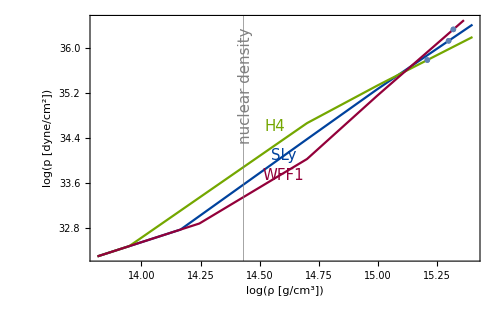

```mathematica
Show[{Plot[{Log10[1/dynecm2 Piecewise[{{168.2307577315943 ρ^1.5842, 0<ρ≤3.951404916938516*^-11}, {0.13736267772748503 ρ^1.28733, 3.951404916938516*^-11<ρ≤6.126382641611509*^-7}, {0.000010131831634389381 ρ^0.62223, 6.126382641611509*^-7<ρ≤4.2549406397186594*^-6}, {0.08949100465776093 ρ^1.35692, 4.2549406397186594*^-6<ρ≤0.00023675987283628875}, {84568.70755888449 ρ^3.005, 0.00023675987283628875<ρ≤0.000811523680823825}, {74932.08442962871 ρ^2.988, 0.000811523680823825<ρ≤0.001619202618052614}, {31070.058991119924 ρ^2.851, ρ>0.001619202618052614}, {0, True}}]]/.ρ->10^x gcm3,Log10[1/dynecm2 Piecewise[{{168.2307577315943 ρ^1.5842, 0<ρ≤3.951404916938516*^-11}, {0.13736267772748503 ρ^1.28733, 3.951404916938516*^-11<ρ≤6.126382641611509*^-7}, {0.000010131831634389381 ρ^0.62223, 6.126382641611509*^-7<ρ≤4.2549406397186594*^-6}, {0.08949100465776093 ρ^1.35692, 4.2549406397186594*^-6<ρ≤0.000143702403602157}, {82357.39635404601 ρ^2.909, 0.000143702403602157<ρ≤0.000811523680823825}, {735.4773493848038 ρ^2.246, 0.000811523680823825<ρ≤0.001619202618052614}, {381.87218341666716 ρ^2.144, ρ>0.001619202618052614}, {0, True}}]]/.ρ->10^x gcm3,Log10[1/dynecm2 Piecewise[{{168.2307577315943 ρ^1.5842, 0<ρ≤3.951404916938516*^-11}, {0.13736267772748503 ρ^1.28733, 3.951404916938516*^-11<ρ≤6.126382641611509*^-7}, {0.000010131831634389381 ρ^0.62223, 6.126382641611509*^-7<ρ≤4.2549406397186594*^-6}, {0.08949100465776093 ρ^1.35692, 4.2549406397186594*^-6<ρ≤0.0002846631772682825}, {1180.6742059205606 ρ^2.519, 0.0002846631772682825<ρ≤0.000811523680823825}, {1.008089177448561*^7 ρ^3.791, 0.000811523680823825<ρ≤0.001619202618052614}, {4.344276001629805*^6 ρ^3.66, ρ>0.001619202618052614}, {0, True}}]]/.ρ->10^x gcm3},{x,13.75,15.4},PlotRange->{{All,All},{32.3,36.5}},Frame->True,FrameLabel->{{Style["log(p [dyne/cm^2])","Latin Modern Roman",19,Black],None},{Style["log(ρ [g/cm^3])","Latin Modern Roman",18,Black],None}},RotateLabel->True,FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},PlotStyle->{{RGBColor["#00429d"]},{RGBColor["#74a700"]},{RGBColor["#93003a"]}},ImageSize->500],Table[ListPlot[{{{Log[1.9906733389871842*^15]/Log[10],Log10[1/dynecm2 Piecewise[{{168.2307577315943 ρ^1.5842, 0<ρ≤3.951404916938516*^-11}, {0.13736267772748503 ρ^1.28733, 3.951404916938516*^-11<ρ≤6.126382641611509*^-7}, {0.000010131831634389381 ρ^0.62223, 6.126382641611509*^-7<ρ≤4.2549406397186594*^-6}, {0.08949100465776093 ρ^1.35692, 4.2549406397186594*^-6<ρ≤0.00023675987283628875}, {84568.70755888449 ρ^3.005, 0.00023675987283628875<ρ≤0.000811523680823825}, {74932.08442962871 ρ^2.988, 0.000811523680823825<ρ≤0.001619202618052614}, {31070.058991119924 ρ^2.851, ρ>0.001619202618052614}, {0, True}}]]/.ρ->1.9906733389871842*^15 gcm3}},{{Log[1.6180800376430645*^15 ]/Log[10],Log10[1/dynecm2 Piecewise[{{168.2307577315943 ρ^1.5842, 0<ρ≤3.951404916938516*^-11}, {0.13736267772748503 ρ^1.28733, 3.951404916938516*^-11<ρ≤6.126382641611509*^-7}, {0.000010131831634389381 ρ^0.62223, 6.126382641611509*^-7<ρ≤4.2549406397186594*^-6}, {0.08949100465776093 ρ^1.35692, 4.2549406397186594*^-6<ρ≤0.000143702403602157}, {82357.39635404601 ρ^2.909, 0.000143702403602157<ρ≤0.000811523680823825}, {735.4773493848038 ρ^2.246, 0.000811523680823825<ρ≤0.001619202618052614}, {381.87218341666716 ρ^2.144, ρ>0.001619202618052614}, {0, True}}]]/.ρ->1.6180800376430645*^15 gcm3}},{{Log[2.0844908830972845*^15 ]/Log[10],Log10[1/dynecm2 Piecewise[{{168.2307577315943 ρ^1.5842, 0<ρ≤3.951404916938516*^-11}, {0.13736267772748503 ρ^1.28733, 3.951404916938516*^-11<ρ≤6.126382641611509*^-7}, {0.000010131831634389381 ρ^0.62223, 6.126382641611509*^-7<ρ≤4.2549406397186594*^-6}, {0.08949100465776093 ρ^1.35692, 4.2549406397186594*^-6<ρ≤0.0002846631772682825}, {1180.6742059205606 ρ^2.519, 0.0002846631772682825<ρ≤0.000811523680823825}, {1.008089177448561*^7 ρ^3.791, 0.000811523680823825<ρ≤0.001619202618052614}, {4.344276001629805*^6 ρ^3.66, ρ>0.001619202618052614}, {0, True}}]]/.ρ->2.0844908830972845*^15gcm3}}}[[p]],PlotMarkers->Style["x",{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],ImageSize->500],{p,1,3}]//Flatten},GridLines->{{{Log[2.7*10^14 ]/Log[10],Gray}},None},GridLinesStyle->Thick,Epilog->{Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.55,0.38}],{1,1},{1.7,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.53,0.46}],{1,1},{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.5,0.58}],{1,1},{1.3,1}],Text[Style["nuclear density",15,Gray],Scaled[{0.38,0.95}],{1,1},{0,1}]}]
```

```mathematica
(* Einstein frame M-R curves *)
```

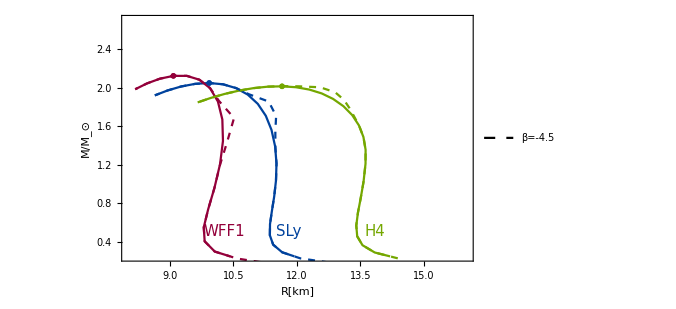

```mathematica
Show[ListLinePlot[Table[Drop[massradGRT[[h]][[1]][[1]]],{h,1,3}],PlotRange->{{Automatic,16},{0.25,2.7}},PlotStyle->{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}],ListLinePlot[Table[massradADMT[[h]][[1]][[1]],{h,1,3}],PlotStyle->{{Dashed,RGBColor["#00429d"]},{Dashed,RGBColor["#74a700"]},{Dashed,RGBColor["#93003a"]}},PlotLegends->Placed[LineLegend[{Dashed},{Style["β=-4.5",15]}],{Left,Bottom}]],ListLinePlot[Table[massradADMT[[h]][[2]][[1]],{h,1,3}],PlotStyle->{{DotDashed,RGBColor["#00429d"]},{DotDashed,RGBColor["#74a700"]},{DotDashed,RGBColor["#93003a"]}},PlotLegends->Placed[LineLegend[{DotDashed},{Style["β=-6",15]}],{Left,Bottom}]],ListPlot[Table[MaxPointsGR[[p]],{p,1,Length[EoSIndex]}],PlotStyle->{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]},PlotMarkers->Style["x",14]],Table[ListPlot[MaxPointsSTEinst[[p]][[2]][[1]],PlotMarkers->Style["o",{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}]],{p,1,Length[EoSIndex]}],Epilog->{Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.35,0.15}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.51,0.15}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.75,0.15}],{1,1}]},Frame->True,FrameLabel->{{Style["M/\!\(\*SubscriptBox[\(M\), \(⊙\)]\)","Latin Modern Roman",19,Black],None},{Style["R[km]","Latin Modern Roman",18,Black],Style["Einstein frame","Latin Modern Roman",18,Black]}},FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},ImageSize->500]
```

```mathematica
(* Jordan frame M-R curves *)
```

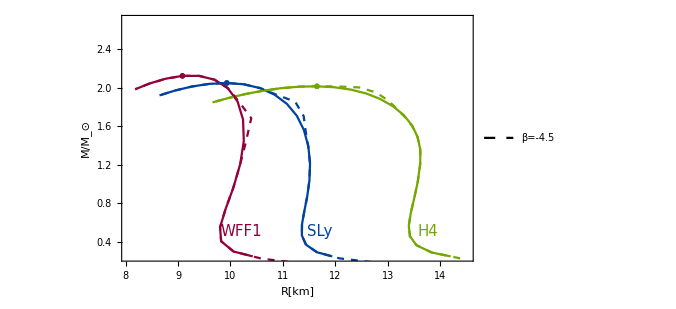

```mathematica
Show[ListLinePlot[Table[Drop[massradGRT[[h]][[1]][[1]]],{h,1,3}],PlotRange->{{Automatic,14.5},{0.25,2.7}},PlotStyle->{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}],ListLinePlot[Table[massradJordT[[h]][[1]][[1]],{h,1,3}],PlotStyle->{{Dashed,RGBColor["#00429d"]},{Dashed,RGBColor["#74a700"]},{Dashed,RGBColor["#93003a"]}},PlotLegends->Placed[LineLegend[{Dashed},{Style["β=-4.5",15]}],{Left,Bottom}]],ListLinePlot[Table[massradJordT[[h]][[2]][[1]],{h,1,3}],PlotStyle->{{DotDashed,RGBColor["#00429d"]},{DotDashed,RGBColor["#74a700"]},{DotDashed,RGBColor["#93003a"]}},PlotLegends->Placed[LineLegend[{DotDashed},{Style["β=-6",15]}],{Left,Bottom}]],ListPlot[Table[MaxPointsGR[[p]],{p,1,Length[EoSIndex]}],PlotStyle->{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]},PlotMarkers->Style["x",14]],Table[ListPlot[MaxPointsSTJord[[p]][[2]][[1]],PlotMarkers->Style["o",{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}]],{p,1,Length[EoSIndex]}],Epilog->{Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.4,0.15}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.60,0.15}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.9,0.15}],{1,1}]},Frame->True,FrameLabel->{{Style["M/\!\(\*SubscriptBox[\(M\), \(⊙\)]\)","Latin Modern Roman",19,Black],None},{Style["R[km]","Latin Modern Roman",18,Black],Style["Jordan frame","Latin Modern Roman",18,Black]}},FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},ImageSize->500]
```

```mathematica
(* Charge-Mass curves*)
```

```mathematica
(* Einstein frame q-M curves *)
```

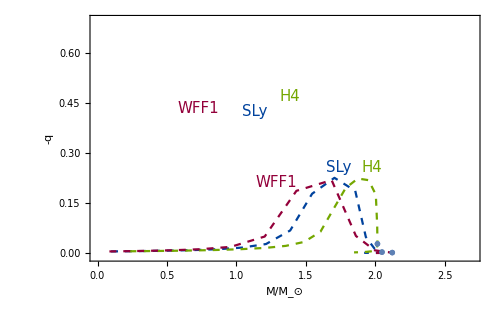

```mathematica
Show[ListLinePlot[Table[Table[{ADMMassTableT[[h]][[1]][[1]][[p]],-ChargeTableT[[h]][[1]][[1]][[All,2]][[p]]},{p,1,Length[ρvals]}],{h,1,3}],PlotRange->{{0,2.7},{-0.01,0.7}},AxesLabel->{"M/M_⊙","-q"},PlotStyle->{{Dashed,RGBColor["#00429d"]},{Dashed,RGBColor["#74a700"]},{Dashed,RGBColor["#93003a"]}},PlotLegends->Placed[LineLegend[{Dashed},{Style["β_0=-4.5",15]}],{Left,Top}]],ListLinePlot[Table[Table[{ADMMassTableT[[h]][[2]][[1]][[p]],-ChargeTableT[[h]][[2]][[1]][[All,2]][[p]]},{p,1,Length[ρvals]}],{h,1,3}],PlotRange->All,AxesLabel->{"M_NS/M_⊙","-q"},PlotStyle->{{DotDashed,RGBColor["#00429d"]},{DotDashed,RGBColor["#74a700"]},{DotDashed,RGBColor["#93003a"]}},PlotLegends->Placed[LineLegend[{DotDashed},{Style["β_0=-6",15]}],{Left,Top}]],Table[ListPlot[{{ADMMassTableT[[p]][[β]][[1]][[MaxPointsSTEinstIndex[[p]][[β]][[1]]]],-ChargeTableT[[p]][[β]][[1]][[All,2]][[MaxPointsSTEinstIndex[[p]][[β]][[1]]]]}},PlotMarkers->Style[{"x","o"}[[β]],{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}],Frame->True,FrameLabel->{{Style["-q","Latin Modern Roman",19,Black],None},{Style["M/M_⊙","Latin Modern Roman",18,Black],Style["Einstein frame φ_∞=10^-3","Latin Modern Roman",18,Black]}},RotateLabel->False,FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},Epilog->{Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.33,0.65}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.455,0.64}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.54,0.7}],{1,1}],Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.53,0.35}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.67,0.41}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.75,0.41}],{1,1}]},ImageSize->500]//Quiet
```

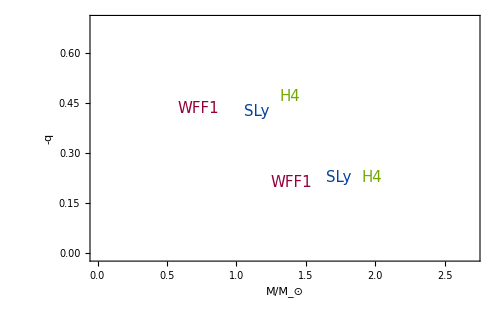

```mathematica
Show[ListLinePlot[Table[Table[{ADMMassTableT[[h]][[1]][[2]][[p]],-ChargeTableT[[h]][[1]][[2]][[All,2]][[p]]},{p,1,Length[ρvals]}],{h,1,3}],PlotRange->{{0,2.7},{-0.01,0.7}},AxesLabel->{"M/M_⊙","-q"},PlotStyle->{{Dashed,RGBColor["#00429d"]},{Dashed,RGBColor["#74a700"]},{Dashed,RGBColor["#93003a"]}},PlotLegends->Placed[LineLegend[{Dashed},{Style["β=-4.5",15]}],{Left,Top}]],ListLinePlot[Table[Table[{ADMMassTableT[[h]][[2]][[3]][[p]],-ChargeTableT[[h]][[2]][[3]][[All,2]][[p]]},{p,1,Length[ρvals]}],{h,1,3}],PlotRange->All,AxesLabel->{"M_NS/M_⊙","-q"},PlotStyle->{{DotDashed,RGBColor["#00429d"]},{DotDashed,RGBColor["#74a700"]},{DotDashed,RGBColor["#93003a"]}},PlotLegends->Placed[LineLegend[{DotDashed},{Style["β=-6",15]}],{Left,Top}]],Table[ListPlot[{{ADMMassTableT[[p]][[β]][[3]][[MaxPointsSTEinstIndex[[p]][[β]][[3]]]],-ChargeTableT[[p]][[β]][[3]][[All,2]][[MaxPointsSTEinstIndex[[p]][[β]][[3]]]]}},PlotMarkers->Style[{"x","o"}[[β]],{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}],Frame->True,FrameLabel->{{Style["-q","Latin Modern Roman",19,Black],None},{Style["M/M_⊙","Latin Modern Roman",18,Black],Style["Einstein frame φ_∞=10^-6","Latin Modern Roman",18,Black]}},RotateLabel->False,FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},Epilog->{Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.33,0.65}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.46,0.64}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.54,0.7}],{1,1}],Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.57,0.35}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.67,0.37}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.75,0.37}],{1,1}]},ImageSize->500]//Quiet
```

```mathematica
(* Jordan frame  q-M curves*)
```

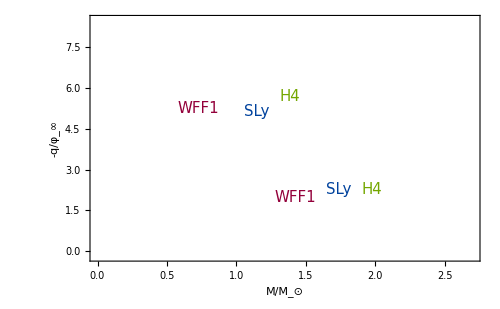

```mathematica
Show[ListLinePlot[Table[Table[{massradJordT[[h]][[1]][[3]][[All,2]][[p]],-ChargeTableT[[h]][[1]][[3]][[All,2]][[p]]*(-2 βvals[[1]] )/(1+βvals[[1]]^2 φinfvals[[1]]^2)ⅇ^(-3/2 βvals[[1]] φinfvals[[1]]^2)},{p,1,Length[ρvals]}],{h,1,3}],PlotRange->{{0,2.7},{-0.2,8.5}},AxesLabel->{"M/M_⊙","-q"},PlotStyle->{{Dashed,RGBColor["#00429d"]},{Dashed,RGBColor["#74a700"]},{Dashed,RGBColor["#93003a"]}},PlotLegends->Placed[LineLegend[{Dashed},{Style["β=-4.5",15]}],{Left,Top}]],ListLinePlot[Table[Table[{massradJordT[[h]][[2]][[3]][[All,2]][[p]],-ChargeTableT[[h]][[2]][[3]][[All,2]][[p]]*(-2 βvals[[2]] )/(1+βvals[[2]]^2 φinfvals[[1]]^2)ⅇ^(-3/2 βvals[[2]] φinfvals[[1]]^2)},{p,1,Length[ρvals]}],{h,1,3}],PlotRange->All,AxesLabel->{"M/M_⊙","-q"},PlotStyle->{{DotDashed,RGBColor["#00429d"]},{DotDashed,RGBColor["#74a700"]},{DotDashed,RGBColor["#93003a"]}},PlotLegends->Placed[LineLegend[{DotDashed},{Style["β=-6",15]}],{Left,Top}]],Frame->True,FrameLabel->{{Style["-q/φ_∞","Latin Modern Roman",19,Black],None},{Style["M/M_⊙","Latin Modern Roman",18,Black],Style["Jordan frame φ_∞=10^-3","Latin Modern Roman",18,Black]}},RotateLabel->False,FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},Epilog->{Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.33,0.65}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.46,0.64}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.54,0.7}],{1,1}],Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.58,0.29}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.67,0.32}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.75,0.32}],{1,1}]},ImageSize->500]//Quiet
```

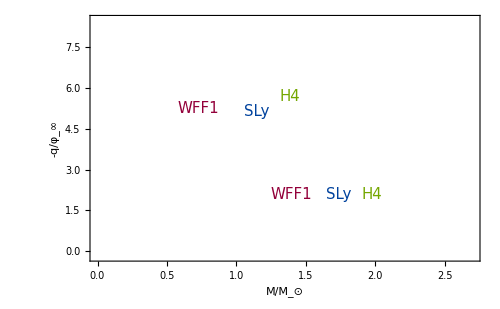

```mathematica
Show[ListLinePlot[Table[Table[{massradJordT[[h]][[1]][[3]][[All,2]][[p]],-ChargeTableT[[h]][[1]][[3]][[All,2]][[p]]*(-2 βvals[[1]])/(1+βvals[[1]]^2 φinfvals[[3]]^2)ⅇ^(-3/2 βvals[[1]] φinfvals[[3]]^2)},{p,1,Length[ρvals]}],{h,1,3}],PlotRange->{{0,2.7},{-0.2,8.5}},AxesLabel->{"M/M_⊙","-q"},PlotStyle->{{Dashed,RGBColor["#00429d"]},{Dashed,RGBColor["#74a700"]},{Dashed,RGBColor["#93003a"]}},PlotLegends->Placed[LineLegend[{Dashed},{Style["β=-4.5",15]}],{Left,Top}]],ListLinePlot[Table[Table[{massradJordT[[h]][[2]][[3]][[All,2]][[p]],-ChargeTableT[[h]][[2]][[3]][[All,2]][[p]]*(-2 βvals[[2]])/(1+βvals[[2]]^2 φinfvals[[3]]^2)ⅇ^(-3/2 βvals[[2]] φinfvals[[3]]^2)},{p,1,Length[ρvals]}],{h,1,3}],PlotRange->All,AxesLabel->{"M/M_⊙","-q"},PlotStyle->{{DotDashed,RGBColor["#00429d"]},{DotDashed,RGBColor["#74a700"]},{DotDashed,RGBColor["#93003a"]}},PlotLegends->Placed[LineLegend[{DotDashed},{Style["β=-6",15]}],{Left,Top}]],Frame->True,FrameLabel->{{Style["-q/φ_∞","Latin Modern Roman",19,Black],None},{Style["M/M_⊙","Latin Modern Roman",18,Black],Style["Jordan frame φ_∞=10^-6","Latin Modern Roman",18,Black]}},RotateLabel->False,FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},Epilog->{Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.33,0.65}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.46,0.64}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.54,0.7}],{1,1}],Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.57,0.3}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.67,0.3}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.75,0.3}],{1,1}]},ImageSize->500]//Quiet
```

### Perturbations

#### Integrating inside the star

```mathematica
(* Equations of motion *)
```

```mathematica
(* Scalar field *)
```

```mathematica
(* Inside the star *)
```

```mathematica
eqφp=Collect[EoMscalarpert/(r (r-2 GN mm[r])ⅇ^ν[r])/.r->r[]/.δprule/.ωp->0/.ll->l(l+1)/.EoMscalarRWback/.dnudgammasubs/.γsol/.r[]->r/.A'[φ0[r]]->-α[φ0[r]] A[φ0[r]]/.GN->1//Expand//FullSimplify,{Derivative[_][φp][r],φp[r],H0},FullSimplify];
(* Outside the star *)
eqpH=eqφp/.nofluid;
```

```mathematica
(* Tensor field *)
```

```mathematica
(* Outside the star *)
```

```mathematica
mastereqwithbackOUT=-mastereqH0/.nofluid;
(* For dipolar perturbations we obtained a first order (FO) dif. eq. *)
mastereqH0F0=H0'[r]+(φp[r] (8 (-mm[r]+r) φ0'[r]+4 r^2 (-2 mm[r]+r) φ0'[r]^3+16 π A[φ0[r]]^4 r^2 (α[φ0[r]] (-3 p0[r]+ρ0[r])+2 p0[r] r φ0'[r])))/(2 mm[r]+8 π A[φ0[r]]^4 p0[r] r^3+r^2 (-2 mm[r]+r) φ0'[r]^2)+1/r H0[r] ((2 (-mm[r]+r+4 π A[φ0[r]]^4 p0[r] r^3))/(-2 mm[r]+r)+r^2 φ0'[r]^2-(8 π A[φ0[r]]^4 r^3 (3 p0[r]+ρ0[r]))/(2 mm[r]+8 π A[φ0[r]]^4 p0[r] r^3+r^2 (-2 mm[r]+r) φ0'[r]^2))+(4 r (-2 mm[r]+r) φ0'[r] φp'[r])/(2 mm[r]+8 π A[φ0[r]]^4 p0[r] r^3+r^2 (-2 mm[r]+r) φ0'[r]^2)/.r[]->r;
mastereqH0F0OUT=mastereqH0F0/.nofluid;
```

```mathematica
(* Inside the star the differential equations are coupled *)
```

```mathematica
EoMscalarpertINN=Table[eqφp/.PiecePolytroperuleT[[p]],{p,1,Length[EoSIndex]}];
```

```mathematica
mastereqwithbackINN=Table[mastereqH0/.PiecePolytroperuleT[[p]],{p,1,Length[EoSIndex]}];
mastereqwithbackINNFO=Table[mastereqH0F0/.PiecePolytroperuleT[[p]],{p,1,Length[EoSIndex]}];
```

```mathematica
(* Integrators for the perturbations inside the star *)
```

```mathematica
(* l≠1 *)
```

```mathematica
H0φpsolOrigintoSurfaceNoScalar[p_,β_,φinf_,h_,ll_]:=NDSolve[SetPrecision[{mastereqwithbackINN[[p]]==0,EoMscalarpertINN[[p]]==0,φp[rmin]==0,φp'[rmin]== 0,H0[rmin]==rmin^ll,H0'[rmin]== ll rmin^(ll-1)}/.A[φ0[r]]->ⅇ^(1/2 βvals[[β]] φ0[r]^2)/.A'[φ0[r]]->D[ⅇ^(1/2 βvals[[β]] φ0[r]^2),φ0[r]]/.α[φ0[r]]->-βvals[[β]]φ0[r]/.α'[φ0[r]]->-βvals[[β]]/.l->ll/.BackgroundTOVPieceT[[p]][[β]][[φinf]][[h]],100],{φp,H0},{r,rmin,massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km},Method->{"DiscontinuityProcessing"->False},MaxSteps->100000]//Quiet
H0φpsolOrigintoSurfaceNoTensor[p_,β_,φinf_,h_,ll_]:=NDSolve[SetPrecision[{mastereqwithbackINN[[p]]==0,EoMscalarpertINN[[p]]==0,φp[rmin]==rmin^ll,φp'[rmin]== ll rmin^(ll-1),H0[rmin]==0,H0'[rmin]== 0}/.A[φ0[r]]->ⅇ^(1/2 βvals[[β]] φ0[r]^2)/.A'[φ0[r]]->D[ⅇ^(1/2 βvals[[β]] φ0[r]^2),φ0[r]]/.α[φ0[r]]->-βvals[[β]]φ0[r]/.α'[φ0[r]]->-βvals[[β]]/.l->ll/.BackgroundTOVPieceT[[p]][[β]][[φinf]][[h]],100],{φp,H0},{r,rmin,massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km},WorkingPrecision->25,Method->{"DiscontinuityProcessing"->False},MaxSteps->100000]//Quiet
```

```mathematica
(* l=1 *)
```

```mathematica
H0φpsolOrigintoSurfaceNoScalarl11[p_,β_,φinf_,h_]:=NDSolve[SetPrecision[{mastereqH0F0==0,eqφp==0,H0[rmin]==rmin,φp'[rmin]== 0,φp[rmin]==0}/.r[]->r/.A[φ0[r]]->ⅇ^(1/2 βvals[[β]] φ0[r]^2)/.A'[φ0[r]]->D[ⅇ^(1/2 βvals[[β]] φ0[r]^2),φ0[r]]/.α[φ0[r]]->-βvals[[β]]φ0[r]/.α'[φ0[r]]->-βvals[[β]]/.l->ll/.ll->1/.r[]->r/.PiecePolytroperuleT[[p]]/.BackgroundTOVPieceT[[p]][[β]][[φinf]][[h]]//First,50],{φp,H0},{r,rmin,massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km},Method->{"DiscontinuityProcessing"->False}]//Quiet
H0φpsolOrigintoSurfaceNoTensorl11[p_,β_,φinf_,h_]:=NDSolve[SetPrecision[{mastereqH0F0==0,eqφp==0,H0[rmin]==0,φp'[rmin]== 1,φp[rmin]==rmin}/.r[]->r/.A[φ0[r]]->ⅇ^(1/2 βvals[[β]] φ0[r]^2)/.A'[φ0[r]]->D[ⅇ^(1/2 βvals[[β]] φ0[r]^2),φ0[r]]/.α[φ0[r]]->-βvals[[β]]φ0[r]/.α'[φ0[r]]->-βvals[[β]]/.l->ll/.ll->1/.r[]->r/.PiecePolytroperuleT[[p]]/.BackgroundTOVPieceT[[p]][[β]][[φinf]][[h]]//First,50],{φp,H0},{r,rmin,massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km},Method->{"StiffnessSwitching","DiscontinuityProcessing"->False}]//Quiet
```

```mathematica
(* Integrating *)
```

```mathematica
(* l=1  *)
```

```mathematica
H0φpsolOrigintoSurfaceTablel1NoScalarφ1=Table[H0φpsolOrigintoSurfaceNoScalarl11[p,β,1,h]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{h,1,Length[ρvals]}];
(* Uncomment to save into file
AddtoList[Unevaluated[{H0φpsolOrigintoSurfaceTablel1NoScalarφ1}]];
Export[FileNameJoin[{NotebookDirectory[],"Love_Number_ST_H0φpsolOrigintoSurfaceTablel1φ1.m"}],ExportList4];*)
```

```mathematica
H0φpsolOrigintoSurfaceTablel1NoTensorφ1=Table[H0φpsolOrigintoSurfaceNoTensorl11[p,β,1,h]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{h,1,Length[ρvals]}];
```

```mathematica
(* l=2  *)
```

```mathematica
(* Due to the size of the computation we have to split it into three, one per Subscript[φ, ∞] per field. This might change when changing the value of Subscript[φ, ∞] or adding more values of Subscript[φ, ∞] to compute. Same applies to l=3 below.*)
```

```mathematica
H0φpsolOrigintoSurfaceTablel2NoScalarφ1=ParallelTable[H0φpsolOrigintoSurfaceNoScalar[p,β,1,h,2]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{h,1,Length[ρvals]}];
```

```mathematica
(* Uncomment to save into file
AddtoList[Unevaluated[{H0φpsolOrigintoSurfaceTablel2NoScalarφ1}]];
Export[FileNameJoin[{NotebookDirectory[],"Love_Number_ST_H0φpsolOrigintoSurfaceTablel2φ1.m"}],ExportList4];*)
```

```mathematica
H0φpsolOrigintoSurfaceTablel2NoTensorφ1=ParallelTable[H0φpsolOrigintoSurfaceNoTensor[p,β,1,h,2]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{h,1,Length[ρvals]}];
(* Uncomment to save into file
AddtoList[Unevaluated[{H0φpsolOrigintoSurfaceTablel2NoTensorφ1}]];Export[FileNameJoin[{NotebookDirectory[],"Love_Number_ST_H0φpsolOrigintoSurfaceTablel2φ1.m"}],ExportList4];*)
```

```mathematica
H0φpsolOrigintoSurfaceTablel2NoScalarφ2=ParallelTable[H0φpsolOrigintoSurfaceNoScalar[p,β,2,h,2]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{h,1,Length[ρvals]}];
(* Uncomment to save into file
AddtoList5[Unevaluated[{H0φpsolOrigintoSurfaceTablel2NoScalarφ2}]];Export[FileNameJoin[{NotebookDirectory[],"Love_Number_ST_H0φpsolOrigintoSurfaceTablel2φ2.m"}],ExportList5];*)
```

```mathematica
H0φpsolOrigintoSurfaceTablel2NoTensorφ2=ParallelTable[H0φpsolOrigintoSurfaceNoTensor[p,β,2,h,2]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{h,1,Length[ρvals]}];
(* Uncomment to save into file
AddtoList5[Unevaluated[{H0φpsolOrigintoSurfaceTablel2NoTensorφ2}]];Export[FileNameJoin[{NotebookDirectory[],"Love_Number_ST_H0φpsolOrigintoSurfaceTablel2φ2.m"}],ExportList5];*)
```

```mathematica
H0φpsolOrigintoSurfaceTablel2NoScalarφ3=ParallelTable[H0φpsolOrigintoSurfaceNoScalar[p,β,3,h,2]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{h,1,Length[ρvals]}];
(* Uncomment to save into file
AddtoList[Unevaluated[{H0φpsolOrigintoSurfaceTablel2NoScalarφ3}]];Export[FileNameJoin[{NotebookDirectory[],"Love_Number_ST_H0φpsolOrigintoSurfaceTablel2φ3.m"}],ExportList4];*)
```

```mathematica
H0φpsolOrigintoSurfaceTablel2NoTensorφ3=ParallelTable[H0φpsolOrigintoSurfaceNoTensor[p,β,3,h,2]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{h,1,Length[ρvals]}];(* Uncomment to save into file
AddtoList[Unevaluated[{H0φpsolOrigintoSurfaceTablel2NoTensorφ3}]];Export[FileNameJoin[{NotebookDirectory[],"Love_Number_ST_H0φpsolOrigintoSurfaceTablel2φ3.m"}],ExportList4];
AddtoList[Unevaluated[{H0φpsolOrigintoSurfaceTablel2NoScalar,H0φpsolOrigintoSurfaceTablel2NoTensor}]];*)
```

```mathematica
(* l=3  *)
```

```mathematica
H0φpsolOrigintoSurfaceTablel3NoScalarφ1=ParallelTable[H0φpsolOrigintoSurfaceNoScalar[p,β,1,h,3]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{h,1,Length[ρvals]}];
(* Uncomment to save into file
AddtoList[Unevaluated[{H0φpsolOrigintoSurfaceTablel3NoScalarφ1}]];
Export[FileNameJoin[{NotebookDirectory[],"Love_Number_ST_H0φpsolOrigintoSurfaceTablel3φ1.m"}],ExportList4];*)
```

```mathematica
H0φpsolOrigintoSurfaceTablel3NoTensorφ1=ParallelTable[H0φpsolOrigintoSurfaceNoTensor[p,β,1,h,3]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{h,1,Length[ρvals]}];
(* Uncomment to save into file
AddtoList[Unevaluated[{H0φpsolOrigintoSurfaceTablel3NoTensorφ1}]];Export[FileNameJoin[{NotebookDirectory[],"Love_Number_ST_H0φpsolOrigintoSurfaceTablel3φ1.m"}],ExportList4];*)
```

```mathematica
H0φpsolOrigintoSurfaceTablel3NoScalarφ2=ParallelTable[H0φpsolOrigintoSurfaceNoScalar[p,β,2,h,3]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{h,1,Length[ρvals]}];
(* Uncomment to save into file
AddtoList5[Unevaluated[{H0φpsolOrigintoSurfaceTablel3NoScalarφ2}]];Export[FileNameJoin[{NotebookDirectory[],"Love_Number_ST_H0φpsolOrigintoSurfaceTablel3φ2.m"}],ExportList4];*)
```

```mathematica
H0φpsolOrigintoSurfaceTablel3NoTensorφ2=ParallelTable[H0φpsolOrigintoSurfaceNoTensor[p,β,2,h,3]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{h,1,Length[ρvals]}];
(* Uncomment to save into file
AddtoList5[Unevaluated[{H0φpsolOrigintoSurfaceTablel3NoTensorφ2}]];Export[FileNameJoin[{NotebookDirectory[],"Love_Number_ST_H0φpsolOrigintoSurfaceTablel3φ2.m"}],ExportList4];*)
```

```mathematica
H0φpsolOrigintoSurfaceTablel3NoScalarφ3=ParallelTable[H0φpsolOrigintoSurfaceNoScalar[p,β,3,h,3]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{h,1,Length[ρvals]}];(* Uncomment to save into file
AddtoList[Unevaluated[{H0φpsolOrigintoSurfaceTablel3NoScalarφ3}]];Export[FileNameJoin[{NotebookDirectory[],"Love_Number_ST_H0φpsolOrigintoSurfaceTablel3φ3.m"}],ExportList4];*)
```

```mathematica
H0φpsolOrigintoSurfaceTablel3NoTensorφ3=ParallelTable[H0φpsolOrigintoSurfaceNoTensor[p,β,3,h,3]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{h,1,Length[ρvals]}];(* Uncomment to save into file
AddtoList[Unevaluated[{H0φpsolOrigintoSurfaceTablel3NoTensorφ3}]];Export[FileNameJoin[{NotebookDirectory[],"Love_Number_ST_H0φpsolOrigintoSurfaceTablel2φ3.m"}],ExportList4];*)
```

```mathematica
(* Uncomment to save into file
AddtoList[Unevaluated[{H0φpsolOrigintoSurfaceTablel2NoScalar,H0φpsolOrigintoSurfaceTablel2NoTensor}]];*)
```

#### Series solution at the origin

```mathematica
(* Eqs *)
```

```mathematica
eqp0prime=p0'[r[]]/.p0primeofm/.γsol/.m[r]->mm[r]/.GN->1/.r[]->r/.α[φ0[r_]]->-1/A[φ0[r]] A'[φ0[r]]/.A[φ0[r_]]->ⅇ^(1/2 β φ0[r]^2)/.A'[φ0[r_]]->ⅇ^(1/2 β φ0[r]^2)β φ0[r]//First//Expand//Simplify;
 eqmassprime=mm'[r[]]/.mprime/.GN->1/.r[]->r/.α[φ0[r_]]->-1/A[φ0[r]] A'[φ0[r]]/.A[φ0[r_]]->ⅇ^(1/2 β φ0[r]^2)/.A'[φ0[r_]]->ⅇ^(1/2 β φ0[r]^2)β φ0[r]//Expand//Simplify;
φ0eqin=φ0''[r[]]/.EoMscalarRWback/.nuprimeofp/.D[nuprimeofp,r[]]/.dnudgammasubs/.p0primeofm/.γsol/.m[r]->mm[r]/.GN->1/.α[φ0[r_]]->-1/A[φ0[r]] A'[φ0[r]]/.A[φ0[r_]]->ⅇ^(1/2 β φ0[r]^2)/.A'[φ0[r_]]->ⅇ^(1/2 β φ0[r]^2)β φ0[r]/.r[]->r//First//Expand//Simplify;
H0pertEQfirst=H0'[r]+(φp[r] (8 (-mm[r]+r) φ0'[r]+4 r^2 (-2 mm[r]+r) φ0'[r]^3+16 π A[φ0[r]]^4 r^2 (α[φ0[r]] (-3 p0[r]+ρ0[r])+2 p0[r] r φ0'[r])))/(2 mm[r]+8 π A[φ0[r]]^4 p0[r] r^3+r^2 (-2 mm[r]+r) φ0'[r]^2)+1/r H0[r] ((2 (-mm[r]+r+4 π A[φ0[r]]^4 p0[r] r^3))/(-2 mm[r]+r)+r^2 φ0'[r]^2-(8 π A[φ0[r]]^4 r^3 (3 p0[r]+ρ0[r]))/(2 mm[r]+8 π A[φ0[r]]^4 p0[r] r^3+r^2 (-2 mm[r]+r) φ0'[r]^2))+(4 r (-2 mm[r]+r) φ0'[r] φp'[r])/(2 mm[r]+8 π A[φ0[r]]^4 p0[r] r^3+r^2 (-2 mm[r]+r) φ0'[r]^2)/.r[]->r/.α[φ0[r_]]->-1/A[φ0[r]] A'[φ0[r]]/.A[φ0[r_]]->ⅇ^(1/2 β φ0[r]^2)/.A'[φ0[r_]]->ⅇ^(1/2 β φ0[r]^2)β φ0[r];
```

```mathematica
(* Series solution *)
```

```mathematica
Orderinf=3;
(* Here as an example we use MultipoleOrder=1, which corresponds to dipolar perturbations *)
MultipoleOrder=1;
φ0S=Sum[φ0n[n] r^n,{n,0,Orderinf}];
p0S=Sum[p0n[n] r^n,{n,0,Orderinf}];
ρ0S=Sum[ρ0n[n] r^n,{n,0,Orderinf}];
mS=Sum[mm[n] r^n,{n,3,Orderinf}];
H0S=Sum[H0n[n] r^n,{n,-3,Orderinf}];
φpS=Sum[φpn[n] r^n,{n,-3,Orderinf}];
```

```mathematica
Eqinf1=r(p0'[r]-eqp0prime)/.r[]->r/.GN->1/.H0[r_]->H0S/.H0'[r_]->D[H0S,r]/.H0''[r_]->D[H0S,{r,2}]/.φp[r_]->φpS/.mm[r_]->mS/.mm'[r_]->D[mS,r]/.φ0'[r_]->D[φ0S,r]/.φp'[r_]->D[φpS,r]/.ρ0[r_]->ρ0S/.ρ0'[r_]->D[ρ0S,r]/.p0[r_]->p0S/.p0'[r_]->D[p0S,r]/.φ0[r_]->φ0S;
Eqinf2=r^2 (φ0''[r]-φ0eqin)/.r[]->r/.GN->1/.H0[r_]->H0S/.φp'[r_]->D[φpS,r]/.φp''[r_]->D[φpS,{r,2}]/.φp[r_]->φpS/.mm[r_]->mS/.mm'[r_]->D[mS,r]/.φ0'[r_]->D[φ0S,r]/.φ0''[r_]->D[φ0S,{r,2}]/.ρ0[r_]->ρ0S/.ρ0'[r_]->D[ρ0S,r]/.p0[r_]->p0S/.p0'[r_]->D[p0S,r]/.φ0[r_]->φ0S;
Eqinf3=r(mm'[r]- eqmassprime)/.GN->1/.H0[r_]->H0S/.φp'[r_]->D[φpS,r]/.φp''[r_]->D[φpS,{r,2}]/.φp[r_]->φpS/.mm[r_]->mS/.mm'[r_]->D[mS,r]/.φ0'[r_]->D[φ0S,r]/.φ0''[r_]->D[φ0S,{r,2}]/.ρ0[r_]->ρ0S/.ρ0'[r_]->D[ρ0S,r]/.p0[r_]->p0S/.p0'[r_]->D[p0S,r]/.φ0[r_]->φ0S;
Eqinf4=r*H0pertEQfirst/.r[]->r/.GN->1/.ll->l(l+1)/.l->MultipoleOrder/.H0[r_]->H0S/.H0'[r_]->D[H0S,r]/.H0''[r_]->D[H0S,{r,2}]/.φp[r_]->φpS/.mm[r_]->mS/.mm'[r_]->D[mS,r]/.φ0'[r_]->D[φ0S,r]/.φ0''[r_]->D[φ0S,{r,2}]/.φp'[r_]->D[φpS,r]/.φ0[r_]->φ0S/.ρ0[r_]->ρ0S/.ρ0'[r_]->D[ρ0S,r]/.p0[r_]->p0S/.p0'[r_]->D[p0S,r];
Eqinf5=r^2 eqφp/.r[]->r/.ll->l(l+1)/.l->MultipoleOrder/.GN->1/.α[φ0[r_]]->-1/A[φ0[r]] A'[φ0[r]]/.α'[φ0[r_]]->-1/A[φ0[r]] A''[φ0[r]]+A'[φ0[r]]^2 1/A[φ0[r]]^2/.A[φ0[r_]]->ⅇ^(1/2 β φ0[r]^2)/.A'[φ0[r_]]->ⅇ^(1/2 β φ0[r]^2)β φ0[r]/.A''[φ0[r_]]->ⅇ^(1/2 β φ0[r]^2)(β φ0[r])^2+ⅇ^(1/2 β φ0[r]^2)β φ0[r]/.H0[r_]->H0S/.φp'[r_]->D[φpS,r]/.φp''[r_]->D[φpS,{r,2}]/.φp[r_]->φpS/.mm[r_]->mS/.mm'[r_]->D[mS,r]/.φ0'[r_]->D[φ0S,r]/.φ0''[r_]->D[φ0S,{r,2}]/.φ0[r_]->φ0S/.ρ0[r_]->ρ0S/.ρ0'[r_]->D[ρ0S,r]/.p0[r_]->p0S/.p0'[r_]->D[p0S,r];
```

```mathematica
(* Background *)
```

```mathematica
SeriesSolBack=Join[Series[{Eqinf1,Eqinf2,Eqinf3},{r,0,Orderinf}]];
EqsInfBack=Join[Table[SeriesCoefficient[SeriesSolBack[[1]],p]==0,{p,1,Orderinf}],Table[SeriesCoefficient[SeriesSolBack[[2]],p]==0,{p,1,Orderinf}],Table[SeriesCoefficient[SeriesSolBack[[3]],p]==0,{p,3,Orderinf}]]//Flatten//Simplify;
OrdersolsBack=Join[Table[{φ0n[n]},{n,1,Orderinf}],Table[{mm[n]},{n,3,Orderinf}],Table[{p0n[n]},{n,1,Orderinf}]]//Flatten;
SeriesSolCoeffsBack=Solve[EqsInfBack,OrdersolsBack]//FullSimplify
```

{{φ0n[1]→0,φ0n[2]→-2/3 ⅇ^(2 β φ0n[0]^2) π β (3 p0n[0]-ρ0n[0]) φ0n[0],φ0n[3]→1/3 ⅇ^(2 β φ0n[0]^2) π β ρ0n[1] φ0n[0],mm[3]→4/3 ⅇ^(2 β φ0n[0]^2) π ρ0n[0],p0n[1]→0,p0n[2]→2/3 ⅇ^(2 β φ0n[0]^2) π (p0n[0]+ρ0n[0]) (-3 p0n[0]-ρ0n[0]+β^2 (3 p0n[0]-ρ0n[0]) φ0n[0]^2),p0n[3]→1/9 ⅇ^(2 β φ0n[0]^2) π ρ0n[1] (-4 (3 p0n[0]+ρ0n[0])+β^2 (9 p0n[0]-7 ρ0n[0]) φ0n[0]^2)}}

```mathematica
(* Scalar field, pressure and mass at the origin*)
```

```mathematica
φ0S=Sum[φ0n[n] r^n,{n,0,Orderinf}]/.SeriesSolCoeffsBack
p0S=Sum[p0n[n] r^n,{n,0,Orderinf}]/.SeriesSolCoeffsBack
mS=Sum[mm[n] r^n,{n,3,Orderinf}]/.SeriesSolCoeffsBack
```

{φ0n[0]-2/3 ⅇ^(2 β φ0n[0]^2) π r^2 β (3 p0n[0]-ρ0n[0]) φ0n[0]+1/3 ⅇ^(2 β φ0n[0]^2) π r^3 β ρ0n[1] φ0n[0]}

{p0n[0]+1/9 ⅇ^(2 β φ0n[0]^2) π r^3 ρ0n[1] (-4 (3 p0n[0]+ρ0n[0])+β^2 (9 p0n[0]-7 ρ0n[0]) φ0n[0]^2)+2/3 ⅇ^(2 β φ0n[0]^2) π r^2 (p0n[0]+ρ0n[0]) (-3 p0n[0]-ρ0n[0]+β^2 (3 p0n[0]-ρ0n[0]) φ0n[0]^2)}

{4/3 ⅇ^(2 β φ0n[0]^2) π r^3 ρ0n[0]}

```mathematica
(* Dipolar perturbations *)
```

```mathematica
SeriesSolPert=Join[Series[{Eqinf4,Eqinf5}/.SeriesSolCoeffsBack,{r,0,Orderinf}]]//Flatten//Simplify;
```

```mathematica
SeriesSolPert=Join[Series[{Eqinf4,Eqinf5}/.SeriesSolCoeffsBack,{r,0,Orderinf}]]//Flatten//Simplify;
EqsInfPert=Join[Table[{SeriesCoefficient[SeriesSolPert[[1]],p]==0},{p,-3,Orderinf}],Table[{SeriesCoefficient[SeriesSolPert[[2]],p]==0},{p,-3,Orderinf}]]//Flatten//Simplify;
OrdersolsPert=Join[Table[{H0n[n]},{n,-3,Orderinf}],Table[{φpn[n]},{n,-3,Orderinf}]]//Flatten;
SeriesSolCoeffsPert=Solve[EqsInfPert,OrdersolsPert]//Simplify
```

{{H0n[-3]→0,H0n[-2]→0,H0n[-1]→0,H0n[0]→0,H0n[2]→(3 ρ0n[1] (2 H0n[1]+β φ0n[0] φpn[1]))/(2 (3 p0n[0]+ρ0n[0])),H0n[3]→1/(60 (3 p0n[0]+ρ0n[0])^2)(45 (2 H0n[1] (3 ρ0n[1]^2+(3 p0n[0]+ρ0n[0]) ρ0n[2])+β (3 ρ0n[1]^2+4 (3 p0n[0]+ρ0n[0]) ρ0n[2]) φ0n[0] φpn[1])-4 ⅇ^(2 β φ0n[0]^2) π (3 p0n[0]+ρ0n[0]) (H0n[1] (9 p0n[0]^2 (20+β^2 (-3+2 Deriv[0]) φ0n[0]^2)+ρ0n[0]^2 (20-3 β^2 (13+2 Deriv[0]) φ0n[0]^2)+6 p0n[0] ρ0n[0] (20+β^2 (21+2 Deriv[0]) φ0n[0]^2))+6 β φ0n[0] (-ρ0n[0]^2 (25+β (5-2 φ0n[0])+β^2 (21+2 Deriv[0]) φ0n[0]^2)+2 p0n[0] ρ0n[0] (-6+β (15-6 φ0n[0])+β^2 (45+2 Deriv[0]) φ0n[0]^2)+3 p0n[0]^2 (-33+β^2 (-27+2 Deriv[0]) φ0n[0]^2+3 β (-5+2 φ0n[0]))) φpn[1])),φpn[-3]→0,φpn[-2]→0,φpn[-1]→0,φpn[0]→0,φpn[2]→0,φpn[3]→-1/15 ⅇ^(2 β φ0n[0]^2) π (2 (3 p0n[0]-5 ρ0n[0]) φpn[1]+6 β^2 ((9+Deriv[0]) p0n[0]+(-7+Deriv[0]) ρ0n[0]) φ0n[0]^2 φpn[1]+3 β φ0n[0] (H0n[1] ((-9+Deriv[0]) p0n[0]+(-1+Deriv[0]) ρ0n[0])+2 (3 p0n[0]-ρ0n[0]) φpn[1]))}}

```mathematica
(* Tensor and scalar perturbations at the origin *)
```

```mathematica
H0S=Sum[H0n[n] r^n,{n,-2,Orderinf}]/.SeriesSolCoeffsPert/.H0n[1]->1/.φpn[1]->0
φpS=Sum[φpn[n] r^n,{n,-2,Orderinf}]/.SeriesSolCoeffsPert/.H0n[1]->1/.φpn[1]->0
```

{r+(3 r^2 ρ0n[1])/(3 p0n[0]+ρ0n[0])+1/(60 (3 p0n[0]+ρ0n[0])^2)r^3 (90 (3 ρ0n[1]^2+(3 p0n[0]+ρ0n[0]) ρ0n[2])-4 ⅇ^(2 β φ0n[0]^2) π (3 p0n[0]+ρ0n[0]) (9 p0n[0]^2 (20+β^2 (-3+2 Deriv[0]) φ0n[0]^2)+ρ0n[0]^2 (20-3 β^2 (13+2 Deriv[0]) φ0n[0]^2)+6 p0n[0] ρ0n[0] (20+β^2 (21+2 Deriv[0]) φ0n[0]^2)))}

{-1/5 ⅇ^(2 β φ0n[0]^2) π r^3 β ((-9+Deriv[0]) p0n[0]+(-1+Deriv[0]) ρ0n[0]) φ0n[0]}

#### Series solution at infinity

```mathematica
(* Series solution *)
```

```mathematica
(* l=1 *)
```

```mathematica
MultipoleOrder=1;
Orderinf=MultipoleOrder+20;
BackgroundCoeff={φ0n[0]->φ0∞,φ0n[1]->-q M,mm[0]->M};
φ0S=Sum[φ0n[n] 1/r^n,{n,0,Orderinf}];
H0Sl1=Sum[H0n[n] 1/r^n,{n,-MultipoleOrder,Orderinf}];
φpSl1=Sum[φpn[n] 1/r^n,{n,-MultipoleOrder,Orderinf}];
mS=Sum[mm[n] 1/r^n,{n,0,Orderinf}];
```

```mathematica
(*Equations*)
```

```mathematica
Eqinf1l1=r( H0'[r]+(2 H0[r] (r-mm[r]+r mm'[r]))/(r (r-2 mm[r]))+(2 φ0'[r] (2 φp[r] (r-mm[r]+r mm'[r])+r (r-2 mm[r]) φp'[r]))/(mm[r]+r mm'[r]))(*r^2 mastereqwithbackOUT*)/.r[]->r/.GN->1/.l->1/.H0[r_]->H0Sl1/.H0'[r_]->D[H0Sl1,r]/.H0''[r_]->D[H0Sl1,{r,2}]/.φp[r_]->φpSl1/.φp'[r_]->D[φpSl1,r]/.mm[r_]->mS/.mm'[r_]->D[mS,r]/.φ0'[r_]->D[φ0S,r];
Eqinf2l1=r^2 eqpH/.r[]->r/.l->1/.GN->1/.H0[r_]->H0Sl1/.φp'[r_]->D[φpSl1,r]/.φp''[r_]->D[φpSl1,{r,2}]/.φp[r_]->φpSl1/.mm[r_]->mS/.mm'[r_]->D[mS,r]/.φ0'[r_]->D[φpS,r];
Eqinf3=r(mm'[r]-1/2 r (r φ0'[r]^2-2 mm[r] φ0'[r]^2))/.H0[r_]->H0Sl1/.φp'[r_]->D[φpSl1,r]/.φp''[r_]->D[φpSl1,{r,2}]/.φp[r_]->φpSl1/.mm[r_]->mS/.mm'[r_]->D[mS,r]/.φ0'[r_]->D[φ0S,r];
Eqinf4=( r^2(-((-2 r+2 mm[r]) φ0'[r])/(r (r-2 mm[r]))+φ0''[r]))/.H0[r_]->H0Sl1/.φp'[r_]->D[φpSl1,r]/.φp''[r_]->D[φpSl1,{r,2}]/.φp[r_]->φpSl1/.mm[r_]->mS/.mm'[r_]->D[mS,r]/.φ0'[r_]->D[φ0S,r]/.φ0''[r_]->D[φ0S,{r,2}];
```

```mathematica
(* l=2 *)
```

```mathematica
MultipoleOrder=2;
Orderinf=MultipoleOrder+20;
BackgroundCoeff={φ0n[0]->φ0∞,φ0n[1]->-q M,mm[0]->M};
φ0S=Sum[φ0n[n] 1/r^n,{n,0,Orderinf}];
H0Sl2=Sum[H0n[n] 1/r^n,{n,-MultipoleOrder,Orderinf}];
φpSl2=Sum[φpn[n] 1/r^n,{n,-MultipoleOrder,Orderinf}];
mS=Sum[mm[n] 1/r^n,{n,0,Orderinf}];
```

```mathematica
Eqinf1l2=r^2 mastereqwithbackOUT/.r[]->r/.GN->1/.l->MultipoleOrder/.H0[r_]->H0Sl2/.H0'[r_]->D[H0Sl2,r]/.H0''[r_]->D[H0Sl2,{r,2}]/.φp[r_]->φpSl2/.mm[r_]->mS/.mm'[r_]->D[mS,r]/.φ0'[r_]->D[φ0S,r];
Eqinf2l2=r^2 eqpH/.r[]->r/.l->MultipoleOrder/.GN->1/.H0[r_]->H0Sl2/.φp'[r_]->D[φpSl2,r]/.φp''[r_]->D[φpSl2,{r,2}]/.φp[r_]->φpSl2/.mm[r_]->mS/.mm'[r_]->D[mS,r]/.φ0'[r_]->D[φ0S,r];
Eqinf3=r(mm'[r]-1/2 r (r φ0'[r]^2-2 mm[r] φ0'[r]^2))/.H0[r_]->H0Sl2/.φp'[r_]->D[φpSl2,r]/.φp''[r_]->D[φpSl2,{r,2}]/.φp[r_]->φpSl2/.mm[r_]->mS/.mm'[r_]->D[mS,r]/.φ0'[r_]->D[φ0S,r];
Eqinf4=( r^2(-((-2 r+2 mm[r]) φ0'[r])/(r (r-2 mm[r]))+φ0''[r]))/.H0[r_]->H0Sl2/.φp'[r_]->D[φpSl2,r]/.φp''[r_]->D[φpSl2,{r,2}]/.φp[r_]->φpSl2/.mm[r_]->mS/.mm'[r_]->D[mS,r]/.φ0'[r_]->D[φ0S,r]/.φ0''[r_]->D[φ0S,{r,2}];
```

```mathematica
(* l=3 *)
```

```mathematica
MultipoleOrder=3;
Orderinf=MultipoleOrder+20;
BackgroundCoeff={φ0n[0]->φ0∞,φ0n[1]->-q M,mm[0]->M};
φ0S=Sum[φ0n[n] 1/r^n,{n,0,Orderinf}];
H0Sl3=Sum[H0n[n] 1/r^n,{n,-MultipoleOrder,Orderinf}];
φpSl3=Sum[φpn[n] 1/r^n,{n,-MultipoleOrder,Orderinf}];
mS=Sum[mm[n] 1/r^n,{n,0,Orderinf}];
```

```mathematica
Eqinf1l3=r^2 mastereqwithbackOUT/.r[]->r/.GN->1/.l->MultipoleOrder/.H0[r_]->H0Sl3/.H0'[r_]->D[H0Sl3,r]/.H0''[r_]->D[H0Sl3,{r,2}]/.φp[r_]->φpSl3/.mm[r_]->mS/.mm'[r_]->D[mS,r]/.φ0'[r_]->D[φ0S,r];
Eqinf2l3=r^2 eqpH/.r[]->r/.l->MultipoleOrder/.GN->1/.H0[r_]->H0Sl3/.φp'[r_]->D[φpSl3,r]/.φp''[r_]->D[φpSl3,{r,2}]/.φp[r_]->φpSl3/.mm[r_]->mS/.mm'[r_]->D[mS,r]/.φ0'[r_]->D[φ0S,r];
Eqinf3=r(mm'[r]-1/2 r (r φ0'[r]^2-2 mm[r] φ0'[r]^2))/.H0[r_]->H0Sl3/.φp'[r_]->D[φpSl3,r]/.φp''[r_]->D[φpSl3,{r,2}]/.φp[r_]->φpSl3/.mm[r_]->mS/.mm'[r_]->D[mS,r]/.φ0'[r_]->D[φ0S,r];
Eqinf4=( r^2(-((-2 r+2 mm[r]) φ0'[r])/(r (r-2 mm[r]))+φ0''[r]))/.H0[r_]->H0Sl3/.φp'[r_]->D[φpSl3,r]/.φp''[r_]->D[φpSl3,{r,2}]/.φp[r_]->φpSl3/.mm[r_]->mS/.mm'[r_]->D[mS,r]/.φ0'[r_]->D[φ0S,r]/.φ0''[r_]->D[φ0S,{r,2}];
```

```mathematica
(* Background *)
```

```mathematica
(* This is the routine to compute the series solutions of the background quantities. Here they are commented to save time and the output is given below *)
```

```mathematica
(*SeriesSolBack=Join[Series[{Eqinf3,Eqinf4},{r,∞,Orderinf}]];
EqsInfBack=Table[{SeriesCoefficient[SeriesSolBack[[1]],p]==0,SeriesCoefficient[SeriesSolBack[[2]],p]==0},{p,0,Orderinf}]//Flatten//Simplify;
OrdersolsBack=Join[{mm[1]},Table[{mm[n],φ0n[n]},{n,2,Orderinf}]]//Flatten;
SeriesSolCoeffsBack=Solve[EqsInfBack,OrdersolsBack]//FullSimplify;*)
```

```mathematica
(* Output *)
```

```mathematica
SeriesSolCoeffsBack={{mm[1]->-1/2 φ0n[1]^2,mm[2]->-1/2 mm[0] φ0n[1]^2,φ0n[2]->mm[0] φ0n[1],mm[3]->-2/3 mm[0]^2 φ0n[1]^2,φ0n[3]->-1/6 φ0n[1] (-8 mm[0]^2+φ0n[1]^2),mm[4]->-mm[0]^3 φ0n[1]^2+1/24 mm[0] φ0n[1]^4,φ0n[4]->2 mm[0]^3 φ0n[1]-2/3 mm[0] φ0n[1]^3,mm[5]->1/5 (-8 mm[0]^4 φ0n[1]^2+mm[0]^2 φ0n[1]^4),φ0n[5]->1/120 φ0n[1] (384 mm[0]^4-232 mm[0]^2 φ0n[1]^2+9 φ0n[1]^4),mm[6]->-8/3 mm[0]^5 φ0n[1]^2+59/90 mm[0]^3 φ0n[1]^4-1/80 mm[0] φ0n[1]^6,φ0n[6]->2/15 (40 mm[0]^5 φ0n[1]-37 mm[0]^3 φ0n[1]^3+4 mm[0] φ0n[1]^5),mm[7]->-32/315 mm[0]^2 φ0n[1]^2 (45 mm[0]^4-18 mm[0]^2 φ0n[1]^2+φ0n[1]^4),φ0n[7]->-1/5040 φ0n[1] (-48 mm[0]^2+φ0n[1]^2) (-40 mm[0]^2+9 φ0n[1]^2) (-24 mm[0]^2+25 φ0n[1]^2),mm[8]->-8 mm[0]^7 φ0n[1]^2+327/70 mm[0]^5 φ0n[1]^4-141/280 mm[0]^3 φ0n[1]^6+5/896 mm[0] φ0n[1]^8,φ0n[8]->16/315 (315 mm[0]^7 φ0n[1]-531 mm[0]^5 φ0n[1]^3+169 mm[0]^3 φ0n[1]^5-9 mm[0] φ0n[1]^7),mm[9]->1/567 (-8064 mm[0]^8 φ0n[1]^2+6408 mm[0]^6 φ0n[1]^4-1117 mm[0]^4 φ0n[1]^6+36 mm[0]^2 φ0n[1]^8),φ0n[9]->1/40320 φ0n[1] (-80 mm[0]^2+φ0n[1]^2) (-8 mm[0]^2+φ0n[1]^2) (-56 mm[0]^2+25 φ0n[1]^2) (-32 mm[0]^2+49 φ0n[1]^2),mm[10]->-1/3628800 mm[0] φ0n[1]^2 (72 mm[0]^2-49 φ0n[1]^2) (96 mm[0]^2-25 φ0n[1]^2) (112 mm[0]^2-9 φ0n[1]^2) (120 mm[0]^2-φ0n[1]^2),φ0n[10]->1/2835 2 (72576 mm[0]^9 φ0n[1]-186696 mm[0]^7 φ0n[1]^3+112581 mm[0]^5 φ0n[1]^5-18196 mm[0]^3 φ0n[1]^7+576 mm[0] φ0n[1]^9),mm[11]->-1/5775 64 mm[0]^2 φ0n[1]^2 (4200 mm[0]^8-5405 mm[0]^6 φ0n[1]^2+1866 mm[0]^4 φ0n[1]^4-189 mm[0]^2 φ0n[1]^6+4 φ0n[1]^8),φ0n[11]->-1/39916800 φ0n[1] (-120 mm[0]^2+φ0n[1]^2) (-112 mm[0]^2+9 φ0n[1]^2) (-96 mm[0]^2+25 φ0n[1]^2) (-72 mm[0]^2+49 φ0n[1]^2) (-40 mm[0]^2+81 φ0n[1]^2),mm[12]->-1/479001600 mm[0] (12 mm[0]-5 φ0n[1]) φ0n[1]^2 (12 mm[0]+5 φ0n[1]) (88 mm[0]^2-81 φ0n[1]^2) (120 mm[0]^2-49 φ0n[1]^2) (160 mm[0]^2-9 φ0n[1]^2) (168 mm[0]^2-φ0n[1]^2),φ0n[12]->1/17325 64 mm[0] φ0n[1] (11 mm[0]^2-25 φ0n[1]^2) (5 mm[0]^2-4 φ0n[1]^2) (3 mm[0]^2-φ0n[1]^2) (8 mm[0]^2-φ0n[1]^2) (35 mm[0]^2-φ0n[1]^2),mm[13]->-1/868725 2 mm[0]^2 φ0n[1]^2 (24 mm[0]^2-25 φ0n[1]^2) (33 mm[0]^2-16 φ0n[1]^2) (40 mm[0]^2-9 φ0n[1]^2) (45 mm[0]^2-4 φ0n[1]^2) (48 mm[0]^2-φ0n[1]^2),φ0n[13]->1/6227020800(12 mm[0]-5 φ0n[1]) φ0n[1] (12 mm[0]+5 φ0n[1]) (48 mm[0]^2-121 φ0n[1]^2) (88 mm[0]^2-81 φ0n[1]^2) (120 mm[0]^2-49 φ0n[1]^2) (160 mm[0]^2-9 φ0n[1]^2) (168 mm[0]^2-φ0n[1]^2),mm[14]->-1/43051008 mm[0] (4 mm[0]-3 φ0n[1]) φ0n[1]^2 (4 mm[0]+3 φ0n[1]) (104 mm[0]^2-121 φ0n[1]^2) (176 mm[0]^2-49 φ0n[1]^2) (8 mm[0]^2-φ0n[1]^2) (24 mm[0]^2-φ0n[1]^2) (224 mm[0]^2-φ0n[1]^2),φ0n[14]->1/6081075 4 mm[0] φ0n[1] (13 mm[0]^2-36 φ0n[1]^2) (24 mm[0]^2-25 φ0n[1]^2) (33 mm[0]^2-16 φ0n[1]^2) (40 mm[0]^2-9 φ0n[1]^2) (45 mm[0]^2-4 φ0n[1]^2) (48 mm[0]^2-φ0n[1]^2),mm[15]->-1/638512875 8192 mm[0]^2 φ0n[1]^2 (39 mm[0]^2-25 φ0n[1]^2) (7 mm[0]^2-9 φ0n[1]^2) (55 mm[0]^2-9 φ0n[1]^2) (3 mm[0]^2-φ0n[1]^2) (15 mm[0]^2-φ0n[1]^2) (63 mm[0]^2-φ0n[1]^2),φ0n[15]->1/645765120(4 mm[0]-3 φ0n[1]) φ0n[1] (4 mm[0]+3 φ0n[1]) (56 mm[0]^2-169 φ0n[1]^2) (104 mm[0]^2-121 φ0n[1]^2) (176 mm[0]^2-49 φ0n[1]^2) (8 mm[0]^2-φ0n[1]^2) (24 mm[0]^2-φ0n[1]^2) (224 mm[0]^2-φ0n[1]^2),mm[16]->-1/20922789888000 mm[0] φ0n[1]^2 (120 mm[0]^2-169 φ0n[1]^2) (168 mm[0]^2-121 φ0n[1]^2) (208 mm[0]^2-81 φ0n[1]^2) (240 mm[0]^2-49 φ0n[1]^2) (264 mm[0]^2-25 φ0n[1]^2) (280 mm[0]^2-9 φ0n[1]^2) (288 mm[0]^2-φ0n[1]^2),φ0n[16]->1/638512875 2048 mm[0] φ0n[1] (15 mm[0]^2-49 φ0n[1]^2) (39 mm[0]^2-25 φ0n[1]^2) (7 mm[0]^2-9 φ0n[1]^2) (55 mm[0]^2-9 φ0n[1]^2) (3 mm[0]^2-φ0n[1]^2) (15 mm[0]^2-φ0n[1]^2) (63 mm[0]^2-φ0n[1]^2),mm[17]->-1/14889875 mm[0]^2 φ0n[1]^2 (32 mm[0]^2-49 φ0n[1]^2) (56 mm[0]^2-25 φ0n[1]^2) (65 mm[0]^2-16 φ0n[1]^2) (5 mm[0]^2-4 φ0n[1]^2) (77 mm[0]^2-4 φ0n[1]^2) (8 mm[0]^2-φ0n[1]^2) (80 mm[0]^2-φ0n[1]^2),φ0n[17]->1/355687428096000(8 mm[0]-15 φ0n[1]) φ0n[1] (8 mm[0]+15 φ0n[1]) (120 mm[0]^2-169 φ0n[1]^2) (168 mm[0]^2-121 φ0n[1]^2) (208 mm[0]^2-81 φ0n[1]^2) (240 mm[0]^2-49 φ0n[1]^2) (264 mm[0]^2-25 φ0n[1]^2) (280 mm[0]^2-9 φ0n[1]^2) (288 mm[0]^2-φ0n[1]^2),mm[18]->-1/6402373705728000 mm[0] φ0n[1]^2 (136 mm[0]^2-225 φ0n[1]^2) (192 mm[0]^2-169 φ0n[1]^2) (240 mm[0]^2-121 φ0n[1]^2) (280 mm[0]^2-81 φ0n[1]^2) (312 mm[0]^2-49 φ0n[1]^2) (336 mm[0]^2-25 φ0n[1]^2) (352 mm[0]^2-9 φ0n[1]^2) (360 mm[0]^2-φ0n[1]^2),φ0n[18]->1/134008875 2 mm[0] φ0n[1] (17 mm[0]^2-64 φ0n[1]^2) (32 mm[0]^2-49 φ0n[1]^2) (56 mm[0]^2-25 φ0n[1]^2) (65 mm[0]^2-16 φ0n[1]^2) (5 mm[0]^2-4 φ0n[1]^2) (77 mm[0]^2-4 φ0n[1]^2) (8 mm[0]^2-φ0n[1]^2) (80 mm[0]^2-φ0n[1]^2),mm[19]->-1/14849255421 1024 mm[0]^2 (3 mm[0]-4 φ0n[1]) (4 mm[0]-3 φ0n[1]) φ0n[1]^2 (4 mm[0]+3 φ0n[1]) (3 mm[0]+4 φ0n[1]) (51 mm[0]^2-49 φ0n[1]^2) (91 mm[0]^2-9 φ0n[1]^2) (21 mm[0]^2-4 φ0n[1]^2) (3 mm[0]^2-φ0n[1]^2) (24 mm[0]^2-φ0n[1]^2) (99 mm[0]^2-φ0n[1]^2),φ0n[19]->-1/121645100408832000 φ0n[1] (-360 mm[0]^2+φ0n[1]^2) (-352 mm[0]^2+9 φ0n[1]^2) (-336 mm[0]^2+25 φ0n[1]^2) (-312 mm[0]^2+49 φ0n[1]^2) (-280 mm[0]^2+81 φ0n[1]^2) (-240 mm[0]^2+121 φ0n[1]^2) (-192 mm[0]^2+169 φ0n[1]^2) (-136 mm[0]^2+225 φ0n[1]^2) (-72 mm[0]^2+289 φ0n[1]^2),mm[20]->-1/68108451840000 mm[0] φ0n[1]^2 (152 mm[0]^2-289 φ0n[1]^2) (272 mm[0]^2-169 φ0n[1]^2) (320 mm[0]^2-121 φ0n[1]^2) (24 mm[0]^2-25 φ0n[1]^2) (416 mm[0]^2-25 φ0n[1]^2) (40 mm[0]^2-9 φ0n[1]^2) (8 mm[0]^2-φ0n[1]^2) (48 mm[0]^2-φ0n[1]^2) (440 mm[0]^2-φ0n[1]^2),φ0n[20]->1/74246277105 1024 mm[0] (3 mm[0]-4 φ0n[1]) (4 mm[0]-3 φ0n[1]) φ0n[1] (4 mm[0]+3 φ0n[1]) (3 mm[0]+4 φ0n[1]) (19 mm[0]^2-81 φ0n[1]^2) (51 mm[0]^2-49 φ0n[1]^2) (91 mm[0]^2-9 φ0n[1]^2) (21 mm[0]^2-4 φ0n[1]^2) (3 mm[0]^2-φ0n[1]^2) (24 mm[0]^2-φ0n[1]^2) (99 mm[0]^2-φ0n[1]^2),mm[21]->-1/17717861581875 2 mm[0]^2 φ0n[1]^2 (40 mm[0]^2-81 φ0n[1]^2) (57 mm[0]^2-64 φ0n[1]^2) (72 mm[0]^2-49 φ0n[1]^2) (85 mm[0]^2-36 φ0n[1]^2) (96 mm[0]^2-25 φ0n[1]^2) (105 mm[0]^2-16 φ0n[1]^2) (112 mm[0]^2-9 φ0n[1]^2) (117 mm[0]^2-4 φ0n[1]^2) (120 mm[0]^2-φ0n[1]^2),φ0n[21]->1/1430277488640000 φ0n[1] (-440 mm[0]^2+φ0n[1]^2) (-48 mm[0]^2+φ0n[1]^2) (-8 mm[0]^2+φ0n[1]^2) (-40 mm[0]^2+9 φ0n[1]^2) (-416 mm[0]^2+25 φ0n[1]^2) (-24 mm[0]^2+25 φ0n[1]^2) (-320 mm[0]^2+121 φ0n[1]^2) (-272 mm[0]^2+169 φ0n[1]^2) (-152 mm[0]^2+289 φ0n[1]^2) (-80 mm[0]^2+361 φ0n[1]^2),mm[22]->-1/1124000727777607680000 mm[0] φ0n[1]^2 (168 mm[0]^2-361 φ0n[1]^2) (240 mm[0]^2-289 φ0n[1]^2) (304 mm[0]^2-225 φ0n[1]^2) (360 mm[0]^2-169 φ0n[1]^2) (408 mm[0]^2-121 φ0n[1]^2) (448 mm[0]^2-81 φ0n[1]^2) (480 mm[0]^2-49 φ0n[1]^2) (504 mm[0]^2-25 φ0n[1]^2) (520 mm[0]^2-9 φ0n[1]^2) (528 mm[0]^2-φ0n[1]^2),φ0n[22]->1/194896477400625 4 mm[0] φ0n[1] (21 mm[0]^2-100 φ0n[1]^2) (40 mm[0]^2-81 φ0n[1]^2) (57 mm[0]^2-64 φ0n[1]^2) (72 mm[0]^2-49 φ0n[1]^2) (85 mm[0]^2-36 φ0n[1]^2) (96 mm[0]^2-25 φ0n[1]^2) (105 mm[0]^2-16 φ0n[1]^2) (112 mm[0]^2-9 φ0n[1]^2) (117 mm[0]^2-4 φ0n[1]^2) (120 mm[0]^2-φ0n[1]^2),mm[23]->-1/22546323174375 262144 mm[0]^2 φ0n[1]^2 (95 mm[0]^2-49 φ0n[1]^2) (11 mm[0]^2-25 φ0n[1]^2) (119 mm[0]^2-25 φ0n[1]^2) (7 mm[0]^2-9 φ0n[1]^2) (5 mm[0]^2-4 φ0n[1]^2) (3 mm[0]^2-φ0n[1]^2) (8 mm[0]^2-φ0n[1]^2) (15 mm[0]^2-φ0n[1]^2) (35 mm[0]^2-φ0n[1]^2) (143 mm[0]^2-φ0n[1]^2),φ0n[23]->-1/25852016738884976640000 φ0n[1] (-528 mm[0]^2+φ0n[1]^2) (-520 mm[0]^2+9 φ0n[1]^2) (-504 mm[0]^2+25 φ0n[1]^2) (-480 mm[0]^2+49 φ0n[1]^2) (-448 mm[0]^2+81 φ0n[1]^2) (-408 mm[0]^2+121 φ0n[1]^2) (-360 mm[0]^2+169 φ0n[1]^2) (-304 mm[0]^2+225 φ0n[1]^2) (-240 mm[0]^2+289 φ0n[1]^2) (-168 mm[0]^2+361 φ0n[1]^2) (-88 mm[0]^2+441 φ0n[1]^2)}};
```

```mathematica
(* Background scalar field at infinity *)
```

```mathematica
φ0inf=Collect[φ0S/.SeriesSolCoeffsBack/.BackgroundCoeff//FullSimplify//Expand,{1/r},FullSimplify]//First;
```

```mathematica
(* Mass at infinity *)
```

```mathematica
Minf=Collect[mS/.SeriesSolCoeffsBack/.BackgroundCoeff//FullSimplify//Expand,{1/r},FullSimplify]//First;
```

```mathematica
(* Perturbations *)
```

```mathematica
(* l=1 *)
```

```mathematica
MultipoleOrder=1;
Orderinf=MultipoleOrder+20;
(* This is the routine to compute the series solutions of the perturbations. Here they are commented to save time and the output is given below *)
(*SeriesSolPert=Join[Series[{Eqinf1l1,Eqinf2l1}/.SeriesSolCoeffsBack,{r,∞,Orderinf}]]//Flatten//Simplify;
EqsInfPert=Join[Table[{SeriesCoefficient[SeriesSolPert[[1]],p]==0,SeriesCoefficient[SeriesSolPert[[2]],p]==0},{p,-MultipoleOrder,MultipoleOrder}],Table[{SeriesCoefficient[SeriesSolPert[[1]],p]==0,SeriesCoefficient[SeriesSolPert[[2]],p]==0},{p,MultipoleOrder+2,Orderinf}]]//Flatten//Simplify;
OrdersolsPert=Join[Table[{H0n[n]},{n,-MultipoleOrder,MultipoleOrder}],Table[{φpn[n]},{n,-MultipoleOrder+1,MultipoleOrder}],Table[{H0n[n],φpn[n]},{n,MultipoleOrder+2,Orderinf}]]//Flatten;
SeriesSolCoeffsPert=Solve[EqsInfPert,OrdersolsPert]//Simplify;*)
```

```mathematica
(* Output *)
```

```mathematica
SeriesSolCoeffsPert={{H0n[-1]->(2 φ0n[1] φpn[-1])/mm[0],H0n[0]->-2 φ0n[1] φpn[-1],H0n[1]->(φ0n[1]^3 φpn[-1])/mm[0],φpn[0]->-mm[0] φpn[-1],φpn[1]->1/2 φ0n[1]^2 φpn[-1],H0n[3]->2 H0n[2] mm[0]-(φ0n[1]^3 (8 mm[0]^2+3 φ0n[1]^2) φpn[-1])/(12 mm[0]),φpn[3]->-1/3 mm[0]^2 φ0n[1]^2 φpn[-1]-1/8 φ0n[1]^4 φpn[-1]+2 mm[0] φpn[2],H0n[4]->2/15 (H0n[2] (30 mm[0]^2-3 φ0n[1]^2)-2 (6 mm[0]^2 φ0n[1]^3 φpn[-1]+2 φ0n[1]^5 φpn[-1]+3 mm[0] φ0n[1] φpn[2])),φpn[4]->-1/15 mm[0] (3 H0n[2] φ0n[1]+12 mm[0]^2 φ0n[1]^2 φpn[-1]+4 φ0n[1]^4 φpn[-1]-54 mm[0] φpn[2]),H0n[5]->H0n[2] (8 mm[0]^3-29/15 mm[0] φ0n[1]^2)-16/5 mm[0]^3 φ0n[1]^3 φpn[-1]-29/45 mm[0] φ0n[1]^5 φpn[-1]+(φ0n[1]^7 φpn[-1])/(8 mm[0])-16/5 mm[0]^2 φ0n[1] φpn[2],φpn[5]->-4/5 H0n[2] mm[0]^2 φ0n[1]-8/5 mm[0]^4 φ0n[1]^2 φpn[-1]-29/90 mm[0]^2 φ0n[1]^4 φpn[-1]+1/16 φ0n[1]^6 φpn[-1]+32/5 mm[0]^3 φpn[2]-1/3 mm[0] φ0n[1]^2 φpn[2],H0n[6]->2/105 (3 H0n[2] (280 mm[0]^4-115 mm[0]^2 φ0n[1]^2+4 φ0n[1]^4)-8 (40 mm[0]^4 φ0n[1]^3 φpn[-1]-4 φ0n[1]^7 φpn[-1]+60 mm[0]^3 φ0n[1] φpn[2]-3 mm[0] φ0n[1]^3 φpn[2])),φpn[6]->-2/105 mm[0] (6 H0n[2] (20 mm[0]^2 φ0n[1]-φ0n[1]^3)+160 mm[0]^4 φ0n[1]^2 φpn[-1]-16 φ0n[1]^6 φpn[-1]-600 mm[0]^3 φpn[2]+93 mm[0] φ0n[1]^2 φpn[2]),H0n[7]->1/420 H0n[2] (13440 mm[0]^5-8104 mm[0]^3 φ0n[1]^2+751 mm[0] φ0n[1]^4)-80/7 mm[0]^5 φ0n[1]^3 φpn[-1]+103/35 mm[0]^3 φ0n[1]^5 φpn[-1]+751/420 mm[0] φ0n[1]^7 φpn[-1]-(5 φ0n[1]^9 φpn[-1])/(64 mm[0])-160/7 mm[0]^4 φ0n[1] φpn[2]+344/105 mm[0]^2 φ0n[1]^3 φpn[2],φpn[7]->H0n[2] (-40/7 mm[0]^4 φ0n[1]+86/105 mm[0]^2 φ0n[1]^3)-40/7 mm[0]^6 φ0n[1]^2 φpn[-1]+103/70 mm[0]^4 φ0n[1]^4 φpn[-1]+751/840 mm[0]^2 φ0n[1]^6 φpn[-1]-5/128 φ0n[1]^8 φpn[-1]+144/7 mm[0]^5 φpn[2]-218/35 mm[0]^3 φ0n[1]^2 φpn[2]+3/20 mm[0] φ0n[1]^4 φpn[2],H0n[8]->1/2835 16 (9 H0n[2] (1260 mm[0]^6-1029 mm[0]^4 φ0n[1]^2+172 mm[0]^2 φ0n[1]^4-3 φ0n[1]^6)-3780 mm[0]^6 φ0n[1]^3 φpn[-1]+2124 mm[0]^4 φ0n[1]^5 φpn[-1]+676 mm[0]^2 φ0n[1]^7 φpn[-1]-108 φ0n[1]^9 φpn[-1]-9450 mm[0]^5 φ0n[1] φpn[2]+2592 mm[0]^3 φ0n[1]^3 φpn[2]-54 mm[0] φ0n[1]^5 φpn[2]),φpn[8]->-1/2835 8 mm[0] (27 H0n[2] (175 mm[0]^4 φ0n[1]-48 mm[0]^2 φ0n[1]^3+φ0n[1]^5)+2 (1890 mm[0]^6 φ0n[1]^2 φpn[-1]-1062 mm[0]^4 φ0n[1]^4 φpn[-1]-338 mm[0]^2 φ0n[1]^6 φpn[-1]+54 φ0n[1]^8 φpn[-1]-6615 mm[0]^5 φpn[2]+3240 mm[0]^3 φ0n[1]^2 φpn[2]-225 mm[0] φ0n[1]^4 φpn[2])),H0n[9]->1/(201600 mm[0])(48 H0n[2] (537600 mm[0]^8-564800 mm[0]^6 φ0n[1]^2+143792 mm[0]^4 φ0n[1]^4-6959 mm[0]^2 φ0n[1]^6)-8028160 mm[0]^8 φ0n[1]^3 φpn[-1]+7277568 mm[0]^6 φ0n[1]^5 φpn[-1]+1097664 mm[0]^4 φ0n[1]^7 φpn[-1]-556720 mm[0]^2 φ0n[1]^9 φpn[-1]+11025 φ0n[1]^11 φpn[-1]-24084480 mm[0]^7 φ0n[1] φpn[2]+10555392 mm[0]^5 φ0n[1]^3 φpn[2]-632064 mm[0]^3 φ0n[1]^5 φpn[2]),φpn[9]->-(H0n[2] (31360 mm[0]^6 φ0n[1]-13744 mm[0]^4 φ0n[1]^3+823 mm[0]^2 φ0n[1]^5))/1050-896/45 mm[0]^8 φ0n[1]^2 φpn[-1]+9476/525 mm[0]^6 φ0n[1]^4 φpn[-1]+(5717 mm[0]^4 φ0n[1]^6 φpn[-1])/2100-(6959 mm[0]^2 φ0n[1]^8 φpn[-1])/5040+7/256 φ0n[1]^10 φpn[-1]+1024/15 mm[0]^7 φpn[2]-25496/525 mm[0]^5 φ0n[1]^2 φpn[2]+3407/525 mm[0]^3 φ0n[1]^4 φpn[2]-5/56 mm[0] φ0n[1]^6 φpn[2],H0n[10]->1/31185 2 (9 H0n[2] (443520 mm[0]^8-578232 mm[0]^6 φ0n[1]^2+204043 mm[0]^4 φ0n[1]^4-18388 mm[0]^2 φ0n[1]^6+192 φ0n[1]^8)-16 (72576 mm[0]^8 φ0n[1]^3 φpn[-1]-93348 mm[0]^6 φ0n[1]^5 φpn[-1]+9098 mm[0]^2 φ0n[1]^9 φpn[-1]-576 φ0n[1]^11 φpn[-1]+254016 mm[0]^7 φ0n[1] φpn[2]-160434 mm[0]^5 φ0n[1]^3 φpn[2]+18459 mm[0]^3 φ0n[1]^5 φpn[2]-216 mm[0] φ0n[1]^7 φpn[2])),φpn[10]->-1/31185 2 mm[0] (36 H0n[2] (28224 mm[0]^6 φ0n[1]-17826 mm[0]^4 φ0n[1]^3+2051 mm[0]^2 φ0n[1]^5-24 φ0n[1]^7)+580608 mm[0]^8 φ0n[1]^2 φpn[-1]-746784 mm[0]^6 φ0n[1]^4 φpn[-1]+72784 mm[0]^2 φ0n[1]^8 φpn[-1]-4608 φ0n[1]^10 φpn[-1]-1959552 mm[0]^7 φpn[2]+1888488 mm[0]^5 φ0n[1]^2 φpn[2]-405243 mm[0]^3 φ0n[1]^4 φpn[2]+16092 mm[0] φ0n[1]^6 φpn[2]),H0n[11]->1/79833600(8 H0n[2] (5109350400 mm[0]^9-8047825920 mm[0]^7 φ0n[1]^2+3707772480 mm[0]^5 φ0n[1]^4-521662576 mm[0]^3 φ0n[1]^6+15432327 mm[0] φ0n[1]^8)-11147673600 mm[0]^9 φ0n[1]^3 φpn[-1]+18917990400 mm[0]^7 φ0n[1]^5 φpn[-1]-2906347008 mm[0]^5 φ0n[1]^7 φpn[-1]-2027346496 mm[0]^3 φ0n[1]^9 φpn[-1]+288070104 mm[0] φ0n[1]^11 φpn[-1]-(3274425 φ0n[1]^13 φpn[-1])/mm[0]-44590694400 mm[0]^8 φ0n[1] φpn[2]+37958860800 mm[0]^6 φ0n[1]^3 φpn[2]-7010113536 mm[0]^4 φ0n[1]^5 φpn[2]+237215232 mm[0]^2 φ0n[1]^7 φpn[2]),φpn[11]->1/159667200(-2304 H0n[2] (9676800 mm[0]^8 φ0n[1]-8237600 mm[0]^6 φ0n[1]^3+1521292 mm[0]^4 φ0n[1]^5-51479 mm[0]^2 φ0n[1]^7)-11147673600 mm[0]^10 φ0n[1]^2 φpn[-1]+18917990400 mm[0]^8 φ0n[1]^4 φpn[-1]-2906347008 mm[0]^6 φ0n[1]^6 φpn[-1]-2027346496 mm[0]^4 φ0n[1]^8 φpn[-1]+288070104 mm[0]^2 φ0n[1]^10 φpn[-1]-3274425 φ0n[1]^12 φpn[-1]+37158912000 mm[0]^9 φpn[2]-46215659520 mm[0]^7 φ0n[1]^2 φpn[2]+14355385344 mm[0]^5 φ0n[1]^4 φpn[2]-1099272448 mm[0]^3 φ0n[1]^6 φpn[2]+9702000 mm[0] φ0n[1]^8 φpn[2]),H0n[12]->1/225225 64 (H0n[2] (3603600 mm[0]^10-6716490 mm[0]^8 φ0n[1]^2+3877233 mm[0]^6 φ0n[1]^4-770724 mm[0]^4 φ0n[1]^6+43221 mm[0]^2 φ0n[1]^8-300 φ0n[1]^10)-2 (462000 mm[0]^10 φ0n[1]^3 φpn[-1]-986730 mm[0]^8 φ0n[1]^5 φpn[-1]+311302 mm[0]^6 φ0n[1]^7 φpn[-1]+97458 mm[0]^4 φ0n[1]^9 φpn[-1]-28614 mm[0]^2 φ0n[1]^11 φpn[-1]+1000 φ0n[1]^13 φpn[-1]+2079000 mm[0]^9 φ0n[1] φpn[2]-2276205 mm[0]^7 φ0n[1]^3 φpn[2]+608562 mm[0]^5 φ0n[1]^5 φpn[2]-39789 mm[0]^3 φ0n[1]^7 φpn[2]+300 mm[0] φ0n[1]^9 φpn[2])),φpn[12]->-1/225225 32 mm[0] (3 H0n[2] (693000 mm[0]^8 φ0n[1]-758735 mm[0]^6 φ0n[1]^3+202854 mm[0]^4 φ0n[1]^5-13263 mm[0]^2 φ0n[1]^7+100 φ0n[1]^9)+2 (462000 mm[0]^10 φ0n[1]^2 φpn[-1]-986730 mm[0]^8 φ0n[1]^4 φpn[-1]+311302 mm[0]^6 φ0n[1]^6 φpn[-1]+97458 mm[0]^4 φ0n[1]^8 φpn[-1]-28614 mm[0]^2 φ0n[1]^10 φpn[-1]+1000 φ0n[1]^12 φpn[-1]-1524600 mm[0]^9 φpn[2]+2361285 mm[0]^7 φ0n[1]^2 φpn[2]-992466 mm[0]^5 φ0n[1]^4 φpn[2]+122373 mm[0]^3 φ0n[1]^6 φpn[2]-3132 mm[0] φ0n[1]^8 φpn[2])),H0n[13]->1/(43589145600 mm[0])(24 H0n[2] mm[0]^2 (3719607091200 mm[0]^10-8067816529920 mm[0]^8 φ0n[1]^2+5663037067776 mm[0]^6 φ0n[1]^4-1491790334656 mm[0]^4 φ0n[1]^6+132603136312 mm[0]^2 φ0n[1]^8-2640212163 φ0n[1]^10)-21581896089600 mm[0]^12 φ0n[1]^3 φpn[-1]+56109090078720 mm[0]^10 φ0n[1]^5 φpn[-1]-27336992292864 mm[0]^8 φ0n[1]^7 φpn[-1]-3666772996608 mm[0]^6 φ0n[1]^9 φpn[-1]+2600883788480 mm[0]^4 φ0n[1]^11 φpn[-1]-190095275736 mm[0]^2 φ0n[1]^13 φpn[-1]+1404728325 φ0n[1]^15 φpn[-1]-107909480448000 mm[0]^11 φ0n[1] φpn[2]+146787664527360 mm[0]^9 φ0n[1]^3 φpn[2]-53129840910336 mm[0]^7 φ0n[1]^5 φpn[2]+5604022124544 mm[0]^5 φ0n[1]^7 φpn[2]-122829450624 mm[0]^3 φ0n[1]^9 φpn[2]),φpn[13]->1/87178291200(-192 H0n[2] mm[0]^2 φ0n[1] (281014272000 mm[0]^8-382259543040 mm[0]^6 φ0n[1]^2+138358960704 mm[0]^4 φ0n[1]^4-14593807616 mm[0]^2 φ0n[1]^6+319868361 φ0n[1]^8)-21581896089600 mm[0]^12 φ0n[1]^2 φpn[-1]+56109090078720 mm[0]^10 φ0n[1]^4 φpn[-1]-27336992292864 mm[0]^8 φ0n[1]^6 φpn[-1]-3666772996608 mm[0]^6 φ0n[1]^8 φpn[-1]+2600883788480 mm[0]^4 φ0n[1]^10 φpn[-1]-190095275736 mm[0]^2 φ0n[1]^12 φpn[-1]+1404728325 φ0n[1]^14 φpn[-1]+70631659929600 mm[0]^11 φpn[2]-132558048460800 mm[0]^9 φ0n[1]^2 φpn[2]+71908273815552 mm[0]^7 φ0n[1]^4 φpn[2]-12872073028608 mm[0]^5 φ0n[1]^6 φpn[2]+638098967808 mm[0]^3 φ0n[1]^8 φpn[2]-3900733200 mm[0] φ0n[1]^10 φpn[2]),H0n[14]->1/91216125 4 (3 H0n[2] (31135104000 mm[0]^12-77520456000 mm[0]^10 φ0n[1]^2+64669703760 mm[0]^8 φ0n[1]^4-21595299483 mm[0]^6 φ0n[1]^6+2747108072 mm[0]^4 φ0n[1]^8-104838192 mm[0]^2 φ0n[1]^10+518400 φ0n[1]^12)-8 (2668723200 mm[0]^12 φ0n[1]^3 φpn[-1]-8238291840 mm[0]^10 φ0n[1]^5 φpn[-1]+5512465008 mm[0]^8 φ0n[1]^7 φpn[-1]-529764376 mm[0]^4 φ0n[1]^11 φpn[-1]+69546528 mm[0]^2 φ0n[1]^13 φpn[-1]-1555200 φ0n[1]^15 φpn[-1]+14677977600 mm[0]^11 φ0n[1] φpn[2]-24157388160 mm[0]^9 φ0n[1]^3 φpn[2]+11293139016 mm[0]^7 φ0n[1]^5 φpn[2]-1732483989 mm[0]^5 φ0n[1]^7 φpn[2]+73714644 mm[0]^3 φ0n[1]^9 φpn[2]-388800 mm[0] φ0n[1]^11 φpn[2])),φpn[14]->-1/91216125 4 mm[0] (18 H0n[2] (1630886400 mm[0]^10 φ0n[1]-2684154240 mm[0]^8 φ0n[1]^3+1254793224 mm[0]^6 φ0n[1]^5-192498221 mm[0]^4 φ0n[1]^7+8190516 mm[0]^2 φ0n[1]^9-43200 φ0n[1]^11)+10674892800 mm[0]^12 φ0n[1]^2 φpn[-1]-32953167360 mm[0]^10 φ0n[1]^4 φpn[-1]+22049860032 mm[0]^8 φ0n[1]^6 φpn[-1]-2119057504 mm[0]^4 φ0n[1]^10 φpn[-1]+278186112 mm[0]^2 φ0n[1]^12 φpn[-1]-6220800 φ0n[1]^14 φpn[-1]-34693401600 mm[0]^11 φpn[2]+77219904960 mm[0]^9 φ0n[1]^2 φpn[2]-52207002576 mm[0]^7 φ0n[1]^4 φpn[2]+12683406429 mm[0]^5 φ0n[1]^6 φpn[2]-1016529684 mm[0]^3 φ0n[1]^8 φpn[2]+18100800 mm[0] φ0n[1]^10 φpn[2]),H0n[15]->1/(5166120960 mm[0])(96 H0n[2] mm[0]^2 (440842321920 mm[0]^12-1245600677888 mm[0]^10 φ0n[1]^2+1212945334272 mm[0]^8 φ0n[1]^4-497046149632 mm[0]^6 φ0n[1]^6+84702697792 mm[0]^4 φ0n[1]^8-5174372472 mm[0]^2 φ0n[1]^10+73992899 φ0n[1]^12)-9169520295936 mm[0]^14 φ0n[1]^3 φpn[-1]+32968113389568 mm[0]^12 φ0n[1]^5 φpn[-1]-28387726458880 mm[0]^10 φ0n[1]^7 φpn[-1]+3432704184320 mm[0]^8 φ0n[1]^9 φpn[-1]+2560578355200 mm[0]^6 φ0n[1]^11 φpn[-1]-571451687296 mm[0]^4 φ0n[1]^13 φpn[-1]+26045500448 mm[0]^2 φ0n[1]^15 φpn[-1]-135270135 φ0n[1]^17 φpn[-1]-55017121775616 mm[0]^13 φ0n[1] φpn[2]+107282876596224 mm[0]^11 φ0n[1]^3 φpn[2]-62559145426944 mm[0]^9 φ0n[1]^5 φpn[2]+13047960305664 mm[0]^7 φ0n[1]^7 φpn[2]-899447844864 mm[0]^5 φ0n[1]^9 φpn[2]+13848050688 mm[0]^3 φ0n[1]^11 φpn[2]),φpn[15]->-1/6726720 H0n[2] mm[0]^2 φ0n[1] (17909219328 mm[0]^10-34922811392 mm[0]^8 φ0n[1]^2+20364305152 mm[0]^6 φ0n[1]^4-4247382912 mm[0]^4 φ0n[1]^6+292789012 mm[0]^2 φ0n[1]^8-4507829 φ0n[1]^10)-13312/15 mm[0]^14 φ0n[1]^2 φpn[-1]+(15969952 mm[0]^12 φ0n[1]^4 φpn[-1])/5005-(173264932 mm[0]^10 φ0n[1]^6 φpn[-1])/63063+(167612509 mm[0]^8 φ0n[1]^8 φpn[-1])/504504+(5209510 mm[0]^6 φ0n[1]^10 φpn[-1])/21021-(637780901 mm[0]^4 φ0n[1]^12 φpn[-1])/11531520+(73992899 mm[0]^2 φ0n[1]^14 φpn[-1])/29352960-(429 φ0n[1]^16 φpn[-1])/32768+14336/5 mm[0]^13 φpn[2]-(37229184 mm[0]^11 φ0n[1]^2 φpn[2])/5005+(213770488 mm[0]^9 φ0n[1]^4 φpn[2])/35035-(5171231 mm[0]^7 φ0n[1]^6 φpn[2])/2695+(7851528 mm[0]^5 φ0n[1]^8 φpn[2])/35035-(17400959 mm[0]^3 φ0n[1]^10 φpn[2])/2242240+(231 mm[0] φ0n[1]^12 φpn[2])/6656,H0n[16]->1/3618239625 2048 (H0n[2] (28945917000 mm[0]^14-91913908275 mm[0]^12 φ0n[1]^2+102968195040 mm[0]^10 φ0n[1]^4-50514792315 mm[0]^8 φ0n[1]^6+11012619392 mm[0]^6 φ0n[1]^8-971174393 mm[0]^4 φ0n[1]^10+26817048 mm[0]^2 φ0n[1]^12-99225 φ0n[1]^14)-2 (2979726750 mm[0]^14 φ0n[1]^3 φpn[-1]-12286937250 mm[0]^12 φ0n[1]^5 φpn[-1]+13056878430 mm[0]^10 φ0n[1]^7 φpn[-1]-3117730578 mm[0]^8 φ0n[1]^9 φpn[-1]-968058678 mm[0]^6 φ0n[1]^11 φpn[-1]+378293738 mm[0]^4 φ0n[1]^13 φpn[-1]-29686470 mm[0]^2 φ0n[1]^15 φpn[-1]+463050 φ0n[1]^17 φpn[-1]+19368223875 mm[0]^13 φ0n[1] φpn[2]-43994853000 mm[0]^11 φ0n[1]^3 φpn[2]+31155363675 mm[0]^9 φ0n[1]^5 φpn[2]-8425429512 mm[0]^7 φ0n[1]^7 φpn[2]+848003273 mm[0]^5 φ0n[1]^9 φpn[2]-25440048 mm[0]^3 φ0n[1]^11 φpn[2]+99225 mm[0] φ0n[1]^13 φpn[2])),φpn[16]->-1/3618239625 1024 mm[0] (H0n[2] (19368223875 mm[0]^12 φ0n[1]-43994853000 mm[0]^10 φ0n[1]^3+31155363675 mm[0]^8 φ0n[1]^5-8425429512 mm[0]^6 φ0n[1]^7+848003273 mm[0]^4 φ0n[1]^9-25440048 mm[0]^2 φ0n[1]^11+99225 φ0n[1]^13)+2 (2979726750 mm[0]^14 φ0n[1]^2 φpn[-1]-12286937250 mm[0]^12 φ0n[1]^4 φpn[-1]+13056878430 mm[0]^10 φ0n[1]^6 φpn[-1]-3117730578 mm[0]^8 φ0n[1]^8 φpn[-1]-968058678 mm[0]^6 φ0n[1]^10 φpn[-1]+378293738 mm[0]^4 φ0n[1]^12 φpn[-1]-29686470 mm[0]^2 φ0n[1]^14 φpn[-1]+463050 φ0n[1]^16 φpn[-1]-9577693125 mm[0]^13 φpn[2]+28550831400 mm[0]^11 φ0n[1]^2 φpn[2]-27817978365 mm[0]^9 φ0n[1]^4 φpn[2]+10933999128 mm[0]^7 φ0n[1]^6 φpn[2]-1739186607 mm[0]^5 φ0n[1]^8 φpn[2]+97731072 mm[0]^3 φ0n[1]^10 φpn[2]-1277775 mm[0] φ0n[1]^12 φpn[2])),H0n[17]->1/(3201186852864000 mm[0])(288 H0n[2] mm[0]^2 (364223926370304000 mm[0]^14-1288896593028710400 mm[0]^12 φ0n[1]^2+1641265012709130240 mm[0]^10 φ0n[1]^4-945409425228140544 mm[0]^8 φ0n[1]^6+254888238270824448 mm[0]^6 φ0n[1]^8-30344104415164544 mm[0]^4 φ0n[1]^10+1350329456469408 mm[0]^2 φ0n[1]^12-14531559269625 φ0n[1]^14)-20567939371499520000 mm[0]^16 φ0n[1]^3 φpn[-1]+96051015958973644800 mm[0]^14 φ0n[1]^5 φpn[-1]-122319551913771663360 mm[0]^12 φ0n[1]^7 φpn[-1]+43747576052180189184 mm[0]^10 φ0n[1]^9 φpn[-1]+5504635139481243648 mm[0]^8 φ0n[1]^11 φpn[-1]-4655854223613870080 mm[0]^6 φ0n[1]^13 φpn[-1]+577198803812950656 mm[0]^4 φ0n[1]^15 φpn[-1]-18135385968492000 mm[0]^2 φ0n[1]^17 φpn[-1]+69850115960625 φ0n[1]^19 φpn[-1]-143975575600496640000 mm[0]^15 φ0n[1] φpn[2]+375664194832092364800 mm[0]^13 φ0n[1]^3 φpn[2]-316296666049633320960 mm[0]^11 φ0n[1]^5 φpn[2]+107080068409607061504 mm[0]^9 φ0n[1]^7 φpn[2]-14704381896445034496 mm[0]^7 φ0n[1]^9 φpn[2]+717128938124845056 mm[0]^5 φ0n[1]^11 φpn[2]-8191361842444800 mm[0]^3 φ0n[1]^13 φpn[2]),φpn[17]->1/6402373705728000(-6912 H0n[2] mm[0]^2 φ0n[1] (10414899855360000 mm[0]^12-27174782612275200 mm[0]^10 φ0n[1]^2+22880256514007040 mm[0]^8 φ0n[1]^4-7745954022685696 mm[0]^6 φ0n[1]^6+1063685033018304 mm[0]^4 φ0n[1]^8-51875646565744 mm[0]^2 φ0n[1]^10+592546429575 φ0n[1]^12)-20567939371499520000 mm[0]^16 φ0n[1]^2 φpn[-1]+96051015958973644800 mm[0]^14 φ0n[1]^4 φpn[-1]-122319551913771663360 mm[0]^12 φ0n[1]^6 φpn[-1]+43747576052180189184 mm[0]^10 φ0n[1]^8 φpn[-1]+5504635139481243648 mm[0]^8 φ0n[1]^10 φpn[-1]-4655854223613870080 mm[0]^6 φ0n[1]^12 φpn[-1]+577198803812950656 mm[0]^4 φ0n[1]^14 φpn[-1]-18135385968492000 mm[0]^2 φ0n[1]^16 φpn[-1]+69850115960625 φ0n[1]^18 φpn[-1]+65817405988798464000 mm[0]^15 φpn[2]-222764667151948185600 mm[0]^13 φ0n[1]^2 φpn[2]+253407786438733332480 mm[0]^11 φ0n[1]^4 φpn[2]-121179094472168570880 mm[0]^9 φ0n[1]^6 φpn[2]+25031174937942786048 mm[0]^7 φ0n[1]^8 φpn[2]-2056693308564897792 mm[0]^5 φ0n[1]^10 φpn[2]+52469466959089152 mm[0]^3 φ0n[1]^12 φpn[2]-178816296859200 mm[0] φ0n[1]^14 φpn[2]),H0n[18]->1/2546168625 2 (3 H0n[2] (27810951168000 mm[0]^16-108880843187200 mm[0]^14 φ0n[1]^2+156012762719680 mm[0]^12 φ0n[1]^4-103880283879792 mm[0]^10 φ0n[1]^6+33750162810673 mm[0]^8 φ0n[1]^8-5175029066920 mm[0]^6 φ0n[1]^10+334496224848 mm[0]^4 φ0n[1]^12-6987781888 mm[0]^2 φ0n[1]^14+20070400 φ0n[1]^16)-32 (487911424000 mm[0]^16 φ0n[1]^3 φpn[-1]-2553479443200 mm[0]^14 φ0n[1]^5 φpn[-1]+3812562621920 mm[0]^12 φ0n[1]^7 φpn[-1]-1827605024764 mm[0]^10 φ0n[1]^9 φpn[-1]+174129189046 mm[0]^6 φ0n[1]^13 φpn[-1]-32781232136 mm[0]^4 φ0n[1]^15 φpn[-1]+1741927872 mm[0]^2 φ0n[1]^17 φpn[-1]-20070400 φ0n[1]^19 φpn[-1]+3659335680000 mm[0]^15 φ0n[1] φpn[2]-10839610185600 mm[0]^13 φ0n[1]^3 φpn[2]+10666150228080 mm[0]^11 φ0n[1]^5 φpn[2]-4399811773158 mm[0]^9 φ0n[1]^7 φpn[2]+785942191623 mm[0]^7 φ0n[1]^9 φpn[2]-56139707556 mm[0]^5 φ0n[1]^11 φpn[2]+1253231904 mm[0]^3 φ0n[1]^13 φpn[2]-3763200 mm[0] φ0n[1]^15 φpn[2])),φpn[18]->-1/2546168625 2 mm[0] (24 H0n[2] (1219778560000 mm[0]^14 φ0n[1]-3613203395200 mm[0]^12 φ0n[1]^3+3555383409360 mm[0]^10 φ0n[1]^5-1466603924386 mm[0]^8 φ0n[1]^7+261980730541 mm[0]^6 φ0n[1]^9-18713235852 mm[0]^4 φ0n[1]^11+417743968 mm[0]^2 φ0n[1]^13-1254400 φ0n[1]^15)+7806582784000 mm[0]^16 φ0n[1]^2 φpn[-1]-40855671091200 mm[0]^14 φ0n[1]^4 φpn[-1]+61001001950720 mm[0]^12 φ0n[1]^6 φpn[-1]-29241680396224 mm[0]^10 φ0n[1]^8 φpn[-1]+2786067024736 mm[0]^6 φ0n[1]^12 φpn[-1]-524499714176 mm[0]^4 φ0n[1]^14 φpn[-1]+27870845952 mm[0]^2 φ0n[1]^16 φpn[-1]-321126400 φ0n[1]^18 φpn[-1]-24883482624000 mm[0]^15 φpn[2]+94659395712000 mm[0]^13 φ0n[1]^2 φpn[2]-123946121540160 mm[0]^11 φ0n[1]^4 φpn[2]+70585459619568 mm[0]^9 φ0n[1]^6 φpn[2]-18278424995523 mm[0]^7 φ0n[1]^8 φpn[2]+2051776813896 mm[0]^5 φ0n[1]^10 φpn[2]-85201643184 mm[0]^3 φ0n[1]^12 φpn[2]+851424000 mm[0] φ0n[1]^14 φpn[2]),H0n[19]->1/(1216451004088320000 mm[0])(72 H0n[2] mm[0]^2 (2214481472331448320000 mm[0]^16-9530384094207148032000 mm[0]^14 φ0n[1]^2+15234195748629381120000 mm[0]^12 φ0n[1]^4-11575433561138015109120 mm[0]^10 φ0n[1]^6+4440559695178849284096 mm[0]^8 φ0n[1]^8-847084051505287110656 mm[0]^6 φ0n[1]^10+74326204213178928512 mm[0]^4 φ0n[1]^12-2514575714478769248 mm[0]^2 φ0n[1]^14+21094510004805375 φ0n[1]^16)-28531845496144134144000 mm[0]^18 φ0n[1]^3 φpn[-1]+165858846715027862323200 mm[0]^16 φ0n[1]^5 φpn[-1]-285447956178314534584320 mm[0]^14 φ0n[1]^7 φpn[-1]+172635394935744815431680 mm[0]^12 φ0n[1]^9 φpn[-1]-18145534566052996743168 mm[0]^10 φ0n[1]^11 φpn[-1]-14085968895966698975232 mm[0]^8 φ0n[1]^13 φpn[-1]+4030765290013838838784 mm[0]^6 φ0n[1]^15 φpn[-1]-329191043723160068736 mm[0]^4 φ0n[1]^17 φpn[-1]+7594023601729935000 mm[0]^2 φ0n[1]^19 φpn[-1]-22561587455281875 φ0n[1]^21 φpn[-1]-228254763969153073152000 mm[0]^17 φ0n[1] φpn[2]+759973414002649517260800 mm[0]^15 φ0n[1]^3 φpn[2]-861633725637163053219840 mm[0]^13 φ0n[1]^5 φpn[2]+423887589266511504605184 mm[0]^11 φ0n[1]^7 φpn[2]-95074559124164394614784 mm[0]^9 φ0n[1]^9 φpn[2]+9292352249027752132608 mm[0]^7 φ0n[1]^11 φpn[2]-338148375233608691712 mm[0]^5 φ0n[1]^13 φpn[2]+2981400641495424000 mm[0]^3 φ0n[1]^15 φpn[2]),φpn[19]->1/2432902008176640000(-4608 H0n[2] mm[0]^2 φ0n[1] (24767226993180672000 mm[0]^14-82462393012440268800 mm[0]^12 φ0n[1]^2+93493242799171338240 mm[0]^10 φ0n[1]^4-45994747099230849024 mm[0]^8 φ0n[1]^6+10316249904965754624 mm[0]^6 φ0n[1]^8-1008284749243462688 mm[0]^4 φ0n[1]^10+36691446965452332 mm[0]^2 φ0n[1]^12-323502673773375 φ0n[1]^14)-28531845496144134144000 mm[0]^18 φ0n[1]^2 φpn[-1]+165858846715027862323200 mm[0]^16 φ0n[1]^4 φpn[-1]-285447956178314534584320 mm[0]^14 φ0n[1]^6 φpn[-1]+172635394935744815431680 mm[0]^12 φ0n[1]^8 φpn[-1]-18145534566052996743168 mm[0]^10 φ0n[1]^10 φpn[-1]-14085968895966698975232 mm[0]^8 φ0n[1]^12 φpn[-1]+4030765290013838838784 mm[0]^6 φ0n[1]^14 φpn[-1]-329191043723160068736 mm[0]^4 φ0n[1]^16 φpn[-1]+7594023601729935000 mm[0]^2 φ0n[1]^18 φpn[-1]-22561587455281875 φ0n[1]^20 φpn[-1]+90630568046575484928000 mm[0]^17 φpn[2]-384147131594026726195200 mm[0]^15 φ0n[1]^2 φpn[2]+572117048162818310799360 mm[0]^13 φ0n[1]^4 φpn[2]-381341117900199617888256 mm[0]^11 φ0n[1]^6 φpn[2]+120478447715078397689856 mm[0]^9 φ0n[1]^8 φpn[2]-17613192043569197187072 mm[0]^7 φ0n[1]^10 φpn[2]+1072472782436404881408 mm[0]^5 φ0n[1]^12 φpn[2]-20969127009838656000 mm[0]^3 φ0n[1]^14 φpn[2]+56208799196550000 mm[0] φ0n[1]^16 φpn[2]),H0n[20]->1/584689432201875 8 (144000 H0n[2] (133049328572160 mm[0]^18-625878919119888 mm[0]^16 φ0n[1]^2+1107800186008194 mm[0]^14 φ0n[1]^4-950274715517649 mm[0]^12 φ0n[1]^6+423413575870644 mm[0]^10 φ0n[1]^8-97849013765310 mm[0]^8 φ0n[1]^10+11114148567382 mm[0]^6 φ0n[1]^12-548622608121 mm[0]^4 φ0n[1]^14+8969395356 mm[0]^2 φ0n[1]^16-20575296 φ0n[1]^18)+φ0n[1] (51090942171709440000 mm[0]^20 φpn[-1]-491175984199025664000 mm[0]^18 φ0n[1]^2 φpn[-1]+1615443967223964864000 mm[0]^16 φ0n[1]^4 φpn[-1]-2447654275503649137600 mm[0]^14 φ0n[1]^6 φpn[-1]+1904905476822701101896 mm[0]^12 φ0n[1]^8 φpn[-1]-792256531775340314223 mm[0]^10 φ0n[1]^10 φpn[-1]+175694392395317870484 mm[0]^8 φ0n[1]^12 φpn[-1]-19948759971329612432 mm[0]^6 φ0n[1]^14 φpn[-1]+1057799909094192576 mm[0]^4 φ0n[1]^16 φpn[-1]-21704990055552000 mm[0]^2 φ0n[1]^18 φpn[-1]+109295972352000 φ0n[1]^20 φpn[-1]-27917550543826944000 mm[0]^17 φpn[2]+103585036770899712000 mm[0]^15 φ0n[1]^2 φpn[2]-133712445107557152000 mm[0]^13 φ0n[1]^4 φpn[2]+77098185654550272000 mm[0]^11 φ0n[1]^6 φpn[2]-21128903259975360000 mm[0]^9 φ0n[1]^8 φpn[2]+2693466707654016000 mm[0]^7 φ0n[1]^10 φpn[2]-143920142277408000 mm[0]^5 φ0n[1]^12 φpn[2]+2485887573888000 mm[0]^3 φ0n[1]^14 φpn[2]-5925685248000 mm[0] φ0n[1]^16 φpn[2])),φpn[20]->-1/519723939735 512 mm[0] (9 H0n[2] (10770659932032 mm[0]^16 φ0n[1]-39963362951736 mm[0]^14 φ0n[1]^3+51586591476681 mm[0]^12 φ0n[1]^5-29744670391416 mm[0]^10 φ0n[1]^7+8151583047830 mm[0]^8 φ0n[1]^9-1039146106348 mm[0]^6 φ0n[1]^11+55524746249 mm[0]^4 φ0n[1]^13-959061564 mm[0]^2 φ0n[1]^15+2286144 φ0n[1]^17)+2 (11404228163328 mm[0]^18 φ0n[1]^2 φpn[-1]-73076885014896 mm[0]^16 φ0n[1]^4 φpn[-1]+143004636159570 mm[0]^14 φ0n[1]^6 φpn[-1]-105011181845370 mm[0]^12 φ0n[1]^8 φpn[-1]+21215110814556 mm[0]^10 φ0n[1]^10 φpn[-1]+6555311022828 mm[0]^8 φ0n[1]^12 φpn[-1]-3032693100326 mm[0]^6 φ0n[1]^14 φpn[-1]+359994036030 mm[0]^4 φ0n[1]^16 φpn[-1]-13920386760 mm[0]^2 φ0n[1]^18 φpn[-1]+123451776 φ0n[1]^20 φpn[-1]-36113389183872 mm[0]^17 φpn[2]+169272713165976 mm[0]^15 φ0n[1]^2 φpn[2]-283850596152441 mm[0]^13 φ0n[1]^4 φpn[2]+218293358704776 mm[0]^11 φ0n[1]^6 φpn[2]-82347294917430 mm[0]^9 φ0n[1]^8 φpn[2]+15132451377708 mm[0]^7 φ0n[1]^10 φpn[2]-1262110894009 mm[0]^5 φ0n[1]^12 φpn[2]+40268337804 mm[0]^3 φ0n[1]^14 φpn[2]-317265984 mm[0] φ0n[1]^16 φpn[2])),H0n[21]->1/(32034020741661818880000 mm[0])(48866328 H0n[2] mm[0]^2 (343693773483540480000 mm[0]^18-1758300549377163264000 mm[0]^16 φ0n[1]^2+3423717137007719219200 mm[0]^14 φ0n[1]^4-3285386403776571637760 mm[0]^12 φ0n[1]^6+1677418372418261975040 mm[0]^10 φ0n[1]^8-459849185609699135488 mm[0]^8 φ0n[1]^10+65278778077405641728 mm[0]^6 φ0n[1]^12-4392554894124222336 mm[0]^4 φ0n[1]^14+116729336458743544 mm[0]^2 φ0n[1]^16-784602388888625 φ0n[1]^18)+φ0n[1] (2357200374260265501327360000 mm[0]^22 φpn[-1]-63940627618647711877693440000 mm[0]^20 φ0n[1]^2 φpn[-1]+357763550680452102686244864000 mm[0]^18 φ0n[1]^4 φpn[-1]-805920721003957270540713984000 mm[0]^16 φ0n[1]^6 φpn[-1]+882602584004974808328195538944 mm[0]^14 φ0n[1]^8 φpn[-1]-506020011145446142636368592896 mm[0]^12 φ0n[1]^10 φpn[-1]+155080139892757945548320538624 mm[0]^10 φ0n[1]^12 φpn[-1]-24958619646582850545689620480 mm[0]^8 φ0n[1]^14 φpn[-1]+1986561818562933610321296384 mm[0]^6 φ0n[1]^16 φpn[-1]-68908725896695587513755712 mm[0]^4 φ0n[1]^18 φpn[-1]+791338307356141892172000 mm[0]^2 φ0n[1]^20 φpn[-1]-1269292348646703005625 φ0n[1]^22 φpn[-1]-24865402649258450044846080000 mm[0]^19 φpn[2]+102051695110042052601053184000 mm[0]^17 φ0n[1]^2 φpn[2]-148469663378896395342918451200 mm[0]^15 φ0n[1]^4 φpn[2]+98901434655467515686955253760 mm[0]^13 φ0n[1]^6 φpn[2]-32408530753854762442660773888 mm[0]^11 φ0n[1]^8 φpn[2]+5200237209297699479451598848 mm[0]^9 φ0n[1]^10 φpn[2]-381095908426339752702099456 mm[0]^7 φ0n[1]^12 φpn[2]+10754311678064404471332864 mm[0]^5 φ0n[1]^14 φpn[2]-75430460961509382288000 mm[0]^3 φ0n[1]^16 φpn[2])),φpn[21]->1/31466104750080000(-192 H0n[2] mm[0]^2 φ0n[1] (31802832935976960000 mm[0]^16-130524048059793408000 mm[0]^14 φ0n[1]^2+189892597642716774400 mm[0]^12 φ0n[1]^4-126494867098807173120 mm[0]^10 φ0n[1]^6+41450488608759853056 mm[0]^8 φ0n[1]^8-6651099824425240576 mm[0]^6 φ0n[1]^10+487421405525830272 mm[0]^4 φ0n[1]^12-13754757261053568 mm[0]^2 φ0n[1]^14+96475507840375 φ0n[1]^16)-1356920871935016960000 mm[0]^20 φ0n[1]^2 φpn[-1]+9521442198650880000000 mm[0]^18 φ0n[1]^4 φpn[-1]-20950339914525835264000 mm[0]^16 φ0n[1]^6 φpn[-1]+18187419735888914022400 mm[0]^14 φ0n[1]^8 φpn[-1]-5383257854192732602368 mm[0]^12 φ0n[1]^10 φpn[-1]-650624619222875537408 mm[0]^10 φ0n[1]^12 φpn[-1]+613794068331989995520 mm[0]^8 φ0n[1]^14 φpn[-1]-102780404064859051008 mm[0]^6 φ0n[1]^16 φpn[-1]+6029791684593068288 mm[0]^4 φ0n[1]^18 φpn[-1]-106705924888853000 mm[0]^2 φ0n[1]^20 φpn[-1]+252010677043125 φ0n[1]^22 φpn[-1]+4285013279794790400000 mm[0]^19 φpn[2]-22064904067728015360000 mm[0]^17 φ0n[1]^2 φpn[2]+41298430626606612480000 mm[0]^15 φ0n[1]^4 φpn[2]-36205760920530242764800 mm[0]^13 φ0n[1]^6 φpn[2]+16025065284370836750336 mm[0]^11 φ0n[1]^8 φpn[2]-3601750950922482548736 mm[0]^9 φ0n[1]^10 φpn[2]+392189195414259597312 mm[0]^7 φ0n[1]^12 φpn[2]-18390988407799277568 mm[0]^5 φ0n[1]^14 φpn[2]+284134766764416000 mm[0]^3 φ0n[1]^16 φpn[2]-614319655950000 mm[0] φ0n[1]^18 φpn[2])}};
```

```mathematica
(* H0 perturbation at infinty *)
```

```mathematica
H0infl1=Collect[H0Sl1/.SeriesSolCoeffsBack/.SeriesSolCoeffsPert/.BackgroundCoeff//FullSimplify//Expand,{1/r},FullSimplify]//First//First;
```

```mathematica
(* φp perturbation at infinity*)
```

```mathematica
φpinfl1=Collect[φpSl1/.SeriesSolCoeffsBack/.SeriesSolCoeffsPert/.BackgroundCoeff//FullSimplify//Expand,{1/r},FullSimplify]//First//First;
```

```mathematica
(* l=2 *)
```

```mathematica
MultipoleOrder=2;
Orderinf=MultipoleOrder+20;
(* This is the routine to compute the series solutions of the perturbations. Here they are commented to save time and the output is given below *)
(*SeriesSolPert=Join[Series[{Eqinf1l2,Eqinf2l2}/.SeriesSolCoeffsBack,{r,∞,Orderinf}]]//Flatten//Simplify;
EqsInfPert=Join[Table[{SeriesCoefficient[SeriesSolPert[[1]],p]==0,SeriesCoefficient[SeriesSolPert[[2]],p]==0},{p,-MultipoleOrder+1,MultipoleOrder}],Table[{SeriesCoefficient[SeriesSolPert[[1]],p]==0,SeriesCoefficient[SeriesSolPert[[2]],p]==0},{p,MultipoleOrder+2,Orderinf}]]//Flatten;//Flatten//Simplify;
OrdersolsPert=Join[Table[{H0n[n],φpn[n]},{n,-MultipoleOrder+1,-1}],Table[{H0n[n],φpn[n]},{n,0,MultipoleOrder}],Table[{H0n[n],φpn[n]},{n,MultipoleOrder+2,Orderinf}]]//Flatten;
SeriesSolCoeffsPert=Solve[EqsInfPert,OrdersolsPert]//Simplify;*)
```

```mathematica
(* Output*)
```

```mathematica
SeriesSolCoeffsPert={{H0n[-1]->-2 H0n[-2] mm[0],φpn[-1]->-2 mm[0] φpn[-2],H0n[0]->2/3 φ0n[1] (H0n[-2] φ0n[1]+2 mm[0] φpn[-2]),φpn[0]->1/3 mm[0] (H0n[-2] φ0n[1]+2 mm[0] φpn[-2]),H0n[1]->1/3 H0n[-2] mm[0] φ0n[1]^2,φpn[1]->1/3 mm[0] φ0n[1]^2 φpn[-2],H0n[2]->2/3 H0n[-2] mm[0]^2 φ0n[1]^2,φpn[2]->2/3 mm[0]^2 φ0n[1]^2 φpn[-2],H0n[4]->3 H0n[3] mm[0]-1/180 H0n[-2] mm[0]^2 φ0n[1]^2 (264 mm[0]^2+47 φ0n[1]^2),φpn[4]->-1/180 mm[0] (264 mm[0]^3 φ0n[1]^2 φpn[-2]+47 mm[0] φ0n[1]^4 φpn[-2]-540 φpn[3]),H0n[5]->1/1260(90 H0n[3] (100 mm[0]^2-9 φ0n[1]^2)-mm[0] φ0n[1] (H0n[-2] (6000 mm[0]^4 φ0n[1]+578 mm[0]^2 φ0n[1]^3+9 φ0n[1]^5)+36 (-24 mm[0]^3 φ0n[1]^2 φpn[-2]+3 mm[0] φ0n[1]^4 φpn[-2]+20 φpn[3]))),φpn[5]->1/1260(-180 H0n[3] mm[0] φ0n[1]+27 H0n[-2] (8 mm[0]^4 φ0n[1]^3-mm[0]^2 φ0n[1]^5)-5568 mm[0]^5 φ0n[1]^2 φpn[-2]-1064 mm[0]^3 φ0n[1]^4 φpn[-2]+45 mm[0] φ0n[1]^6 φpn[-2]+8640 mm[0]^2 φpn[3]-450 φ0n[1]^2 φpn[3]),H0n[6]->1/70 mm[0] (20 H0n[3] (55 mm[0]^2-13 φ0n[1]^2)+mm[0] φ0n[1] (H0n[-2] (-840 mm[0]^4 φ0n[1]+33 mm[0]^2 φ0n[1]^3+9 φ0n[1]^5)+10 (24 mm[0]^3 φ0n[1]^2 φpn[-2]-3 mm[0] φ0n[1]^4 φpn[-2]-20 φpn[3]))),φpn[6]->-1/140 mm[0] (100 H0n[3] mm[0] φ0n[1]-15 H0n[-2] (8 mm[0]^4 φ0n[1]^3-mm[0]^2 φ0n[1]^5)+4 (360 mm[0]^5 φ0n[1]^2 φpn[-2]+51 mm[0]^3 φ0n[1]^4 φpn[-2]-12 mm[0] φ0n[1]^6 φpn[-2]-500 mm[0]^2 φpn[3]+80 φ0n[1]^2 φpn[3])),H0n[7]->1/168 H0n[3] (5600 mm[0]^4-2368 mm[0]^2 φ0n[1]^2+75 φ0n[1]^4)+H0n[-2] (-248/9 mm[0]^7 φ0n[1]^2+1856/315 mm[0]^5 φ0n[1]^4+241/405 mm[0]^3 φ0n[1]^6+(25 mm[0] φ0n[1]^8)/4032)+1/42 mm[0] φ0n[1] (20 mm[0]^2-φ0n[1]^2) (24 mm[0]^3 φ0n[1]^2 φpn[-2]-3 mm[0] φ0n[1]^4 φpn[-2]-20 φpn[3]),φpn[7]->-5/42 H0n[3] (20 mm[0]^3 φ0n[1]-mm[0] φ0n[1]^3)+1/56 H0n[-2] mm[0]^2 φ0n[1]^3 (160 mm[0]^4-28 mm[0]^2 φ0n[1]^2+φ0n[1]^4)-1376/63 mm[0]^7 φ0n[1]^2 φpn[-2]-37/45 mm[0]^5 φ0n[1]^4 φpn[-2]+(18493 mm[0]^3 φ0n[1]^6 φpn[-2])/11340-17/576 mm[0] φ0n[1]^8 φpn[-2]+200/7 mm[0]^4 φpn[3]-191/21 mm[0]^2 φ0n[1]^2 φpn[3]+5/24 φ0n[1]^4 φpn[3],H0n[8]->1/14175 2 mm[0] (540 H0n[3] (910 mm[0]^4-583 mm[0]^2 φ0n[1]^2+51 φ0n[1]^4)+mm[0] φ0n[1] (H0n[-2] (-428400 mm[0]^6 φ0n[1]+179622 mm[0]^4 φ0n[1]^3+6257 mm[0]^2 φ0n[1]^5-477 φ0n[1]^7)+1350 (7 mm[0]^2-φ0n[1]^2) (24 mm[0]^3 φ0n[1]^2 φpn[-2]-3 mm[0] φ0n[1]^4 φpn[-2]-20 φpn[3]))),φpn[8]->-20/21 H0n[3] (7 mm[0]^4 φ0n[1]-mm[0]^2 φ0n[1]^3)+1/7 H0n[-2] mm[0]^3 φ0n[1]^3 (56 mm[0]^4-15 mm[0]^2 φ0n[1]^2+φ0n[1]^4)-1/14175 2 mm[0] (315000 mm[0]^7 φ0n[1]^2 φpn[-2]-35847 mm[0]^5 φ0n[1]^4 φpn[-2]-38657 mm[0]^3 φ0n[1]^6 φpn[-2]+2502 mm[0] φ0n[1]^8 φpn[-2]-396900 mm[0]^4 φpn[3]+206820 mm[0]^2 φ0n[1]^2 φpn[3]-14040 φ0n[1]^4 φpn[3]),H0n[9]->1/739200(40 H0n[3] (2634240 mm[0]^6-2329856 mm[0]^4 φ0n[1]^2+378452 mm[0]^2 φ0n[1]^4-6125 φ0n[1]^6)-mm[0] φ0n[1] (3 H0n[-2] (31825920 mm[0]^8 φ0n[1]-20713472 mm[0]^6 φ0n[1]^3+835968 mm[0]^4 φ0n[1]^5+147192 mm[0]^2 φ0n[1]^7+1225 φ0n[1]^9)-400 (6272 mm[0]^4-1712 mm[0]^2 φ0n[1]^2+35 φ0n[1]^4) (24 mm[0]^3 φ0n[1]^2 φpn[-2]-3 mm[0] φ0n[1]^4 φpn[-2]-20 φpn[3]))),φpn[9]->1/739200(-2000 H0n[3] (6272 mm[0]^5 φ0n[1]-1712 mm[0]^3 φ0n[1]^3+35 mm[0] φ0n[1]^5)+300 H0n[-2] (50176 mm[0]^8 φ0n[1]^3-19968 mm[0]^6 φ0n[1]^5+1992 mm[0]^4 φ0n[1]^7-35 mm[0]^2 φ0n[1]^9)-65372160 mm[0]^9 φ0n[1]^2 φpn[-2]+20054016 mm[0]^7 φ0n[1]^4 φpn[-2]+10668096 mm[0]^5 φ0n[1]^6 φpn[-2]-1657776 mm[0]^3 φ0n[1]^8 φpn[-2]+17325 mm[0] φ0n[1]^10 φpn[-2]+80281600 mm[0]^6 φpn[3]-61258240 mm[0]^4 φ0n[1]^2 φpn[3]+8150080 mm[0]^2 φ0n[1]^4 φpn[3]-105000 φ0n[1]^6 φpn[3]),H0n[10]->-1/93555 mm[0] (-540 H0n[3] (50400 mm[0]^6-57997 mm[0]^4 φ0n[1]^2+14681 mm[0]^2 φ0n[1]^4-672 φ0n[1]^6)+mm[0] φ0n[1] (H0n[-2] (25401600 mm[0]^8 φ0n[1]-22994856 mm[0]^6 φ0n[1]^3+2952945 mm[0]^4 φ0n[1]^5+194983 mm[0]^2 φ0n[1]^7-3168 φ0n[1]^9)-54 (14112 mm[0]^4-6151 mm[0]^2 φ0n[1]^2+362 φ0n[1]^4) (24 mm[0]^3 φ0n[1]^2 φpn[-2]-3 mm[0] φ0n[1]^4 φpn[-2]-20 φpn[3]))),φpn[10]->1/187110 mm[0] (-540 H0n[3] (14112 mm[0]^5 φ0n[1]-6151 mm[0]^3 φ0n[1]^3+362 mm[0] φ0n[1]^5)+81 H0n[-2] (112896 mm[0]^8 φ0n[1]^3-63320 mm[0]^6 φ0n[1]^5+9047 mm[0]^4 φ0n[1]^7-362 mm[0]^2 φ0n[1]^9)-4 (8128512 mm[0]^9 φ0n[1]^2 φpn[-2]-4360680 mm[0]^7 φ0n[1]^4 φpn[-2]-1454391 mm[0]^5 φ0n[1]^6 φpn[-2]+478556 mm[0]^3 φ0n[1]^8 φpn[-2]-16245 mm[0] φ0n[1]^10 φpn[-2]-9797760 mm[0]^6 φpn[3]+10188180 mm[0]^4 φ0n[1]^2 φpn[3]-2205360 mm[0]^2 φ0n[1]^4 φpn[3]+83700 φ0n[1]^6 φpn[3])),H0n[11]->1/311351040(54 H0n[3] (3406233600 mm[0]^8-4894891520 mm[0]^6 φ0n[1]^2+1748256768 mm[0]^4 φ0n[1]^4-151549536 mm[0]^2 φ0n[1]^6+1488375 φ0n[1]^8)+mm[0] φ0n[1] (H0n[-2] (-175761653760 mm[0]^10 φ0n[1]+207434852352 mm[0]^8 φ0n[1]^3-47435263488 mm[0]^6 φ0n[1]^5-549602848 mm[0]^4 φ0n[1]^7+169851312 mm[0]^2 φ0n[1]^9+1250235 φ0n[1]^11)+432 (13547520 mm[0]^6-8508256 mm[0]^4 φ0n[1]^2+963492 mm[0]^2 φ0n[1]^4-11025 φ0n[1]^6) (24 mm[0]^3 φ0n[1]^2 φpn[-2]-3 mm[0] φ0n[1]^4 φpn[-2]-20 φpn[3]))),φpn[11]->1/311351040(-2160 H0n[3] (13547520 mm[0]^7 φ0n[1]-8508256 mm[0]^5 φ0n[1]^3+963492 mm[0]^3 φ0n[1]^5-11025 mm[0] φ0n[1]^7)+324 H0n[-2] mm[0]^2 φ0n[1]^3 (108380160 mm[0]^8-81613568 mm[0]^6 φ0n[1]^2+16216192 mm[0]^4 φ0n[1]^4-1051692 mm[0]^2 φ0n[1]^6+11025 φ0n[1]^8)-105531310080 mm[0]^11 φ0n[1]^2 φpn[-2]+84318916608 mm[0]^9 φ0n[1]^4 φpn[-2]+15958420992 mm[0]^7 φ0n[1]^6 φpn[-2]-11739191680 mm[0]^5 φ0n[1]^8 φpn[-2]+858491928 mm[0]^3 φ0n[1]^10 φpn[-2]-5893965 mm[0] φ0n[1]^12 φpn[-2]+125411328000 mm[0]^8 φpn[3]-169043189760 mm[0]^6 φ0n[1]^2 φpn[3]+53487914112 mm[0]^4 φ0n[1]^4 φpn[3]-3973761504 mm[0]^2 φ0n[1]^6 φpn[3]+32744250 φ0n[1]^8 φpn[3]),H0n[12]->-1/525525 8 mm[0] (-20 H0n[3] (3927000 mm[0]^8-6838945 mm[0]^6 φ0n[1]^2+3233118 mm[0]^4 φ0n[1]^4-444021 mm[0]^2 φ0n[1]^6+12500 φ0n[1]^8)+3 mm[0] φ0n[1] (3 H0n[-2] (8500800 mm[0]^10 φ0n[1]-12529440 mm[0]^8 φ0n[1]^3+4260187 mm[0]^6 φ0n[1]^5-182658 mm[0]^4 φ0n[1]^7-22137 mm[0]^2 φ0n[1]^9+100 φ0n[1]^11)-40 (23100 mm[0]^6-19555 mm[0]^4 φ0n[1]^2+3559 mm[0]^2 φ0n[1]^4-118 φ0n[1]^6) (24 mm[0]^3 φ0n[1]^2 φpn[-2]-3 mm[0] φ0n[1]^4 φpn[-2]-20 φpn[3]))),φpn[12]->1/525525 8 mm[0] (-600 H0n[3] (23100 mm[0]^7 φ0n[1]-19555 mm[0]^5 φ0n[1]^3+3559 mm[0]^3 φ0n[1]^5-118 mm[0] φ0n[1]^7)+90 H0n[-2] mm[0]^2 φ0n[1]^3 (184800 mm[0]^8-179540 mm[0]^6 φ0n[1]^2+48027 mm[0]^4 φ0n[1]^4-4503 mm[0]^2 φ0n[1]^6+118 φ0n[1]^8)-43243200 mm[0]^11 φ0n[1]^2 φpn[-2]+47183760 mm[0]^9 φ0n[1]^4 φpn[-2]+2620377 mm[0]^7 φ0n[1]^6 φpn[-2]-7811478 mm[0]^5 φ0n[1]^8 φpn[-2]+1031013 mm[0]^3 φ0n[1]^10 φpn[-2]-22140 mm[0] φ0n[1]^12 φpn[-2]+50820000 mm[0]^8 φpn[3]-85592900 mm[0]^6 φ0n[1]^2 φpn[3]+36925560 mm[0]^4 φ0n[1]^4 φpn[3]-4468020 mm[0]^2 φ0n[1]^6 φpn[3]+108400 φ0n[1]^8 φpn[3]),H0n[13]->1/163459296000(135 H0n[3] (2922548428800 mm[0]^10-6028415938560 mm[0]^8 φ0n[1]^2+3608514042112 mm[0]^6 φ0n[1]^4-709036733248 mm[0]^4 φ0n[1]^6+38247978228 mm[0]^2 φ0n[1]^8-252130725 φ0n[1]^10)-mm[0] φ0n[1] (H0n[-2] (390558744576000 mm[0]^12 φ0n[1]-697126551183360 mm[0]^10 φ0n[1]^3+321658722786816 mm[0]^8 φ0n[1]^5-33015201032256 mm[0]^6 φ0n[1]^7-1423301691448 mm[0]^4 φ0n[1]^9+77024974527 mm[0]^2 φ0n[1]^11+540280125 φ0n[1]^13)-1350 (11240570880 mm[0]^8-12240804864 mm[0]^6 φ0n[1]^2+3229003840 mm[0]^4 φ0n[1]^4-207206144 mm[0]^2 φ0n[1]^6+1528065 φ0n[1]^8) (24 mm[0]^3 φ0n[1]^2 φpn[-2]-3 mm[0] φ0n[1]^4 φpn[-2]-20 φpn[3]))),φpn[13]->1/326918592000(-13500 H0n[3] (11240570880 mm[0]^9 φ0n[1]-12240804864 mm[0]^7 φ0n[1]^3+3229003840 mm[0]^5 φ0n[1]^5-207206144 mm[0]^3 φ0n[1]^7+1528065 mm[0] φ0n[1]^9)+2025 H0n[-2] mm[0]^2 φ0n[1]^3 (89924567040 mm[0]^10-109167009792 mm[0]^8 φ0n[1]^2+38072835584 mm[0]^6 φ0n[1]^4-4886652992 mm[0]^4 φ0n[1]^6+219430664 mm[0]^2 φ0n[1]^8-1528065 φ0n[1]^10)-2 (208461496320000 mm[0]^13 φ0n[1]^2 φpn[-2]-293966108098560 mm[0]^11 φ0n[1]^4 φpn[-2]+23498035900416 mm[0]^9 φ0n[1]^6 φpn[-2]+53977763334144 mm[0]^7 φ0n[1]^8 φpn[-2]-11763121094848 mm[0]^5 φ0n[1]^10 φpn[-2]+524466400752 mm[0]^3 φ0n[1]^12 φpn[-2]-2554051500 mm[0] φ0n[1]^14 φpn[-2]-242796331008000 mm[0]^10 φpn[3]+496837579161600 mm[0]^8 φ0n[1]^2 φpn[3]-278306978181120 mm[0]^6 φ0n[1]^4 φpn[3]+49331124204480 mm[0]^4 φ0n[1]^6 φpn[3]-2345565239280 mm[0]^2 φ0n[1]^8 φpn[3]+13408770375 φ0n[1]^10 φpn[3])),H0n[14]->-1/18243225 mm[0] (-36 H0n[3] (2464862400 mm[0]^10-5914396440 mm[0]^8 φ0n[1]^2+4339016139 mm[0]^6 φ0n[1]^4-1141943081 mm[0]^4 φ0n[1]^6+98603676 mm[0]^2 φ0n[1]^8-1879200 φ0n[1]^10)+mm[0] φ0n[1] (H0n[-2] (89046397440 mm[0]^12 φ0n[1]-188076923136 mm[0]^10 φ0n[1]^3+111338923824 mm[0]^8 φ0n[1]^5-18763729923 mm[0]^6 φ0n[1]^7+42789671 mm[0]^4 φ0n[1]^9+67914684 mm[0]^2 φ0n[1]^11-12960 φ0n[1]^13)-90 (40772160 mm[0]^8-55179144 mm[0]^6 φ0n[1]^2+19726257 mm[0]^4 φ0n[1]^4-2045168 mm[0]^2 φ0n[1]^6+43920 φ0n[1]^8) (24 mm[0]^3 φ0n[1]^2 φpn[-2]-3 mm[0] φ0n[1]^4 φpn[-2]-20 φpn[3]))),φpn[14]->-1/36486450 mm[0] (900 H0n[3] (40772160 mm[0]^9 φ0n[1]-55179144 mm[0]^7 φ0n[1]^3+19726257 mm[0]^5 φ0n[1]^5-2045168 mm[0]^3 φ0n[1]^7+43920 mm[0] φ0n[1]^9)-135 H0n[-2] mm[0]^2 φ0n[1]^3 (326177280 mm[0]^10-482205312 mm[0]^8 φ0n[1]^2+212989200 mm[0]^6 φ0n[1]^4-36087601 mm[0]^4 φ0n[1]^6+2396528 mm[0]^2 φ0n[1]^8-43920 φ0n[1]^10)+8 (11253116160 mm[0]^13 φ0n[1]^2 φpn[-2]-19736318304 mm[0]^11 φ0n[1]^4 φpn[-2]+4371916176 mm[0]^9 φ0n[1]^6 φpn[-2]+3715409553 mm[0]^7 φ0n[1]^8 φpn[-2]-1288141936 mm[0]^5 φ0n[1]^10 φpn[-2]+99343791 mm[0]^3 φ0n[1]^12 φpn[-2]-1485540 mm[0] φ0n[1]^14 φpn[-2]-13010025600 mm[0]^10 φpn[3]+31640524560 mm[0]^8 φ0n[1]^2 φpn[3]-22197430026 mm[0]^6 φ0n[1]^4 φpn[3]+5378917104 mm[0]^4 φ0n[1]^6 φpn[3]-417388284 mm[0]^2 φ0n[1]^8 φpn[3]+7030800 φ0n[1]^10 φpn[3])),H0n[15]->1/29274685440(80 H0n[3] (3581843865600 mm[0]^12-9852965126144 mm[0]^10 φ0n[1]^2+8642020186112 mm[0]^8 φ0n[1]^4-2909162522112 mm[0]^6 φ0n[1]^6+362679331552 mm[0]^4 φ0n[1]^8-13346701792 mm[0]^2 φ0n[1]^10+63126063 φ0n[1]^12)+mm[0] φ0n[1] (-3 H0n[-2] (96985310822400 mm[0]^14 φ0n[1]-238044166750208 mm[0]^12 φ0n[1]^3+174017874165760 mm[0]^10 φ0n[1]^5-41843676844032 mm[0]^8 φ0n[1]^7+1904235738112 mm[0]^6 φ0n[1]^9+163087099648 mm[0]^4 φ0n[1]^11-3787478016 mm[0]^2 φ0n[1]^13-27054027 φ0n[1]^15)+64 (197001412608 mm[0]^10-322674028544 mm[0]^8 φ0n[1]^2+149127999744 mm[0]^6 φ0n[1]^4-22516823424 mm[0]^4 φ0n[1]^6+940114204 mm[0]^2 φ0n[1]^8-4855851 φ0n[1]^10) (24 mm[0]^3 φ0n[1]^2 φpn[-2]-3 mm[0] φ0n[1]^4 φpn[-2]-20 φpn[3]))),φpn[15]->1/29274685440(-320 H0n[3] (197001412608 mm[0]^11 φ0n[1]-322674028544 mm[0]^9 φ0n[1]^3+149127999744 mm[0]^7 φ0n[1]^5-22516823424 mm[0]^5 φ0n[1]^7+940114204 mm[0]^3 φ0n[1]^9-4855851 mm[0] φ0n[1]^11)+48 H0n[-2] mm[0]^2 φ0n[1]^3 (1576011300864 mm[0]^12-2778393640960 mm[0]^10 φ0n[1]^2+1515698026496 mm[0]^8 φ0n[1]^4-329262587136 mm[0]^6 φ0n[1]^6+30037737056 mm[0]^4 φ0n[1]^8-978961012 mm[0]^2 φ0n[1]^10+4855851 φ0n[1]^12)-139658847584256 mm[0]^15 φ0n[1]^2 φpn[-2]+296109625835520 mm[0]^13 φ0n[1]^4 φpn[-2]-109820822421504 mm[0]^11 φ0n[1]^6 φpn[-2]-51585188376576 mm[0]^9 φ0n[1]^8 φpn[-2]+28780123908096 mm[0]^7 φ0n[1]^10 φpn[-2]-3466864313472 mm[0]^5 φ0n[1]^12 φpn[-2]+105808852896 mm[0]^3 φ0n[1]^14 φpn[-2]-384999615 mm[0] φ0n[1]^16 φpn[-2]+160466605178880 mm[0]^12 φpn[3]-455644927754240 mm[0]^10 φ0n[1]^2 φpn[3]+389408316784640 mm[0]^8 φ0n[1]^4 φpn[3]-122880314941440 mm[0]^6 φ0n[1]^6 φpn[3]+14001906442240 mm[0]^4 φ0n[1]^8 φpn[3]-462955308160 mm[0]^2 φ0n[1]^10 φpn[3]+1942340400 φ0n[1]^12 φpn[3]),H0n[16]->-1/97692469875 256 mm[0] (-540 H0n[3] (13905391500 mm[0]^12-43327227825 mm[0]^10 φ0n[1]^2+44554056795 mm[0]^8 φ0n[1]^4-18543817978 mm[0]^6 φ0n[1]^6+3121498322 mm[0]^4 φ0n[1]^8-185154117 mm[0]^2 φ0n[1]^10+2546775 φ0n[1]^12)+mm[0] φ0n[1] (H0n[-2] (7703019324000 mm[0]^14 φ0n[1]-21653286095700 mm[0]^12 φ0n[1]^3+19010290744665 mm[0]^10 φ0n[1]^5-6047604314523 mm[0]^8 φ0n[1]^7+550903910058 mm[0]^6 φ0n[1]^9+14551555814 mm[0]^4 φ0n[1]^11-1591573491 mm[0]^2 φ0n[1]^13-3075975 φ0n[1]^15)-270 (1291214925 mm[0]^10-2506546035 mm[0]^8 φ0n[1]^2+1446223986 mm[0]^6 φ0n[1]^4-297225974 mm[0]^4 φ0n[1]^6+20132209 mm[0]^2 φ0n[1]^8-303975 φ0n[1]^10) (24 mm[0]^3 φ0n[1]^2 φpn[-2]-3 mm[0] φ0n[1]^4 φpn[-2]-20 φpn[3]))),φpn[16]->1/97692469875 128 mm[0] (-2700 H0n[3] (1291214925 mm[0]^11 φ0n[1]-2506546035 mm[0]^9 φ0n[1]^3+1446223986 mm[0]^7 φ0n[1]^5-297225974 mm[0]^5 φ0n[1]^7+20132209 mm[0]^3 φ0n[1]^9-303975 mm[0] φ0n[1]^11)+405 H0n[-2] mm[0]^2 φ0n[1]^3 (10329719400 mm[0]^12-21343583205 mm[0]^10 φ0n[1]^2+14076337923 mm[0]^8 φ0n[1]^4-3824031778 mm[0]^6 φ0n[1]^6+458283646 mm[0]^4 φ0n[1]^8-22564009 mm[0]^2 φ0n[1]^10+303975 φ0n[1]^12)-2 (3519482967000 mm[0]^15 φ0n[1]^2 φpn[-2]-8825598540675 mm[0]^13 φ0n[1]^4 φpn[-2]+4665222687825 mm[0]^11 φ0n[1]^6 φpn[-2]+1202045414382 mm[0]^9 φ0n[1]^8 φpn[-2]-1183433836662 mm[0]^7 φ0n[1]^10 φpn[-2]+209294856089 mm[0]^5 φ0n[1]^12 φpn[-2]-10853107011 mm[0]^3 φ0n[1]^14 φpn[-2]+120033900 mm[0] φ0n[1]^16 φpn[-2]-4022631112500 mm[0]^12 φpn[3]+13142748433500 mm[0]^10 φ0n[1]^2 φpn[3]-13386711612600 mm[0]^8 φ0n[1]^4 φpn[3]+5306346816120 mm[0]^6 φ0n[1]^6 φpn[3]-828741999780 mm[0]^4 φ0n[1]^8 φpn[3]+44805526380 mm[0]^2 φ0n[1]^10 φpn[3]-554526000 φ0n[1]^12 φpn[3])),H0n[17]->1/60822550204416000(2160 H0n[3] (1112906441687040000 mm[0]^14-3888384557344358400 mm[0]^12 φ0n[1]^2+4614526381301268480 mm[0]^10 φ0n[1]^4-2313727112682299392 mm[0]^8 φ0n[1]^6+501746862636798208 mm[0]^6 φ0n[1]^8-43239842700554688 mm[0]^4 φ0n[1]^10+1154658618202500 mm[0]^2 φ0n[1]^12-4108830350625 φ0n[1]^14)-mm[0] φ0n[1] (H0n[-2] (2488377864961916928000 mm[0]^16 φ0n[1]-7915752313184688537600 mm[0]^14 φ0n[1]^3+8170638905043887063040 mm[0]^12 φ0n[1]^5-3277937397254106120192 mm[0]^10 φ0n[1]^7+459335897153566543872 mm[0]^8 φ0n[1]^9-5535281649278680064 mm[0]^6 φ0n[1]^11-1531910749077483264 mm[0]^4 φ0n[1]^13+18404099810046000 mm[0]^2 φ0n[1]^15+143809062271875 φ0n[1]^17)-4320 (27078739623936000 mm[0]^12-61251633709056000 mm[0]^10 φ0n[1]^2+42951782088253440 mm[0]^8 φ0n[1]^4-11457536812510208 mm[0]^6 φ0n[1]^6+1134453427669952 mm[0]^4 φ0n[1]^8-33419104047792 mm[0]^2 φ0n[1]^10+127830277575 φ0n[1]^12) (24 mm[0]^3 φ0n[1]^2 φpn[-2]-3 mm[0] φ0n[1]^4 φpn[-2]-20 φpn[3]))),φpn[17]->1/60822550204416000(-21600 H0n[3] (27078739623936000 mm[0]^13 φ0n[1]-61251633709056000 mm[0]^11 φ0n[1]^3+42951782088253440 mm[0]^9 φ0n[1]^5-11457536812510208 mm[0]^7 φ0n[1]^7+1134453427669952 mm[0]^5 φ0n[1]^9-33419104047792 mm[0]^3 φ0n[1]^11+127830277575 mm[0] φ0n[1]^13)+3240 H0n[-2] mm[0]^2 φ0n[1]^3 (216629916991488000 mm[0]^14-517091809296384000 mm[0]^12 φ0n[1]^2+404865890415083520 mm[0]^10 φ0n[1]^4-134612076588335104 mm[0]^8 φ0n[1]^6+20533164233869824 mm[0]^6 φ0n[1]^8-1401806260052288 mm[0]^4 φ0n[1]^10+34441746268392 mm[0]^2 φ0n[1]^12-127830277575 φ0n[1]^14)-1084616002857074688000 mm[0]^17 φ0n[1]^2 φpn[-2]+3161235526839277977600 mm[0]^15 φ0n[1]^4 φpn[-2]-2196353010913577533440 mm[0]^13 φ0n[1]^6 φpn[-2]-217879828928046563328 mm[0]^11 φ0n[1]^8 φpn[-2]+546005263374321389568 mm[0]^9 φ0n[1]^10 φpn[-2]-136603327151336605696 mm[0]^7 φ0n[1]^12 φpn[-2]+10838797830035489664 mm[0]^5 φ0n[1]^14 φpn[-2]-242414955827912160 mm[0]^3 φ0n[1]^16 φpn[-2]+684531136414125 mm[0] φ0n[1]^18 φpn[-2]+1234076362289971200000 mm[0]^14 φpn[3]-4583038515878559744000 mm[0]^12 φ0n[1]^2 φpn[3]+5465789421166972108800 mm[0]^10 φ0n[1]^4 φpn[3]-2647167986880777093120 mm[0]^8 φ0n[1]^6 φpn[3]+539799244919701217280 mm[0]^6 φ0n[1]^8 φpn[3]-42945966862991585280 mm[0]^4 φ0n[1]^10 φpn[3]+1044835052461545600 mm[0]^2 φ0n[1]^12 φpn[3]-3352805566110000 φ0n[1]^14 φpn[3]),H0n[18]->-1/4243614375 2 mm[0] (-20 H0n[3] (8416472064000 mm[0]^14-32692002795200 mm[0]^12 φ0n[1]^2+44197508352120 mm[0]^10 φ0n[1]^4-26154872881479 mm[0]^8 φ0n[1]^6+7057649789339 mm[0]^6 φ0n[1]^8-825921947748 mm[0]^4 φ0n[1]^10+35725189152 mm[0]^2 φ0n[1]^12-371302400 φ0n[1]^14)+mm[0] φ0n[1] (3 H0n[-2] (58549370880000 mm[0]^16 φ0n[1]-208668987788800 mm[0]^14 φ0n[1]^3+249019815223040 mm[0]^12 φ0n[1]^5-121848929620944 mm[0]^10 φ0n[1]^7+23499128952157 mm[0]^8 φ0n[1]^9-1127723760011 mm[0]^6 φ0n[1]^11-68400895932 mm[0]^4 φ0n[1]^13+3110660576 mm[0]^2 φ0n[1]^15+10035200 φ0n[1]^17)-50 (170768998400 mm[0]^12-443839179840 mm[0]^10 φ0n[1]^2+370300635048 mm[0]^8 φ0n[1]^4-123772522661 mm[0]^6 φ0n[1]^6+16738512798 mm[0]^4 φ0n[1]^8-802512456 mm[0]^2 φ0n[1]^10+9000320 φ0n[1]^12) (24 mm[0]^3 φ0n[1]^2 φpn[-2]-3 mm[0] φ0n[1]^4 φpn[-2]-20 φpn[3]))),φpn[18]->1/4243614375 mm[0] (-500 H0n[3] (170768998400 mm[0]^13 φ0n[1]-443839179840 mm[0]^11 φ0n[1]^3+370300635048 mm[0]^9 φ0n[1]^5-123772522661 mm[0]^7 φ0n[1]^7+16738512798 mm[0]^5 φ0n[1]^9-802512456 mm[0]^3 φ0n[1]^11+9000320 mm[0] φ0n[1]^13)+75 H0n[-2] mm[0]^2 φ0n[1]^3 (1366151987200 mm[0]^14-3721482437120 mm[0]^12 φ0n[1]^2+3406244260224 mm[0]^10 φ0n[1]^4-1360480816336 mm[0]^8 φ0n[1]^6+257680625045 mm[0]^6 φ0n[1]^8-23158612446 mm[0]^4 φ0n[1]^10+874515016 mm[0]^2 φ0n[1]^12-9000320 φ0n[1]^14)-4 (36593356800000 mm[0]^17 φ0n[1]^2 φpn[-2]-122217190771200 mm[0]^15 φ0n[1]^4 φpn[-2]+106239971684160 mm[0]^13 φ0n[1]^6 φpn[-2]-4021204060416 mm[0]^11 φ0n[1]^8 φpn[-2]-25432360623552 mm[0]^9 φ0n[1]^10 φpn[-2]+8839885765896 mm[0]^7 φ0n[1]^12 φpn[-2]-1003843623723 mm[0]^5 φ0n[1]^14 φpn[-2]+37797815964 mm[0]^3 φ0n[1]^16 φpn[-2]-322459200 mm[0] φ0n[1]^18 φpn[-2]-41472471040000 mm[0]^14 φpn[3]+173267983392000 mm[0]^12 φ0n[1]^2 φpn[3]-238440129799200 mm[0]^10 φ0n[1]^4 φpn[3]+138030439387540 mm[0]^8 φ0n[1]^6 φpn[3]-35448739028640 mm[0]^6 φ0n[1]^8 φpn[3]+3873963163980 mm[0]^4 φ0n[1]^10 φpn[3]-154373697520 mm[0]^2 φ0n[1]^12 φpn[3]+1462944000 φ0n[1]^14 φpn[3])),H0n[19]->1/6386367771463680000(135 H0n[3] (7529237005926924288000 mm[0]^16-32273640212701328179200 mm[0]^14 φ0n[1]^2+49168779929128859074560 mm[0]^12 φ0n[1]^4-33777036085647634661376 mm[0]^10 φ0n[1]^6+11043073287067854565376 mm[0]^8 φ0n[1]^8-1673496267989619162112 mm[0]^6 φ0n[1]^10+105648489750492519168 mm[0]^4 φ0n[1]^12-2140208109859896000 mm[0]^2 φ0n[1]^14+5937259856653125 φ0n[1]^16)+mm[0] φ0n[1] (H0n[-2] (-1068265862252690669568000 mm[0]^18 φ0n[1]+4229353616440615029964800 mm[0]^16 φ0n[1]^3-5756474891149089649459200 mm[0]^14 φ0n[1]^5+3351478760849582292860928 mm[0]^12 φ0n[1]^7-835328358653074085412864 mm[0]^10 φ0n[1]^9+70975731857110831706112 mm[0]^8 φ0n[1]^11+964726294165988890624 mm[0]^6 φ0n[1]^13-214767250211150262432 mm[0]^4 φ0n[1]^15+1389658348967742000 mm[0]^2 φ0n[1]^17+13061971684636875 φ0n[1]^19)+10800 (4953445398636134400 mm[0]^14-14619994700049285120 mm[0]^12 φ0n[1]^2+14264246716428091392 mm[0]^10 φ0n[1]^4-5814279095560611840 mm[0]^8 φ0n[1]^6+1023823730217392896 mm[0]^6 φ0n[1]^8-71967585233049248 mm[0]^4 φ0n[1]^10+1579092128127900 mm[0]^2 φ0n[1]^12-4656674397375 φ0n[1]^14) (24 mm[0]^3 φ0n[1]^2 φpn[-2]-3 mm[0] φ0n[1]^4 φpn[-2]-20 φpn[3]))),φpn[19]->1/6386367771463680000(-54000 H0n[3] (4953445398636134400 mm[0]^15 φ0n[1]-14619994700049285120 mm[0]^13 φ0n[1]^3+14264246716428091392 mm[0]^11 φ0n[1]^5-5814279095560611840 mm[0]^9 φ0n[1]^7+1023823730217392896 mm[0]^7 φ0n[1]^9-71967585233049248 mm[0]^5 φ0n[1]^11+1579092128127900 mm[0]^3 φ0n[1]^13-4656674397375 mm[0] φ0n[1]^15)+8100 H0n[-2] mm[0]^2 φ0n[1]^3 (39627563189089075200 mm[0]^16-121913402999030415360 mm[0]^14 φ0n[1]^2+128733968431474016256 mm[0]^12 φ0n[1]^4-60778479480912986112 mm[0]^10 φ0n[1]^6+14004868937299755008 mm[0]^8 φ0n[1]^8-1599564412081786880 mm[0]^6 φ0n[1]^10+84600322258072448 mm[0]^4 φ0n[1]^12-1616345523306900 mm[0]^2 φ0n[1]^14+4656674397375 φ0n[1]^16)-426299338589447651328000 mm[0]^19 φ0n[1]^2 φpn[-2]+1612389964193079282892800 mm[0]^17 φ0n[1]^4 φpn[-2]-1695987473974917857280000 mm[0]^15 φ0n[1]^6 φpn[-2]+281377104668912854499328 mm[0]^13 φ0n[1]^8 φpn[-2]+376161885721972320731136 mm[0]^11 φ0n[1]^10 φpn[-2]-181816088402870146879488 mm[0]^9 φ0n[1]^12 φpn[-2]+28248194990471710004224 mm[0]^7 φ0n[1]^14 φpn[-2]-1611477268269495700032 mm[0]^5 φ0n[1]^16 φpn[-2]+27649893951776997000 mm[0]^3 φ0n[1]^18 φpn[-2]-62376153552838125 mm[0] φ0n[1]^20 φpn[-2]+481474892747432263680000 mm[0]^16 φpn[3]-2243009898056653996032000 mm[0]^14 φ0n[1]^2 φpn[3]+3518287217452839311769600 mm[0]^12 φ0n[1]^4 φpn[3]-2391419083867650730229760 mm[0]^10 φ0n[1]^6 φpn[3]+752299788570135854837760 mm[0]^8 φ0n[1]^8 φpn[3]-107576534109950835333120 mm[0]^6 φ0n[1]^10 φpn[3]+6319504961309358103680 mm[0]^4 φ0n[1]^12 φpn[3]-117883224158356260000 mm[0]^2 φ0n[1]^14 φpn[3]+298609245731671875 φ0n[1]^16 φpn[3]),H0n[20]->-1/17150890011255 128 mm[0] (-540 H0n[3] (79196028912000 mm[0]^16-372208804701048 mm[0]^14 φ0n[1]^2+633160610036973 mm[0]^12 φ0n[1]^4-498079612112904 mm[0]^10 φ0n[1]^6+193185791949830 mm[0]^8 φ0n[1]^8-36601154848500 mm[0]^6 φ0n[1]^10+3150878813877 mm[0]^4 φ0n[1]^12-103775037732 mm[0]^2 φ0n[1]^14+843587136 φ0n[1]^16)+mm[0] φ0n[1] (H0n[-2] (45236771714534400 mm[0]^18 φ0n[1]-197496319777936704 mm[0]^16 φ0n[1]^3+303152537771556192 mm[0]^14 φ0n[1]^5-206023707109564605 mm[0]^12 φ0n[1]^7+63696309854766264 mm[0]^10 φ0n[1]^9-7900104580189830 mm[0]^8 φ0n[1]^11+154154053599196 mm[0]^6 φ0n[1]^13+23126866214427 mm[0]^4 φ0n[1]^15-592985543580 mm[0]^2 φ0n[1]^17-2489610816 φ0n[1]^19)-432 (5385329966016 mm[0]^14-17870455997226 mm[0]^12 φ0n[1]^2+20100946480308 mm[0]^10 φ0n[1]^4-9779020605135 mm[0]^8 φ0n[1]^6+2164014880675 mm[0]^6 φ0n[1]^8-208333616859 mm[0]^4 φ0n[1]^10+7458806709 mm[0]^2 φ0n[1]^12-64647072 φ0n[1]^14) (24 mm[0]^3 φ0n[1]^2 φpn[-2]-3 mm[0] φ0n[1]^4 φpn[-2]-20 φpn[3]))),φpn[20]->1/17150890011255 128 mm[0] (-2160 H0n[3] (5385329966016 mm[0]^15 φ0n[1]-17870455997226 mm[0]^13 φ0n[1]^3+20100946480308 mm[0]^11 φ0n[1]^5-9779020605135 mm[0]^9 φ0n[1]^7+2164014880675 mm[0]^7 φ0n[1]^9-208333616859 mm[0]^5 φ0n[1]^11+7458806709 mm[0]^3 φ0n[1]^13-64647072 mm[0] φ0n[1]^15)+324 H0n[-2] mm[0]^2 φ0n[1]^3 (43082639728128 mm[0]^16-148348977943824 mm[0]^14 φ0n[1]^2+178678027839690 mm[0]^12 φ0n[1]^4-98333111321388 mm[0]^10 φ0n[1]^6+27091139650535 mm[0]^8 φ0n[1]^8-3830683815547 mm[0]^6 φ0n[1]^10+268004070531 mm[0]^4 φ0n[1]^12-7975983285 mm[0]^2 φ0n[1]^14+64647072 φ0n[1]^16)-17319221170707456 mm[0]^19 φ0n[1]^2 φpn[-2]+73448631526511808 mm[0]^17 φ0n[1]^4 φpn[-2]-91239038023839120 mm[0]^15 φ0n[1]^6 φpn[-2]+26520488933186061 mm[0]^13 φ0n[1]^8 φpn[-2]+17578604775039840 mm[0]^11 φ0n[1]^10 φpn[-2]-12137237025831306 mm[0]^9 φ0n[1]^12 φpn[-2]+2501795696579348 mm[0]^7 φ0n[1]^14 φpn[-2]-201961941087195 mm[0]^5 φ0n[1]^16 φpn[-2]+5803314014916 mm[0]^3 φ0n[1]^18 φpn[-2]-39401691840 mm[0] φ0n[1]^20 φpn[-2]+19501230159290880 mm[0]^16 φpn[3]-100527759177360480 mm[0]^14 φ0n[1]^2 φpn[3]+177870270717018540 mm[0]^12 φ0n[1]^4 φpn[3]-139881532731854400 mm[0]^10 φ0n[1]^6 φpn[3]+52726414354209000 mm[0]^8 φ0n[1]^8 φpn[3]-9516078108843120 mm[0]^6 φ0n[1]^10 φpn[3]+769251289679820 mm[0]^4 φ0n[1]^12 φpn[3]-23537200041360 mm[0]^2 φ0n[1]^14 φpn[3]+176261702400 φ0n[1]^16 φpn[3]),H0n[21]->1/60310034104320000(10 H0n[3] (3858743729565204480000 mm[0]^18-19772252434521391104000 mm[0]^16 φ0n[1]^2+37259233780433630003200 mm[0]^14 φ0n[1]^4-33182710177110239477760 mm[0]^12 φ0n[1]^6+15010201461390611890176 mm[0]^10 φ0n[1]^8-3460521841344149671936 mm[0]^8 φ0n[1]^10+387270235947952906752 mm[0]^6 φ0n[1]^12-18679629356713761408 mm[0]^4 φ0n[1]^14+296871988341233500 mm[0]^2 φ0n[1]^16-660027963684375 φ0n[1]^18)-3 mm[0] φ0n[1] (3 H0n[-2] (4561753720781537280000 mm[0]^20 φ0n[1]-21822230892801687552000 mm[0]^18 φ0n[1]^3+37420313540092860825600 mm[0]^16 φ0n[1]^5-29234829507682191278080 mm[0]^14 φ0n[1]^7+10889629486070083682304 mm[0]^12 φ0n[1]^9-1802294975037151322112 mm[0]^10 φ0n[1]^11+90583643212378494976 mm[0]^8 φ0n[1]^13+3812488184502342912 mm[0]^6 φ0n[1]^15-278845181029399536 mm[0]^4 φ0n[1]^17+901987398938750 mm[0]^2 φ0n[1]^19+12000508430625 φ0n[1]^21)-20 (36043210660773888000 mm[0]^16-133320694739396198400 mm[0]^14 φ0n[1]^2+170826869722468843520 mm[0]^12 φ0n[1]^4-97471887126635872256 mm[0]^10 φ0n[1]^6+26375899475718066176 mm[0]^8 φ0n[1]^8-3314733730900867072 mm[0]^6 φ0n[1]^10+174408993636803968 mm[0]^4 φ0n[1]^12-2964027366064000 mm[0]^2 φ0n[1]^14+6947662775625 φ0n[1]^16) (24 mm[0]^3 φ0n[1]^2 φpn[-2]-3 mm[0] φ0n[1]^4 φpn[-2]-20 φpn[3]))),φpn[21]->1/60310034104320000(-300 H0n[3] (36043210660773888000 mm[0]^17 φ0n[1]-133320694739396198400 mm[0]^15 φ0n[1]^3+170826869722468843520 mm[0]^13 φ0n[1]^5-97471887126635872256 mm[0]^11 φ0n[1]^7+26375899475718066176 mm[0]^9 φ0n[1]^9-3314733730900867072 mm[0]^7 φ0n[1]^11+174408993636803968 mm[0]^5 φ0n[1]^13-2964027366064000 mm[0]^3 φ0n[1]^15+6947662775625 mm[0] φ0n[1]^17)+45 H0n[-2] mm[0]^2 φ0n[1]^3 (288345685286191104000 mm[0]^18-1102608768575943475200 mm[0]^16 φ0n[1]^2+1499935652519146946560 mm[0]^14 φ0n[1]^4-950601966735555821568 mm[0]^12 φ0n[1]^6+308479082932380401664 mm[0]^10 φ0n[1]^8-52893769322925002752 mm[0]^8 φ0n[1]^10+4710005679995298816 mm[0]^6 φ0n[1]^12-198121212565315968 mm[0]^4 φ0n[1]^14+3019608668269000 mm[0]^2 φ0n[1]^16-6947662775625 φ0n[1]^18)-15104671811276636160000 mm[0]^21 φ0n[1]^2 φpn[-2]+71214177187623075840000 mm[0]^19 φ0n[1]^4 φpn[-2]-102553823962277609472000 mm[0]^17 φ0n[1]^6 φpn[-2]+42565079836216472371200 mm[0]^15 φ0n[1]^8 φpn[-2]+15310629095483506950144 mm[0]^13 φ0n[1]^10 φpn[-2]-16302901927643124498432 mm[0]^11 φ0n[1]^12 φpn[-2]+4369086961351420686336 mm[0]^9 φ0n[1]^14 φpn[-2]-476043813990976416768 mm[0]^7 φ0n[1]^16 φpn[-2]+20612280540287242944 mm[0]^5 φ0n[1]^18 φpn[-2]-280507956384465000 mm[0]^3 φ0n[1]^20 φpn[-2]+517285073930625 mm[0] φ0n[1]^22 φpn[-2]+16961510899187712000000 mm[0]^18 φpn[3]-96104181105111859200000 mm[0]^16 φ0n[1]^2 φpn[3]+190103799127217274880000 mm[0]^14 φ0n[1]^4 φpn[3]-170847847661639565312000 mm[0]^12 φ0n[1]^6 φpn[3]+75793342652493755842560 mm[0]^10 φ0n[1]^8 φpn[3]-16790838489470136770560 mm[0]^8 φ0n[1]^10 φpn[3]+1779216724756926443520 mm[0]^6 φ0n[1]^12 φpn[3]-80372480965416833280 mm[0]^4 φ0n[1]^14 φpn[3]+1186134866108560000 mm[0]^2 φ0n[1]^16 φpn[3]-2431681971468750 φ0n[1]^18 φpn[3]),H0n[22]->1/1473564954116443668480000 mm[0] (59171143680 H0n[3] (31931838857318400000 mm[0]^18-177493847599756800000 mm[0]^16 φ0n[1]^2+367984757189725704000 mm[0]^14 φ0n[1]^4-367444203719996487600 mm[0]^12 φ0n[1]^6+191139384210991881513 mm[0]^10 φ0n[1]^8-52484583374844162083 mm[0]^8 φ0n[1]^10+7369591620341627976 mm[0]^6 φ0n[1]^12-486277211892888624 mm[0]^4 φ0n[1]^14+12600641912832000 mm[0]^2 φ0n[1]^16-82301184000000 φ0n[1]^18)-φ0n[1] (524288 H0n[-2] (3850264493002195107840000 mm[0]^21 φ0n[1]-20066890628051547033600000 mm[0]^19 φ0n[1]^3+38125751270381784233280000 mm[0]^17 φ0n[1]^5-33807076219644838673803200 mm[0]^15 φ0n[1]^7+14835555035927353784592792 mm[0]^13 φ0n[1]^9-3104405907861559572462861 mm[0]^11 φ0n[1]^11+251777520814580471987283 mm[0]^9 φ0n[1]^13+1027650680730519268856 mm[0]^7 φ0n[1]^15-749644037531410987728 mm[0]^5 φ0n[1]^17+12138764973470208000 mm[0]^3 φ0n[1]^19+60603299850240000 mm[0] φ0n[1]^21)-108431217215972213061058560000 mm[0]^22 φpn[-2]-1502464271429919554855239680000 mm[0]^20 φ0n[1]^2 φpn[-2]+7085431585914758002057936896000 mm[0]^18 φ0n[1]^4 φpn[-2]-10260077858631210647096288870400 mm[0]^16 φ0n[1]^6 φpn[-2]+6439579891078641676983421894656 mm[0]^14 φ0n[1]^8 φpn[-2]-1851789222837827605781344419840 mm[0]^12 φ0n[1]^10 φpn[-2]+211867681984809511866332282880 mm[0]^10 φ0n[1]^12 φpn[-2]+897586513861478827184230400 mm[0]^8 φ0n[1]^14 φpn[-2]-1821320260791903643534248960 mm[0]^6 φ0n[1]^16 φpn[-2]+109096455849293127740027328 mm[0]^4 φ0n[1]^18 φpn[-2]-1833713636699971454526000 mm[0]^2 φ0n[1]^20 φpn[-2]+4348001449619557104375 φ0n[1]^22 φpn[-2]+2175722731810114378924032000000 mm[0]^17 φpn[3]-8904008533317150427840512000000 mm[0]^15 φ0n[1]^2 φpn[3]+12864555833176940911106457600000 mm[0]^13 φ0n[1]^4 φpn[3]-8485630364967020195217408000000 mm[0]^11 φ0n[1]^6 φpn[3]+2747575169127054720275211878400 mm[0]^9 φ0n[1]^8 φpn[3]-434967742453585553081656934400 mm[0]^7 φ0n[1]^10 φpn[3]+31414329112823946948693196800 mm[0]^5 φ0n[1]^12 φpn[3]-872939450767258821014323200 mm[0]^3 φ0n[1]^14 φpn[3]+6025634147048336916480000 mm[0] φ0n[1]^16 φpn[3])),φpn[22]->1/5894259816465774673920000(-591711436800 H0n[3] mm[0]^2 φ0n[1] (3676999625994240000 mm[0]^16-15047889865827840000 mm[0]^14 φ0n[1]^2+21741266152888632000 mm[0]^12 φ0n[1]^4-14340825336852810000 mm[0]^10 φ0n[1]^6+4643437659386905263 mm[0]^8 φ0n[1]^8-735101124301245808 mm[0]^6 φ0n[1]^10+53090623501742576 mm[0]^4 φ0n[1]^12-1475278989853824 mm[0]^2 φ0n[1]^14+10183399833600 φ0n[1]^16)+H0n[-2] (108431217215972213061058560000 mm[0]^23 φ0n[1]+1502464271429919554855239680000 mm[0]^21 φ0n[1]^3-7085431585914758002057936896000 mm[0]^19 φ0n[1]^5+10260077858631210647096288870400 mm[0]^17 φ0n[1]^7-6439579891078641676983421894656 mm[0]^15 φ0n[1]^9+1851789222837827605781344419840 mm[0]^13 φ0n[1]^11-211867681984809511866332282880 mm[0]^11 φ0n[1]^13-897586513861478827184230400 mm[0]^9 φ0n[1]^15+1821320260791903643534248960 mm[0]^7 φ0n[1]^17-109096455849293127740027328 mm[0]^5 φ0n[1]^19+1833713636699971454526000 mm[0]^3 φ0n[1]^21-4348001449619557104375 mm[0] φ0n[1]^23)-4 (821645048637038454405857280000 mm[0]^22 φ0n[1]^2 φpn[-2]-4818214996379989728527646720000 mm[0]^20 φ0n[1]^4 φpn[-2]+10022492481102264896411664384000 mm[0]^18 φ0n[1]^6 φpn[-2]-9794880751850410674803127091200 mm[0]^16 φ0n[1]^8 φpn[-2]+5109776115217362122690160230400 mm[0]^14 φ0n[1]^10 φpn[-2]-1593732137475172650282861723648 mm[0]^12 φ0n[1]^12 φpn[-2]+335713855852992405850231209984 mm[0]^10 φ0n[1]^14 φpn[-2]-48950141391553769677333860352 mm[0]^8 φ0n[1]^16 φpn[-2]+4239043402269013139634932736 mm[0]^6 φ0n[1]^18 φpn[-2]-171366163773627167785349568 mm[0]^4 φ0n[1]^20 φpn[-2]+2317409780600479352382000 mm[0]^2 φ0n[1]^22 φpn[-2]-4348001449619557104375 φ0n[1]^24 φpn[-2]-801582059087936876445696000000 mm[0]^19 φpn[3]+4962648326077600342474752000000 mm[0]^17 φ0n[1]^2 φpn[3]-10889796756476126981699665920000 mm[0]^15 φ0n[1]^4 φpn[3]+11067000673627122103713005568000 mm[0]^13 φ0n[1]^6 φpn[3]-5693333199008286598572948848640 mm[0]^11 φ0n[1]^8 φpn[3]+1514301368067523075543966679040 mm[0]^9 φ0n[1]^10 φpn[3]-202876128846953729637828526080 mm[0]^7 φ0n[1]^12 φpn[3]+12629944491428314656087736320 mm[0]^5 φ0n[1]^14 φpn[3]-306111850627258728736358400 mm[0]^3 φ0n[1]^16 φpn[3]+1857038109973948661760000 mm[0] φ0n[1]^18 φpn[3]))}};
```

```mathematica
(* H0 perturbation at infinty *)
```

```mathematica
H0inf=Collect[H0Sl2/.SeriesSolCoeffsBack/.SeriesSolCoeffsPert/.BackgroundCoeff//FullSimplify//Expand,{1/r},FullSimplify]//First//First;
```

```mathematica
(* φp perturbation at infinity*)
```

```mathematica
φpinf=Collect[φpSl2/.SeriesSolCoeffsBack/.SeriesSolCoeffsPert/.BackgroundCoeff//FullSimplify//Expand,{1/r},FullSimplify]//First//First;
```

```mathematica
(* Compared to the GR expression *)
```

```mathematica
Series[cQ LegendreQ[2,2,3,r/M-1]+cP LegendreP[2,2,3,r/M-1],{r,∞,8}]
```

(3 cP r^2)/M^2-(6 cP r)/M+(8 cQ M^3)/(5 r^3)+(24 cQ M^4)/(5 r^4)+(80 cQ M^5)/(7 r^5)+(176 cQ M^6)/(7 r^6)+(160 cQ M^7)/(3 r^7)+(1664 cQ M^8)/(15 r^8)+O[1/r]^9

```mathematica
(* We see we obtain the same if q->0*)
```

```mathematica
H0inf/.q->0
```

-2 M r H0n[-2]+r^2 H0n[-2]+(29491200 M^19 H0n[3])/(23 r^22)+(161873920 M^18 H0n[3])/(253 r^21)+(24576000 M^17 H0n[3])/(77 r^20)+(1114112 M^16 H0n[3])/(7 r^19)+(1507328 M^15 H0n[3])/(19 r^18)+(2252800 M^14 H0n[3])/(57 r^17)+(1003520 M^13 H0n[3])/(51 r^16)+(166400 M^12 H0n[3])/(17 r^15)+(4864 M^11 H0n[3])/r^14+(16896 M^10 H0n[3])/(7 r^13)+(108800 M^9 H0n[3])/(91 r^12)+(7680 M^8 H0n[3])/(13 r^11)+(3200 M^7 H0n[3])/(11 r^10)+(1568 M^6 H0n[3])/(11 r^9)+(208 M^5 H0n[3])/(3 r^8)+(100 M^4 H0n[3])/(3 r^7)+(110 M^3 H0n[3])/(7 r^6)+(50 M^2 H0n[3])/(7 r^5)+(3 M H0n[3])/r^4+H0n[3]/r^3

```mathematica
(* l=3 *)
```

```mathematica
MultipoleOrder=3;
Orderinf=MultipoleOrder+20;
(* This is the routine to compute the series solutions of the perturbations. Here they are commented to save time and the output is given below *)
(*SeriesSolPert=Join[Series[{Eqinf1l3,Eqinf2l3}/.SeriesSolCoeffsBack,{r,∞,Orderinf}]]//Flatten;
EqsInfPert=Join[Table[{SeriesCoefficient[SeriesSolPert[[1]],p]==0,SeriesCoefficient[SeriesSolPert[[2]],p]==0},{p,-MultipoleOrder+1,MultipoleOrder}],Table[{SeriesCoefficient[SeriesSolPert[[1]],p]==0,SeriesCoefficient[SeriesSolPert[[2]],p]==0},{p,MultipoleOrder+2,Orderinf}]]//Flatten;
OrdersolsPert=Join[Table[{H0n[n],φpn[n]},{n,-MultipoleOrder+1,-1}],Table[{H0n[n],φpn[n]},{n,0,MultipoleOrder}],Table[{H0n[n],φpn[n]},{n,MultipoleOrder+2,Orderinf}]]//Flatten;
SeriesSolCoeffsPert=Solve[EqsInfPert,OrdersolsPert]//Simplify*)
```

```mathematica
(* Output *)
```

```mathematica
SeriesSolCoeffsPert={{H0n[-2]->-3 H0n[-3] mm[0],φpn[-2]->-3 mm[0] φpn[-3],H0n[-1]->H0n[-3] (2 mm[0]^2+(9 φ0n[1]^2)/10)+4/5 mm[0] φ0n[1] φpn[-3],φpn[-1]->1/10 (2 H0n[-3] mm[0] φ0n[1]+(24 mm[0]^2+5 φ0n[1]^2) φpn[-3]),H0n[0]->-2/5 mm[0] φ0n[1] (H0n[-3] φ0n[1]+2 mm[0] φpn[-3]),φpn[0]->-1/5 mm[0]^2 (H0n[-3] φ0n[1]+2 mm[0] φpn[-3]),H0n[1]->1/40 φ0n[1]^3 (3 H0n[-3] φ0n[1]+16 mm[0] φpn[-3]),φpn[1]->1/40 φ0n[1]^2 (4 H0n[-3] mm[0] φ0n[1]+(8 mm[0]^2-5 φ0n[1]^2) φpn[-3]),H0n[2]->2/15 mm[0]^2 φ0n[1]^2 (H0n[-3] mm[0]+4 φ0n[1] φpn[-3]),φpn[2]->2/15 mm[0] φ0n[1]^2 (H0n[-3] mm[0] φ0n[1]+(3 mm[0]^2-2 φ0n[1]^2) φpn[-3]),H0n[3]->1/80 φ0n[1]^2 (-8 mm[0]^2+φ0n[1]^2) (H0n[-3] (-4 mm[0]^2+φ0n[1]^2)-8 mm[0] φ0n[1] φpn[-3]),φpn[3]->1/80 φ0n[1]^2 (-8 mm[0]^2+φ0n[1]^2) (-2 H0n[-3] mm[0] φ0n[1]+(-8 mm[0]^2+5 φ0n[1]^2) φpn[-3]),H0n[5]->4 H0n[4] mm[0]+H0n[-3] (-184/105 mm[0]^6 φ0n[1]^2+(1781 mm[0]^4 φ0n[1]^4)/3150+29/700 mm[0]^2 φ0n[1]^6-(9 φ0n[1]^8)/640)+1/900 mm[0] φ0n[1]^3 (-2688 mm[0]^4+376 mm[0]^2 φ0n[1]^2+45 φ0n[1]^4) φpn[-3],φpn[5]->H0n[-3] (-56/75 mm[0]^5 φ0n[1]^3+47/450 mm[0]^3 φ0n[1]^5+1/80 mm[0] φ0n[1]^7)-568/175 mm[0]^6 φ0n[1]^2 φpn[-3]+(2381 mm[0]^4 φ0n[1]^4 φpn[-3])/1050-(359 mm[0]^2 φ0n[1]^6 φpn[-3])/2520-5/128 φ0n[1]^8 φpn[-3]+4 mm[0] φpn[4],H0n[6]->2/9 H0n[4] (51 mm[0]^2-4 φ0n[1]^2)-1/4725 2 mm[0] φ0n[1] (H0n[-3] (15480 mm[0]^6 φ0n[1]-6555 mm[0]^4 φ0n[1]^3+212 mm[0]^2 φ0n[1]^5+96 φ0n[1]^7)+24000 mm[0]^5 φ0n[1]^2 φpn[-3]-4616 mm[0]^3 φ0n[1]^4 φpn[-3]-288 mm[0] φ0n[1]^6 φpn[-3]+1050 φpn[4]),φpn[6]->1/4725(-525 H0n[4] mm[0] φ0n[1]-4 H0n[-3] (3000 mm[0]^6 φ0n[1]^3-577 mm[0]^4 φ0n[1]^5-36 mm[0]^2 φ0n[1]^7)-54960 mm[0]^7 φ0n[1]^2 φpn[-3]+41726 mm[0]^5 φ0n[1]^4 φpn[-3]-4752 mm[0]^3 φ0n[1]^6 φpn[-3]-480 mm[0] φ0n[1]^8 φpn[-3]+52500 mm[0]^2 φpn[4]-3150 φ0n[1]^2 φpn[4]),H0n[7]->H0n[4] (28 mm[0]^3-6 mm[0] φ0n[1]^2)+1/1209600 φ0n[1] (H0n[-3] (-21934080 mm[0]^8 φ0n[1]+12748032 mm[0]^6 φ0n[1]^3-1550336 mm[0]^4 φ0n[1]^5-137556 mm[0]^2 φ0n[1]^7+14175 φ0n[1]^9)-24 mm[0] (1274880 mm[0]^6 φ0n[1]^2 φpn[-3]-381376 mm[0]^4 φ0n[1]^4 φpn[-3]+3952 mm[0]^2 φ0n[1]^6 φpn[-3]+1575 φ0n[1]^8 φpn[-3]+134400 mm[0] φpn[4])),φpn[7]->-2/3 H0n[4] mm[0]^2 φ0n[1]-1/201600 H0n[-3] (1274880 mm[0]^7 φ0n[1]^3-381376 mm[0]^5 φ0n[1]^5+3952 mm[0]^3 φ0n[1]^7+1575 mm[0] φ0n[1]^9)-3232/105 mm[0]^8 φ0n[1]^2 φpn[-3]+(42478 mm[0]^6 φ0n[1]^4 φpn[-3])/1575-(96473 mm[0]^4 φ0n[1]^6 φpn[-3])/18900-(649 mm[0]^2 φ0n[1]^8 φpn[-3])/7200+7/256 φ0n[1]^10 φpn[-3]+80/3 mm[0]^3 φpn[4]-14/3 mm[0] φ0n[1]^2 φpn[4],H0n[8]->8/33 H0n[4] (266 mm[0]^4-105 mm[0]^2 φ0n[1]^2+3 φ0n[1]^4)-1/155925 16 mm[0] φ0n[1] (8 H0n[-3] (54180 mm[0]^8 φ0n[1]-42399 mm[0]^6 φ0n[1]^3+8437 mm[0]^4 φ0n[1]^5+135 mm[0]^2 φ0n[1]^7-81 φ0n[1]^9)+539280 mm[0]^7 φ0n[1]^2 φpn[-3]-249264 mm[0]^5 φ0n[1]^4 φpn[-3]+18416 mm[0]^3 φ0n[1]^6 φpn[-3]+1584 mm[0] φ0n[1]^8 φpn[-3]+99225 mm[0]^2 φpn[4]-4725 φ0n[1]^2 φpn[4]),φpn[8]->-1/155925 4 (4725 H0n[4] (21 mm[0]^3 φ0n[1]-mm[0] φ0n[1]^3)+16 H0n[-3] (33705 mm[0]^8 φ0n[1]^3-15579 mm[0]^6 φ0n[1]^5+1151 mm[0]^4 φ0n[1]^7+99 mm[0]^2 φ0n[1]^9)+2812320 mm[0]^9 φ0n[1]^2 φpn[-3]-2933856 mm[0]^7 φ0n[1]^4 φpn[-3]+805344 mm[0]^5 φ0n[1]^6 φpn[-3]-29344 mm[0]^3 φ0n[1]^8 φpn[-3]-5760 mm[0] φ0n[1]^10 φpn[-3]-2315250 mm[0]^4 φpn[4]+784350 mm[0]^2 φ0n[1]^2 φpn[4]-18900 φ0n[1]^4 φpn[4]),H0n[9]->1/990 H0n[4] (141120 mm[0]^5-86276 mm[0]^3 φ0n[1]^2+6937 mm[0] φ0n[1]^4)-1/266112000 φ0n[1] (H0n[-3] (27249868800 mm[0]^10 φ0n[1]-27761786880 mm[0]^8 φ0n[1]^3+7712774144 mm[0]^6 φ0n[1]^5-319212736 mm[0]^4 φ0n[1]^7-68938464 mm[0]^2 φ0n[1]^9+2546775 φ0n[1]^11)+16 mm[0] (1875148800 mm[0]^8 φ0n[1]^2 φpn[-3]-1279941632 mm[0]^6 φ0n[1]^4 φpn[-3]+178036288 mm[0]^4 φ0n[1]^6 φpn[-3]+5258352 mm[0]^2 φ0n[1]^8 φpn[-3]-363825 φ0n[1]^10 φpn[-3]+526848000 mm[0]^3 φpn[4]-71904000 mm[0] φ0n[1]^2 φpn[4])),φpn[9]->-1/99 H0n[4] (784 mm[0]^4 φ0n[1]-107 mm[0]^2 φ0n[1]^3)+1/266112000(-4 H0n[-3] mm[0] φ0n[1]^3 (1875148800 mm[0]^8-1279941632 mm[0]^6 φ0n[1]^2+178036288 mm[0]^4 φ0n[1]^4+5258352 mm[0]^2 φ0n[1]^6-363825 φ0n[1]^8)-42251059200 mm[0]^10 φ0n[1]^2 φpn[-3]+53002510336 mm[0]^8 φ0n[1]^4 φpn[-3]-19376597504 mm[0]^6 φ0n[1]^6 φpn[-3]+1701436224 mm[0]^4 φ0n[1]^8 φpn[-3]+113915880 mm[0]^2 φ0n[1]^10 φpn[-3]-5457375 φ0n[1]^12 φpn[-3]+33718272000 mm[0]^5 φpn[4]-18400972800 mm[0]^3 φ0n[1]^2 φpn[4]+1289433600 mm[0] φ0n[1]^4 φpn[4]),H0n[10]->1/2027025(6300 H0n[4] (98784 mm[0]^6-84789 mm[0]^4 φ0n[1]^2+12860 mm[0]^2 φ0n[1]^4-192 φ0n[1]^6)-4 mm[0] φ0n[1] (3 H0n[-3] (38344320 mm[0]^10 φ0n[1]-49230648 mm[0]^8 φ0n[1]^3+17970543 mm[0]^6 φ0n[1]^5-1731316 mm[0]^4 φ0n[1]^7-116128 mm[0]^2 φ0n[1]^9+13824 φ0n[1]^11)+2 (55593216 mm[0]^9 φ0n[1]^2 φpn[-3]-53516016 mm[0]^7 φ0n[1]^4 φpn[-3]+11539542 mm[0]^5 φ0n[1]^6 φpn[-3]-214904 mm[0]^3 φ0n[1]^8 φpn[-3]-44928 mm[0] φ0n[1]^10 φpn[-3]+22226400 mm[0]^4 φpn[4]-5813325 mm[0]^2 φ0n[1]^2 φpn[4]+113400 φ0n[1]^4 φpn[4]))),φpn[10]->-1/2027025 2 (1575 H0n[4] (14112 mm[0]^5 φ0n[1]-3691 mm[0]^3 φ0n[1]^3+72 mm[0] φ0n[1]^5)+2 H0n[-3] mm[0]^2 φ0n[1]^3 (27796608 mm[0]^8-26758008 mm[0]^6 φ0n[1]^2+5769771 mm[0]^4 φ0n[1]^4-107452 mm[0]^2 φ0n[1]^6-22464 φ0n[1]^8)+341252352 mm[0]^11 φ0n[1]^2 φpn[-3]-513602352 mm[0]^9 φ0n[1]^4 φpn[-3]+237934374 mm[0]^7 φ0n[1]^6 φpn[-3]-33896788 mm[0]^5 φ0n[1]^8 φpn[-3]-356816 mm[0]^3 φ0n[1]^10 φpn[-3]+172800 mm[0] φ0n[1]^12 φpn[-3]-266716800 mm[0]^6 φpn[4]+211005900 mm[0]^4 φ0n[1]^2 φpn[4]-28655550 mm[0]^2 φ0n[1]^4 φpn[4]+378000 φ0n[1]^6 φpn[4]),H0n[11]->1/180180 H0n[4] (117089280 mm[0]^7-132471824 mm[0]^5 φ0n[1]^2+31729234 mm[0]^3 φ0n[1]^4-1354167 mm[0] φ0n[1]^6)+1/435891456000 H0n[-3] φ0n[1]^2 (-214020469555200 mm[0]^12+336800417218560 mm[0]^10 φ0n[1]^2-155987725916160 mm[0]^8 φ0n[1]^4+23682661768448 mm[0]^6 φ0n[1]^6+159028358688 mm[0]^4 φ0n[1]^8-187959245148 mm[0]^2 φ0n[1]^10+3447969525 φ0n[1]^12)-177152/429 mm[0]^11 φ0n[1]^3 φpn[-3]+(364790752 mm[0]^9 φ0n[1]^5 φpn[-3])/675675-(562793906 mm[0]^7 φ0n[1]^7 φpn[-3])/3378375+(192793087 mm[0]^5 φ0n[1]^9 φpn[-3])/17374500+(5683109 mm[0]^3 φ0n[1]^11 φpn[-3])/8316000-(21 mm[0] φ0n[1]^13 φpn[-3])/1280-32256/143 mm[0]^6 φ0n[1] φpn[4]+67544/715 mm[0]^4 φ0n[1]^3 φpn[4]-(34247 mm[0]^2 φ0n[1]^5 φpn[4])/6435,φpn[11]->-1/25740 H0n[4] (1451520 mm[0]^6 φ0n[1]-607896 mm[0]^4 φ0n[1]^3+34247 mm[0]^2 φ0n[1]^5)+H0n[-3] (-44288/429 mm[0]^11 φ0n[1]^3+(91197688 mm[0]^9 φ0n[1]^5)/675675-(281396953 mm[0]^7 φ0n[1]^7)/6756750+(192793087 mm[0]^5 φ0n[1]^9)/69498000+(5683109 mm[0]^3 φ0n[1]^11)/33264000-(21 mm[0] φ0n[1]^13)/5120)-498688/715 mm[0]^12 φ0n[1]^2 φpn[-3]+(656426272 mm[0]^10 φ0n[1]^4 φpn[-3])/525525-(16816492586 mm[0]^8 φ0n[1]^6 φpn[-3])/23648625+(20315110259 mm[0]^6 φ0n[1]^8 φpn[-3])/141891750-(8243848453 mm[0]^4 φ0n[1]^10 φpn[-3])/1702701000-(21494813 mm[0]^2 φ0n[1]^12 φpn[-3])/27518400+(33 φ0n[1]^14 φpn[-3])/2048+76800/143 mm[0]^7 φpn[4]-(5182000 mm[0]^5 φ0n[1]^2 φpn[4])/9009+(1894936 mm[0]^3 φ0n[1]^4 φpn[4])/15015-(79519 mm[0] φ0n[1]^6 φpn[4])/16380,H0n[12]->1/23648625 32 (525 H0n[4] (1912680 mm[0]^8-2729991 mm[0]^6 φ0n[1]^2+933004 mm[0]^4 φ0n[1]^4-76129 mm[0]^2 φ0n[1]^6+700 φ0n[1]^8)-4 mm[0] φ0n[1] (32 H0n[-3] (6029100 mm[0]^12 φ0n[1]-11364705 mm[0]^10 φ0n[1]^3+6508134 mm[0]^8 φ0n[1]^5-1365736 mm[0]^6 φ0n[1]^7+54601 mm[0]^4 φ0n[1]^9+9575 mm[0]^2 φ0n[1]^11-525 φ0n[1]^13)+7 (19958400 mm[0]^11 φ0n[1]^2 φpn[-3]-34451520 mm[0]^9 φ0n[1]^4 φpn[-3]+14492096 mm[0]^7 φ0n[1]^6 φpn[-3]-1712384 mm[0]^5 φ0n[1]^8 φpn[-3]-24256 mm[0]^3 φ0n[1]^10 φpn[-3]+4800 mm[0] φ0n[1]^12 φpn[-3]+14553000 mm[0]^6 φpn[4]-8803725 mm[0]^4 φ0n[1]^2 φpn[4]+957075 mm[0]^2 φ0n[1]^4 φpn[4]-10500 φ0n[1]^6 φpn[4]))),φpn[12]->-1/23648625 32 (3675 H0n[4] (27720 mm[0]^7 φ0n[1]-16769 mm[0]^5 φ0n[1]^3+1823 mm[0]^3 φ0n[1]^5-20 mm[0] φ0n[1]^7)+448 H0n[-3] mm[0]^2 φ0n[1]^3 (311850 mm[0]^10-538305 mm[0]^8 φ0n[1]^2+226439 mm[0]^6 φ0n[1]^4-26756 mm[0]^4 φ0n[1]^6-379 mm[0]^2 φ0n[1]^8+75 φ0n[1]^10)+1051142400 mm[0]^13 φ0n[1]^2 φpn[-3]-2216421120 mm[0]^11 φ0n[1]^4 φpn[-3]+1518251776 mm[0]^9 φ0n[1]^6 φpn[-3]-401676928 mm[0]^7 φ0n[1]^8 φpn[-3]+30622720 mm[0]^5 φ0n[1]^10 φpn[-3]+1632384 mm[0]^3 φ0n[1]^12 φpn[-3]-134400 mm[0] φ0n[1]^14 φpn[-3]-800415000 mm[0]^8 φpn[4]+1106251125 mm[0]^6 φ0n[1]^2 φpn[4]-353175900 mm[0]^4 φ0n[1]^4 φpn[4]+26421675 mm[0]^2 φ0n[1]^6 φpn[4]-220500 φ0n[1]^8 φpn[4]),H0n[13]->1/2324754432000(179200 H0n[4] (36531855360 mm[0]^9-63699176448 mm[0]^7 φ0n[1]^2+29091004416 mm[0]^5 φ0n[1]^4-3792422264 mm[0]^3 φ0n[1]^6+100643103 mm[0] φ0n[1]^8)-φ0n[1] (3 H0n[-3] (1700391813120000 mm[0]^14 φ0n[1]-3767053619036160 mm[0]^12 φ0n[1]^3+2611398782877696 mm[0]^10 φ0n[1]^5-709962134941696 mm[0]^8 φ0n[1]^7+59470659643392 mm[0]^6 φ0n[1]^9+3285127357312 mm[0]^4 φ0n[1]^11-473387787840 mm[0]^2 φ0n[1]^13+5150670525 φ0n[1]^15)+320 mm[0] (9809952768000 mm[0]^12 φ0n[1]^2 φpn[-3]-21922879242240 mm[0]^10 φ0n[1]^4 φpn[-3]+12143280095232 mm[0]^8 φ0n[1]^6 φpn[-3]-2136536705536 mm[0]^6 φ0n[1]^8 φpn[-3]+53812326080 mm[0]^4 φ0n[1]^10 φpn[-3]+7387297608 mm[0]^2 φ0n[1]^12 φpn[-3]-93648555 φ0n[1]^14 φpn[-3]+9442079539200 mm[0]^7 φpn[4]-7716646748160 mm[0]^5 φ0n[1]^2 φpn[4]+1351676282880 mm[0]^3 φ0n[1]^4 φpn[4]-43078936320 mm[0] φ0n[1]^6 φpn[4]))),φpn[13]->1/2324754432000(-2150400 H0n[4] (351267840 mm[0]^8 φ0n[1]-287077632 mm[0]^6 φ0n[1]^3+50285576 mm[0]^4 φ0n[1]^5-1602639 mm[0]^2 φ0n[1]^7)-80 H0n[-3] mm[0] φ0n[1]^3 (9809952768000 mm[0]^12-21922879242240 mm[0]^10 φ0n[1]^2+12143280095232 mm[0]^8 φ0n[1]^4-2136536705536 mm[0]^6 φ0n[1]^6+53812326080 mm[0]^4 φ0n[1]^8+7387297608 mm[0]^2 φ0n[1]^10-93648555 φ0n[1]^12)-6670767882240000 mm[0]^14 φ0n[1]^2 φpn[-3]+16378413978746880 mm[0]^12 φ0n[1]^4 φpn[-3]-13284781842628608 mm[0]^10 φ0n[1]^6 φpn[-3]+4414657092947968 mm[0]^8 φ0n[1]^8 φpn[-3]-528867823988736 mm[0]^6 φ0n[1]^10 φpn[-3]-2427377516416 mm[0]^4 φ0n[1]^12 φpn[-3]+2617114749600 mm[0]^2 φ0n[1]^14 φpn[-3]-30435780375 φ0n[1]^16 φpn[-3]+5035775754240000 mm[0]^9 φpn[4]-8669496213504000 mm[0]^7 φ0n[1]^2 φpn[4]+3762176306380800 mm[0]^5 φ0n[1]^4 φpn[4]-456441234636800 mm[0]^3 φ0n[1]^6 φpn[4]+11142614246400 mm[0] φ0n[1]^8 φpn[4]),H0n[14]->-1/7753370625 2 (-3150 H0n[4] (7135128000 mm[0]^10-14830016760 mm[0]^8 φ0n[1]^2+8645161863 mm[0]^6 φ0n[1]^4-1624578032 mm[0]^4 φ0n[1]^6+83130192 mm[0]^2 φ0n[1]^8-518400 φ0n[1]^10)+mm[0] φ0n[1] (H0n[-3] (17715874176000 mm[0]^14 φ0n[1]-45407601345600 mm[0]^12 φ0n[1]^3+37423242000720 mm[0]^10 φ0n[1]^5-12677640811143 mm[0]^8 φ0n[1]^7+1619880913528 mm[0]^6 φ0n[1]^9+2884648464 mm[0]^4 φ0n[1]^11-11670345216 mm[0]^2 φ0n[1]^13+373248000 φ0n[1]^15)+4 (2277310464000 mm[0]^13 φ0n[1]^2 φpn[-3]-6514500107520 mm[0]^11 φ0n[1]^4 φpn[-3]+4628042971776 mm[0]^9 φ0n[1]^6 φpn[-3]-1119156656676 mm[0]^7 φ0n[1]^8 φpn[-3]+72276087232 mm[0]^5 φ0n[1]^10 φpn[-3]+3181004352 mm[0]^3 φ0n[1]^12 φpn[-3]-176256000 mm[0] φ0n[1]^14 φpn[-3]+2889726840000 mm[0]^8 φpn[4]-3044264391000 mm[0]^6 φ0n[1]^2 φpn[4]+774637171875 mm[0]^4 φ0n[1]^4 φpn[4]-47892883500 mm[0]^2 φ0n[1]^6 φpn[4]+340200000 φ0n[1]^8 φpn[4]))),φpn[14]->-1/7753370625 2 (23625 H0n[4] (122316480 mm[0]^9 φ0n[1]-128857752 mm[0]^7 φ0n[1]^3+32788875 mm[0]^5 φ0n[1]^5-2027212 mm[0]^3 φ0n[1]^7+14400 mm[0] φ0n[1]^9)+4 H0n[-3] mm[0]^2 φ0n[1]^3 (569327616000 mm[0]^12-1628625026880 mm[0]^10 φ0n[1]^2+1157010742944 mm[0]^8 φ0n[1]^4-279789164169 mm[0]^6 φ0n[1]^6+18069021808 mm[0]^4 φ0n[1]^8+795251088 mm[0]^2 φ0n[1]^10-44064000 φ0n[1]^12)+22270495104000 mm[0]^15 φ0n[1]^2 φpn[-3]-62991222488640 mm[0]^13 φ0n[1]^4 φpn[-3]+59708328159312 mm[0]^11 φ0n[1]^6 φpn[-3]-24172040068047 mm[0]^9 φ0n[1]^8 φpn[-3]+4002746401344 mm[0]^7 φ0n[1]^10 φpn[-3]-135305517296 mm[0]^5 φ0n[1]^12 φpn[-3]-18384865920 mm[0]^3 φ0n[1]^14 φpn[-3]+725760000 mm[0] φ0n[1]^16 φpn[-3]-16696199520000 mm[0]^10 φpn[4]+34846570332000 mm[0]^8 φ0n[1]^2 φpn[4]-19594456742700 mm[0]^6 φ0n[1]^4 φpn[4]+3472360690050 mm[0]^4 φ0n[1]^6 φpn[4]-165393937800 mm[0]^2 φ0n[1]^8 φpn[4]+952560000 φ0n[1]^10 φpn[4]),H0n[15]->1/2258332876800(76800 H0n[4] (349229776896 mm[0]^11-848657037312 mm[0]^9 φ0n[1]^2+610542541952 mm[0]^7 φ0n[1]^4-154698585312 mm[0]^5 φ0n[1]^6+12743788542 mm[0]^3 φ0n[1]^8-230848111 mm[0] φ0n[1]^10)+φ0n[1] (H0n[-3] (-21347852416450560 mm[0]^16 φ0n[1]+62476172390301696 mm[0]^14 φ0n[1]^3-60274284773769216 mm[0]^12 φ0n[1]^5+24770708490207232 mm[0]^10 φ0n[1]^7-4294814298673152 mm[0]^8 φ0n[1]^9+166976344837632 mm[0]^6 φ0n[1]^11+25369540113664 mm[0]^4 φ0n[1]^13-1783560158484 mm[0]^2 φ0n[1]^15+12812014215 φ0n[1]^17)-8 mm[0] (1120595991330816 mm[0]^14 φ0n[1]^2 φpn[-3]-4093220414816256 mm[0]^12 φ0n[1]^4 φpn[-3]+3655150373568512 mm[0]^10 φ0n[1]^6 φpn[-3]-1159117818949632 mm[0]^8 φ0n[1]^8 φpn[-3]+123508411318272 mm[0]^6 φ0n[1]^10 φpn[-3]+425699928704 mm[0]^4 φ0n[1]^12 φpn[-3]-372719451744 mm[0]^2 φ0n[1]^14 φpn[-3]+2956618665 φ0n[1]^16 φpn[-3]+1891213561036800 mm[0]^9 φpn[4]-2480626846924800 mm[0]^7 φ0n[1]^2 φpn[4]+857177881804800 mm[0]^5 φ0n[1]^4 φpn[4]-85800331468800 mm[0]^3 φ0n[1]^6 φpn[4]+1778378764800 mm[0] φ0n[1]^8 φpn[4]))),φpn[15]->1/2258332876800(-76800 H0n[4] mm[0]^2 φ0n[1] (49250353152 mm[0]^8-64599657472 mm[0]^6 φ0n[1]^2+22322340672 mm[0]^4 φ0n[1]^4-2234383632 mm[0]^2 φ0n[1]^6+46311947 φ0n[1]^8)-2 H0n[-3] mm[0] φ0n[1]^3 (1120595991330816 mm[0]^14-4093220414816256 mm[0]^12 φ0n[1]^2+3655150373568512 mm[0]^10 φ0n[1]^4-1159117818949632 mm[0]^8 φ0n[1]^6+123508411318272 mm[0]^6 φ0n[1]^8+425699928704 mm[0]^4 φ0n[1]^10-372719451744 mm[0]^2 φ0n[1]^12+2956618665 φ0n[1]^14)-25830236381773824 mm[0]^16 φ0n[1]^2 φpn[-3]+83331438014889984 mm[0]^14 φ0n[1]^4 φpn[-3]-91267767927308288 mm[0]^12 φ0n[1]^6 φpn[-3]+44027781260279808 mm[0]^10 φ0n[1]^8 φpn[-3]-9425319219744768 mm[0]^8 φ0n[1]^10 φpn[-3]+659307190395904 mm[0]^6 φ0n[1]^12 φpn[-3]+28563217635456 mm[0]^4 φ0n[1]^14 φpn[-3]-3286264440120 mm[0]^2 φ0n[1]^16 φpn[-3]+24638488875 φ0n[1]^18 φpn[-3]+19255992621465600 mm[0]^11 φpn[4]-47689498833715200 mm[0]^9 φ0n[1]^2 φpn[4]+33538448306995200 mm[0]^7 φ0n[1]^4 φpn[4]-8108938498867200 mm[0]^5 φ0n[1]^6 φpn[4]+628408119091200 mm[0]^3 φ0n[1]^8 φpn[4]-10615619865600 mm[0] φ0n[1]^10 φpn[4]),H0n[16]->1/3093594879375 1024 (4725 H0n[4] (15494579100 mm[0]^12-43341890445 mm[0]^10 φ0n[1]^2+37499154057 mm[0]^8 φ0n[1]^4-12225376666 mm[0]^6 φ0n[1]^6+1461680470 mm[0]^4 φ0n[1]^8-51353337 mm[0]^2 φ0n[1]^10+231525 φ0n[1]^12)-2 mm[0] φ0n[1] (8 H0n[-3] (3672726057000 mm[0]^16 φ0n[1]-12136925204775 mm[0]^14 φ0n[1]^3+13524094454265 mm[0]^12 φ0n[1]^5-6608081381175 mm[0]^10 φ0n[1]^7+1462762950129 mm[0]^8 φ0n[1]^9-111408982669 mm[0]^6 φ0n[1]^11-5210205597 mm[0]^4 φ0n[1]^13+891295083 mm[0]^2 φ0n[1]^15-18753525 φ0n[1]^17)+3 (3252158910000 mm[0]^15 φ0n[1]^2 φpn[-3]-15301926939600 mm[0]^13 φ0n[1]^4 φpn[-3]+16918700382000 mm[0]^11 φ0n[1]^6 φpn[-3]-6816821112912 mm[0]^9 φ0n[1]^8 φpn[-3]+1039374690832 mm[0]^7 φ0n[1]^10 φpn[-3]-31635487984 mm[0]^5 φ0n[1]^12 φpn[-3]-3100612464 mm[0]^3 φ0n[1]^14 φpn[-3]+90493200 mm[0] φ0n[1]^16 φpn[-3]+7456766191875 mm[0]^10 φpn[4]-11857326145875 mm[0]^8 φ0n[1]^2 φpn[4]+5306613546150 mm[0]^6 φ0n[1]^4 φpn[4]-775005700350 mm[0]^4 φ0n[1]^6 φpn[4]+31287489975 mm[0]^2 φ0n[1]^8 φpn[4]-156279375 φ0n[1]^10 φpn[4]))),φpn[16]->-1/3093594879375 512 (1575 H0n[4] (14203364175 mm[0]^11 φ0n[1]-22585383135 mm[0]^9 φ0n[1]^3+10107835326 mm[0]^7 φ0n[1]^5-1476201334 mm[0]^5 φ0n[1]^7+59595219 mm[0]^3 φ0n[1]^9-297675 mm[0] φ0n[1]^11)+2 (24 H0n[-3] mm[0]^2 φ0n[1]^3 (203259931875 mm[0]^14-956370433725 mm[0]^12 φ0n[1]^2+1057418773875 mm[0]^10 φ0n[1]^4-426051319557 mm[0]^8 φ0n[1]^6+64960918177 mm[0]^6 φ0n[1]^8-1977217999 mm[0]^4 φ0n[1]^10-193788279 mm[0]^2 φ0n[1]^12+5655825 φ0n[1]^14)+68520093642000 mm[0]^17 φ0n[1]^2 φpn[-3]-249853060825200 mm[0]^15 φ0n[1]^4 φpn[-3]+313047393233040 mm[0]^13 φ0n[1]^6 φpn[-3]-176935866583536 mm[0]^11 φ0n[1]^8 φpn[-3]+46972794613296 mm[0]^9 φ0n[1]^10 φpn[-3]-4995574259152 mm[0]^7 φ0n[1]^12 φpn[-3]+2241337008 mm[0]^5 φ0n[1]^14 φpn[-3]+23834038320 mm[0]^3 φ0n[1]^16 φpn[-3]-571536000 mm[0] φ0n[1]^18 φpn[-3]-50841587671875 mm[0]^12 φpn[4]+146848155339375 mm[0]^10 φ0n[1]^2 φpn[4]-125691683843250 mm[0]^8 φ0n[1]^4 φpn[4]+39520047007350 mm[0]^6 φ0n[1]^6 φpn[4]-4487560649775 mm[0]^4 φ0n[1]^8 φpn[4]+148313209275 mm[0]^2 φ0n[1]^10 φpn[4]-625117500 φ0n[1]^12 φpn[4])),H0n[17]->1/2432902008176640000(4838400 H0n[4] (24787461655756800 mm[0]^13-78793890194718720 mm[0]^11 φ0n[1]^2+80330560308043776 mm[0]^9 φ0n[1]^4-32551379231900416 mm[0]^7 φ0n[1]^6+5280136807520832 mm[0]^5 φ0n[1]^8-300237725242788 mm[0]^3 φ0n[1]^10+3950253970875 mm[0] φ0n[1]^12)-φ0n[1] (H0n[-3] (96970978156829736960000 mm[0]^18 φ0n[1]-358421732377738031923200 mm[0]^16 φ0n[1]^3+455956434261222925271040 mm[0]^14 φ0n[1]^5-260654711170794406281216 mm[0]^12 φ0n[1]^7+70941772317859124871168 mm[0]^10 φ0n[1]^9-8018409857569817350144 mm[0]^8 φ0n[1]^11+15165328029158633472 mm[0]^6 φ0n[1]^13+53761488639725499264 mm[0]^4 φ0n[1]^15-2345883822987336000 mm[0]^2 φ0n[1]^17+11944369829266875 φ0n[1]^19)+80 mm[0] (303034306740092928000 mm[0]^16 φ0n[1]^2 φpn[-3]-1885074728297693184000 mm[0]^14 φ0n[1]^4 φpn[-3]+2553707835192649973760 mm[0]^12 φ0n[1]^6 φpn[-3]-1277533745182073290752 mm[0]^10 φ0n[1]^8 φpn[-3]+259671986457059856384 mm[0]^8 φ0n[1]^10 φpn[-3]-16621827317174484992 mm[0]^6 φ0n[1]^12 φpn[-3]-505907988195966336 mm[0]^4 φ0n[1]^14 φpn[-3]+48616017964786080 mm[0]^2 φ0n[1]^16 φpn[-3]-265430440650375 φ0n[1]^18 φpn[-3]+982633303473389568000 mm[0]^11 φpn[4]-1854714239965672243200 mm[0]^9 φ0n[1]^2 φpn[4]+1037990368793812008960 mm[0]^7 φ0n[1]^4 φpn[4]-206687079266857943040 mm[0]^5 φ0n[1]^6 φpn[4]+13558948429509181440 mm[0]^3 φ0n[1]^8 φpn[4]-198294513591283200 mm[0] φ0n[1]^10 φpn[4]))),φpn[17]->1/2432902008176640000(-9676800 H0n[4] mm[0]^2 φ0n[1] (2030905471795200 mm[0]^10-3833321428500480 mm[0]^8 φ0n[1]^2+2145317395820544 mm[0]^6 φ0n[1]^4-427180636712256 mm[0]^4 φ0n[1]^6+28023620266016 mm[0]^2 φ0n[1]^8-409834890855 φ0n[1]^10)-20 H0n[-3] mm[0] φ0n[1]^3 (303034306740092928000 mm[0]^16-1885074728297693184000 mm[0]^14 φ0n[1]^2+2553707835192649973760 mm[0]^12 φ0n[1]^4-1277533745182073290752 mm[0]^10 φ0n[1]^6+259671986457059856384 mm[0]^8 φ0n[1]^8-16621827317174484992 mm[0]^6 φ0n[1]^10-505907988195966336 mm[0]^4 φ0n[1]^12+48616017964786080 mm[0]^2 φ0n[1]^14-265430440650375 φ0n[1]^16)-109092350426433454080000 mm[0]^18 φ0n[1]^2 φpn[-3]+445946093779249476403200 mm[0]^16 φ0n[1]^4 φpn[-3]-633507736800836651581440 mm[0]^14 φ0n[1]^6 φpn[-3]+413904374385783336861696 mm[0]^12 φ0n[1]^8 φpn[-3]-132430001583424450756608 mm[0]^10 φ0n[1]^10 φpn[-3]+19070162408539191005184 mm[0]^8 φ0n[1]^12 φpn[-3]-659802101188299379712 mm[0]^6 φ0n[1]^14 φpn[-3]-75942448886155595904 mm[0]^4 φ0n[1]^16 φpn[-3]+4301141759204794200 mm[0]^2 φ0n[1]^18 φpn[-3]-22561587455281875 φ0n[1]^20 φpn[-3]+80626322336278118400000 mm[0]^13 φpn[4]-267742456580564582400000 mm[0]^11 φ0n[1]^2 φpn[4]+272963198644059635712000 mm[0]^9 φ0n[1]^4 φpn[4]-107709495353200174694400 mm[0]^7 φ0n[1]^6 φpn[4]+16737572821654108569600 mm[0]^5 φ0n[1]^8 φpn[4]-902380492090686873600 mm[0]^3 φ0n[1]^10 φpn[4]+11181128269030272000 mm[0] φ0n[1]^12 φpn[4]),H0n[18]->-1/267347705625 4 (-1050 H0n[4] (6367244083200 mm[0]^14-22755169680320 mm[0]^12 φ0n[1]^2+26889775080664 mm[0]^10 φ0n[1]^4-13188274892851 mm[0]^8 φ0n[1]^6+2768025871488 mm[0]^6 φ0n[1]^8-229551621008 mm[0]^4 φ0n[1]^10+5882655488 mm[0]^2 φ0n[1]^12-20070400 φ0n[1]^14)+mm[0] φ0n[1] (H0n[-3] (5440700289024000 mm[0]^18 φ0n[1]-22309119272832000 mm[0]^16 φ0n[1]^3+32072965095056960 mm[0]^14 φ0n[1]^5-21167184603792208 mm[0]^12 φ0n[1]^7+6902080599789895 mm[0]^10 φ0n[1]^9-1040254481355000 mm[0]^8 φ0n[1]^11+39907672267760 mm[0]^6 φ0n[1]^13+5352408778240 mm[0]^4 φ0n[1]^15-452082765824 mm[0]^2 φ0n[1]^17+6743654400 φ0n[1]^19)+28 (33665888256000 mm[0]^17 φ0n[1]^2 φpn[-3]-293738500428800 mm[0]^15 φ0n[1]^4 φpn[-3]+484640841753280 mm[0]^13 φ0n[1]^6 φpn[-3]-295820704025776 mm[0]^11 φ0n[1]^8 φpn[-3]+76801464233853 mm[0]^9 φ0n[1]^10 φpn[-3]-7623975816344 mm[0]^7 φ0n[1]^12 φpn[-3]+37231589072 mm[0]^5 φ0n[1]^14 φpn[-3]+22646123264 mm[0]^3 φ0n[1]^16 φpn[-3]-421478400 mm[0] φ0n[1]^18 φpn[-3]+166499773440000 mm[0]^12 φpn[4]-366708115704000 mm[0]^10 φ0n[1]^2 φpn[4]+249802326391800 mm[0]^8 φ0n[1]^4 φpn[4]-64660435662375 mm[0]^6 φ0n[1]^6 φpn[4]+6210025098900 mm[0]^4 φ0n[1]^8 φpn[4]-177447631200 mm[0]^2 φ0n[1]^10 φpn[4]+658560000 φ0n[1]^12 φpn[4]))),φpn[18]->-1/267347705625 4 (3675 H0n[4] (317142425600 mm[0]^13 φ0n[1]-698491648960 mm[0]^11 φ0n[1]^3+475813955032 mm[0]^9 φ0n[1]^5-123162734595 mm[0]^7 φ0n[1]^7+11828619236 mm[0]^5 φ0n[1]^9-337995488 mm[0]^3 φ0n[1]^11+1254400 mm[0] φ0n[1]^13)+7 H0n[-3] mm[0]^2 φ0n[1]^3 (33665888256000 mm[0]^16-293738500428800 mm[0]^14 φ0n[1]^2+484640841753280 mm[0]^12 φ0n[1]^4-295820704025776 mm[0]^10 φ0n[1]^6+76801464233853 mm[0]^8 φ0n[1]^8-7623975816344 mm[0]^6 φ0n[1]^10+37231589072 mm[0]^4 φ0n[1]^12+22646123264 mm[0]^2 φ0n[1]^14-421478400 φ0n[1]^16)+5912022724608000 mm[0]^19 φ0n[1]^2 φpn[-3]-26892780714419200 mm[0]^17 φ0n[1]^4 φpn[-3]+42970275885606080 mm[0]^15 φ0n[1]^6 φpn[-3]-32093646244698992 mm[0]^13 φ0n[1]^8 φpn[-3]+12118790955424701 mm[0]^11 φ0n[1]^10 φpn[-3]-2222210642057758 mm[0]^9 φ0n[1]^12 φpn[-3]+147164575943584 mm[0]^7 φ0n[1]^14 φpn[-3]+5148212256928 mm[0]^5 φ0n[1]^16 φpn[-3]-775029189120 mm[0]^3 φ0n[1]^18 φpn[-3]+12644352000 mm[0] φ0n[1]^20 φpn[-3]-4354609459200000 mm[0]^14 φpn[4]+16428017716320000 mm[0]^12 φ0n[1]^2 φpn[4]-19603117645356000 mm[0]^10 φ0n[1]^4 φpn[4]+9445209968735100 mm[0]^8 φ0n[1]^6 φpn[4]-1914240714404550 mm[0]^6 φ0n[1]^8 φpn[4]+151604583837000 mm[0]^4 φ0n[1]^10 φpn[4]-3683301585600 mm[0]^2 φ0n[1]^12 φpn[4]+11854080000 φ0n[1]^14 φpn[4]),H0n[19]->1/267619220899430400000(230400 H0n[4] (235288656435216384000 mm[0]^15-936785267118696038400 mm[0]^13 φ0n[1]^2+1265814817892923392000 mm[0]^11 φ0n[1]^4-735799119938778000384 mm[0]^9 φ0n[1]^6+192934970615543946624 mm[0]^7 φ0n[1]^8-21804492638373340688 mm[0]^5 φ0n[1]^10+907912243541012502 mm[0]^3 φ0n[1]^12-9071224460069625 mm[0] φ0n[1]^14)+φ0n[1] (-3 H0n[-3] (14790205399205695979520000 mm[0]^20 φ0n[1]-66801173429217971404800000 mm[0]^18 φ0n[1]^3+107576135046427918624358400 mm[0]^16 φ0n[1]^5-81039930691626158794997760 mm[0]^14 φ0n[1]^7+31055810371843725293912064 mm[0]^12 φ0n[1]^9-5896187181656478954012672 mm[0]^10 φ0n[1]^11+419657957281733563703296 mm[0]^8 φ0n[1]^13+16748095124606009656832 mm[0]^6 φ0n[1]^15-3346696135020265351776 mm[0]^4 φ0n[1]^17+101053867067489110500 mm[0]^2 φ0n[1]^19-383546986739791875 φ0n[1]^21)-8 mm[0] (562245190659310878720000 mm[0]^18 φ0n[1]^2 φpn[-3]-7941513924903907727769600 mm[0]^16 φ0n[1]^4 φpn[-3]+15941276047738366737776640 mm[0]^14 φ0n[1]^6 φpn[-3]-11714911031499269018222592 mm[0]^12 φ0n[1]^8 φpn[-3]+3773993519142323643580416 mm[0]^10 φ0n[1]^10 φpn[-3]-517642549498167065407488 mm[0]^8 φ0n[1]^12 φpn[-3]+17978310139457242491904 mm[0]^6 φ0n[1]^14 φpn[-3]+1299418692601453838208 mm[0]^4 φ0n[1]^16 φpn[-3]-62082852775504209000 mm[0]^2 φ0n[1]^18 φpn[-3]+248177462008100625 φ0n[1]^20 φpn[-3]+4993072961825223475200000 mm[0]^13 φpn[4]-12652038468256357416960000 mm[0]^11 φ0n[1]^2 φpn[4]+10268360190340527292416000 mm[0]^9 φ0n[1]^4 φpn[4]-3335099692866214920192000 mm[0]^7 φ0n[1]^6 φpn[4]+438082784992981610496000 mm[0]^5 φ0n[1]^8 φpn[4]-20400312660763617792000 mm[0]^3 φ0n[1]^10 φpn[4]+222271864358040000000 mm[0] φ0n[1]^12 φpn[4]))),φpn[19]->1/267619220899430400000(-8064000 H0n[4] mm[0]^2 φ0n[1] (1238361349659033600 mm[0]^12-3137906366135009280 mm[0]^10 φ0n[1]^2+2546716317048741888 mm[0]^8 φ0n[1]^4-827157661921184256 mm[0]^6 φ0n[1]^6+108651484373259328 mm[0]^4 φ0n[1]^8-5059601354356056 mm[0]^2 φ0n[1]^10+55126950485625 φ0n[1]^12)-2 H0n[-3] mm[0] φ0n[1]^3 (562245190659310878720000 mm[0]^18-7941513924903907727769600 mm[0]^16 φ0n[1]^2+15941276047738366737776640 mm[0]^14 φ0n[1]^4-11714911031499269018222592 mm[0]^12 φ0n[1]^6+3773993519142323643580416 mm[0]^10 φ0n[1]^8-517642549498167065407488 mm[0]^8 φ0n[1]^10+17978310139457242491904 mm[0]^6 φ0n[1]^12+1299418692601453838208 mm[0]^4 φ0n[1]^14-62082852775504209000 mm[0]^2 φ0n[1]^16+248177462008100625 φ0n[1]^18)-46619596960254331453440000 mm[0]^20 φ0n[1]^2 φpn[-3]+234418556749906788640358400 mm[0]^18 φ0n[1]^4 φpn[-3]-418259565029852853735260160 mm[0]^16 φ0n[1]^6 φpn[-3]+353744540391829019408990208 mm[0]^14 φ0n[1]^8 φpn[-3]-155123049318097546528948224 mm[0]^12 φ0n[1]^10 φpn[-3]+34855105819531399697989632 mm[0]^10 φ0n[1]^12 φpn[-3]-3401457310395697922707456 mm[0]^8 φ0n[1]^14 φpn[-3]+16471280413605125644288 mm[0]^6 φ0n[1]^16 φpn[-3]+15486094586568628244160 mm[0]^4 φ0n[1]^18 φpn[-3]-552485722152516570000 mm[0]^2 φ0n[1]^20 φpn[-3]+2143350808251778125 φ0n[1]^22 φpn[-3]+34238214595372960972800000 mm[0]^15 φpn[4]-145254879823821243678720000 mm[0]^13 φ0n[1]^2 φpn[4]+199962139408142010679296000 mm[0]^11 φ0n[1]^4 φpn[4]-115114277701067482438041600 mm[0]^9 φ0n[1]^6 φpn[4]+29359487318384539179417600 mm[0]^7 φ0n[1]^8 φpn[4]-3189822713266236781363200 mm[0]^5 φ0n[1]^10 φpn[4]+126692642811362649292800 mm[0]^3 φ0n[1]^12 φpn[4]-1200922658167881600000 mm[0] φ0n[1]^14 φpn[4]),H0n[20]->1/206816133911079813120000(253671505920000 H0n[4] (333890457892992 mm[0]^16-1469450993663016 mm[0]^14 φ0n[1]^2+2244768121159983 mm[0]^12 φ0n[1]^4-1520410884299244 mm[0]^10 φ0n[1]^6+484796165728910 mm[0]^8 φ0n[1]^8-71184847141648 mm[0]^6 φ0n[1]^10+4338599632299 mm[0]^4 φ0n[1]^12-84704153652 mm[0]^2 φ0n[1]^14+226328256 φ0n[1]^16)+H0n[-3] (10116006549998469120000 mm[22]-69201178346600448097517568000 mm[0]^21 φ0n[1]^2+342004533814378339218594201600 mm[0]^19 φ0n[1]^4-611771170456771334252789760000 mm[0]^17 φ0n[1]^6+520496844311541546877766860800 mm[0]^15 φ0n[1]^8-230654758001725504787273220096 mm[0]^13 φ0n[1]^10+53142378186396929150420287488 mm[0]^11 φ0n[1]^12-5452634482115330693433831424 mm[0]^9 φ0n[1]^14+20903969874880205447795712 mm[0]^7 φ0n[1]^16+35120580729777851889602304 mm[0]^5 φ0n[1]^18-1888217109095159355017400 mm[0]^3 φ0n[1]^20+21000623117358313962225 mm[0] φ0n[1]^22)+29360128 mm[0] (321143065079316480000 mm[0]^21 φ0n[1] φpn[-3]-3147269094675114393600 mm[0]^19 φ0n[1]^3 φpn[-3]+13144912244546326272000 mm[0]^17 φ0n[1]^5 φpn[-3]-22792552759868498553600 mm[0]^15 φ0n[1]^7 φpn[-3]+18498532807903697104032 mm[0]^13 φ0n[1]^9 φpn[-3]-7569924884198040784716 mm[0]^11 φ0n[1]^11 φpn[-3]+1584816443354483923728 mm[0]^9 φ0n[1]^13 φpn[-3]-160877724825285710144 mm[0]^7 φ0n[1]^15 φpn[-3]+6715492499537793792 mm[0]^5 φ0n[1]^17 φpn[-3]-68469153740697600 mm[0]^3 φ0n[1]^19 φpn[-3]-307909892505600 mm[0] φ0n[1]^21 φpn[-3]-2233404043506155520000 mm[0]^14 φ0n[1] φpn[4]+6434225642833551360000 mm[0]^12 φ0n[1]^3 φpn[4]-6114476191412344320000 mm[0]^10 φ0n[1]^5 φpn[4]+2424933717765004800000 mm[0]^8 φ0n[1]^7 φpn[4]-415269934302067200000 mm[0]^6 φ0n[1]^9 φpn[4]+28386915447790080000 mm[0]^4 φ0n[1]^11 φpn[4]-605816532080640000 mm[0]^2 φ0n[1]^13 φpn[4]+6630710625 (-508079 φ0n[22] φpn[-3]+262144 φ0n[1]^15 φpn[4]))),φpn[20]->1/206816133911079813120000(-507343011840000 H0n[4] (32311979796096 mm[0]^15 φ0n[1]-93087755249328 mm[0]^13 φ0n[1]^3+88461750454461 mm[0]^11 φ0n[1]^5-35082953092665 mm[0]^9 φ0n[1]^7+6007956225435 mm[0]^7 φ0n[1]^9-410690327659 mm[0]^5 φ0n[1]^11+8764706772 mm[0]^3 φ0n[1]^13-25147584 mm[0] φ0n[1]^15)+7340032 H0n[-3] mm[0] (321143065079316480000 mm[0]^21 φ0n[1]-3147269094675114393600 mm[0]^19 φ0n[1]^3+13144912244546326272000 mm[0]^17 φ0n[1]^5-22792552759868498553600 mm[0]^15 φ0n[1]^7+18498532807903697104032 mm[0]^13 φ0n[1]^9-7569924884198040784716 mm[0]^11 φ0n[1]^11+1584816443354483923728 mm[0]^9 φ0n[1]^13-160877724825285710144 mm[0]^7 φ0n[1]^15+6715492499537793792 mm[0]^5 φ0n[1]^17-68469153740697600 mm[0]^3 φ0n[1]^19-307909892505600 mm[0] φ0n[1]^21-3368924823639375 φ0n[22])+3 (3372002183332823040000 mm[22] φpn[-3]-26604016501061324660067532800 mm[0]^21 φ0n[1]^2 φpn[-3]+159690759620147591107313664000 mm[0]^19 φ0n[1]^4 φpn[-3]-354800615953747165261804339200 mm[0]^17 φ0n[1]^6 φpn[-3]+391908306301140703702627123200 mm[0]^15 φ0n[1]^8 φpn[-3]-237927943247855781247767281664 mm[0]^13 φ0n[1]^10 φpn[-3]+81229881267714405668050010112 mm[0]^11 φ0n[1]^12 φpn[-3]-15181510064664343919134478336 mm[0]^9 φ0n[1]^14 φpn[-3]+1431789281315954639837518848 mm[0]^7 φ0n[1]^16 φpn[-3]-56423563751286101952609024 mm[0]^5 φ0n[1]^18 φpn[-3]+490595104478679469522200 mm[0]^3 φ0n[1]^20 φpn[-3]+4051587917487933466875 mm[0] φ0n[1]^22 φpn[-3]+17303993656501494475653120000 mm[0]^16 φpn[4]-81838829304790274329804800000 mm[0]^14 φ0n[1]^2 φpn[4]+128405987897404921510625280000 mm[0]^12 φ0n[1]^4 φpn[4]-86775278216130145655193600000 mm[0]^10 φ0n[1]^6 φpn[4]+27094867346438714975846400000 mm[0]^8 φ0n[1]^8 φpn[4]-3848218808246855616430080000 mm[0]^6 φ0n[1]^10 φpn[4]+224987980436632240128000000 mm[0]^4 φ0n[1]^12 φpn[4]-4189362616455313489920000 mm[0]^2 φ0n[1]^14 φpn[4]+64892837560320000 (508079 φ0n[1] φ0n[22] φpn[-3]+163840 φ0n[1]^16 φpn[4]))),H0n[21]->1/323089468416000 H0n[4] (267143796662206464000 mm[0]^17-1290801629080269619200 mm[0]^15 φ0n[1]^2+2207859940500449525760 mm[0]^13 φ0n[1]^4-1718160931975780630528 mm[0]^11 φ0n[1]^6+652108308305262653440 mm[0]^9 φ0n[1]^8-120079750983493823488 mm[0]^7 φ0n[1]^10+10007321076978387968 mm[0]^5 φ0n[1]^12-318405581556938576 mm[0]^3 φ0n[1]^14+2498205196995125 mm[0] φ0n[1]^16)-1/3515874276488356823040000 H0n[-3] (2523818725563280510672699392000 mm[0]^22 φ0n[1]^2-14184119644040183624324716953600 mm[0]^20 φ0n[1]^4+29797283333939103983967330631680 mm[0]^18 φ0n[1]^6-30925455515498773200358399279104 mm[0]^16 φ0n[1]^8+17529526301159735240875799740416 mm[0]^14 φ0n[1]^10-5567273444901881099775544786944 mm[0]^12 φ0n[1]^12+953489300186714888294735101952 mm[0]^10 φ0n[1]^14-75808980928193925089436123136 mm[0]^8 φ0n[1]^16+1167757443355371583621349376 mm[0]^6 φ0n[1]^18+132038573808939113948757984 mm[0]^4 φ0n[1]^20-4145373051282859487723100 mm[0]^2 φ0n[1]^22-9861761756471625 (15728640 mm[23]-1356277 φ0n[1]^24)-1498667637036810240000 mm[0] (133 mm[22]+1012 φ0n[1] φ0n[22]))+18874368/391 mm[0]^23 φ0n[1] φpn[-3]-1/51 mm[22] φ0n[1] φpn[-3]-(172933885460480 mm[0]^21 φ0n[1]^3 φpn[-3])/379257879+(15278024094448838656 mm[0]^19 φ0n[1]^5 φpn[-3])/6570642753675-(27866165471874586650496 mm[0]^17 φ0n[1]^7 φpn[-3])/6209257402222875+(836825836116194101288 mm[0]^15 φ0n[1]^9 φpn[-3])/229972496378625-(29391630501208852026929 mm[0]^13 φ0n[1]^11 φpn[-3])/24297094182611250+(89864344609731620277341 mm[0]^11 φ0n[1]^13 φpn[-3])/1490221776533490000+(2136701484519570290850259 mm[0]^9 φ0n[1]^15 φpn[-3])/40235987966404230000-(410576435871760702374379 mm[0]^7 φ0n[1]^17 φpn[-3])/35765322636803760000+(635466165932402871950591 mm[0]^5 φ0n[1]^19 φpn[-3])/762993549585146880000-(564456976118002410463 mm[0]^3 φ0n[1]^21 φpn[-3])/27128659540805222400+(235159579199 mm[0] φ0n[1]^23 φpn[-3])/1964825640960+(418 mm[0]^2 φ0n[22] φpn[-3])/1173-22/51 φ0n[1]^2 φ0n[22] φpn[-3]-23/51 mm[0] φ0n[23] φpn[-3]-169345024/253 mm[0]^16 φ0n[1] φpn[4]+(380441345626112 mm[0]^14 φ0n[1]^3 φpn[4])/175287255-(18777947511955712 mm[0]^12 φ0n[1]^5 φpn[4])/7887926475+(44494055699524768 mm[0]^10 φ0n[1]^7 φpn[4])/39439632375-(9586757594411278 mm[0]^8 φ0n[1]^9 φpn[4])/39439632375+(3594147808584239 mm[0]^6 φ0n[1]^11 φpn[4])/157758529500-(52755345714937 mm[0]^4 φ0n[1]^13 φpn[4])/66424644000+(31854783347 mm[0]^2 φ0n[1]^15 φpn[4])/4751315712,φpn[21]->-1/40386183552000 H0n[4] mm[0]^2 φ0n[1] (6758101998895104000 mm[0]^14-21913421508064051200 mm[0]^12 φ0n[1]^2+24035772815303311360 mm[0]^10 φ0n[1]^4-11390478259078340608 mm[0]^8 φ0n[1]^6+2454209944169287168 mm[0]^6 φ0n[1]^8-230025459749391296 mm[0]^4 φ0n[1]^10+8018812548670424 mm[0]^2 φ0n[1]^12-67691414612375 φ0n[1]^14)+1/2636905707366267617280000 H0n[-3] (31822205052513584267919360000 mm[0]^23 φ0n[1]-300593853692729820079718400000 mm[0]^21 φ0n[1]^3+1532829832720661027125356134400 mm[0]^19 φ0n[1]^5-2958503972990932115377587486720 mm[0]^17 φ0n[1]^7+2398798615132394618246733496320 mm[0]^15 φ0n[1]^9-797450897162270457144843042816 mm[0]^13 φ0n[1]^11+39753110396317757398846783488 mm[0]^11 φ0n[1]^13+35007717122368639645290643456 mm[0]^9 φ0n[1]^15-7567744865988293266164553728 mm[0]^7 φ0n[1]^17+549042767365596081365310624 mm[0]^5 φ0n[1]^19-13716304519667458574250900 mm[0]^3 φ0n[1]^21+234916152105520005120000 mm[0]^2 φ0n[22]-12926008369442488320000 φ0n[1] (mm[22]+22 φ0n[1] φ0n[22])+335513957625 mm[0] (235159579199 φ0n[1]^23-886097838080 φ0n[23]))+29/782 mm[0] mm[22] φpn[-3]+3/68 mm[23] φpn[-3]-(6338904064 mm[0]^22 φ0n[1]^2 φpn[-3])/8855+(94919801923211264 mm[0]^20 φ0n[1]^4 φpn[-3])/20859183345-(6041636606160664192 mm[0]^18 φ0n[1]^6 φpn[-3])/563197950315+(78696183795040327315144 mm[0]^16 φ0n[1]^8 φpn[-3])/6209257402222875-(30609877844309909429621 mm[0]^14 φ0n[1]^10 φpn[-3])/3652504354248750+(28697167275930644538471037 mm[0]^12 φ0n[1]^12 φpn[-3])/8941330659200940000-(50184578534928545537648873 mm[0]^10 φ0n[1]^14 φpn[-3])/71530645273607520000+(105889868780015427466526197 mm[0]^8 φ0n[1]^16 φpn[-3])/1287551614924935360000-(2566613469373162002293191 mm[0]^6 φ0n[1]^18 φpn[-3])/572245162188860160000+(312102254330484558323777 mm[0]^4 φ0n[1]^20 φpn[-3])/4069298931120783360000+(30919081960795657 mm[0]^2 φ0n[1]^22 φpn[-3])/84365121992785920-(15561 φ0n[1]^24 φpn[-3])/4194304-(418 mm[0] φ0n[1] φ0n[22] φpn[-3])/1173+23/51 φ0n[1] φ0n[23] φpn[-3]+124518400/253 mm[0]^17 φpn[4]-(90283990122496 mm[0]^15 φ0n[1]^2 φpn[4])/35057451+(7190785309211776 mm[0]^13 φ0n[1]^4 φpn[4])/1577585295-(28108909052384624 mm[0]^11 φ0n[1]^6 φpn[4])/7887926475+(105125316663403469 mm[0]^9 φ0n[1]^8 φpn[4])/78879264750-(18831050908397209 mm[0]^7 φ0n[1]^10 φpn[4])/78879264750+(48426661876635941 mm[0]^5 φ0n[1]^12 φpn[4])/2524136472000-(5906922442012931 mm[0]^3 φ0n[1]^14 φpn[4])/10096545888000+(3773713501859 mm[0] φ0n[1]^16 φpn[4])/861571915776,H0n[22]->1/42691609335375 4 H0n[4] (17796678189812121600 mm[0]^18-93850119493020979200 mm[0]^16 φ0n[1]^2+178255651517232649920 mm[0]^14 φ0n[1]^4-157516215860404484496 mm[0]^12 φ0n[1]^6+69936706094774464863 mm[0]^10 φ0n[1]^8-15715702937765805084 mm[0]^8 φ0n[1]^10+1707008654062486352 mm[0]^6 φ0n[1]^12-79722138098765376 mm[0]^4 φ0n[1]^14+1225341339724800 mm[0]^2 φ0n[1]^16-2633637888000 φ0n[1]^18)-1/1318452853683133808640000000 H0n[-3] (1947845421465666403968598671360000 mm[0]^23 φ0n[1]^2+52050225701925456445440000 mm[22] φ0n[1]^2-11966619908461859528582973358080000 mm[0]^21 φ0n[1]^4+27812450309500609805939160121344000 mm[0]^19 φ0n[1]^6-32300316476087224569037052077670400 mm[0]^17 φ0n[1]^8+20746091963689471141313523596918784 mm[0]^15 φ0n[1]^10-7608527487653984924595605106130944 mm[0]^13 φ0n[1]^12+1560888923216020506723715334561792 mm[0]^11 φ0n[1]^14-163054240522088415557950449596416 mm[0]^9 φ0n[1]^16+6118182405798260391013928744448 mm[0]^7 φ0n[1]^18+157407684519537725732487024048 mm[0]^5 φ0n[1]^20-12916841735871282261089279250 mm[0]^3 φ0n[1]^22-8242672003702456320000 mm[0]^2 (19265 mm[22]+60508 φ0n[1] φ0n[22])-37574026875 mm[0] (1786581735178240 mm[23]-3458455742122299 φ0n[1]^24+14347696194191360 φ0n[1] φ0n[23]))+(5372903424 mm[0]^24 φ0n[1] φpn[-3])/48875-(5269 mm[0] mm[22] φ0n[1] φpn[-3])/293250-4/225 mm[23] φ0n[1] φpn[-3]-(138480112499359744 mm[0]^22 φ0n[1]^3 φpn[-3])/142221704625+(3100401740280844650496 mm[0]^20 φ0n[1]^5 φpn[-3])/633597694104375-(4619400567948282996286976 mm[0]^18 φ0n[1]^7 φpn[-3])/465694305166715625+(297550521467365396679890592 mm[0]^16 φ0n[1]^9 φpn[-3])/34927072887503671875-(299262470057187664219630406 mm[0]^14 φ0n[1]^11 φpn[-3])/104781218662511015625-(468262949071888148982318017 mm[0]^12 φ0n[1]^13 φpn[-3])/10058996991601057500000+(8716864601006336626175072737 mm[0]^10 φ0n[1]^15 φpn[-3])/34487989685489340000000-(2678895655918711398121838573 mm[0]^8 φ0n[1]^17 φpn[-3])/45983986247319120000000+(4484246742504803511139217009 mm[0]^6 φ0n[1]^19 φpn[-3])/858367743283290240000000-(56730398895932193503738831 mm[0]^4 φ0n[1]^21 φpn[-3])/305197419834058752000000+(91224817086291989911 mm[0]^2 φ0n[1]^23 φpn[-3])/44291689046212608000-(29393 φ0n[1]^25 φpn[-3])/9830400-(107536 mm[0]^3 φ0n[22] φpn[-3])/439875-(7546 mm[0] φ0n[1]^2 φ0n[22] φpn[-3])/17595+(437 mm[0]^2 φ0n[23] φpn[-3])/1275-92/225 φ0n[1]^2 φ0n[23] φpn[-3]-(1778122752 mm[0]^17 φ0n[1] φpn[4])/1265+(81040519364608 mm[0]^15 φ0n[1]^3 φpn[4])/15935205-(95791380722116096 mm[0]^13 φ0n[1]^5 φpn[4])/15058768725+(5596496709943243904 mm[0]^11 φ0n[1]^7 φpn[4])/1581170716125-(402571596604110392 mm[0]^9 φ0n[1]^9 φpn[4])/431228377125+(1627107375395708992 mm[0]^7 φ0n[1]^11 φpn[4])/14230536445125-(713200891003264 mm[0]^5 φ0n[1]^13 φpn[4])/121628516625+(379295991808 mm[0]^3 φ0n[1]^15 φpn[4])/3904125225-(1179648 mm[0] φ0n[1]^17 φpn[4])/5311735,φpn[22]->-1/14230536445125 2 H0n[4] (2500359745676083200 mm[0]^17 φ0n[1]-9046401225697382400 mm[0]^15 φ0n[1]^3+11315356847799963840 mm[0]^13 φ0n[1]^5-6296058798686149392 mm[0]^11 φ0n[1]^7+1660607835991955367 mm[0]^9 φ0n[1]^9-203388421924463624 mm[0]^7 φ0n[1]^11+10430563030922736 mm[0]^5 φ0n[1]^13-172816736267520 mm[0]^3 φ0n[1]^15+395045683200 mm[0] φ0n[1]^17)+1/3955358561049401425920000000 H0n[-3] (93557282854389937747682918400000 mm[0]^24 φ0n[1]-833323057890216715238391152640000 mm[0]^22 φ0n[1]^3+4510661932294324452991885639680000 mm[0]^20 φ0n[1]^5-9567918268861226557005046480896000 mm[0]^18 φ0n[1]^7+8581786347644216202810346973429760 mm[0]^16 φ0n[1]^9-3146916568211484261351508269858816 mm[0]^14 φ0n[1]^11+134394141535216738476490229710848 mm[0]^12 φ0n[1]^13+203453917407842106927245906046976 mm[0]^10 φ0n[1]^15-51777996686653116408417383728128 mm[0]^8 φ0n[1]^17+4829122519348035435880470609024 mm[0]^6 φ0n[1]^19-176225769138149119882415764440 mm[0]^4 φ0n[1]^21-82838853637209686016000000 mm[0]^3 φ0n[22]-12364008005553684480000 mm[0] φ0n[1] (1437 mm[22]+21448 φ0n[1] φ0n[22])+111628125 mm[0]^2 (17860249026599575019 φ0n[1]^23+3036151860893319168 φ0n[23])-33529989972003525000 φ0n[1] (524288 mm[23]+88179 φ0n[1]^24+12058624 φ0n[1] φ0n[23]))+(24443 mm[0]^2 mm[22] φpn[-3])/293250+(169 mm[0] mm[23] φpn[-3])/5100-(44614549504 mm[0]^23 φ0n[1]^2 φpn[-3])/31625-(1213 mm[22] φ0n[1]^2 φpn[-3])/20700+(3047952101949386752 mm[0]^21 φ0n[1]^4 φpn[-3])/312887750175-(111204873748610237993344 mm[0]^19 φ0n[1]^6 φpn[-3])/4435183858730625+(15147236172242971308717944 mm[0]^17 φ0n[1]^8 φpn[-3])/465694305166715625-(4258252697063698313268763 mm[0]^15 φ0n[1]^10 φpn[-3])/178655104283906250+(4926184019815081769794412641 mm[0]^13 φ0n[1]^12 φpn[-3])/478999856742907500000-(2721826617215474733475364797 mm[0]^11 φ0n[1]^14 φpn[-3])/1045090596529980000000+(16273383900489955946442464747 mm[0]^9 φ0n[1]^16 φpn[-3])/43893805054259160000000-(1571866284969613636234177283 mm[0]^7 φ0n[1]^18 φpn[-3])/58525073405678880000000+(871095913951199382441533 mm[0]^5 φ0n[1]^20 φpn[-3])/1109808799396577280000-(817192526412003196283 mm[0]^3 φ0n[1]^22 φpn[-3])/283081664773619712000-(44868507100847 mm[0] φ0n[1]^24 φpn[-3])/637990443417600+(72193 mm[0]^2 φ0n[1] φ0n[22] φpn[-3])/439875-(154 φ0n[1]^3 φ0n[22] φpn[-3])/5175-(437 mm[0] φ0n[1] φ0n[23] φpn[-3])/1275+244056064/253 mm[0]^18 φpn[4]-(29467800928256 mm[0]^16 φ0n[1]^2 φpn[4])/5311735+(33063951265394176 mm[0]^14 φ0n[1]^4 φpn[4])/3011753745-(36490446682682752 mm[0]^12 φ0n[1]^6 φpn[4])/3720401685+(620427019403907752 mm[0]^10 φ0n[1]^8 φpn[4])/143742792375-(13498285552022064148 mm[0]^8 φ0n[1]^10 φpn[4])/14230536445125+(250718046869724064 mm[0]^6 φ0n[1]^12 φpn[4])/2511271137375-(21294221687642048 mm[0]^4 φ0n[1]^14 φpn[4])/4743512148375+(2323311913984 mm[0]^2 φ0n[1]^16 φpn[4])/35137127025-(65536 φ0n[1]^18 φpn[4])/482885,H0n[23]->1/100022683811162112000 H0n[4] (336023824184913889434009600 mm[0]^19-1923838708247437411300147200 mm[0]^17 φ0n[1]^2+4028569079317427294432133120 mm[0]^15 φ0n[1]^4-4001996537336350674885279744 mm[0]^13 φ0n[1]^6+2049054486015189632161849344 mm[0]^11 φ0n[1]^8-549875681850770143341219840 mm[0]^9 φ0n[1]^10+75120454465092331097807104 mm[0]^7 φ0n[1]^12-4809787400186610072070464 mm[0]^5 φ0n[1]^14+120764924247484795361706 mm[0]^3 φ0n[1]^16-763821783858266366625 mm[0] φ0n[1]^18)-1/651315709719468101468160000000 H0n[-3] (1977406170908721426199323586068480000 mm[0]^24 φ0n[1]^2-13188215011186602876238868974141440000 mm[0]^22 φ0n[1]^4+33598207321905544125408238016397312000 mm[0]^20 φ0n[1]^6-43193296105578987515377755738026803200 mm[0]^18 φ0n[1]^8+31084614331236037710323593433749389312 mm[0]^16 φ0n[1]^10-13016756938334973196616661324147720192 mm[0]^14 φ0n[1]^12+3154115589770106564504622066031558656 mm[0]^12 φ0n[1]^14-417912376046403235274288043066482688 mm[0]^10 φ0n[1]^16+25460463659965385520125478616049664 mm[0]^8 φ0n[1]^18-202597747642426348650097089510336 mm[0]^6 φ0n[1]^20-35827856679269763071155909582200 mm[0]^4 φ0n[1]^22+33283445928091734375 (699400192 mm[23] φ0n[1]^2-66457573 φ0n[1]^26)+49456032022214737920000 mm[0] φ0n[1]^2 (2376451 mm[22]+1764100 φ0n[1] φ0n[22])-32970688014809825280000 mm[0]^3 (5006755 mm[22]+16167536 φ0n[1] φ0n[22])-3214890000 mm[0]^2 (21925297429501706240 mm[23]-265928287352357255949 φ0n[1]^24+72140664829900226560 φ0n[1] φ0n[23]))+(7105150976 mm[0]^25 φ0n[1] φpn[-3])/30875-(1125373 mm[0]^2 mm[22] φ0n[1] φpn[-3])/36216375-(15227 mm[0] mm[23] φ0n[1] φpn[-3])/944775-(4048947962069516288 mm[0]^23 φ0n[1]^3 φpn[-3])/2066397708375+(283 mm[22] φ0n[1]^3 φpn[-3])/8398+(1566274730363462193393664 mm[0]^21 φ0n[1]^5 φpn[-3])/156498630443780625-(108698520025042251484983808 mm[0]^19 φ0n[1]^7 φpn[-3])/5001151885920815625+(15867554488565675720599313248 mm[0]^17 φ0n[1]^9 φpn[-3])/784271545746673359375-(3753545751357428151900107246 mm[0]^15 φ0n[1]^11 φpn[-3])/528182877747759609375-(777774225304271191193652274489 mm[0]^13 φ0n[1]^13 φpn[-3])/1242286128462730601250000+(2537381980588146282845175283931 mm[0]^11 φ0n[1]^15 φpn[-3])/2293451314085041110000000-(27525894184519976596288222253 mm[0]^9 φ0n[1]^17 φpn[-3])/92664699558991560000000+(3619140345697673787098449149103 mm[0]^7 φ0n[1]^19 φpn[-3])/106008416295486344640000000-(65552967258484217425689202447 mm[0]^5 φ0n[1]^21 φpn[-3])/37691881349506255872000000+(9069193263277678832136263 mm[0]^3 φ0n[1]^23 φpn[-3])/268031156263155597312000-(1575822560445841 mm[0] φ0n[1]^25 φpn[-3])/9706238666342400-(94864 mm[0]^4 φ0n[22] φpn[-3])/277875-(38951 mm[0]^2 φ0n[1]^2 φ0n[22] φpn[-3])/66861+(869 φ0n[1]^4 φ0n[22] φpn[-3])/4199-(322 mm[0]^3 φ0n[23] φpn[-3])/1425-(767027 mm[0] φ0n[1]^2 φ0n[23] φpn[-3])/1889550-(4393009152 mm[0]^18 φ0n[1] φpn[4])/1495+(812993254752256 mm[0]^16 φ0n[1]^3 φpn[4])/69052555-(11931267365927986432 mm[0]^14 φ0n[1]^5 φpn[4])/717801309225+(806640535169531961632 mm[0]^12 φ0n[1]^7 φpn[4])/75369137468625-(84942759533022013003 mm[0]^10 φ0n[1]^9 φpn[4])/25123045822875+(354189476554783024924 mm[0]^8 φ0n[1]^11 φpn[4])/678322237217625-(3959951333788537363 mm[0]^6 φ0n[1]^13 φpn[4])/107634602930400+(28871886792797645629 mm[0]^4 φ0n[1]^15 φpn[4])/28941748787952000-(29716188026209 mm[0]^2 φ0n[1]^17 φpn[4])/4421224304640,φpn[23]->-1/33340894603720704000 H0n[4] mm[0]^2 φ0n[1] (24492785138798071224729600 mm[0]^16-98135117593515633357619200 mm[0]^14 φ0n[1]^2+138547785655934326926213120 mm[0]^12 φ0n[1]^4-89207990065468878700806144 mm[0]^10 φ0n[1]^6+28181968986827911386083328 mm[0]^8 φ0n[1]^8-4352280287905173810266112 mm[0]^6 φ0n[1]^10+306658631288584333390720 mm[0]^4 φ0n[1]^12-8315103396325721941152 mm[0]^2 φ0n[1]^14+56023186381111172475 φ0n[1]^16)+1/976973564579202152202240000000 H0n[-3] (45281724901524729869878532505600000 mm[0]^25 φ0n[1]-377276710614832877190776629493760000 mm[0]^23 φ0n[1]^3+2149691293704687591026095942533120000 mm[0]^21 φ0n[1]^5-5007502537679660838516926409867264000 mm[0]^19 φ0n[1]^7+4983137684258386235660103734620323840 mm[0]^17 φ0n[1]^9-2043915972611317622873253631774162944 mm[0]^15 φ0n[1]^11+93536625155167295514308196478943232 mm[0]^13 φ0n[1]^13+178381501643580447258736582077865984 mm[0]^11 φ0n[1]^15-54512209473672630380478052003018752 mm[0]^9 φ0n[1]^17+6479859834449602744354354934102016 mm[0]^7 φ0n[1]^19-331853009217567378409157845718160 mm[0]^5 φ0n[1]^21-40094005160409488031744000000 mm[0]^4 φ0n[22]+1938901255416373248000000 φ0n[1]^3 (3409 mm[22]+7678 φ0n[1] φ0n[22])-2248001455555215360000 mm[0]^2 φ0n[1] (4097169 mm[22]+59902051 φ0n[1] φ0n[22])+13668750 mm[0]^3 (466785952784420323801865 φ0n[1]^23-1310232692530769559552 φ0n[23])-58714942584375 mm[0] φ0n[1] (67044033691648 mm[23]+506578569964629 φ0n[1]^24+1053646280720384 φ0n[1] φ0n[23]))+(5915206 mm[0]^3 mm[22] φpn[-3])/36216375+(23509 mm[0]^2 mm[23] φpn[-3])/314925-(33460497416192 mm[0]^24 φ0n[1]^2 φpn[-3])/12072125-(45749 mm[0] mm[22] φ0n[1]^2 φpn[-3])/222300-(1787 mm[23] φ0n[1]^2 φpn[-3])/33592+(145331807469487996928 mm[0]^22 φ0n[1]^4 φpn[-3])/7025752208475-(212088193558259780831744 mm[0]^20 φ0n[1]^6 φpn[-3])/3663847535473125+(9456367980305465348362913696 mm[0]^18 φ0n[1]^8 φpn[-3])/115026493376178759375-(574768096012476265621711606886 mm[0]^16 φ0n[1]^10 φpn[-3])/8626987003213406953125+(6686053136291469141282891652477 mm[0]^14 φ0n[1]^12 φpn[-3])/207047688077121766875000-(224706799443116838882463063253 mm[0]^12 φ0n[1]^14 φpn[-3])/23890117855052511562500+(14652253384041708352348184620681 mm[0]^10 φ0n[1]^16 φpn[-3])/9173805256340164440000000-(2919802936435993889409459197749 mm[0]^8 φ0n[1]^18 φpn[-3])/19876578055403689620000000+(10099821754150605188310015323 mm[0]^6 φ0n[1]^20 φpn[-3])/1615366343550268108800000-(3224819746877240426511913 mm[0]^4 φ0n[1]^22 φpn[-3])/41879868166118062080000-(11878563484661782343 mm[0]^2 φ0n[1]^24 φpn[-3])/21140187815293747200+(28483 φ0n[1]^26 φpn[-3])/8388608+(27463612 mm[0]^3 φ0n[1] φ0n[22] φpn[-3])/108649125-(237589 mm[0] φ0n[1]^3 φ0n[22] φpn[-3])/944775+(15709 mm[0]^2 φ0n[1] φ0n[23] φpn[-3])/104975-(667 φ0n[1]^3 φ0n[23] φpn[-3])/25194+565182464/299 mm[0]^19 φpn[4]-(820207527919616 mm[0]^17 φ0n[1]^2 φpn[4])/69052555+(11231638471312518656 mm[0]^15 φ0n[1]^4 φpn[4])/430680785535-(1191524650520802337024 mm[0]^13 φ0n[1]^6 φpn[4])/45221482481175+(3039810139298974816534 mm[0]^11 φ0n[1]^8 φpn[4])/226107412405875-(1154525345710845156781 mm[0]^9 φ0n[1]^10 φpn[4])/325594673864460+(46061348583915802964713 mm[0]^7 φ0n[1]^12 φpn[4])/97678402159338000-(400211758782504076217 mm[0]^5 φ0n[1]^14 φpn[4])/13709249425872000+(326565577552054614259 mm[0]^3 φ0n[1]^16 φpn[4])/463067980607232000-(62467115152811 mm[0] φ0n[1]^18 φpn[4])/14609262919680}};
```

```mathematica
(* H0 perturbation at infinty *)
```

```mathematica
H0infl3=Collect[H0Sl3/.SeriesSolCoeffsPert/.SeriesSolCoeffsBack/.BackgroundCoeff//FullSimplify//Expand,{1/r},FullSimplify]//First//First;
```

```mathematica
(* φp perturbation at infinity *)
```

```mathematica
φpinfl3=Collect[φpSl3/.SeriesSolCoeffsPert/.SeriesSolCoeffsBack/.BackgroundCoeff//FullSimplify//Expand,{1/r},FullSimplify]//First//First;
```

```mathematica
(* Boundary conditions *)
```

```mathematica
(* l=1 *)
```

```mathematica
(* Only QT *)
H0OnlyQTl1=H0infl1/.H0n[-1]->0/.φpn[-1]->0/.φpn[2]->0/.H0n[2]->1//Simplify//Expand;
φpOnlyQTl1=φpinfl1/.H0n[-1]->0/.φpn[-1]->0/.φpn[2]->0/.H0n[2]->1//Simplify//Expand;
(* Only ET *)
H0OnlyETl1=H0infl1/.H0n[2]->0/.φpn[-1]->0/.φpn[2]->0/.H0n[-1]->1//Simplify//Expand;
φpOnlyETl1=φpinfl1/.H0n[2]->0/.φpn[-1]->0/.φpn[2]->0/.H0n[-1]->1//Simplify//Expand;
(* Only QS *)
φpOnlyQSl1=φpinfl1/.H0n[-1]->0/.H0n[2]->0/.φpn[-1]->0/.φpn[2]->1//Simplify//Expand;
H0OnlyQSl1=H0infl1/.H0n[-1]->0/.H0n[2]->0/.φpn[-1]->0/.φpn[2]->1//Simplify//Expand;
(* Only ES *)
φpOnlyESl1=φpinfl1/.H0n[-1]->0/.H0n[2]->0/.φpn[2]->0/. φpn[-1]->1//Simplify//Expand;
H0OnlyESl1=H0infl1/.H0n[-1]->0/.H0n[2]->0/.φpn[2]->0/. φpn[-1]->1//Simplify//Expand;
```

```mathematica
(* l=2 *)
```

```mathematica
(* Only QT *)
H0OnlyQT=H0inf/.H0n[-2]->0/.φpn[-2]->0/.φpn[3]->0/.H0n[3]->1//Simplify//Expand;
φpOnlyQT=φpinf/.H0n[-2]->0/.φpn[-2]->0/.φpn[3]->0/.H0n[3]->1//Simplify//Expand;
(* Only ET *)
H0OnlyET=H0inf/.H0n[3]->0/.φpn[-2]->0/.φpn[3]->0/.H0n[-2]->1//Simplify//Expand;
φpOnlyET=φpinf/.H0n[3]->0/.φpn[-2]->0/.φpn[3]->0/.H0n[-2]->1//Simplify//Expand;
(* Only QS *)
φpOnlyQS=φpinf/.H0n[-2]->0/.H0n[3]->0/.φpn[-2]->0/.φpn[3]->1//Simplify//Expand;
H0OnlyQS=H0inf/.H0n[-2]->0/.H0n[3]->0/.φpn[-2]->0/.φpn[3]->1//Simplify//Expand;
(* Only ES *)
φpOnlyES=φpinf/.H0n[-2]->0/.H0n[3]->0/.φpn[3]->0/. φpn[-2]->1//Simplify//Expand;
H0OnlyES=H0inf/.H0n[-2]->0/.H0n[3]->0/.φpn[3]->0/. φpn[-2]->1//Simplify//Expand;
```

```mathematica
(* l=3 *)
```

```mathematica
(* Only QT *)
H0OnlyQTl3=H0infl3/.H0n[-3]->0/.φpn[-3]->0/.φpn[4]->0/.H0n[4]->1//Simplify//Expand;
φpOnlyQTl3=φpinfl3/.H0n[-3]->0/.φpn[-3]->0/.φpn[4]->0/.H0n[4]->1//Simplify//Expand;
(* Only ET *)
H0OnlyETl3=H0infl3/.H0n[4]->0/.φpn[-3]->0/.φpn[4]->0/.H0n[-3]->1//Simplify//Expand;
φpOnlyETl3=φpinfl3/.H0n[4]->0/.φpn[-3]->0/.φpn[4]->0/.H0n[-3]->1//Simplify//Expand;
(* Only QS *)
φpOnlyQSl3=φpinfl3/.H0n[-3]->0/.H0n[4]->0/.φpn[-3]->0/.φpn[4]->1//Simplify//Expand;
H0OnlyQSl3=H0infl3/.H0n[-3]->0/.H0n[4]->0/.φpn[-3]->0/.φpn[4]->1//Simplify//Expand;
(* Only ES *)
φpOnlyESl3=φpinfl3/.H0n[-3]->0/.H0n[4]->0/.φpn[4]->0/. φpn[-3]->1//Simplify//Expand;
H0OnlyESl3=H0infl3/.H0n[-3]->0/.H0n[4]->0/.φpn[4]->0/. φpn[-3]->1//Simplify//Expand;
```

### Computing Love numbers

#### Testing the method with the GR solutions

```mathematica
(* Specialising equations of motion to the GR case: A(φ)=1 and φ=0 *)
```

```mathematica
scalarGR={φ0[r_]->0,φ0'[r_]->0,φ0''[r_]->0};
```

```mathematica
eqφpGR=Collect[eqφp/.scalarGR/.A[_]->1/.α'[_]->0/.α[_]->0//FullSimplify,{Derivative[_][φp][_],φp},FullSimplify];
```

```mathematica
mastereqwithbackINGR=-mastereqH0/.scalarGR/.A[_]->1/.α'[_]->0/.α[_]->0//FullSimplify;
```

```mathematica
EoMscalarpertINNGR=Table[eqφpGR/.GN->1/.PiecePolytroperuleT[[p]],{p,1,Length[EoSIndex]}];
```

```mathematica
mastereqwithbackINNGR=Table[mastereqwithbackINGR/.GN->1/.PiecePolytroperuleT[[p]],{p,1,Length[EoSIndex]}];
```

```mathematica
(* l=2 *)
```

```mathematica
(* Integrating from Origin to Surface *)
```

```mathematica
(* Integrators for the scalar and tensor fields *)
```

```mathematica
H0φpsolOrigintoSurfaceNoScalarGR[p_,h_,ll_]:=NDSolve[SetPrecision[{mastereqwithbackINNGR[[p]]==0,EoMscalarpertINNGR[[p]]==0,φp[rmin]==0,φp'[rmin]== 0,H0[rmin]==rmin^ll,H0'[rmin]== ll rmin^(ll-1)}/.l->ll/.BackgroundTOVGRPieceT[[p]][[h]],100],{φp,H0},{r,rmin,massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km},PrecisionGoal->15,AccuracyGoal->15,WorkingPrecision->25,Method->{"DiscontinuityProcessing"->False},MaxSteps->100000]//Quiet
H0φpsolOrigintoSurfaceNoTensorGR[p_,h_,ll_]:=NDSolve[SetPrecision[{mastereqwithbackINNGR[[p]]==0,EoMscalarpertINNGR[[p]]==0,φp[rmin]==rmin^ll,φp'[rmin]== ll rmin^(ll-1),H0[rmin]==0,H0'[rmin]== 0}/.l->ll/.BackgroundTOVGRPieceT[[p]][[h]],100],{φp,H0},{r,rmin,massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km},PrecisionGoal->15,AccuracyGoal->15,WorkingPrecision->25,Method->{"DiscontinuityProcessing"->False},MaxSteps->100000]//Quiet
```

```mathematica
(* Computing for quadrupolar perturbations l=2 *)
```

```mathematica
H0φpsolOrigintoSurfaceTablel2NoScalarGR=ParallelTable[H0φpsolOrigintoSurfaceNoScalarGR[p,h,2],{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];
(* Uncomment to save into file
AddtoListGR[Unevaluated[{H0φpsolOrigintoSurfaceTablel2NoScalarGR}]];
Export[FileNameJoin[{NotebookDirectory[],"Love_Number_ST_H0φpsolOrigintoSurfaceTablel2GRv2.m"}],ExportListGR];*)
```

```mathematica
H0φpsolOrigintoSurfaceTablel2NoTensorGR=ParallelTable[H0φpsolOrigintoSurfaceNoTensorGR[p,h,2],{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];(* Uncomment to save into file
AddtoListGR[Unevaluated[{H0φpsolOrigintoSurfaceTablel2NoTensorGR}]];
Export[FileNameJoin[{NotebookDirectory[],"Love_Number_ST_H0φpsolOrigintoSurfaceTablel2GRv2.m"}],ExportListGR];*)
```

```mathematica
(* Integrating from "Infinity"=5R to Surface *)
```

```mathematica
rinfS=5;
```

```mathematica
mastereqwithbackOUTGR=mastereqwithbackOUT/.scalarGR/.{mm'[r]->0,mm''[r]->0,mm[r]->M};
```

```mathematica
eqpHGR=eqpH/.scalarGR/.{mm'[r]->0,mm''[r]->0,mm[r]->M};
```

```mathematica
(* Separating the different contributions from the tidal and multipole moments *)
```

```mathematica
H0φpsolInfinitytoSurfacel2OnlyESGR[p_,h_,ll_]:=NDSolve[{mastereqwithbackOUTGR==0,eqpHGR==0,H0[rinfS*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]==0,H0'[rinfS*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]==0,φp[rinfS*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]==φpOnlyES/.q->0/.r->rinfS*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km//Expand,φp'[rinfS*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]==D[φpOnlyES,r]/.q->0/.r->rinfS*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km//Expand}/.scalarGR/.{mm'[r]->0,mm''[r]->0,mm[r]->M}/.M->massradGRT[[p]][[1]][[1]][[All,2]][[h]]/.l->ll/.GN->1//Flatten,{φp,H0},{r,rinfS*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km,massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km}]//Quiet;
```

```mathematica
H0φpsolInfinitytoSurfacel2OnlyQSGR[p_,h_,ll_]:=NDSolve[{mastereqwithbackOUTGR==0,eqpHGR==0,H0[rinfS*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]==0,H0'[rinfS*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]==0,φp[rinfS*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]==φpOnlyQS/.q->0/.r->rinfS*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km//Expand,φp'[rinfS*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]==D[φpOnlyQS,r]/.q->0/.r->rinfS*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km//Expand}/.scalarGR/.{mm'[r]->0,mm''[r]->0,mm[r]->M}/.M->massradGRT[[p]][[1]][[1]][[All,2]][[h]]/.l->ll/.GN->1//Flatten,{φp,H0},{r,rinfS*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km,massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km}]//Quiet;
```

```mathematica
H0φpsolInfinitytoSurfacel2OnlyETGR[p_,h_,ll_]:=NDSolve[{mastereqwithbackOUTGR==0,eqpHGR==0,φp[rinfS*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]==0,φp'[rinfS*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]==0,H0[rinfS*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]==H0OnlyET/.q->0/.r->rinfS*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km//Expand,H0'[rinfS*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]==D[H0OnlyET,r]/.q->0/.r->rinfS*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km//Expand}/.scalarGR/.{mm'[r]->0,mm''[r]->0,mm[r]->M}/.M->massradGRT[[p]][[1]][[1]][[All,2]][[h]]/.l->ll/.GN->1//Flatten,{φp,H0},{r,rinfS*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km,massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km}]//Quiet;
```

```mathematica
H0φpsolInfinitytoSurfacel2OnlyQTGR[p_,h_,ll_]:=NDSolve[{mastereqwithbackOUTGR==0,eqpHGR==0,φp[rinfS*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]==0,φp'[rinfS*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]==0,H0[rinfS*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]==H0OnlyQT/.q->0/.r->rinfS*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km//Expand,H0'[rinfS*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]==D[H0OnlyQT,r]/.q->0/.r->rinfS*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km//Expand}/.scalarGR/.{mm'[r]->0,mm''[r]->0,mm[r]->M}/.M->massradGRT[[p]][[1]][[1]][[All,2]][[h]]/.l->ll/.GN->1//Flatten,{φp,H0},{r,rinfS*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km,massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km}]//Quiet;
```

```mathematica
(* Computing for every configuration *)
```

```mathematica
H0φpsolInfinitytoSurfacel2OnlyESTableGR=Table[H0φpsolInfinitytoSurfacel2OnlyESGR[p,h,2],{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];
H0φpsolInfinitytoSurfacel2OnlyQSTableGR=Table[H0φpsolInfinitytoSurfacel2OnlyQSGR[p,h,2],{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];
H0φpsolInfinitytoSurfacel2OnlyETTableGR=Table[H0φpsolInfinitytoSurfacel2OnlyETGR[p,h,2],{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];
H0φpsolInfinitytoSurfacel2OnlyQTTableGR=Table[H0φpsolInfinitytoSurfacel2OnlyQTGR[p,h,2],{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];
```

```mathematica
(* Quantities at the surface *)
```

```mathematica
φpINNoTGR=Table[Evaluate[φp[massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]/.H0φpsolOrigintoSurfaceTablel2NoTensorGR[[p]][[h]]]//First,{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];
φpINNoSGR=Table[Evaluate[φp[massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]/.H0φpsolOrigintoSurfaceTablel2NoScalarGR[[p]][[h]]]//First,{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];
φppINNoTGR=Table[Evaluate[φp'[massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]/.H0φpsolOrigintoSurfaceTablel2NoTensorGR[[p]][[h]]]//First,{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];
φppINNoSGR=Table[Evaluate[φp'[massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]/.H0φpsolOrigintoSurfaceTablel2NoScalarGR[[p]][[h]]]//First,{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];
H0INNoTGR=Table[Evaluate[H0[massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]/.H0φpsolOrigintoSurfaceTablel2NoTensorGR[[p]][[h]]]//First,{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];
H0INNoSGR=Table[Evaluate[H0[massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]/.H0φpsolOrigintoSurfaceTablel2NoScalarGR[[p]][[h]]]//First,{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];
H0pINNoTGR=Table[Evaluate[H0'[massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]/.H0φpsolOrigintoSurfaceTablel2NoTensorGR[[p]][[h]]]//First,{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];
H0pINNoSGR=Table[Evaluate[H0'[massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]/.H0φpsolOrigintoSurfaceTablel2NoScalarGR[[p]][[h]]]//First,{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];
```

```mathematica
(* Solutions from the outside integration *)
```

```mathematica
φpOUTESGR=Table[Evaluate[φp[massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyESTableGR[[p]][[h]]]//First,{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];
φpOUTQSGR=Table[Evaluate[φp[massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyQSTableGR[[p]][[h]]]//First,{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];
φpOUTETGR=Table[Evaluate[φp[massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyETTableGR[[p]][[h]]]//First,{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];
φpOUTQTGR=Table[Evaluate[φp[massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyQTTableGR[[p]][[h]]]//First,{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];
φppOUTESGR=Table[Evaluate[φp'[massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyESTableGR[[p]][[h]]]//First,{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];
φppOUTQSGR=Table[Evaluate[φp'[massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyQSTableGR[[p]][[h]]]//First,{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];
φppOUTETGR=Table[Evaluate[φp'[massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyETTableGR[[p]][[h]]]//First,{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];
φppOUTQTGR=Table[Evaluate[φp'[massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyQTTableGR[[p]][[h]]]//First,{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];
H0OUTESGR=Table[Evaluate[H0[massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyESTableGR[[p]][[h]]]//First,{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];
H0OUTQSGR=Table[Evaluate[H0[massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyQSTableGR[[p]][[h]]]//First,{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];
H0OUTETGR=Table[Evaluate[H0[massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyETTableGR[[p]][[h]]]//First,{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];
H0OUTQTGR=Table[Evaluate[H0[massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyQTTableGR[[p]][[h]]]//First,{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];
H0pOUTESGR=Table[Evaluate[H0'[massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyESTableGR[[p]][[h]]]//First,{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];
H0pOUTQSGR=Table[Evaluate[H0'[massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyQSTableGR[[p]][[h]]]//First,{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];
H0pOUTETGR=Table[Evaluate[H0'[massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyETTableGR[[p]][[h]]]//First,{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];
H0pOUTQTGR=Table[Evaluate[H0'[massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyQTTableGR[[p]][[h]]]//First,{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];
```

```mathematica
(* Matching *)
```

```mathematica
ConstNoETGR=Table[Solve[{cIN1 φpINNoTGR[[p]][[h]]+cIN2 φpINNoSGR[[p]][[h]] == cOUT1 φpOUTESGR[[p]][[h]]+ cOUT2 φpOUTQSGR[[p]][[h]] + cOUT3 φpOUTETGR[[p]][[h]] +cOUT4 φpOUTQTGR[[p]][[h]],
cIN1 φppINNoTGR[[p]][[h]]+cIN2 φppINNoSGR[[p]][[h]] == cOUT1 φppOUTESGR[[p]][[h]]+ cOUT2 φppOUTQSGR[[p]][[h]] + cOUT3 φppOUTETGR[[p]][[h]] +cOUT4 φppOUTQTGR[[p]][[h]],
cIN1 H0INNoTGR[[p]][[h]]+cIN2 H0INNoSGR[[p]][[h]] == cOUT1 H0OUTESGR[[p]][[h]]+ cOUT2 H0OUTQSGR[[p]][[h]] + cOUT3 H0OUTETGR[[p]][[h]] +cOUT4 H0OUTQTGR[[p]][[h]],cIN1 H0pINNoTGR[[p]][[h]]+cIN2 H0pINNoSGR[[p]][[h]] == cOUT1 H0pOUTESGR[[p]][[h]]+ cOUT2 H0pOUTQSGR[[p]][[h]] + cOUT3 H0pOUTETGR[[p]][[h]] +cOUT4 H0pOUTQTGR[[p]][[h]]}//Simplify,{cIN2,cOUT1,cOUT2,cOUT4}]/.{cIN1->1,cOUT3->0},{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}]//Quiet;
```

```mathematica
ConstNoESGR=Table[Solve[{cIN1 φpINNoTGR[[p]][[h]]+cIN2 φpINNoSGR[[p]][[h]] == cOUT1 φpOUTESGR[[p]][[h]]+ cOUT2 φpOUTQSGR[[p]][[h]] + cOUT3 φpOUTETGR[[p]][[h]] +cOUT4 φpOUTQTGR[[p]][[h]],
cIN1 φppINNoTGR[[p]][[h]]+cIN2 φppINNoSGR[[p]][[h]] == cOUT1 φppOUTESGR[[p]][[h]]+ cOUT2 φppOUTQSGR[[p]][[h]] + cOUT3 φppOUTETGR[[p]][[h]] +cOUT4 φppOUTQTGR[[p]][[h]],
cIN1 H0INNoTGR[[p]][[h]]+cIN2 H0INNoSGR[[p]][[h]] == cOUT1 H0OUTESGR[[p]][[h]]+ cOUT2 H0OUTQSGR[[p]][[h]] + cOUT3 H0OUTETGR[[p]][[h]] +cOUT4 H0OUTQTGR[[p]][[h]],cIN1 H0pINNoTGR[[p]][[h]]+cIN2 H0pINNoSGR[[p]][[h]] == cOUT1 H0pOUTESGR[[p]][[h]]+ cOUT2 H0pOUTQSGR[[p]][[h]] + cOUT3 H0pOUTETGR[[p]][[h]] +cOUT4 H0pOUTQTGR[[p]][[h]]}//Simplify,{cIN1,cOUT3,cOUT2,cOUT4}]/.{cIN2->1,cOUT1->0},{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}]//Quiet;
```

```mathematica
MultipoleScalarNoETGR=Table[cOUT2*(2!)/((2*2-1)!!)/.ConstNoETGR[[p]]//Flatten,{p,1,Length[EoSIndex]}]//Quiet;
TidalScalarNoETGR=Table[cOUT1*(2!)/.ConstNoETGR[[p]]//Flatten,{p,1,Length[EoSIndex]}]//Quiet;
MultipoleTensorNoETGR=Table[1/2 cOUT4*(2!)/((2*2-1)!!)/.ConstNoETGR[[p]]//Flatten,{p,1,Length[EoSIndex]}]//Quiet;
```

```mathematica
MultipoleScalarNoESGR=Table[cOUT2*(2!)/((2*2-1)!!)/.ConstNoESGR[[p]]//Flatten,{p,1,Length[EoSIndex]}]//Quiet;
TidalTensorNoESGR=Table[cOUT3*1/2(2!)/.ConstNoESGR[[p]]//Flatten,{p,1,Length[EoSIndex]}]//Quiet;
MultipoleTensorNoESGR=Table[1/2 cOUT4*(2!)/((2*2-1)!!)/.ConstNoESGR[[p]]//Flatten,{p,1,Length[EoSIndex]}]//Quiet;
```

```mathematica
LoveNumGR=Table[16/15(1-2CC)^2(2+2CC(y-1)-y)*(2CC(6-3y+3CC(5y-8))+4 CC^3(13-11y+CC(3y-2)+2 CC^2(y+1))+3(1-2CC)^2(2-y+2CC(y-1))Log[1-2CC])^-1/.CC->CompactnessGRT[[p]][[h]]/.y->((H0pINNoSGR[[p]][[h]])/(H0INNoSGR[[p]][[h]]))*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km,{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}]//Quiet;
```

```mathematica
LoveNumGRScalar=Table[-((8 (-1+2 CC) (3 (-2+y)+2 CC (3+(-3+CC) y)))/(135 (4 CC (3+(-6+CC) CC)-6 (-1+CC) CC (-1+2 CC) y+(-1+2 CC) (3 (-2+y)+2 CC (3+(-3+CC) y)) Log[1-2 CC])))/.CC->CompactnessGRT[[p]][[h]]/.y->((φppINNoTGR[[p]][[h]])/(φpINNoTGR[[p]][[h]]))*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km,{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}]//Quiet;
```

```mathematica
(* The Love number computed with the numerical method coincides with the analytical value *)
```

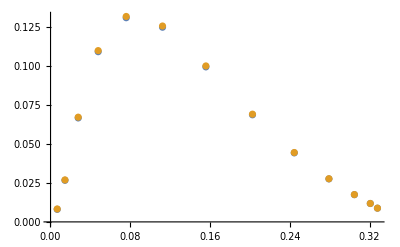

```mathematica
ListPlot[{Table[{CompactnessGRT[[1]][[h]],3/2(MultipoleTensorNoESGR[[1]]/TidalTensorNoESGR[[1]])[[h]](massradGRT[[1]][[1]][[1]][[All,1]][[h]]*km)^-5},{h,1,Length[ρvals]}],Table[{CompactnessGRT[[1]][[h]],3/2 LoveNumGR[[1]][[h]]*(CompactnessGRT[[1]][[h]])^5},{h,1,Length[ρvals]}]},PlotRange->All]
```

```mathematica
(* l=3 *)
```

```mathematica
(* Integrating from Origin to Surface *)
```

```mathematica
H0φpsolOrigintoSurfaceTablel3NoScalarGR=ParallelTable[H0φpsolOrigintoSurfaceNoScalarGR[p,h,3],{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];
(* Uncomment to save into file
AddtoListGR[Unevaluated[{H0φpsolOrigintoSurfaceTablel2NoScalarGR}]];
Export[FileNameJoin[{NotebookDirectory[],"Love_Number_ST_H0φpsolOrigintoSurfaceTablel3GRv2.m"}],ExportListGR];*)
```

```mathematica
H0φpsolOrigintoSurfaceTablel3NoTensorGR=ParallelTable[H0φpsolOrigintoSurfaceNoTensorGR[p,h,3],{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];(* Uncomment to save into file
AddtoListGR[Unevaluated[{H0φpsolOrigintoSurfaceTablel2NoTensorGR}]];
Export[FileNameJoin[{NotebookDirectory[],"Love_Number_ST_H0φpsolOrigintoSurfaceTablel3GRv2.m"}],ExportListGR];*)
```

```mathematica
(* Integrating from "Infinity"=4R to Surface *)
```

```mathematica
rinfS=4;
```

```mathematica
mastereqwithbackOUTGR=mastereqwithbackOUT/.scalarGR/.{mm'[r]->0,mm''[r]->0,mm[r]->M};
```

```mathematica
eqpHGR=eqpH/.scalarGR/.{mm'[r]->0,mm''[r]->0,mm[r]->M};
```

```mathematica
H0φpsolInfinitytoSurfacel3OnlyESGR[p_,h_,ll_]:=NDSolve[{mastereqwithbackOUTGR==0,eqpHGR==0,H0[rinfS*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]==0,H0'[rinfS*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]==0,φp[rinfS*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]==φpOnlyESl3/.q->0/.r->rinfS*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km//Expand,φp'[rinfS*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]==D[φpOnlyESl3,r]/.q->0/.r->rinfS*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km//Expand}/.scalarGR/.{mm'[r]->0,mm''[r]->0,mm[r]->M}/.M->massradGRT[[p]][[1]][[1]][[All,2]][[h]]/.l->ll/.GN->1//Flatten,{φp,H0},{r,rinfS*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km,massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km},PrecisionGoal->15,AccuracyGoal->15,WorkingPrecision->25]//Quiet;
```

```mathematica
H0φpsolInfinitytoSurfacel3OnlyQSGR[p_,h_,ll_]:=NDSolve[{mastereqwithbackOUTGR==0,eqpHGR==0,H0[rinfS*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]==0,H0'[rinfS*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]==0,φp[rinfS*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]==φpOnlyQSl3/.q->0/.r->rinfS*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km//Expand,φp'[rinfS*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]==D[φpOnlyQSl3,r]/.q->0/.r->rinfS*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km//Expand}/.scalarGR/.{mm'[r]->0,mm''[r]->0,mm[r]->M}/.M->massradGRT[[p]][[1]][[1]][[All,2]][[h]]/.l->ll/.GN->1//Flatten,{φp,H0},{r,rinfS*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km,massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km},PrecisionGoal->15,AccuracyGoal->15,WorkingPrecision->25]//Quiet;
```

```mathematica
H0φpsolInfinitytoSurfacel3OnlyETGR[p_,h_,ll_]:=NDSolve[{mastereqwithbackOUTGR==0,eqpHGR==0,φp[rinfS*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]==0,φp'[rinfS*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]==0,H0[rinfS*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]==H0OnlyETl3/.q->0/.r->rinfS*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km//Expand,H0'[rinfS*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]==D[H0OnlyETl3,r]/.q->0/.r->rinfS*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km//Expand}/.scalarGR/.{mm'[r]->0,mm''[r]->0,mm[r]->M}/.M->massradGRT[[p]][[1]][[1]][[All,2]][[h]]/.l->ll/.GN->1//Flatten,{φp,H0},{r,rinfS*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km,massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km},PrecisionGoal->15,AccuracyGoal->15,WorkingPrecision->25]//Quiet;
```

```mathematica
H0φpsolInfinitytoSurfacel3OnlyQTGR[p_,h_,ll_]:=NDSolve[{mastereqwithbackOUTGR==0,eqpHGR==0,φp[rinfS*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]==0,φp'[rinfS*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]==0,H0[rinfS*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]==H0OnlyQTl3/.q->0/.r->rinfS*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km//Expand,H0'[rinfS*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]==D[H0OnlyQTl3,r]/.q->0/.r->rinfS*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km//Expand}/.scalarGR/.{mm'[r]->0,mm''[r]->0,mm[r]->M}/.M->massradGRT[[p]][[1]][[1]][[All,2]][[h]]/.l->ll/.GN->1//Flatten,{φp,H0},{r,rinfS*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km,massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km},PrecisionGoal->15,AccuracyGoal->15,WorkingPrecision->25]//Quiet;
```

```mathematica
(* Computing for every configuration *)
```

```mathematica
H0φpsolInfinitytoSurfacel3OnlyESTableGR=Table[H0φpsolInfinitytoSurfacel3OnlyESGR[p,h,3],{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];
H0φpsolInfinitytoSurfacel3OnlyQSTableGR=Table[H0φpsolInfinitytoSurfacel3OnlyQSGR[p,h,3],{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];
H0φpsolInfinitytoSurfacel3OnlyETTableGR=Table[H0φpsolInfinitytoSurfacel3OnlyETGR[p,h,3],{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];
H0φpsolInfinitytoSurfacel3OnlyQTTableGR=Table[H0φpsolInfinitytoSurfacel3OnlyQTGR[p,h,3],{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];
```

```mathematica
(* Quantities at the surface *)
```

```mathematica
φpINNoTGR=Table[Evaluate[φp[massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]/.H0φpsolOrigintoSurfaceTablel3NoTensorGR[[p]][[h]]]//First,{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];
φpINNoSGR=Table[Evaluate[φp[massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]/.H0φpsolOrigintoSurfaceTablel3NoScalarGR[[p]][[h]]]//First,{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];
φppINNoTGR=Table[Evaluate[φp'[massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]/.H0φpsolOrigintoSurfaceTablel3NoTensorGR[[p]][[h]]]//First,{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];
φppINNoSGR=Table[Evaluate[φp'[massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]/.H0φpsolOrigintoSurfaceTablel3NoScalarGR[[p]][[h]]]//First,{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];
H0INNoTGR=Table[Evaluate[H0[massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]/.H0φpsolOrigintoSurfaceTablel3NoTensorGR[[p]][[h]]]//First,{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];
H0INNoSGR=Table[Evaluate[H0[massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]/.H0φpsolOrigintoSurfaceTablel3NoScalarGR[[p]][[h]]]//First,{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];
H0pINNoTGR=Table[Evaluate[H0'[massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]/.H0φpsolOrigintoSurfaceTablel3NoTensorGR[[p]][[h]]]//First,{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];
H0pINNoSGR=Table[Evaluate[H0'[massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]/.H0φpsolOrigintoSurfaceTablel3NoScalarGR[[p]][[h]]]//First,{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];
```

```mathematica
(* Solutions from the outside integration *)
```

```mathematica
φpOUTESGR=Table[Evaluate[φp[massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel3OnlyESTableGR[[p]][[h]]]//First,{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];
φpOUTQSGR=Table[Evaluate[φp[massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel3OnlyQSTableGR[[p]][[h]]]//First,{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];
φpOUTETGR=Table[Evaluate[φp[massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel3OnlyETTableGR[[p]][[h]]]//First,{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];
φpOUTQTGR=Table[Evaluate[φp[massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel3OnlyQTTableGR[[p]][[h]]]//First,{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];
φppOUTESGR=Table[Evaluate[φp'[massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel3OnlyESTableGR[[p]][[h]]]//First,{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];
φppOUTQSGR=Table[Evaluate[φp'[massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel3OnlyQSTableGR[[p]][[h]]]//First,{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];
φppOUTETGR=Table[Evaluate[φp'[massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel3OnlyETTableGR[[p]][[h]]]//First,{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];
φppOUTQTGR=Table[Evaluate[φp'[massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel3OnlyQTTableGR[[p]][[h]]]//First,{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];
H0OUTESGR=Table[Evaluate[H0[massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel3OnlyESTableGR[[p]][[h]]]//First,{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];
H0OUTQSGR=Table[Evaluate[H0[massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel3OnlyQSTableGR[[p]][[h]]]//First,{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];
H0OUTETGR=Table[Evaluate[H0[massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel3OnlyETTableGR[[p]][[h]]]//First,{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];
H0OUTQTGR=Table[Evaluate[H0[massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel3OnlyQTTableGR[[p]][[h]]]//First,{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];
H0pOUTESGR=Table[Evaluate[H0'[massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel3OnlyESTableGR[[p]][[h]]]//First,{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];
H0pOUTQSGR=Table[Evaluate[H0'[massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel3OnlyQSTableGR[[p]][[h]]]//First,{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];
H0pOUTETGR=Table[Evaluate[H0'[massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel3OnlyETTableGR[[p]][[h]]]//First,{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];
H0pOUTQTGR=Table[Evaluate[H0'[massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel3OnlyQTTableGR[[p]][[h]]]//First,{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];
```

```mathematica
(* Matching *)
```

```mathematica
ConstNoETGR=Table[Solve[{cIN1 φpINNoTGR[[p]][[h]]+cIN2 φpINNoSGR[[p]][[h]] == cOUT1 φpOUTESGR[[p]][[h]]+ cOUT2 φpOUTQSGR[[p]][[h]] + cOUT3 φpOUTETGR[[p]][[h]] +cOUT4 φpOUTQTGR[[p]][[h]],
cIN1 φppINNoTGR[[p]][[h]]+cIN2 φppINNoSGR[[p]][[h]] == cOUT1 φppOUTESGR[[p]][[h]]+ cOUT2 φppOUTQSGR[[p]][[h]] + cOUT3 φppOUTETGR[[p]][[h]] +cOUT4 φppOUTQTGR[[p]][[h]],
cIN1 H0INNoTGR[[p]][[h]]+cIN2 H0INNoSGR[[p]][[h]] == cOUT1 H0OUTESGR[[p]][[h]]+ cOUT2 H0OUTQSGR[[p]][[h]] + cOUT3 H0OUTETGR[[p]][[h]] +cOUT4 H0OUTQTGR[[p]][[h]],cIN1 H0pINNoTGR[[p]][[h]]+cIN2 H0pINNoSGR[[p]][[h]] == cOUT1 H0pOUTESGR[[p]][[h]]+ cOUT2 H0pOUTQSGR[[p]][[h]] + cOUT3 H0pOUTETGR[[p]][[h]] +cOUT4 H0pOUTQTGR[[p]][[h]]}//Simplify,{cIN2,cOUT1,cOUT2,cOUT4}]/.{cIN1->1,cOUT3->0},{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}]//Quiet;
```

```mathematica
ConstNoESGR=Table[Solve[{cIN1 φpINNoTGR[[p]][[h]]+cIN2 φpINNoSGR[[p]][[h]] == cOUT1 φpOUTESGR[[p]][[h]]+ cOUT2 φpOUTQSGR[[p]][[h]] + cOUT3 φpOUTETGR[[p]][[h]] +cOUT4 φpOUTQTGR[[p]][[h]],
cIN1 φppINNoTGR[[p]][[h]]+cIN2 φppINNoSGR[[p]][[h]] == cOUT1 φppOUTESGR[[p]][[h]]+ cOUT2 φppOUTQSGR[[p]][[h]] + cOUT3 φppOUTETGR[[p]][[h]] +cOUT4 φppOUTQTGR[[p]][[h]],
cIN1 H0INNoTGR[[p]][[h]]+cIN2 H0INNoSGR[[p]][[h]] == cOUT1 H0OUTESGR[[p]][[h]]+ cOUT2 H0OUTQSGR[[p]][[h]] + cOUT3 H0OUTETGR[[p]][[h]] +cOUT4 H0OUTQTGR[[p]][[h]],cIN1 H0pINNoTGR[[p]][[h]]+cIN2 H0pINNoSGR[[p]][[h]] == cOUT1 H0pOUTESGR[[p]][[h]]+ cOUT2 H0pOUTQSGR[[p]][[h]] + cOUT3 H0pOUTETGR[[p]][[h]] +cOUT4 H0pOUTQTGR[[p]][[h]]}//Simplify,{cIN1,cOUT3,cOUT2,cOUT4}]/.{cIN2->1,cOUT1->0},{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}]//Quiet;
```

```mathematica
MultipoleScalarNoETGRl3=Table[cOUT2*(3!)/((2*3-1)!!)/.ConstNoETGR[[p]]//Flatten,{p,1,Length[EoSIndex]}]//Quiet;
TidalScalarNoETGRl3=Table[cOUT1*(3!)/.ConstNoETGR[[p]]//Flatten,{p,1,Length[EoSIndex]}]//Quiet;
MultipoleTensorNoETGRl3=Table[1/2 cOUT4*(3!)/((2*3-1)!!)/.ConstNoETGR[[p]]//Flatten,{p,1,Length[EoSIndex]}]//Quiet;
```

```mathematica
MultipoleScalarNoESGRl3=Table[cOUT2*(3!)/((2*3-1)!!)/.ConstNoESGR[[p]]//Flatten,{p,1,Length[EoSIndex]}]//Quiet;
TidalTensorNoESGRl3=Table[cOUT3*1/2(3!)/.ConstNoESGR[[p]]//Flatten,{p,1,Length[EoSIndex]}]//Quiet;
MultipoleTensorNoESGRl3=Table[1/2 cOUT4*(3!)/((2*3-1)!!)/.ConstNoESGR[[p]]//Flatten,{p,1,Length[EoSIndex]}]//Quiet;
```

#### Marginally stable (φ=0) solutions

```mathematica
(* Integrating from Origin to Surface *)
```

```mathematica
(* We use the full solutions and specialize to the case φ=0 through the rule "scalarGR" *)
```

```mathematica
H0φpsolOrigintoSurfaceNoScalarGRWr[p_,β_,h_,ll_]:=NDSolve[SetPrecision[{mastereqwithbackINN[[p]]==0,EoMscalarpertINN[[p]]==0,φp[rmin]==0,φp'[rmin]== 0,H0[rmin]==rmin^ll,H0'[rmin]== ll rmin^(ll-1)}/.A[φ0[r]]->ⅇ^(1/2 βvals[[β]] φ0[r]^2)/.A'[φ0[r]]->D[ⅇ^(1/2 βvals[[β]] φ0[r]^2),φ0[r]]/.α[φ0[r]]->-βvals[[β]]φ0[r]/.α'[φ0[r]]->-βvals[[β]]/.scalarGR/.l->ll/.BackgroundTOVGRPieceT[[p]][[h]],100],{φp,H0},{r,rmin,massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km},PrecisionGoal->15,AccuracyGoal->15,WorkingPrecision->25,Method->{"DiscontinuityProcessing"->False},MaxSteps->100000]//Quiet;
H0φpsolOrigintoSurfaceNoTensorGRWr[p_,β_,h_,ll_]:=NDSolve[SetPrecision[{mastereqwithbackINN[[p]]==0,EoMscalarpertINN[[p]]==0,φp[rmin]==rmin^ll,φp'[rmin]== ll rmin^(ll-1),H0[rmin]==0,H0'[rmin]== 0}/.A[φ0[r]]->ⅇ^(1/2 βvals[[β]] φ0[r]^2)/.A'[φ0[r]]->D[ⅇ^(1/2 βvals[[β]] φ0[r]^2),φ0[r]]/.α[φ0[r]]->-βvals[[β]]φ0[r]/.α'[φ0[r]]->-βvals[[β]]/.scalarGR/.l->ll/.BackgroundTOVGRPieceT[[p]][[h]],100],{φp,H0},{r,rmin,massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km},PrecisionGoal->15,AccuracyGoal->15,WorkingPrecision->25,Method->{"DiscontinuityProcessing"->False},MaxSteps->100000]//Quiet;
```

```mathematica
H0φpsolOrigintoSurfaceTablel2NoScalarGRWrβ1=ParallelTable[H0φpsolOrigintoSurfaceNoScalarGRWr[p,1,h,2],{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];
(* Uncomment to save into file
AddtoList[Unevaluated[{H0φpsolOrigintoSurfaceTablel2NoScalarGRWrβ1}]];
Export[FileNameJoin[{NotebookDirectory[],"Love_Number_ST_H0φpsolOrigintoSurfaceTablel2Wrβ1.m"}],ExportList4];*)
```

```mathematica
H0φpsolOrigintoSurfaceTablel2NoTensorGRWrβ1=ParallelTable[H0φpsolOrigintoSurfaceNoTensorGRWr[p,1,h,2],{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];(* Uncomment to save into file
AddtoList[Unevaluated[{H0φpsolOrigintoSurfaceTablel2NoTensorGRWrβ1}]];
Export[FileNameJoin[{NotebookDirectory[],"Love_Number_ST_H0φpsolOrigintoSurfaceTablel2Wrβ1.m"}],ExportList4];*)
```

```mathematica
H0φpsolOrigintoSurfaceTablel2NoScalarGRWrβ2=ParallelTable[H0φpsolOrigintoSurfaceNoScalarGRWr[p,2,h,2],{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];
(* Uncomment to save into file
AddtoList[Unevaluated[{H0φpsolOrigintoSurfaceTablel2NoScalarGRWrβ2}]];
Export[FileNameJoin[{NotebookDirectory[],"Love_Number_ST_H0φpsolOrigintoSurfaceTablel2Wrβ2.m"}],ExportList8];*)
```

```mathematica
H0φpsolOrigintoSurfaceTablel2NoTensorGRWrβ2=ParallelTable[H0φpsolOrigintoSurfaceNoTensorGRWr[p,2,h,2],{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];(* Uncomment to save into file
AddtoList[Unevaluated[{H0φpsolOrigintoSurfaceTablel2NoTensorGRWrβ2}]];
Export[FileNameJoin[{NotebookDirectory[],"Love_Number_ST_H0φpsolOrigintoSurfaceTablel2Wrβ2.m"}],ExportList8];*)
```

```mathematica
(* Integrating from Infinity to Surface *)
```

```mathematica
rinfS=5;
```

```mathematica
(* Outside the solution is the same as GR *)
```

```mathematica
mastereqwithbackOUTGR=mastereqwithbackOUT/.scalarGR/.{mm'[r]->0,mm''[r]->0,mm[r]->M};
```

```mathematica
eqpHGR=eqpH/.scalarGR/.{mm'[r]->0,mm''[r]->0,mm[r]->M};
```

```mathematica
H0φpsolInfinitytoSurfacel2OnlyESGRWr[p_,h_,ll_]:=NDSolve[{mastereqwithbackOUTGR==0,eqpHGR==0,H0[rinfS*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]==0,H0'[rinfS*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]==0,φp[rinfS*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]==φpOnlyES/.q->0/.r->rinfS*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km//Expand,φp'[rinfS*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]==D[φpOnlyES,r]/.q->0/.r->rinfS*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km//Expand}/.scalarGR/.{mm'[r]->0,mm''[r]->0,mm[r]->M}/.M->massradGRT[[p]][[1]][[1]][[All,2]][[h]]/.l->ll/.GN->1//Flatten,{φp,H0},{r,rinfS*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km,massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km}]//Quiet;
```

```mathematica
H0φpsolInfinitytoSurfacel2OnlyQSGRWr[p_,h_,ll_]:=NDSolve[{mastereqwithbackOUTGR==0,eqpHGR==0,H0[rinfS*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]==0,H0'[rinfS*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]==0,φp[rinfS*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]==φpOnlyQS/.q->0/.r->rinfS*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km//Expand,φp'[rinfS*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]==D[φpOnlyQS,r]/.q->0/.r->rinfS*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km//Expand}/.scalarGR/.{mm'[r]->0,mm''[r]->0,mm[r]->M}/.M->massradGRT[[p]][[1]][[1]][[All,2]][[h]]/.l->ll/.GN->1//Flatten,{φp,H0},{r,rinfS*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km,massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km}]//Quiet;
```

```mathematica
H0φpsolInfinitytoSurfacel2OnlyETGRWr[p_,h_,ll_]:=NDSolve[{mastereqwithbackOUTGR==0,eqpHGR==0,φp[rinfS*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]==0,φp'[rinfS*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]==0,H0[rinfS*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]==H0OnlyET/.q->0/.r->rinfS*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km//Expand,H0'[rinfS*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]==D[H0OnlyET,r]/.q->0/.r->rinfS*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km//Expand}/.scalarGR/.{mm'[r]->0,mm''[r]->0,mm[r]->M}/.M->massradGRT[[p]][[1]][[1]][[All,2]][[h]]/.l->ll/.GN->1//Flatten,{φp,H0},{r,rinfS*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km,massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km}]//Quiet;
```

```mathematica
H0φpsolInfinitytoSurfacel2OnlyQTGRWr[p_,h_,ll_]:=NDSolve[{mastereqwithbackOUTGR==0,eqpHGR==0,φp[rinfS*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]==0,φp'[rinfS*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]==0,H0[rinfS*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]==H0OnlyQT/.q->0/.r->rinfS*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km//Expand,H0'[rinfS*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]==D[H0OnlyQT,r]/.q->0/.r->rinfS*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km//Expand}/.scalarGR/.{mm'[r]->0,mm''[r]->0,mm[r]->M}/.M->massradGRT[[p]][[1]][[1]][[All,2]][[h]]/.l->ll/.GN->1//Flatten,{φp,H0},{r,rinfS*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km,massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km}]//Quiet;
```

```mathematica
(* Computing for every configuration for l=2 *)
```

```mathematica
H0φpsolOrigintoSurfaceTablel2NoTensorGRWr={H0φpsolOrigintoSurfaceTablel2NoTensorGRWrβ1,H0φpsolOrigintoSurfaceTablel2NoTensorGRWrβ2};
H0φpsolOrigintoSurfaceTablel2NoScalarGRWr={H0φpsolOrigintoSurfaceTablel2NoScalarGRWrβ1,H0φpsolOrigintoSurfaceTablel2NoScalarGRWrβ2};
```

```mathematica
H0φpsolInfinitytoSurfacel2OnlyESTableGRWr=Table[H0φpsolInfinitytoSurfacel2OnlyESGRWr[p,h,2],{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];
H0φpsolInfinitytoSurfacel2OnlyQSTableGRWr=Table[H0φpsolInfinitytoSurfacel2OnlyQSGRWr[p,h,2],{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];
H0φpsolInfinitytoSurfacel2OnlyETTableGRWr=Table[H0φpsolInfinitytoSurfacel2OnlyETGRWr[p,h,2],{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];
H0φpsolInfinitytoSurfacel2OnlyQTTableGRWr=Table[H0φpsolInfinitytoSurfacel2OnlyQTGRWr[p,h,2],{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];
```

```mathematica
(* Quantities at the surface *)
```

```mathematica
φpINNoTGRWr=Table[Evaluate[φp[massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]/.H0φpsolOrigintoSurfaceTablel2NoTensorGRWr[[β]][[p]][[h]]]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{h,1,Length[ρvals]}];
φpINNoSGRWr=Table[Evaluate[φp[massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]/.H0φpsolOrigintoSurfaceTablel2NoScalarGRWr[[β]][[p]][[h]]]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{h,1,Length[ρvals]}];
φppINNoTGRWr=Table[Evaluate[φp'[massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]/.H0φpsolOrigintoSurfaceTablel2NoTensorGRWr[[β]][[p]][[h]]]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{h,1,Length[ρvals]}];
φppINNoSGRWr=Table[Evaluate[φp'[massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]/.H0φpsolOrigintoSurfaceTablel2NoScalarGRWr[[β]][[p]][[h]]]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{h,1,Length[ρvals]}];
H0INNoTGRWr=Table[Evaluate[H0[massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]/.H0φpsolOrigintoSurfaceTablel2NoTensorGRWr[[β]][[p]][[h]]]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{h,1,Length[ρvals]}];
H0INNoSGRWr=Table[Evaluate[H0[massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]/.H0φpsolOrigintoSurfaceTablel2NoScalarGRWr[[β]][[p]][[h]]]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{h,1,Length[ρvals]}];
H0pINNoTGRWr=Table[Evaluate[H0'[massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]/.H0φpsolOrigintoSurfaceTablel2NoTensorGRWr[[β]][[p]][[h]]]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{h,1,Length[ρvals]}];
H0pINNoSGRWr=Table[Evaluate[H0'[massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]/.H0φpsolOrigintoSurfaceTablel2NoScalarGRWr[[β]][[p]][[h]]]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{h,1,Length[ρvals]}];
```

```mathematica
(* Solutions from the outside integration *)
```

```mathematica
φpOUTESGRWr=Table[Evaluate[φp[massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyESTableGRWr[[p]][[h]]]//First,{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];
φpOUTQSGRWr=Table[Evaluate[φp[massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyQSTableGRWr[[p]][[h]]]//First,{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];
φpOUTETGRWr=Table[Evaluate[φp[massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyETTableGRWr[[p]][[h]]]//First,{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];
φpOUTQTGRWr=Table[Evaluate[φp[massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyQTTableGRWr[[p]][[h]]]//First,{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];
φppOUTESGRWr=Table[Evaluate[φp'[massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyESTableGRWr[[p]][[h]]]//First,{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];
φppOUTQSGRWr=Table[Evaluate[φp'[massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyQSTableGRWr[[p]][[h]]]//First,{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];
φppOUTETGRWr=Table[Evaluate[φp'[massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyETTableGRWr[[p]][[h]]]//First,{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];
φppOUTQTGRWr=Table[Evaluate[φp'[massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyQTTableGRWr[[p]][[h]]]//First,{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];
H0OUTESGRWr=Table[Evaluate[H0[massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyESTableGRWr[[p]][[h]]]//First,{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];
H0OUTQSGRWr=Table[Evaluate[H0[massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyQSTableGRWr[[p]][[h]]]//First,{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];
H0OUTETGRWr=Table[Evaluate[H0[massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyETTableGRWr[[p]][[h]]]//First,{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];
H0OUTQTGRWr=Table[Evaluate[H0[massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyQTTableGRWr[[p]][[h]]]//First,{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];
H0pOUTESGRWr=Table[Evaluate[H0'[massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyESTableGRWr[[p]][[h]]]//First,{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];
H0pOUTQSGRWr=Table[Evaluate[H0'[massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyQSTableGRWr[[p]][[h]]]//First,{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];
H0pOUTETGRWr=Table[Evaluate[H0'[massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyETTableGRWr[[p]][[h]]]//First,{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];
H0pOUTQTGRWr=Table[Evaluate[H0'[massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyQTTableGRWr[[p]][[h]]]//First,{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];
```

```mathematica
(* Matching *)
```

```mathematica
ConstNoETGRWr=Table[Solve[{cIN1 φpINNoTGRWr[[p]][[β]][[h]]+cIN2 φpINNoSGRWr[[p]][[β]][[h]] == cOUT1 φpOUTESGRWr[[p]][[h]]+ cOUT2 φpOUTQSGRWr[[p]][[h]] + cOUT3 φpOUTETGRWr[[p]][[h]] +cOUT4 φpOUTQTGRWr[[p]][[h]],
cIN1 φppINNoTGRWr[[p]][[β]][[h]]+cIN2 φppINNoSGRWr[[p]][[β]][[h]] == cOUT1 φppOUTESGRWr[[p]][[h]]+ cOUT2 φppOUTQSGRWr[[p]][[h]] + cOUT3 φppOUTETGRWr[[p]][[h]] +cOUT4 φppOUTQTGRWr[[p]][[h]],
cIN1 H0INNoTGRWr[[p]][[β]][[h]]+cIN2 H0INNoSGRWr[[p]][[β]][[h]] == cOUT1 H0OUTESGRWr[[p]][[h]]+ cOUT2 H0OUTQSGRWr[[p]][[h]] + cOUT3 H0OUTETGRWr[[p]][[h]] +cOUT4 H0OUTQTGRWr[[p]][[h]],cIN1 H0pINNoTGRWr[[p]][[β]][[h]]+cIN2 H0pINNoSGRWr[[p]][[β]][[h]] == cOUT1 H0pOUTESGRWr[[p]][[h]]+ cOUT2 H0pOUTQSGRWr[[p]][[h]] + cOUT3 H0pOUTETGRWr[[p]][[h]] +cOUT4 H0pOUTQTGRWr[[p]][[h]]}//Simplify,{cIN2,cOUT1,cOUT2,cOUT4}]/.{cIN1->1,cOUT3->0},{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{h,1,Length[ρvals]}]//Quiet;
```

```mathematica
ConstNoESGRWr=Table[Solve[{cIN1 φpINNoTGRWr[[p]][[β]][[h]]+cIN2 φpINNoSGRWr[[p]][[β]][[h]] == cOUT1 φpOUTESGRWr[[p]][[h]]+ cOUT2 φpOUTQSGRWr[[p]][[h]] + cOUT3 φpOUTETGRWr[[p]][[h]] +cOUT4 φpOUTQTGRWr[[p]][[h]],
cIN1 φppINNoTGRWr[[p]][[β]][[h]]+cIN2 φppINNoSGRWr[[p]][[β]][[h]] == cOUT1 φppOUTESGRWr[[p]][[h]]+ cOUT2 φppOUTQSGRWr[[p]][[h]] + cOUT3 φppOUTETGRWr[[p]][[h]] +cOUT4 φppOUTQTGRWr[[p]][[h]],
cIN1 H0INNoTGRWr[[p]][[β]][[h]]+cIN2 H0INNoSGRWr[[p]][[β]][[h]] == cOUT1 H0OUTESGRWr[[p]][[h]]+ cOUT2 H0OUTQSGRWr[[p]][[h]] + cOUT3 H0OUTETGRWr[[p]][[h]] +cOUT4 H0OUTQTGRWr[[p]][[h]],cIN1 H0pINNoTGRWr[[p]][[β]][[h]]+cIN2 H0pINNoSGRWr[[p]][[β]][[h]] == cOUT1 H0pOUTESGRWr[[p]][[h]]+ cOUT2 H0pOUTQSGRWr[[p]][[h]] + cOUT3 H0pOUTETGRWr[[p]][[h]] +cOUT4 H0pOUTQTGRWr[[p]][[h]]}//Simplify,{cIN1,cOUT3,cOUT2,cOUT4}]/.{cIN2->1,cOUT1->0},{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{h,1,Length[ρvals]}]//Quiet;
```

```mathematica
MultipoleScalarNoETGRWr=Table[cOUT2*(2!)/((2*2-1)!!)/.ConstNoETGRWr[[p]][[β]]//Flatten,{p,1,Length[EoSIndex]},{β,1,Length[βvals]}]//Quiet;
TidalScalarNoETGRWr=Table[cOUT1*(2!)/.ConstNoETGRWr[[p]][[β]]//Flatten,{p,1,Length[EoSIndex]},{β,1,Length[βvals]}]//Quiet;
MultipoleTensorNoETGRWr=Table[1/2 cOUT4*(2!)/((2*2-1)!!)/.ConstNoETGRWr[[p]][[β]]//Flatten,{p,1,Length[EoSIndex]},{β,1,Length[βvals]}]//Quiet;
```

```mathematica
MultipoleScalarNoESGRWr=Table[cOUT2*(2!)/((2*2-1)!!)/.ConstNoESGRWr[[p]][[β]]//Flatten,{p,1,Length[EoSIndex]},{β,1,Length[βvals]}]//Quiet;
TidalTensorNoESGRWr=Table[cOUT3*1/2(2!)/.ConstNoESGRWr[[p]][[β]]//Flatten,{p,1,Length[EoSIndex]},{β,1,Length[βvals]}]//Quiet;
MultipoleTensorNoESGRWr=Table[1/2 cOUT4*(2!)/((2*2-1)!!)/.ConstNoESGRWr[[p]][[β]]//Flatten,{p,1,Length[EoSIndex]},{β,1,Length[βvals]}]//Quiet;
```

```mathematica
LoveNumGRWr=Table[16/15(1-2CC)^2(2+2CC(y-1)-y)*(2CC(6-3y+3CC(5y-8))+4 CC^3(13-11y+CC(3y-2)+2 CC^2(y+1))+3(1-2CC)^2(2-y+2CC(y-1))Log[1-2CC])^-1/.CC->CompactnessGRT[[p]][[h]]/.y->((H0pINNoSGRWr[[p]][[β]][[h]])/(H0INNoSGRWr[[p]][[β]][[h]]))*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{h,1,Length[ρvals]}]//Quiet;
```

```mathematica
LoveNumGRScalarWr=Table[-((8 (-1+2 CC) (3 (-2+y)+2 CC (3+(-3+CC) y)))/(135 (4 CC (3+(-6+CC) CC)-6 (-1+CC) CC (-1+2 CC) y+(-1+2 CC) (3 (-2+y)+2 CC (3+(-3+CC) y)) Log[1-2 CC])))/.CC->CompactnessGRT[[p]][[h]]/.y->((φppINNoTGRWr[[p]][[β]][[h]])/(φpINNoTGRWr[[p]][[β]][[h]]))*massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{h,1,Length[ρvals]}]//Quiet;
```

```mathematica
(* Plots *)
```

```mathematica
(* Tensor Love number coincides with analytical expression *)
```

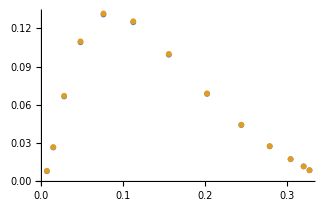

```mathematica
ListPlot[{Table[{CompactnessGRT[[1]][[h]],3/2(MultipoleTensorNoESGRWr[[1]][[1]]/TidalTensorNoESGRWr[[1]][[1]])[[h]](massradGRT[[1]][[1]][[1]][[All,1]][[h]]*km)^-5},{h,1,Length[ρvals]}],Table[{CompactnessGRT[[1]][[h]],3/2 LoveNumGRWr[[1]][[1]][[h]]*(CompactnessGRT[[1]][[h]])^5},{h,1,Length[ρvals]}]},PlotRange->All]
```

```mathematica
(* Scalar Love number coincides with analytical expression *)
```

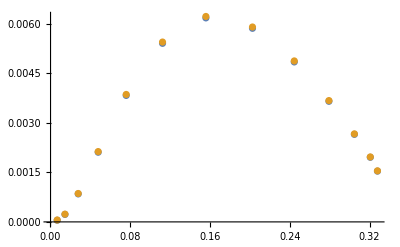

```mathematica
ListPlot[{Table[{CompactnessGRT[[1]][[h]],3/2(MultipoleScalarNoETGRWr[[1]][[1]]/TidalScalarNoETGRWr[[1]][[1]])[[h]](massradGRT[[1]][[1]][[1]][[All,1]][[h]]*km)^-5},{h,1,Length[ρvals]}],Table[{CompactnessGRT[[1]][[h]],-3/2*LoveNumGRScalarWr[[1]][[1]][[h]](massradGRT[[1]][[1]][[1]][[All,2]][[h]])^5/(massradGRT[[1]][[1]][[1]][[All,1]][[h]]*km)^5},{h,1,Length[ρvals]}]},PlotRange->All]
```

#### Combining the particular solutions to match at the surface

```mathematica
(* l=1 *)
```

```mathematica
(* Integration from "Infinity"=7R to Surface *)
```

```mathematica
rinfS=7;
```

```mathematica
H0φpsolInfinitytoSurfacel1OnlyES[p_,β_,φinf_,h_]:=NDSolve[SetPrecision[{mastereqH0F0OUT==0, eqpH==0,H0[rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]==H0OnlyESl1/.r->rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km(*,H0'[rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]==D[H0OnlyESl1,r]/.r->rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km*),φp[rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]==φpOnlyESl1/.r->rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km,φp'[rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]==D[φpOnlyESl1,r]/.r->rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km}/.φ0solOUTSolsT[[p]][[β]][[φinf]][[h]] /.q->ChargeTableT[[p]][[β]][[φinf]][[All,2]][[h]]/.M->ADMMassTableT[[p]][[β]][[φinf]][[h]]/.l->1/.GN->1//Flatten,50],{φp,H0},{r,rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km,massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km}(*,PrecisionGoal->4,AccuracyGoal->4,WorkingPrecision->9,PrecisionGoal->9,AccuracyGoal->9,WorkingPrecision->15*)]//Quiet;
```

```mathematica
H0φpsolInfinitytoSurfacel1OnlyQS[p_,β_,φinf_,h_]:=NDSolve[SetPrecision[{mastereqH0F0OUT==0,eqpH==0,H0[rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]==H0OnlyQSl1/.r->rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km(*,H0'[rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]==D[H0OnlyQSl1,r]/.r->rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km*),φp[rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]==φpOnlyQSl1/.r->rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km,φp'[rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]==D[φpOnlyQSl1,r]/.r->rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km} /.q->ChargeTableT[[p]][[β]][[φinf]][[All,2]][[h]]/.M->ADMMassTableT[[p]][[β]][[φinf]][[h]]/.φ0solOUTSolsT[[p]][[β]][[φinf]][[h]]/.l->1/.GN->1//Flatten,50],{φp,H0},{r, rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km,massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km}(*,PrecisionGoal->4,AccuracyGoal->4,WorkingPrecision->9,PrecisionGoal->9,AccuracyGoal->9,WorkingPrecision->15*)]//Quiet;
```

```mathematica
H0φpsolInfinitytoSurfacel1OnlyET[p_,β_,φinf_,h_]:=NDSolve[SetPrecision[{mastereqH0F0OUT==0, eqpH==0,φp[rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]==φpOnlyETl1/.r->rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km,φp'[rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]==D[φpOnlyETl1,r]/.r->rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km(*,H0[rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]==H0OnlyETl1/.r->rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km*),H0'[rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]==D[H0OnlyETl1,r]/.r->rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km} /.q->ChargeTableT[[p]][[β]][[φinf]][[All,2]][[h]]/.M->ADMMassTableT[[p]][[β]][[φinf]][[h]]/.φ0solOUTSolsT[[p]][[β]][[φinf]][[h]]/.l->1/.GN->1//Flatten,50],{φp,H0},{r, rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km,massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km}(*,PrecisionGoal->4,AccuracyGoal->4,WorkingPrecision->9,PrecisionGoal->9,AccuracyGoal->9,WorkingPrecision->15*)]//Quiet;
```

```mathematica
H0φpsolInfinitytoSurfacel1OnlyQT[p_,β_,φinf_,h_]:=NDSolve[SetPrecision[{mastereqH0F0OUT==0, eqpH==0,H0[rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]==H0OnlyQTl1/.r->rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km(*,H0'[rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]==D[H0OnlyQTl1,r]/.r->rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km*),φp[rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]==φpOnlyQTl1/.r->rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km,φp'[rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]==D[φpOnlyQTl1,r]/.r->rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km}/.q->ChargeTableT[[p]][[β]][[φinf]][[All,2]][[h]]/.M->ADMMassTableT[[p]][[β]][[φinf]][[h]]/.φ0solOUTSolsT[[p]][[β]][[φinf]][[h]]/.l->1/.GN->1//Flatten,50],{φp,H0},{r, rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km,massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km}(*,PrecisionGoal->4,AccuracyGoal->4,WorkingPrecision->9,PrecisionGoal->9,AccuracyGoal->9,WorkingPrecision->15*)]//Quiet;
```

```mathematica
(* Computing for every configuration *)
```

```mathematica
H0φpsolInfinitytoSurfacel1OnlyESTable=Table[H0φpsolInfinitytoSurfacel1OnlyES[p,β,φinf,h],{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,1(*Length[φinfvals]*)},{h,1,Length[ρvals]}];
H0φpsolInfinitytoSurfacel1OnlyQSTable=Table[H0φpsolInfinitytoSurfacel1OnlyQS[p,β,φinf,h],{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,1(*Length[φinfvals]*)},{h,1,Length[ρvals]}];
H0φpsolInfinitytoSurfacel1OnlyETTable=Table[H0φpsolInfinitytoSurfacel1OnlyET[p,β,φinf,h],{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,1(*Length[φinfvals]*)},{h,1,Length[ρvals]}];
H0φpsolInfinitytoSurfacel1OnlyQTTable=Table[H0φpsolInfinitytoSurfacel1OnlyQT[p,β,φinf,h],{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,1(*Length[φinfvals]*)},{h,1,Length[ρvals]}];
```

```mathematica
(* Solutions from the inside integration *)
```

```mathematica
H0φpsolOrigintoSurfaceTablel1NoTensor={H0φpsolOrigintoSurfaceTablel1NoTensorφ1};
H0φpsolOrigintoSurfaceTablel1NoScalar={H0φpsolOrigintoSurfaceTablel1NoScalarφ1};
```

```mathematica
φpINNoTl1=Table[Evaluate[φp[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolOrigintoSurfaceTablel1NoTensor[[φinf]][[p]][[β]][[h]]],{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
φpINNoSl1=Table[Evaluate[φp[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolOrigintoSurfaceTablel1NoScalar[[φinf]][[p]][[β]][[h]]],{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
φppINNoTl1=Table[Evaluate[φp'[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolOrigintoSurfaceTablel1NoTensor[[φinf]][[p]][[β]][[h]]],{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
φppINNoSl1=Table[Evaluate[φp'[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolOrigintoSurfaceTablel1NoScalar[[φinf]][[p]][[β]][[h]]],{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
H0INNoTl1=Table[Evaluate[H0[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolOrigintoSurfaceTablel1NoTensor[[φinf]][[p]][[β]][[h]]],{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
H0INNoSl1=Table[Evaluate[H0[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolOrigintoSurfaceTablel1NoScalar[[φinf]][[p]][[β]][[h]]],{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
H0pINNoTl1=Table[Evaluate[H0'[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolOrigintoSurfaceTablel1NoTensor[[φinf]][[p]][[β]][[h]]],{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
H0pINNoSl1=Table[Evaluate[H0'[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolOrigintoSurfaceTablel1NoScalar[[φinf]][[p]][[β]][[h]]],{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
```

```mathematica
(* Solutions from the outside integration *)
```

```mathematica
φpOUTESl1=Table[Evaluate[φp[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel1OnlyESTable[[p]][[β]][[φinf]][[h]]]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
φpOUTQSl1=Table[Evaluate[φp[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel1OnlyQSTable[[p]][[β]][[φinf]][[h]]]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
φpOUTETl1=Table[Evaluate[φp[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel1OnlyETTable[[p]][[β]][[φinf]][[h]]]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
φpOUTQTl1=Table[Evaluate[φp[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel1OnlyQTTable[[p]][[β]][[φinf]][[h]]]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
φppOUTESl1=Table[Evaluate[φp'[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel1OnlyESTable[[p]][[β]][[φinf]][[h]]]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
φppOUTQSl1=Table[Evaluate[φp'[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel1OnlyQSTable[[p]][[β]][[φinf]][[h]]]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
φppOUTETl1=Table[Evaluate[φp'[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel1OnlyETTable[[p]][[β]][[φinf]][[h]]]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
φppOUTQTl1=Table[Evaluate[φp'[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel1OnlyQTTable[[p]][[β]][[φinf]][[h]]]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
H0OUTESl1=Table[Evaluate[H0[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel1OnlyESTable[[p]][[β]][[φinf]][[h]]]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
H0OUTQSl1=Table[Evaluate[H0[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel1OnlyQSTable[[p]][[β]][[φinf]][[h]]]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
H0OUTETl1=Table[Evaluate[H0[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel1OnlyETTable[[p]][[β]][[φinf]][[h]]]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
H0OUTQTl1=Table[Evaluate[H0[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel1OnlyQTTable[[p]][[β]][[φinf]][[h]]]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
H0pOUTESl1=Table[Evaluate[H0'[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel1OnlyESTable[[p]][[β]][[φinf]][[h]]]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
H0pOUTQSl1=Table[Evaluate[H0'[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel1OnlyQSTable[[p]][[β]][[φinf]][[h]]]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
H0pOUTETl1=Table[Evaluate[H0'[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel1OnlyETTable[[p]][[β]][[φinf]][[h]]]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
H0pOUTQTl1=Table[Evaluate[H0'[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel1OnlyQTTable[[p]][[β]][[φinf]][[h]]]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
```

```mathematica
(* Uncomment to save into file
AddtoList[Unevaluated[{φpOUTESl1,φpOUTQSl1,φpOUTETl1,φpOUTQTl1,φppOUTESl1,φppOUTQSl1,φppOUTETl1,φppOUTQTl1,H0OUTESl1,H0OUTQSl1,H0OUTETl1,H0OUTQTl1,H0pOUTESl1,H0pOUTQSl1,H0pOUTETl1,H0pOUTQTl1,φpINNoTl1,φpINNoSl1,φppINNoTl1,φppINNoSl1,H0INNoTl1,H0INNoSl1,H0pINNoTl1,H0pINNoSl1}]];
Export[FileNameJoin[{NotebookDirectory[],"Love_Number_l1_H0_φp.m"}],ExportList5];*)
```

```mathematica
(* Matching *)
```

```mathematica
ConstNoETl1=Table[NSolve[{cIN1 φpINNoTl1[[p]][[β]][[φinf]][[h]]+cIN2 φpINNoSl1[[p]][[β]][[φinf]][[h]] == cOUT1 φpOUTESl1[[p]][[β]][[φinf]][[h]]+ cOUT2 φpOUTQSl1[[p]][[β]][[φinf]][[h]] + cOUT3 φpOUTETl1[[p]][[β]][[φinf]][[h]] +cOUT4 φpOUTQTl1[[p]][[β]][[φinf]][[h]],
cIN1 φppINNoTl1[[p]][[β]][[φinf]][[h]]+cIN2 φppINNoSl1[[p]][[β]][[φinf]][[h]] == cOUT1 φppOUTESl1[[p]][[β]][[φinf]][[h]]+ cOUT2 φppOUTQSl1[[p]][[β]][[φinf]][[h]] + cOUT3 φppOUTETl1[[p]][[β]][[φinf]][[h]] +cOUT4 φppOUTQTl1[[p]][[β]][[φinf]][[h]],
cIN1 H0INNoTl1[[p]][[β]][[φinf]][[h]]+cIN2 H0INNoSl1[[p]][[β]][[φinf]][[h]] == cOUT1 H0OUTESl1[[p]][[β]][[φinf]][[h]]+ cOUT2 H0OUTQSl1[[p]][[β]][[φinf]][[h]] + cOUT3 H0OUTETl1[[p]][[β]][[φinf]][[h]] +cOUT4 H0OUTQTl1[[p]][[β]][[φinf]][[h]],cIN1 H0pINNoTl1[[p]][[β]][[φinf]][[h]]+cIN2 H0pINNoSl1[[p]][[β]][[φinf]][[h]] == cOUT1 H0pOUTESl1[[p]][[β]][[φinf]][[h]]+ cOUT2 H0pOUTQSl1[[p]][[β]][[φinf]][[h]] + cOUT3 H0pOUTETl1[[p]][[β]][[φinf]][[h]] +cOUT4 H0pOUTQTl1[[p]][[β]][[φinf]][[h]]},{cIN1,cOUT1,cOUT2,cOUT4}]/.cIN2->1/.cOUT3->0,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}]//Quiet;
```

```mathematica
ConstNoESl1=Table[Solve[{cIN1 φpINNoTl1[[p]][[β]][[φinf]][[h]]+cIN2 φpINNoSl1[[p]][[β]][[φinf]][[h]] == cOUT1 φpOUTESl1[[p]][[β]][[φinf]][[h]]+ cOUT2 φpOUTQSl1[[p]][[β]][[φinf]][[h]] + cOUT3 φpOUTETl1[[p]][[β]][[φinf]][[h]] +cOUT4 φpOUTQTl1[[p]][[β]][[φinf]][[h]],
cIN1 φppINNoTl1[[p]][[β]][[φinf]][[h]]+cIN2 φppINNoSl1[[p]][[β]][[φinf]][[h]] == cOUT1 φppOUTESl1[[p]][[β]][[φinf]][[h]]+ cOUT2 φppOUTQSl1[[p]][[β]][[φinf]][[h]] + cOUT3 φppOUTETl1[[p]][[β]][[φinf]][[h]] +cOUT4 φppOUTQTl1[[p]][[β]][[φinf]][[h]],
cIN1 H0INNoTl1[[p]][[β]][[φinf]][[h]]+cIN2 H0INNoSl1[[p]][[β]][[φinf]][[h]] == cOUT1 H0OUTESl1[[p]][[β]][[φinf]][[h]]+ cOUT2 H0OUTQSl1[[p]][[β]][[φinf]][[h]] + cOUT3 H0OUTETl1[[p]][[β]][[φinf]][[h]] +cOUT4 H0OUTQTl1[[p]][[β]][[φinf]][[h]],cIN1 H0pINNoTl1[[p]][[β]][[φinf]][[h]]+cIN2 H0pINNoSl1[[p]][[β]][[φinf]][[h]] == cOUT1 H0pOUTESl1[[p]][[β]][[φinf]][[h]]+ cOUT2 H0pOUTQSl1[[p]][[β]][[φinf]][[h]] + cOUT3 H0pOUTETl1[[p]][[β]][[φinf]][[h]] +cOUT4 H0pOUTQTl1[[p]][[β]][[φinf]][[h]]},{cIN1,cOUT4,cOUT2,cOUT4}]/.cIN2->1,{p,1,1(*Length[EoSIndex]*)},{β,1(*,Length[βvals]*)},{φinf,1,1(*Length[φinfvals]*)},{h,1,Length[ρvals]}]//Quiet;
```

```mathematica
MultipoleScalarNoETl1=Table[cOUT2/.ConstNoETl1[[p]][[β]][[φinf]]//Flatten,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]}]//Quiet;
TidalScalarNoETl1=Table[cOUT1/.ConstNoETl1[[p]][[β]][[φinf]]//Flatten,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]}]//Quiet;
MultipoleTensorNoETl1=Table[cOUT4*1/2/.ConstNoETl1[[p]][[β]][[φinf]]//Flatten,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]}]//Quiet;
MultipoleScalarNoESl1=Table[cOUT2/.ConstNoESl1[[p]][[β]][[φinf]]//Flatten,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]}]//Quiet;
TidalTensorNoESl1=Table[cOUT3*1/2/.ConstNoESl1[[p]][[β]][[φinf]]//Flatten,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]}]//Quiet;
MultipoleTensorNoESl1=Table[cOUT4*1/2/.ConstNoESl1[[p]][[β]][[φinf]]//Flatten,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]}]//Quiet;
```

```mathematica
(* l=2 *)
```

```mathematica
(* Integration from "Infinity"=7R to Surface *)
```

```mathematica
rinfS=7;
```

```mathematica
H0φpsolInfinitytoSurfacel2OnlyES[p_,β_,φinf_,h_]:=NDSolve[{r^2 mastereqwithbackOUT==0, eqpH==0,H0[rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]==H0OnlyES/.r->rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km,H0'[rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]==D[H0OnlyES,r]/.r->rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km,φp[rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]==φpOnlyES/.r->rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km,φp'[rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]==D[φpOnlyES,r]/.r->rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km}/.φ0solOUTSolsT[[p]][[β]][[φinf]][[h]] /.q->ChargeTableT[[p]][[β]][[φinf]][[All,2]][[h]]/.M->ADMMassTableT[[p]][[β]][[φinf]][[h]]/.l->2/.GN->1//Flatten//N,{φp,H0},{r,rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km,massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km},PrecisionGoal->15,AccuracyGoal->15,WorkingPrecision->25]//Quiet;
```

```mathematica
H0φpsolInfinitytoSurfacel2OnlyQS[p_,β_,φinf_,h_]:=NDSolve[{r^2 mastereqwithbackOUT==0,eqpH==0,H0[rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]==H0OnlyQS/.r->rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km,H0'[rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]==D[H0OnlyQS,r]/.r->rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km,φp[rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]==φpOnlyQS/.r->rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km,φp'[rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]==D[φpOnlyQS,r]/.r->rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km} /.q->ChargeTableT[[p]][[β]][[φinf]][[All,2]][[h]]/.M->ADMMassTableT[[p]][[β]][[φinf]][[h]]/.φ0solOUTSolsT[[p]][[β]][[φinf]][[h]]/.l->2/.GN->1//Flatten//N,{φp,H0},{r, rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km,massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km},PrecisionGoal->15,AccuracyGoal->15,WorkingPrecision->25]//Quiet;
```

```mathematica
H0φpsolInfinitytoSurfacel2OnlyET[p_,β_,φinf_,h_]:=NDSolve[{r^2 mastereqwithbackOUT==0, eqpH==0,φp[rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]==φpOnlyET/.r->rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km,φp'[rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]==D[φpOnlyET,r]/.r->rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km,H0[rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]==H0OnlyET/.r->rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km,H0'[rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]==D[H0OnlyET,r]/.r->rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km} /.q->ChargeTableT[[p]][[β]][[φinf]][[All,2]][[h]]/.M->ADMMassTableT[[p]][[β]][[φinf]][[h]]/.φ0solOUTSolsT[[p]][[β]][[φinf]][[h]]/.l->2/.GN->1//Flatten//N,{φp,H0},{r, rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km,massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km},PrecisionGoal->15,AccuracyGoal->15,WorkingPrecision->25]//Quiet;
```

```mathematica
H0φpsolInfinitytoSurfacel2OnlyQT[p_,β_,φinf_,h_]:=NDSolve[{r^2 mastereqwithbackOUT==0, eqpH==0,H0[rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]==H0OnlyQT/.r->rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km,H0'[rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]==D[H0OnlyQT,r]/.r->rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km,φp[rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]==φpOnlyQT/.r->rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km,φp'[rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]==D[φpOnlyQT,r]/.r->rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km}/.q->ChargeTableT[[p]][[β]][[φinf]][[All,2]][[h]]/.M->ADMMassTableT[[p]][[β]][[φinf]][[h]]/.φ0solOUTSolsT[[p]][[β]][[φinf]][[h]]/.l->2/.GN->1//Flatten//N,{φp,H0},{r, rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km,massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km},PrecisionGoal->15,AccuracyGoal->15,WorkingPrecision->25]//Quiet;
```

```mathematica
(* Computing for every configuration *)
```

```mathematica
H0φpsolInfinitytoSurfacel2OnlyESTable=Table[H0φpsolInfinitytoSurfacel2OnlyES[p,β,φinf,h],{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
H0φpsolInfinitytoSurfacel2OnlyQSTable=Table[H0φpsolInfinitytoSurfacel2OnlyQS[p,β,φinf,h],{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
H0φpsolInfinitytoSurfacel2OnlyETTable=Table[H0φpsolInfinitytoSurfacel2OnlyET[p,β,φinf,h],{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
H0φpsolInfinitytoSurfacel2OnlyQTTable=Table[H0φpsolInfinitytoSurfacel2OnlyQT[p,β,φinf,h],{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
```

```mathematica
(* Solutions from the inside integration *)
```

```mathematica
H0φpsolOrigintoSurfaceTablel2NoTensor={H0φpsolOrigintoSurfaceTablel2NoTensorφ1,H0φpsolOrigintoSurfaceTablel2NoTensorφ2,H0φpsolOrigintoSurfaceTablel2NoTensorφ3};
H0φpsolOrigintoSurfaceTablel2NoScalar={H0φpsolOrigintoSurfaceTablel2NoScalarφ1,H0φpsolOrigintoSurfaceTablel2NoScalarφ2,H0φpsolOrigintoSurfaceTablel2NoScalarφ3};
```

```mathematica
φpINNoT=Table[Evaluate[φp[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolOrigintoSurfaceTablel2NoTensor[[φinf]][[p]][[β]][[h]]],{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
φpINNoS=Table[Evaluate[φp[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolOrigintoSurfaceTablel2NoScalar[[φinf]][[p]][[β]][[h]]],{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
φppINNoT=Table[Evaluate[φp'[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolOrigintoSurfaceTablel2NoTensor[[φinf]][[p]][[β]][[h]]],{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
φppINNoS=Table[Evaluate[φp'[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolOrigintoSurfaceTablel2NoScalar[[φinf]][[p]][[β]][[h]]],{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
H0INNoT=Table[Evaluate[H0[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolOrigintoSurfaceTablel2NoTensor[[φinf]][[p]][[β]][[h]]],{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
H0INNoS=Table[Evaluate[H0[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolOrigintoSurfaceTablel2NoScalar[[φinf]][[p]][[β]][[h]]],{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
H0pINNoT=Table[Evaluate[H0'[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolOrigintoSurfaceTablel2NoTensor[[φinf]][[p]][[β]][[h]]],{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
H0pINNoS=Table[Evaluate[H0'[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolOrigintoSurfaceTablel2NoScalar[[φinf]][[p]][[β]][[h]]],{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
```

```mathematica
(* Solutions from the outside integration *)
```

```mathematica
φpOUTES=Table[Evaluate[φp[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyESTable[[p]][[β]][[φinf]][[h]]]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
φpOUTQS=Table[Evaluate[φp[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyQSTable[[p]][[β]][[φinf]][[h]]]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
φpOUTET=Table[Evaluate[φp[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyETTable[[p]][[β]][[φinf]][[h]]]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
φpOUTQT=Table[Evaluate[φp[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyQTTable[[p]][[β]][[φinf]][[h]]]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
φppOUTES=Table[Evaluate[φp'[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyESTable[[p]][[β]][[φinf]][[h]]]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
φppOUTQS=Table[Evaluate[φp'[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyQSTable[[p]][[β]][[φinf]][[h]]]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
φppOUTET=Table[Evaluate[φp'[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyETTable[[p]][[β]][[φinf]][[h]]]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
φppOUTQT=Table[Evaluate[φp'[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyQTTable[[p]][[β]][[φinf]][[h]]]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
H0OUTES=Table[Evaluate[H0[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyESTable[[p]][[β]][[φinf]][[h]]]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
H0OUTQS=Table[Evaluate[H0[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyQSTable[[p]][[β]][[φinf]][[h]]]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
H0OUTET=Table[Evaluate[H0[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyETTable[[p]][[β]][[φinf]][[h]]]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
H0OUTQT=Table[Evaluate[H0[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyQTTable[[p]][[β]][[φinf]][[h]]]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
H0pOUTES=Table[Evaluate[H0'[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyESTable[[p]][[β]][[φinf]][[h]]]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
H0pOUTQS=Table[Evaluate[H0'[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyQSTable[[p]][[β]][[φinf]][[h]]]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
H0pOUTET=Table[Evaluate[H0'[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyETTable[[p]][[β]][[φinf]][[h]]]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
H0pOUTQT=Table[Evaluate[H0'[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyQTTable[[p]][[β]][[φinf]][[h]]]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
```

```mathematica
(* Matching *)
```

```mathematica
ConstNoET=Table[Solve[{cIN1 φpINNoT[[p]][[β]][[φinf]][[h]]+cIN2 φpINNoS[[p]][[β]][[φinf]][[h]] == cOUT1 φpOUTES[[p]][[β]][[φinf]][[h]]+ cOUT2 φpOUTQS[[p]][[β]][[φinf]][[h]] + cOUT3 φpOUTET[[p]][[β]][[φinf]][[h]] +cOUT4 φpOUTQT[[p]][[β]][[φinf]][[h]],
cIN1 φppINNoT[[p]][[β]][[φinf]][[h]]+cIN2 φppINNoS[[p]][[β]][[φinf]][[h]] == cOUT1 φppOUTES[[p]][[β]][[φinf]][[h]]+ cOUT2 φppOUTQS[[p]][[β]][[φinf]][[h]] + cOUT3 φppOUTET[[p]][[β]][[φinf]][[h]] +cOUT4 φppOUTQT[[p]][[β]][[φinf]][[h]],
cIN1 H0INNoT[[p]][[β]][[φinf]][[h]]+cIN2 H0INNoS[[p]][[β]][[φinf]][[h]] == cOUT1 H0OUTES[[p]][[β]][[φinf]][[h]]+ cOUT2 H0OUTQS[[p]][[β]][[φinf]][[h]] + cOUT3 H0OUTET[[p]][[β]][[φinf]][[h]] +cOUT4 H0OUTQT[[p]][[β]][[φinf]][[h]],cIN1 H0pINNoT[[p]][[β]][[φinf]][[h]]+cIN2 H0pINNoS[[p]][[β]][[φinf]][[h]] == cOUT1 H0pOUTES[[p]][[β]][[φinf]][[h]]+ cOUT2 H0pOUTQS[[p]][[β]][[φinf]][[h]] + cOUT3 H0pOUTET[[p]][[β]][[φinf]][[h]] +cOUT4 H0pOUTQT[[p]][[β]][[φinf]][[h]]}//Simplify,{cIN2,cOUT1,cOUT2,cOUT4}]/.{cIN1->1,cOUT3->0},{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}]//Quiet;
```

```mathematica
ConstNoES=Table[Solve[{cIN1 φpINNoT[[p]][[β]][[φinf]][[h]]+cIN2 φpINNoS[[p]][[β]][[φinf]][[h]] == cOUT1 φpOUTES[[p]][[β]][[φinf]][[h]]+ cOUT2 φpOUTQS[[p]][[β]][[φinf]][[h]] + cOUT3 φpOUTET[[p]][[β]][[φinf]][[h]] +cOUT4 φpOUTQT[[p]][[β]][[φinf]][[h]],
cIN1 φppINNoT[[p]][[β]][[φinf]][[h]]+cIN2 φppINNoS[[p]][[β]][[φinf]][[h]] == cOUT1 φppOUTES[[p]][[β]][[φinf]][[h]]+ cOUT2 φppOUTQS[[p]][[β]][[φinf]][[h]] + cOUT3 φppOUTET[[p]][[β]][[φinf]][[h]] +cOUT4 φppOUTQT[[p]][[β]][[φinf]][[h]],
cIN1 H0INNoT[[p]][[β]][[φinf]][[h]]+cIN2 H0INNoS[[p]][[β]][[φinf]][[h]] == cOUT1 H0OUTES[[p]][[β]][[φinf]][[h]]+ cOUT2 H0OUTQS[[p]][[β]][[φinf]][[h]] + cOUT3 H0OUTET[[p]][[β]][[φinf]][[h]] +cOUT4 H0OUTQT[[p]][[β]][[φinf]][[h]],cIN1 H0pINNoT[[p]][[β]][[φinf]][[h]]+cIN2 H0pINNoS[[p]][[β]][[φinf]][[h]] == cOUT1 H0pOUTES[[p]][[β]][[φinf]][[h]]+ cOUT2 H0pOUTQS[[p]][[β]][[φinf]][[h]] + cOUT3 H0pOUTET[[p]][[β]][[φinf]][[h]] +cOUT4 H0pOUTQT[[p]][[β]][[φinf]][[h]]}//Simplify,{cIN2,cOUT3,cOUT2,cOUT4}]/.{cIN1->1,cOUT1->0},{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}]//Quiet;
```

```mathematica
MultipoleScalarNoET=Table[cOUT2*(2!)/((2*2-1)!!)/.ConstNoET[[p]][[β]][[φinf]]//Flatten,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]}]//Quiet;
TidalScalarNoET=Table[cOUT1*(2!)/.ConstNoET[[p]][[β]][[φinf]]//Flatten,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]}]//Quiet;
MultipoleTensorNoET=Table[cOUT4*(2!)/(2(2*2-1)!!)/.ConstNoET[[p]][[β]][[φinf]]//Flatten,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]}]//Quiet;
```

```mathematica
MultipoleScalarNoES=Table[cOUT2*(2!)/((2*2-1)!!)/.ConstNoES[[p]][[β]][[φinf]]//Flatten,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]}]//Quiet;
TidalTensorNoES=Table[cOUT3*1/2(2!)/.ConstNoES[[p]][[β]][[φinf]]//Flatten,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]}]//Quiet;
MultipoleTensorNoES=Table[cOUT4*(2!)/(2(2*2-1)!!)/.ConstNoES[[p]][[β]][[φinf]]//Flatten,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]}]//Quiet;
```

```mathematica
(* l=3 *)
```

```mathematica
(* Integration from "Infinity"=4R to Surface *)
```

```mathematica
rinfS=4;
```

```mathematica
H0φpsolInfinitytoSurfacel3OnlyES[p_,β_,φinf_,h_]:=NDSolve[SetPrecision[{r^2 mastereqwithbackOUT==0, eqpH==0,H0[rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]==H0OnlyESl3/.r->rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km,H0'[rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]==D[H0OnlyESl3,r]/.r->rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km,φp[rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]==φpOnlyESl3/.r->rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km,φp'[rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]==D[φpOnlyESl3,r]/.r->rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km}/.φ0solOUTSolsT[[p]][[β]][[φinf]][[h]] /.q->ChargeTableT[[p]][[β]][[φinf]][[All,2]][[h]]/.M->ADMMassTableT[[p]][[β]][[φinf]][[h]]/.l->3/.GN->1//Flatten//N,100],{φp,H0},{r,rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km,massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km},PrecisionGoal->15,AccuracyGoal->15,WorkingPrecision->25]//Quiet;
```

```mathematica
H0φpsolInfinitytoSurfacel3OnlyQS[p_,β_,φinf_,h_]:=NDSolve[SetPrecision[{r^2 mastereqwithbackOUT==0,eqpH==0,H0[rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]==H0OnlyQSl3/.r->rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km,H0'[rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]==D[H0OnlyQSl3,r]/.r->rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km,φp[rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]==φpOnlyQSl3/.r->rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km,φp'[rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]==D[φpOnlyQSl3,r]/.r->rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km} /.q->ChargeTableT[[p]][[β]][[φinf]][[All,2]][[h]]/.M->ADMMassTableT[[p]][[β]][[φinf]][[h]]/.φ0solOUTSolsT[[p]][[β]][[φinf]][[h]]/.l->3/.GN->1//Flatten//N,100],{φp,H0},{r, rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km,massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km},PrecisionGoal->15,AccuracyGoal->15,WorkingPrecision->25]//Quiet;
```

```mathematica
H0φpsolInfinitytoSurfacel3OnlyET[p_,β_,φinf_,h_]:=NDSolve[SetPrecision[{r^2 mastereqwithbackOUT==0, eqpH==0,φp[rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]==φpOnlyETl3/.r->rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km,φp'[rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]==D[φpOnlyETl3,r]/.r->rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km,H0[rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]==H0OnlyETl3/.r->rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km,H0'[rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]==D[H0OnlyETl3,r]/.r->rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km} /.q->ChargeTableT[[p]][[β]][[φinf]][[All,2]][[h]]/.M->ADMMassTableT[[p]][[β]][[φinf]][[h]]/.φ0solOUTSolsT[[p]][[β]][[φinf]][[h]]/.l->3/.GN->1//Flatten//N,100],{φp,H0},{r, rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km,massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km},PrecisionGoal->15,AccuracyGoal->15,WorkingPrecision->25]//Quiet;
```

```mathematica
H0φpsolInfinitytoSurfacel3OnlyQT[p_,β_,φinf_,h_]:=NDSolve[SetPrecision[{r^2 mastereqwithbackOUT==0, eqpH==0,H0[rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]==H0OnlyQTl3/.r->rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km,H0'[rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]==D[H0OnlyQTl3,r]/.r->rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km,φp[rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]==φpOnlyQTl3/.r->rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km,φp'[rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]==D[φpOnlyQTl3,r]/.r->rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km}/.q->ChargeTableT[[p]][[β]][[φinf]][[All,2]][[h]]/.M->ADMMassTableT[[p]][[β]][[φinf]][[h]]/.φ0solOUTSolsT[[p]][[β]][[φinf]][[h]]/.l->3/.GN->1//Flatten//N,100],{φp,H0},{r, rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km,massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km},PrecisionGoal->15,AccuracyGoal->15,WorkingPrecision->25]//Quiet;
```

```mathematica
(* Computing for every configuration *)
```

```mathematica
H0φpsolInfinitytoSurfacel3OnlyESTable=Table[H0φpsolInfinitytoSurfacel3OnlyES[p,β,φinf,h],{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,1(*Length[φinfvals]*)},{h,1,Length[ρvals]}];
H0φpsolInfinitytoSurfacel3OnlyQSTable=Table[H0φpsolInfinitytoSurfacel3OnlyQS[p,β,φinf,h],{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,1(*Length[φinfvals]*)},{h,1,Length[ρvals]}];
H0φpsolInfinitytoSurfacel3OnlyETTable=Table[H0φpsolInfinitytoSurfacel3OnlyET[p,β,φinf,h],{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,1(*Length[φinfvals]*)},{h,1,Length[ρvals]}];
H0φpsolInfinitytoSurfacel3OnlyQTTable=Table[H0φpsolInfinitytoSurfacel3OnlyQT[p,β,φinf,h],{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,1(*Length[φinfvals]*)},{h,1,Length[ρvals]}];
```

```mathematica
(* Solutions from the inside integration *)
```

```mathematica
H0φpsolOrigintoSurfaceTablel3NoTensor={H0φpsolOrigintoSurfaceTablel3NoTensorφ1};
H0φpsolOrigintoSurfaceTablel3NoScalar={H0φpsolOrigintoSurfaceTablel3NoScalarφ1};
φpINNoTl3=Table[Evaluate[φp[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolOrigintoSurfaceTablel3NoTensor[[φinf]][[p]][[β]][[h]]],{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,1(*Length[φinfvals]*)},{h,1,Length[ρvals]}];
φpINNoSl3=Table[Evaluate[φp[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolOrigintoSurfaceTablel3NoScalar[[φinf]][[p]][[β]][[h]]],{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,1(*Length[φinfvals]*)},{h,1,Length[ρvals]}];
φppINNoTl3=Table[Evaluate[φp'[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolOrigintoSurfaceTablel3NoTensor[[φinf]][[p]][[β]][[h]]],{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,1(*Length[φinfvals]*)},{h,1,Length[ρvals]}];
φppINNoSl3=Table[Evaluate[φp'[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolOrigintoSurfaceTablel3NoScalar[[φinf]][[p]][[β]][[h]]],{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,1(*Length[φinfvals]*)},{h,1,Length[ρvals]}];
H0INNoTl3=Table[Evaluate[H0[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolOrigintoSurfaceTablel3NoTensor[[φinf]][[p]][[β]][[h]]],{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,1(*Length[φinfvals]*)},{h,1,Length[ρvals]}];
H0INNoSl3=Table[Evaluate[H0[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolOrigintoSurfaceTablel3NoScalar[[φinf]][[p]][[β]][[h]]],{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,1(*Length[φinfvals]*)},{h,1,Length[ρvals]}];
H0pINNoTl3=Table[Evaluate[H0'[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolOrigintoSurfaceTablel3NoTensor[[φinf]][[p]][[β]][[h]]],{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,1(*Length[φinfvals]*)},{h,1,Length[ρvals]}];
H0pINNoSl3=Table[Evaluate[H0'[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolOrigintoSurfaceTablel3NoScalar[[φinf]][[p]][[β]][[h]]],{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,1(*Length[φinfvals]*)},{h,1,Length[ρvals]}];
```

```mathematica
(* Solutions from the outside integration *)
```

```mathematica
φpOUTESl3=Table[Evaluate[φp[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel3OnlyESTable[[p]][[β]][[φinf]][[h]]]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,1(*Length[φinfvals]*)},{h,1,Length[ρvals]}];
φpOUTQSl3=Table[Evaluate[φp[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel3OnlyQSTable[[p]][[β]][[φinf]][[h]]]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,1(*Length[φinfvals]*)},{h,1,Length[ρvals]}];
φpOUTETl3=Table[Evaluate[φp[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel3OnlyETTable[[p]][[β]][[φinf]][[h]]]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,1(*Length[φinfvals]*)},{h,1,Length[ρvals]}];
φpOUTQTl3=Table[Evaluate[φp[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel3OnlyQTTable[[p]][[β]][[φinf]][[h]]]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,1(*Length[φinfvals]*)},{h,1,Length[ρvals]}];
φppOUTESl3=Table[Evaluate[φp'[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel3OnlyESTable[[p]][[β]][[φinf]][[h]]]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,1(*Length[φinfvals]*)},{h,1,Length[ρvals]}];
φppOUTQSl3=Table[Evaluate[φp'[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel3OnlyQSTable[[p]][[β]][[φinf]][[h]]]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,1(*Length[φinfvals]*)},{h,1,Length[ρvals]}];
φppOUTETl3=Table[Evaluate[φp'[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel3OnlyETTable[[p]][[β]][[φinf]][[h]]]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,1(*Length[φinfvals]*)},{h,1,Length[ρvals]}];
φppOUTQTl3=Table[Evaluate[φp'[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel3OnlyQTTable[[p]][[β]][[φinf]][[h]]]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,1(*Length[φinfvals]*)},{h,1,Length[ρvals]}];
H0OUTESl3=Table[Evaluate[H0[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel3OnlyESTable[[p]][[β]][[φinf]][[h]]]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,1(*Length[φinfvals]*)},{h,1,Length[ρvals]}];
H0OUTQSl3=Table[Evaluate[H0[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel3OnlyQSTable[[p]][[β]][[φinf]][[h]]]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,1(*Length[φinfvals]*)},{h,1,Length[ρvals]}];
H0OUTETl3=Table[Evaluate[H0[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel3OnlyETTable[[p]][[β]][[φinf]][[h]]]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,1(*Length[φinfvals]*)},{h,1,Length[ρvals]}];
H0OUTQTl3=Table[Evaluate[H0[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel3OnlyQTTable[[p]][[β]][[φinf]][[h]]]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,1(*Length[φinfvals]*)},{h,1,Length[ρvals]}];
H0pOUTESl3=Table[Evaluate[H0'[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel3OnlyESTable[[p]][[β]][[φinf]][[h]]]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,1(*Length[φinfvals]*)},{h,1,Length[ρvals]}];
H0pOUTQSl3=Table[Evaluate[H0'[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel3OnlyQSTable[[p]][[β]][[φinf]][[h]]]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,1(*Length[φinfvals]*)},{h,1,Length[ρvals]}];
H0pOUTETl3=Table[Evaluate[H0'[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel3OnlyETTable[[p]][[β]][[φinf]][[h]]]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,1(*Length[φinfvals]*)},{h,1,Length[ρvals]}];
H0pOUTQTl3=Table[Evaluate[H0'[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel3OnlyQTTable[[p]][[β]][[φinf]][[h]]]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,1(*Length[φinfvals]*)},{h,1,Length[ρvals]}];
```

```mathematica
(* Matching *)
```

```mathematica
ConstNoETl3=Table[Solve[{cIN1 φpINNoTl3[[p]][[β]][[φinf]][[h]]+cIN2 φpINNoSl3[[p]][[β]][[φinf]][[h]] == cOUT1 φpOUTESl3[[p]][[β]][[φinf]][[h]]+ cOUT2 φpOUTQSl3[[p]][[β]][[φinf]][[h]] + cOUT3 φpOUTETl3[[p]][[β]][[φinf]][[h]] +cOUT4 φpOUTQTl3[[p]][[β]][[φinf]][[h]],
cIN1 φppINNoTl3[[p]][[β]][[φinf]][[h]]+cIN2 φppINNoSl3[[p]][[β]][[φinf]][[h]] == cOUT1 φppOUTESl3[[p]][[β]][[φinf]][[h]]+ cOUT2 φppOUTQSl3[[p]][[β]][[φinf]][[h]] + cOUT3 φppOUTETl3[[p]][[β]][[φinf]][[h]] +cOUT4 φppOUTQTl3[[p]][[β]][[φinf]][[h]],
cIN1 H0INNoTl3[[p]][[β]][[φinf]][[h]]+cIN2 H0INNoSl3[[p]][[β]][[φinf]][[h]] == cOUT1 H0OUTESl3[[p]][[β]][[φinf]][[h]]+ cOUT2 H0OUTQSl3[[p]][[β]][[φinf]][[h]] + cOUT3 H0OUTETl3[[p]][[β]][[φinf]][[h]] +cOUT4 H0OUTQTl3[[p]][[β]][[φinf]][[h]],cIN1 H0pINNoTl3[[p]][[β]][[φinf]][[h]]+cIN2 H0pINNoSl3[[p]][[β]][[φinf]][[h]] == cOUT1 H0pOUTESl3[[p]][[β]][[φinf]][[h]]+ cOUT2 H0pOUTQSl3[[p]][[β]][[φinf]][[h]] + cOUT3 H0pOUTETl3[[p]][[β]][[φinf]][[h]] +cOUT4 H0pOUTQTl3[[p]][[β]][[φinf]][[h]]}//Simplify,{cIN2,cOUT1,cOUT2,cOUT4}]/.{cIN1->1,cOUT3->0},{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,1(*Length[φinfvals]*)},{h,1,Length[ρvals]}]//Quiet;
```

```mathematica
ConstNoESl3=Table[Solve[{cIN1 φpINNoTl3[[p]][[β]][[φinf]][[h]]+cIN2 φpINNoSl3[[p]][[β]][[φinf]][[h]] == cOUT1 φpOUTESl3[[p]][[β]][[φinf]][[h]]+ cOUT2 φpOUTQSl3[[p]][[β]][[φinf]][[h]] + cOUT3 φpOUTETl3[[p]][[β]][[φinf]][[h]] +cOUT4 φpOUTQTl3[[p]][[β]][[φinf]][[h]],
cIN1 φppINNoTl3[[p]][[β]][[φinf]][[h]]+cIN2 φppINNoSl3[[p]][[β]][[φinf]][[h]] == cOUT1 φppOUTESl3[[p]][[β]][[φinf]][[h]]+ cOUT2 φppOUTQSl3[[p]][[β]][[φinf]][[h]] + cOUT3 φppOUTETl3[[p]][[β]][[φinf]][[h]] +cOUT4 φppOUTQTl3[[p]][[β]][[φinf]][[h]],
cIN1 H0INNoTl3[[p]][[β]][[φinf]][[h]]+cIN2 H0INNoSl3[[p]][[β]][[φinf]][[h]] == cOUT1 H0OUTESl3[[p]][[β]][[φinf]][[h]]+ cOUT2 H0OUTQSl3[[p]][[β]][[φinf]][[h]] + cOUT3 H0OUTETl3[[p]][[β]][[φinf]][[h]] +cOUT4 H0OUTQTl3[[p]][[β]][[φinf]][[h]],cIN1 H0pINNoTl3[[p]][[β]][[φinf]][[h]]+cIN2 H0pINNoSl3[[p]][[β]][[φinf]][[h]] == cOUT1 H0pOUTESl3[[p]][[β]][[φinf]][[h]]+ cOUT2 H0pOUTQSl3[[p]][[β]][[φinf]][[h]] + cOUT3 H0pOUTETl3[[p]][[β]][[φinf]][[h]] +cOUT4 H0pOUTQTl3[[p]][[β]][[φinf]][[h]]}//Simplify,{cIN2,cOUT3,cOUT2,cOUT4}]/.{cIN1->1,cOUT1->0},{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,1(*Length[φinfvals]*)},{h,1,Length[ρvals]}]//Quiet;
```

```mathematica
MultipoleScalarNoETl3=Table[cOUT2*(3!)/((2*3-1)!!)/.ConstNoETl3[[p]][[β]][[φinf]]//Flatten,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]}]//Quiet;
TidalScalarNoETl3=Table[cOUT1*(3!)/.ConstNoETl3[[p]][[β]][[φinf]]//Flatten,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]}]//Quiet;
MultipoleTensorNoETl3=Table[cOUT4*(3!)/(2((2*3-1)!!))/.ConstNoETl3[[p]][[β]][[φinf]]//Flatten,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]}]//Quiet;
```

```mathematica
MultipoleScalarNoESl3=Table[cOUT2*(3!)/((2*3-1)!!)/.ConstNoESl3[[p]][[β]][[φinf]]//Flatten,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]}]//Quiet;
TidalTensorNoESl3=Table[cOUT3*1/2(3!)/.ConstNoESl3[[p]][[β]][[φinf]]//Flatten,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]}]//Quiet;
MultipoleTensorNoESl3=Table[cOUT4*(3!)/(2((2*3-1)!!))/.ConstNoESl3[[p]][[β]][[φinf]]//Flatten,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]}]//Quiet;
```

```mathematica
(* Uncomment to save into file
AddtoList[Unevaluated[{MultipoleTensorNoESGRl3,TidalTensorNoESGRl3,MultipoleScalarNoESGRl3,MultipoleTensorNoETGRl3,MultipoleScalarNoETGRl3,TidalScalarNoETGRl3,MultipoleTensorNoESl3,TidalTensorNoESl3,MultipoleScalarNoESl3,MultipoleTensorNoETl3,MultipoleScalarNoETl3,TidalScalarNoETl3}]];*)
```

### Plots of Love numbers

```mathematica
(* Plot colors, style and legends*)
```

```mathematica
ColorList={RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}
StyleList={Dashed,DotDashed};
βnamesList={"β=-4.5","β=-6"};
Dropvals={-32,-27,-33};
```

{RGBColor[0., 0.25882352941176473, 0.615686274509804],RGBColor[0.4549019607843137, 0.6549019607843137, 0.],RGBColor[0.5764705882352941, 0., 0.22745098039215686]}

#### Plots of λ_l

```mathematica
(* l=1 *)
```

```mathematica
(* Scalar *)
```

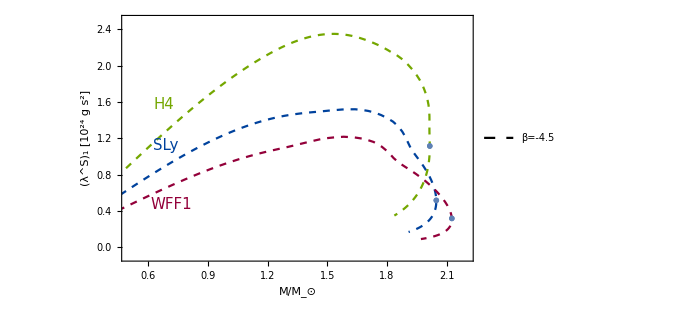

```mathematica
Show[{Table[ListLinePlot[Table[{massradADMT[[p]][[β]][[1]][[All,2]][[h]],((MultipoleScalarNoETl1[[p]][[β]][[1]][[h]]-1/2 ChargeTableT[[p]][[β]][[1]][[All,2]][[h]]MultipoleTensorNoETl1[[p]][[β]][[1]][[h]])/TidalScalarNoETl1[[p]][[β]][[1]][[h]])*(msunincm)^3 Gconst^-1(10^-24)},{h,1,Length[ρvals]}],PlotRange->{{0.5,2.2},{-0.1,2.5}},PlotStyle->{StyleList[[β]],ColorList[[p]]},If[p==3,PlotLegends->Placed[LineLegend[{StyleList[[β]]},{Style[βnamesList[[β]],15]}],{Left,Top}],PlotLegends->Automatic],Epilog->{Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.2,0.26}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.16,0.5}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.15,0.67}],{1,1}]},Frame->True,FrameLabel->{{Style["(λ^S)_1 [10^24 g s^2]","Latin Modern Roman",19,Black],None},{Style["M/M_⊙","Latin Modern Roman",18,Black],Style["Einstein frame φ_∞=10^-3","Latin Modern Roman",18,Black]}},FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},ImageSize->500],{p,1,3},{β,1,1}],Table[ListPlot[{{massradADMT[[p]][[1]][[1]][[All,2]][[MaxPointsSTEinstIndex[[p]][[1]][[1]]]],((MultipoleScalarNoETl1[[p]][[1]][[1]]-1/2 ChargeTableT[[p]][[1]][[1]][[All,2]]MultipoleTensorNoETl1[[p]][[1]][[1]])/TidalScalarNoETl1[[p]][[1]][[1]])[[MaxPointsSTEinstIndex[[p]][[1]][[1]]]]*(msunincm)^3 Gconst^-1(10^-24)}},PlotMarkers->Style["x",{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]}]}//Flatten]
```

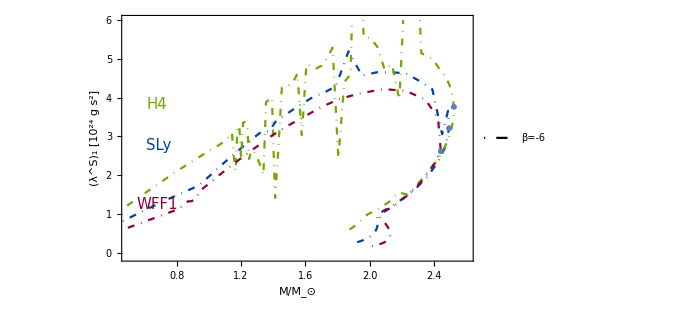

```mathematica
Show[{Table[ListLinePlot[Table[{massradADMT[[p]][[β]][[1]][[All,2]][[h]],((MultipoleScalarNoETl1[[p]][[β]][[1]]-1/2 ChargeTableT[[p]][[β]][[1]][[All,2]]MultipoleTensorNoETl1[[p]][[β]][[1]])/TidalScalarNoETl1[[p]][[β]][[1]])[[h]]*(msunincm)^3 Gconst^-1(10^-24)},{h,1,Length[ρvals]}],PlotRange->{{0.5,2.6},{-0.1,6}},PlotStyle->{StyleList[[β]],ColorList[[p]]},If[p==3,PlotLegends->Placed[LineLegend[{StyleList[[β]]},{Style[βnamesList[[β]],15]}],{Left,Top}],PlotLegends->Automatic],Epilog->{Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.16,0.26}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.14,0.5}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.13,0.67}],{1,1}]},Frame->True,FrameLabel->{{Style["(λ^S)_1 [10^24 g s^2]","Latin Modern Roman",19,Black],None},{Style["M/M_⊙","Latin Modern Roman",18,Black],Style["Einstein frame φ_∞=10^-3","Latin Modern Roman",18,Black]}},FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},ImageSize->500],{p,1,Length[EoSIndex]},{β,{2}}],Table[ListPlot[{{massradADMT[[p]][[2]][[1]][[All,2]][[MaxPointsSTEinstIndex[[p]][[2]][[1]]]],((MultipoleScalarNoETl1[[p]][[2]][[1]]-1/2 ChargeTableT[[p]][[2]][[1]][[All,2]]MultipoleTensorNoETl1[[p]][[2]][[1]])/TidalScalarNoETl1[[p]][[2]][[1]])[[MaxPointsSTEinstIndex[[p]][[2]][[1]]]]*(msunincm)^3 Gconst^-1(10^-24)}},PlotMarkers->Style["o",{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]}]}//Flatten]
```

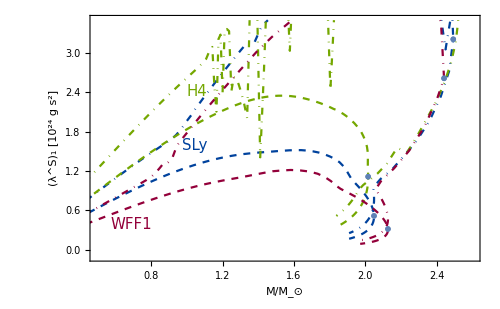

```mathematica
Show[{Table[ListLinePlot[If[β==2,Table[{massradADMT[[p]][[β]][[1]][[All,2]][[h]],((MultipoleScalarNoETl1[[p]][[β]][[1]]-1/2 ChargeTableT[[p]][[β]][[1]][[All,2]]MultipoleTensorNoETl1[[p]][[β]][[1]])/TidalScalarNoETl1[[p]][[β]][[1]])[[h]]*(msunincm)^3 Gconst^-1(10^-24)},{h,1,Length[ρvals]}],Table[{massradADMT[[p]][[β]][[1]][[All,2]][[h]],((MultipoleScalarNoETl1[[p]][[β]][[1]]-1/2 ChargeTableT[[p]][[β]][[1]][[All,2]]MultipoleTensorNoETl1[[p]][[β]][[1]])/TidalScalarNoETl1[[p]][[β]][[1]])[[h]]*(msunincm)^3 Gconst^-1(10^-24)},{h,1,Length[ρvals]}]],PlotRange->{{0.5,2.6},{-0.1,3.5}},PlotStyle->{StyleList[[β]],ColorList[[p]]},If[p==3,PlotLegends->Placed[LineLegend[{StyleList[[β]]},{Style[βnamesList[[β]],15]}],{Right,Top}],PlotLegends->Automatic],Epilog->{Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.16,0.18}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.3,0.5}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.3,0.72}],{1,1}]},Frame->True,FrameLabel->{{Style["(λ^S)_1 [10^24 g s^2]","Latin Modern Roman",19,Black],None},{Style["M/M_⊙","Latin Modern Roman",18,Black],Style["Einstein frame φ_∞=10^-3","Latin Modern Roman",18,Black]}},FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},ImageSize->500],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}],Table[ListPlot[{{massradADMT[[p]][[β]][[1]][[All,2]][[MaxPointsSTEinstIndex[[p]][[β]][[1]]]],((MultipoleScalarNoETl1[[p]][[β]][[1]]-1/2 ChargeTableT[[p]][[β]][[1]][[All,2]]MultipoleTensorNoETl1[[p]][[β]][[1]])/TidalScalarNoETl1[[p]][[β]][[1]])[[MaxPointsSTEinstIndex[[p]][[β]][[1]]]]*(msunincm)^3 Gconst^-1(10^-24)}},PlotMarkers->Style[{"x","o"}[[β]],{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}]}//Flatten]
```

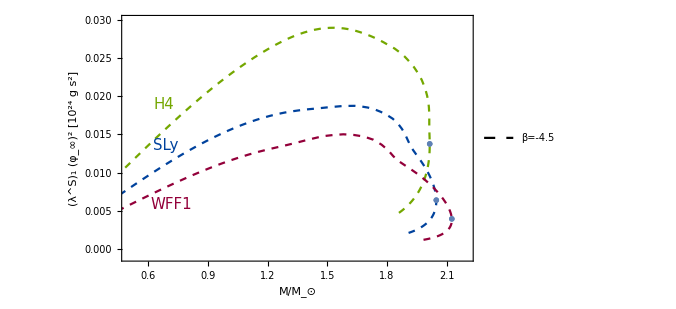

```mathematica
Show[{Table[ListLinePlot[Table[{massradJordT[[p]][[β]][[1]][[All,2]][[h]],((MultipoleScalarNoETl1[[p]][[β]][[1]]-1/2 ChargeTableT[[p]][[β]][[1]][[All,2]]MultipoleTensorNoETl1[[p]][[β]][[1]])/TidalScalarNoETl1[[p]][[β]][[1]])[[h]]*((ⅇ^(βvals[[β]] φinfvals[[1]]^2))/(2(-βvals[[β]])))^2(msunincm)^3 Gconst^-1(10^-24)},{h,1,Length[ρvals]}],PlotRange->{{0.5,2.2},{-0.001,0.03}},PlotStyle->{StyleList[[β]],ColorList[[p]]},If[p==3,PlotLegends->Placed[LineLegend[{StyleList[[β]]},{Style[βnamesList[[β]],15]}],{Left,Top}],PlotLegends->Automatic],Epilog->{Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.2,0.26}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.16,0.5}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.15,0.67}],{1,1}]},Frame->True,FrameLabel->{{Style["(λ^S)_1 (φ_∞)^2 [10^24 g s^2]","Latin Modern Roman",19,Black],None},{Style["M/M_⊙","Latin Modern Roman",18,Black],Style["Jordan frame φ_∞=10^-3","Latin Modern Roman",18,Black]}},FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},ImageSize->500],{p,1,Length[EoSIndex]},{β,1,1}],Table[ListPlot[{{massradJordT[[p]][[1]][[1]][[All,2]][[MaxPointsSTJordIndex[[p]][[1]][[1]]]],((MultipoleScalarNoETl1[[p]][[1]][[1]]-1/2 ChargeTableT[[p]][[1]][[1]][[All,2]]MultipoleTensorNoETl1[[p]][[1]][[1]])/TidalScalarNoETl1[[p]][[1]][[1]])[[MaxPointsSTJordIndex[[p]][[1]][[1]]]]((ⅇ^(βvals[[1]] φinfvals[[1]]^2))/(2(-βvals[[1]])))^2(msunincm)^3 Gconst^-1(10^-24)}},PlotMarkers->Style["x",{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]}]}//Flatten]
```

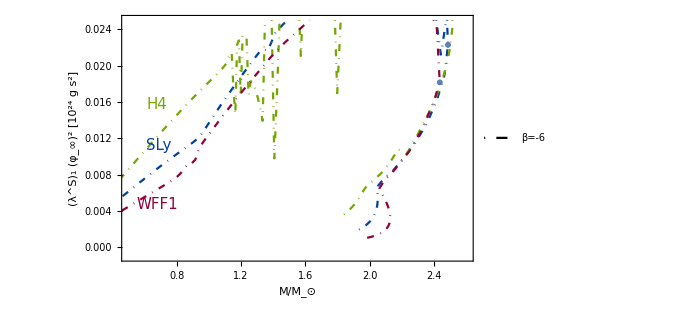

```mathematica
Show[{Table[ListLinePlot[Table[{massradJordT[[p]][[β]][[1]][[All,2]][[h]],((MultipoleScalarNoETl1[[p]][[β]][[1]]-1/2 ChargeTableT[[p]][[β]][[1]][[All,2]]MultipoleTensorNoETl1[[p]][[β]][[1]])/TidalScalarNoETl1[[p]][[β]][[1]])[[h]]*((ⅇ^(βvals[[β]] φinfvals[[1]]^2))/(2(-βvals[[β]])))^2(msunincm)^3 Gconst^-1(10^-24)},{h,1,Length[ρvals]}],PlotRange->{{0.5,2.6},{-0.001,0.025}},PlotStyle->{StyleList[[β]],ColorList[[p]]},If[p==3,PlotLegends->Placed[LineLegend[{StyleList[[β]]},{Style[βnamesList[[β]],15]}],{Left,Top}],PlotLegends->Automatic],Epilog->{Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.16,0.26}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.14,0.5}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.13,0.67}],{1,1}]},Frame->True,FrameLabel->{{Style["(λ^S)_1 (φ_∞)^2 [10^24 g s^2]","Latin Modern Roman",19,Black],None},{Style["M/M_⊙","Latin Modern Roman",18,Black],Style["Jordan frame φ_∞=10^-3","Latin Modern Roman",18,Black]}},FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},ImageSize->500],{p,1,Length[EoSIndex]},{β,{2}}],Table[ListPlot[{{massradJordT[[p]][[2]][[1]][[All,2]][[MaxPointsSTJordIndex[[p]][[2]][[1]]]],((MultipoleScalarNoETl1[[p]][[2]][[1]]-1/2 ChargeTableT[[p]][[2]][[1]][[All,2]]MultipoleTensorNoETl1[[p]][[2]][[1]])/TidalScalarNoETl1[[p]][[2]][[1]])[[MaxPointsSTJordIndex[[p]][[2]][[1]]]]((ⅇ^(βvals[[2]] φinfvals[[1]]^2))/(2(-βvals[[2]])))^2(msunincm)^3 Gconst^-1(10^-24)}},PlotMarkers->Style["o",{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]}]}//Flatten]
```

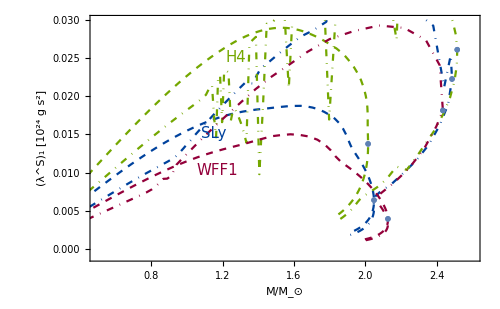

```mathematica
Show[{Table[ListLinePlot[Table[{massradJordT[[p]][[β]][[1]][[All,2]][[h]],((MultipoleScalarNoETl1[[p]][[β]][[1]]-1/2 ChargeTableT[[p]][[β]][[1]][[All,2]]MultipoleTensorNoETl1[[p]][[β]][[1]])/TidalScalarNoETl1[[p]][[β]][[1]])[[h]]*((ⅇ^(βvals[[β]] φinfvals[[1]]^2))/(2(-βvals[[β]])))^2(msunincm)^3 Gconst^-1(10^-24)},{h,1,Length[ρvals]}],PlotRange->{{0.5,2.6},{-0.001,0.03}},PlotStyle->{StyleList[[β]],ColorList[[p]]},If[p==3,PlotLegends->Placed[LineLegend[{StyleList[[β]]},{Style[βnamesList[[β]],15]}],{Right,Top}],PlotLegends->Automatic],Epilog->{Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.38,0.4}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.35,0.55}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.4,0.86}],{1,1}]},Frame->True,FrameLabel->{{Style["(λ^S)_1 [10^24 g s^2]","Latin Modern Roman",19,Black],None},{Style["M/M_⊙","Latin Modern Roman",18,Black],Style["Jordan frame φ_∞=10^-3","Latin Modern Roman",18,Black]}},FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},ImageSize->500],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}],Table[ListPlot[{{massradJordT[[p]][[β]][[1]][[All,2]][[MaxPointsSTJordIndex[[p]][[β]][[1]]]],((MultipoleScalarNoETl1[[p]][[β]][[1]]-1/2 ChargeTableT[[p]][[β]][[1]][[All,2]]MultipoleTensorNoETl1[[p]][[β]][[1]])/TidalScalarNoETl1[[p]][[β]][[1]])[[MaxPointsSTJordIndex[[p]][[β]][[1]]]]*((ⅇ^(βvals[[β]] φinfvals[[1]]^2))/(2(-βvals[[β]])))^2(msunincm)^3 Gconst^-1(10^-24)}},PlotMarkers->Style[{"x","o"}[[β]],{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}]}//Flatten]
```

```mathematica
(* l=2 *)
```

```mathematica
(* Tensor *)
```

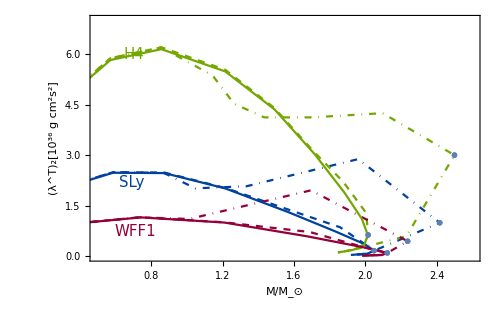

```mathematica
Show[{Table[ListLinePlot[Table[{massradADMT[[p]][[β]][[1]][[All,2]][[h]],((MultipoleTensorNoES[[p]][[β]][[1]])/TidalTensorNoES[[p]][[β]][[1]])[[h]](msunincm)^5 Gconst^-1(10^-36)},{h,1,Length[ρvals]}],PlotStyle->{StyleList[[β]],ColorList[[p]]},PlotRange->{{0.5,2.6},{0,7}},If[p==3,PlotLegends->Placed[LineLegend[{StyleList[[β]]},{Style[βnamesList[[β]],15]}],{Right,Top}],PlotLegends->Automatic],Epilog->{Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.17,0.15}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.14,0.35}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.14,0.87}],{1,1}]},Frame->True,FrameLabel->{{Style["(λ^T)_2[10^36 g cm^2s^2]","Latin Modern Roman",19,Black],None},{Style["M/M_⊙","Latin Modern Roman",18,Black],Style["Einstein frame φ_∞=10^-3","Latin Modern Roman",18,Black]}},FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},ImageSize->500],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}],Table[ListLinePlot[Table[{massradGRT[[p]][[1]][[1]][[All,2]][[h]],((MultipoleTensorNoESGR[[p]])/TidalTensorNoESGR[[p]])[[h]](msunincm)^5 Gconst^-1(10^-36)},{h,1,Length[ρvals]}],PlotStyle->{ColorList[[p]]},PlotRange->{{0.5,2.6},{0,6000}},ImageSize->500],{p,1,Length[EoSIndex]}],Table[ListPlot[{{massradADMT[[p]][[1]][[1]][[All,2]][[MaxPointsSTEinstIndex[[p]][[1]][[1]]]],((MultipoleTensorNoES[[p]][[1]][[1]])/TidalTensorNoES[[p]][[1]][[1]])[[MaxPointsSTEinstIndex[[p]][[1]][[1]]]](msunincm)^5 Gconst^-1(10^-36)}},PlotMarkers->Style["x",{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]}],Table[ListPlot[{{massradADMT[[p]][[2]][[1]][[All,2]][[MaxPointsSTEinstIndex[[p]][[2]][[1]]]],((MultipoleTensorNoES[[p]][[2]][[1]])/TidalTensorNoES[[p]][[2]][[1]])[[MaxPointsSTEinstIndex[[p]][[2]][[1]]]](msunincm)^5 Gconst^-1(10^-36)}},PlotMarkers->Style["o",{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]}]
(*Table[ListPlot[{{massradADMT[[p]][[1]][[1]][[All,2]][[ZeroGRPoints[[p]][[1]][[1]]]],((MultipoleTensorNoES[[p]][[1]][[1]])/TidalTensorNoES[[p]][[1]][[1]])[[ZeroGRPoints[[p]][[1]][[1]]]](msunincm)^5 Gconst^-1(10^-36)}},PlotMarkers->Style["Z",{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]}]*)}//Flatten]
```

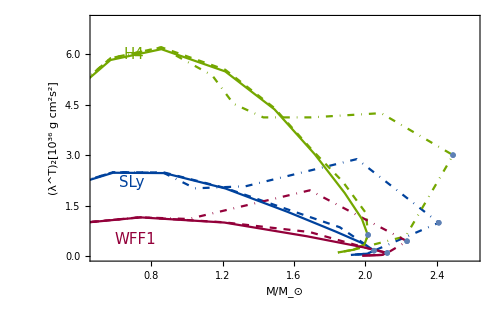

```mathematica
Show[{Table[ListLinePlot[Table[{massradJordT[[p]][[β]][[1]][[All,2]][[h]],((MultipoleTensorNoES[[p]][[β]][[1]])/TidalTensorNoES[[p]][[β]][[1]])[[h]]*(msunincm)^5 Gconst^-1(10^-36)},{h,1,Length[ρvals]}],PlotStyle->{StyleList[[β]],ColorList[[p]]},PlotRange->{{0.5,2.6},{0,7}},If[p==3,PlotLegends->Placed[LineLegend[{StyleList[[β]]},{Style[βnamesList[[β]],15]}],{Right,Top}],PlotLegends->Automatic],Epilog->{Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.17,0.12}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.14,0.35}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.14,0.87}],{1,1}]},Frame->True,FrameLabel->{{Style["(λ^T)_2[10^36 g cm^2s^2]","Latin Modern Roman",19,Black],None},{Style["M/M_⊙","Latin Modern Roman",18,Black],Style["Jordan frame φ_∞=10^-3","Latin Modern Roman",18,Black]}},FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},ImageSize->500],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}],Table[ListLinePlot[Table[{massradGRT[[p]][[1]][[1]][[All,2]][[h]],((MultipoleTensorNoESGR[[p]])/TidalTensorNoESGR[[p]])[[h]]*(msunincm)^5 Gconst^-1(10^-36)},{h,1,Length[ρvals]}],PlotStyle->{ColorList[[p]]},PlotRange->{{0.5,2.5},{0,7}},ImageSize->500],{p,1,Length[EoSIndex]}],Table[ListPlot[{{massradJordT[[p]][[1]][[1]][[All,2]][[MaxPointsSTJordIndex[[p]][[1]][[1]]]],((MultipoleTensorNoES[[p]][[1]][[1]])/TidalTensorNoES[[p]][[1]][[1]])[[MaxPointsSTJordIndex[[p]][[1]][[1]]]](msunincm)^5 Gconst^-1(10^-36)}},PlotMarkers->Style["x",{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]}],Table[ListPlot[{{massradJordT[[p]][[2]][[1]][[All,2]][[MaxPointsSTJordIndex[[p]][[2]][[1]]]],((MultipoleTensorNoES[[p]][[2]][[1]])/TidalTensorNoES[[p]][[2]][[1]])[[MaxPointsSTJordIndex[[p]][[2]][[1]]]](msunincm)^5 Gconst^-1(10^-36)}},PlotMarkers->Style["o",{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]}]}//Flatten]
```

```mathematica
(* Scalar*)
```

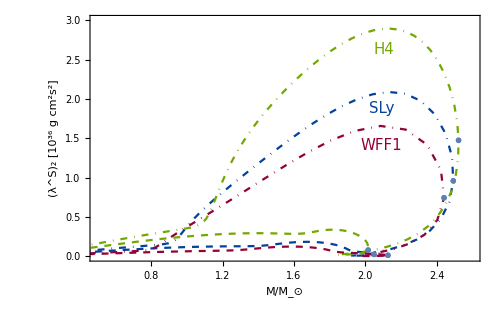

```mathematica
Show[{Table[ListLinePlot[Table[{massradADMT[[p]][[β]][[1]][[All,2]][[h]],((MultipoleScalarNoET[[p]][[β]][[1]])/TidalScalarNoET[[p]][[β]][[1]])[[h]]*(msunincm)^5 Gconst^-1(10^-36)},{h,1,Length[ρvals]}],PlotStyle->{StyleList[[β]],ColorList[[p]]},PlotRange->{{0.5,2.6},{0,3}},If[p==3,PlotLegends->Placed[LineLegend[{StyleList[[β]]},{Style[βnamesList[[β]],15]}],{Left,Top}],PlotLegends->Automatic],Epilog->{Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.8,0.5}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.78,0.65}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.78,0.89}],{1,1}]},Frame->True,FrameLabel->{{Style["(λ^S)_2 [10^36 g cm^2s^2]","Latin Modern Roman",19,Black],None},{Style["M/M_⊙","Latin Modern Roman",18,Black],Style["Einstein frame φ_∞=10^-3","Latin Modern Roman",18,Black]}},FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},ImageSize->500],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}],Table[ListPlot[{{massradADMT[[p]][[1]][[1]][[All,2]][[MaxPointsSTEinstIndex[[p]][[1]][[1]]]],((MultipoleScalarNoET[[p]][[1]][[1]])/TidalScalarNoET[[p]][[1]][[1]])[[MaxPointsSTEinstIndex[[p]][[1]][[1]]]](msunincm)^5 Gconst^-1(10^-36)}},PlotMarkers->Style["x",{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]}],Table[ListPlot[{{massradADMT[[p]][[2]][[1]][[All,2]][[MaxPointsSTEinstIndex[[p]][[2]][[1]]]],((MultipoleScalarNoET[[p]][[2]][[1]])/TidalScalarNoET[[p]][[2]][[1]])[[MaxPointsSTEinstIndex[[p]][[2]][[1]]]](msunincm)^5 Gconst^-1(10^-36)}},PlotMarkers->Style["o",{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]}]}//Flatten]
```

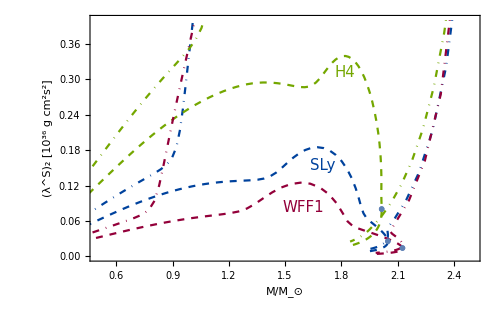

```mathematica
Show[{Table[ListLinePlot[Table[{massradADMT[[p]][[β]][[1]][[All,2]][[h]],((MultipoleScalarNoET[[p]][[β]][[1]])/TidalScalarNoET[[p]][[β]][[1]])[[h]]*(msunincm)^5 Gconst^-1(10^-36)},{h,1,Length[ρvals]}],PlotStyle->{StyleList[[β]],ColorList[[p]]},PlotRange->{{0.5,2.5},{0,0.4}},If[p==3,PlotLegends->Placed[LineLegend[{StyleList[[β]]},{Style[βnamesList[[β]],15]}],{Left,Top}],PlotLegends->Automatic],Epilog->{Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.60,0.25}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.63,0.42}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.68,0.80}],{1,1}]},Frame->True,FrameLabel->{{Style["(λ^S)_2 [10^36 g cm^2s^2]","Latin Modern Roman",19,Black],None},{Style["M/M_⊙","Latin Modern Roman",18,Black],Style["Einstein frame φ_∞=10^-3","Latin Modern Roman",18,Black]}},FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},ImageSize->500],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}],Table[ListPlot[{{massradADMT[[p]][[1]][[1]][[All,2]][[MaxPointsSTEinstIndex[[p]][[1]][[1]]]],((MultipoleScalarNoET[[p]][[1]][[1]])/TidalScalarNoET[[p]][[1]][[1]])[[MaxPointsSTEinstIndex[[p]][[1]][[1]]]](msunincm)^5 Gconst^-1(10^-36)}},PlotMarkers->Style["x",{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]}],Table[ListPlot[{{massradADMT[[p]][[2]][[1]][[All,2]][[MaxPointsSTEinstIndex[[p]][[2]][[1]]]],((MultipoleScalarNoET[[p]][[2]][[1]])/TidalScalarNoET[[p]][[2]][[1]])[[MaxPointsSTEinstIndex[[p]][[2]][[1]]]](msunincm)^5 Gconst^-1(10^-36)}},PlotMarkers->Style["o",{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]}]}//Flatten]
```

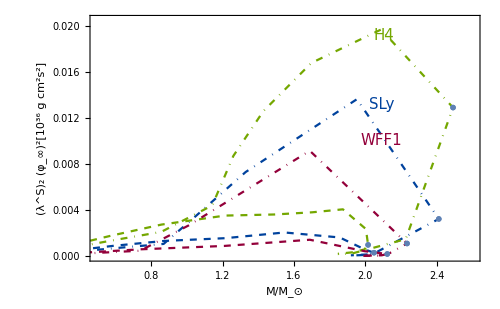

```mathematica
Show[{Table[ListLinePlot[Table[{massradJordT[[p]][[β]][[1]][[All,2]][[h]],((MultipoleScalarNoET[[p]][[β]][[1]])/TidalScalarNoET[[p]][[β]][[1]])[[h]]*((ⅇ^(βvals[[β]] φinfvals[[1]]^2))/(2(-βvals[[β]])))^2(msunincm)^5 Gconst^-1(10^-36)},{h,1,Length[ρvals]}],PlotStyle->{StyleList[[β]],ColorList[[p]]},PlotRange->{{0.5,2.6},{0,0.0205}},If[p==3,PlotLegends->Placed[LineLegend[{StyleList[[β]]},{Style[βnamesList[[β]],15]}],{Left,Top}],PlotLegends->Automatic],Epilog->{Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.8,0.52}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.78,0.67}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.78,0.95}],{1,1}]},Frame->True,FrameLabel->{{Style["(λ^S)_2 (φ_∞)^2[10^36 g cm^2s^2]","Latin Modern Roman",19,Black],None},{Style["M/M_⊙","Latin Modern Roman",18,Black],Style["Jordan frame φ_∞=10^-3","Latin Modern Roman",18,Black]}},FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},ImageSize->500],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}],Table[ListPlot[{{massradJordT[[p]][[1]][[1]][[All,2]][[MaxPointsSTJordIndex[[p]][[1]][[1]]]],((MultipoleScalarNoET[[p]][[1]][[1]])/TidalScalarNoET[[p]][[1]][[1]])[[MaxPointsSTJordIndex[[p]][[1]][[1]]]]*((ⅇ^(βvals[[1]] φinfvals[[1]]^2))/(2(-βvals[[1]])))^2(msunincm)^5 Gconst^-1(10^-36)}},PlotMarkers->Style["x",{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]}],Table[ListPlot[{{massradJordT[[p]][[2]][[1]][[All,2]][[MaxPointsSTJordIndex[[p]][[2]][[1]]]],((MultipoleScalarNoET[[p]][[2]][[1]])/TidalScalarNoET[[p]][[2]][[1]])[[MaxPointsSTJordIndex[[p]][[2]][[1]]]]*((ⅇ^(βvals[[2]] φinfvals[[1]]^2))/(2(-βvals[[2]])))^2(msunincm)^5 Gconst^-1(10^-36)}},PlotMarkers->Style["o",{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]}]}//Flatten]
```

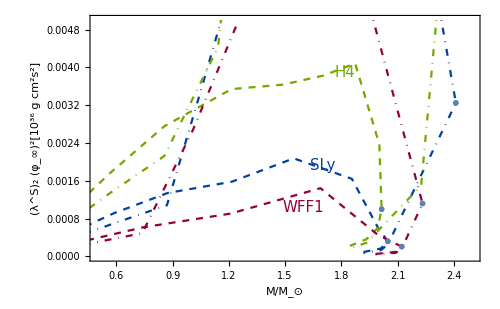

```mathematica
Show[{Table[ListLinePlot[Table[{massradJordT[[p]][[β]][[1]][[All,2]][[h]],((MultipoleScalarNoET[[p]][[β]][[1]])/TidalScalarNoET[[p]][[β]][[1]])[[h]]*(((1+(-βvals[[β]]φinfvals[[1]])^2)*ⅇ^(1/2 βvals[[β]] φinfvals[[1]]^2))/(1+ChargeTableT[[p]][[β]][[1]][[All,2]][[h]]*(-βvals[[β]]φinfvals[[1]])))^0*((ⅇ^(βvals[[β]] φinfvals[[1]]^2))/(2(-βvals[[β]])))^2(msunincm)^5 Gconst^-1(10^-36)},{h,1,Length[ρvals]}],PlotStyle->{StyleList[[β]],ColorList[[p]]},PlotRange->{{0.5,2.5},{-0,0.005}},If[p==3,PlotLegends->Placed[LineLegend[{StyleList[[β]]},{Style[βnamesList[[β]],15]}],{Left,Top}],PlotLegends->Automatic],Epilog->{Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.60,0.25}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.63,0.42}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.68,0.80}],{1,1}]},Frame->True,FrameLabel->{{Style["(λ^S)_2 (φ_∞)^2[10^36 g cm^2s^2]","Latin Modern Roman",19,Black],None},{Style["M/M_⊙","Latin Modern Roman",18,Black],Style["Jordan frame φ_∞=10^-3","Latin Modern Roman",18,Black]}},FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},ImageSize->500],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}],Table[ListPlot[{{massradJordT[[p]][[1]][[1]][[All,2]][[MaxPointsSTJordIndex[[p]][[1]][[1]]]],((MultipoleScalarNoET[[p]][[1]][[1]])/TidalScalarNoET[[p]][[1]][[1]])[[MaxPointsSTJordIndex[[p]][[1]][[1]]]]*((ⅇ^(βvals[[1]] φinfvals[[1]]^2))/(2(-βvals[[1]])))^2(msunincm)^5 Gconst^-1(10^-36)}},PlotMarkers->Style["x",{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]}],Table[ListPlot[{{massradJordT[[p]][[2]][[1]][[All,2]][[MaxPointsSTJordIndex[[p]][[2]][[1]]]],((MultipoleScalarNoET[[p]][[2]][[1]])/TidalScalarNoET[[p]][[2]][[1]])[[MaxPointsSTJordIndex[[p]][[2]][[1]]]]*((ⅇ^(βvals[[2]] φinfvals[[1]]^2))/(2(-βvals[[2]])))^2(msunincm)^5 Gconst^-1(10^-36)}},PlotMarkers->Style["o",{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]}]}//Flatten]
```

```mathematica
(* Scalar-Tensor *)
```

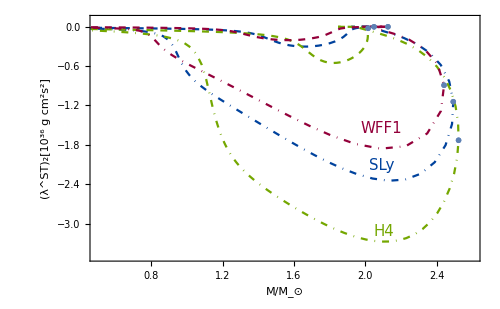

```mathematica
Show[{Table[ListLinePlot[Table[{massradADMT[[p]][[β]][[1]][[All,2]][[h]],((MultipoleScalarNoES[[p]][[β]][[1]])/TidalTensorNoES[[p]][[β]][[1]])[[h]](msunincm)^5 Gconst^-1(10^-36)},{h,1,Length[ρvals]}],PlotStyle->{StyleList[[β]],ColorList[[p]]},PlotRange->{{0.5,2.6},{0.1,-3.5}},If[p==3,PlotLegends->Placed[LineLegend[{StyleList[[β]]},{Style[βnamesList[[β]],15]}],{Left,Bottom}],PlotLegends->Automatic],Epilog->{Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.8,0.57}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.78,0.42}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.78,0.15}],{1,1}]},Frame->True,FrameLabel->{{Style["(λ^ST)_2[10^36 g cm^2s^2]","Latin Modern Roman",19,Black],None},{Style["M/M_⊙","Latin Modern Roman",18,Black],Style["Einstein frame φ_∞=10^-3","Latin Modern Roman",18,Black]}},FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},ImageSize->500],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}],Table[ListPlot[{{massradADMT[[p]][[1]][[1]][[All,2]][[MaxPointsSTEinstIndex[[p]][[1]][[1]]]],((MultipoleScalarNoES[[p]][[1]][[1]])/TidalTensorNoES[[p]][[1]][[1]])[[MaxPointsSTEinstIndex[[p]][[1]][[1]]]](msunincm)^5 Gconst^-1(10^-36)}},PlotMarkers->Style["x",{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]}],Table[ListPlot[{{massradADMT[[p]][[2]][[1]][[All,2]][[MaxPointsSTEinstIndex[[p]][[2]][[1]]]],((MultipoleScalarNoES[[p]][[2]][[1]])/TidalTensorNoES[[p]][[2]][[1]])[[MaxPointsSTEinstIndex[[p]][[2]][[1]]]](msunincm)^5 Gconst^-1(10^-36)}},PlotMarkers->Style["o",{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]}]}//Flatten]
```

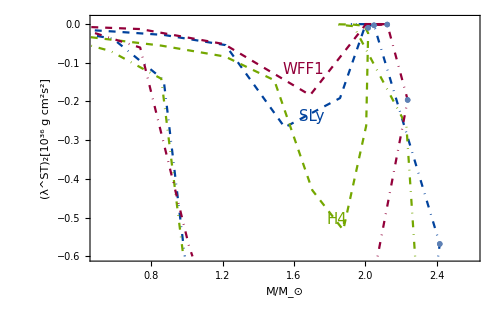

```mathematica
Show[{Table[ListLinePlot[Table[{massradADMT[[p]][[β]][[1]][[All,2]][[h]],((MultipoleScalarNoES[[p]][[β]][[1]])/TidalTensorNoES[[p]][[β]][[1]])[[h]](msunincm)^5 Gconst^-1(10^-36)},{h,1,Length[ρvals]}],PlotStyle->{StyleList[[β]],ColorList[[p]]},PlotRange->{{0.5,2.6},{0.01,-0.6}},If[p==3,PlotLegends->Placed[LineLegend[{StyleList[[β]]},{Style[βnamesList[[β]],15]}],{Right,Top}],PlotLegends->Automatic],Epilog->{Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.6,0.81}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.6,0.62}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.66,0.2}],{1,1}]},Frame->True,FrameLabel->{{Style["(λ^ST)_2[10^36 g cm^2s^2]","Latin Modern Roman",19,Black],None},{Style["M/M_⊙","Latin Modern Roman",18,Black],Style["Einstein frame φ_∞=10^-3","Latin Modern Roman",18,Black]}},FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},ImageSize->500],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}],Table[ListPlot[{{massradADMT[[p]][[1]][[1]][[All,2]][[MaxPointsSTEinstIndex[[p]][[1]][[1]]]],((MultipoleScalarNoES[[p]][[1]][[1]])/TidalTensorNoESl3[[p]][[1]][[1]])[[MaxPointsSTEinstIndex[[p]][[1]][[1]]]]*(msunincm)^5 Gconst^-1(10^-36)}},PlotMarkers->Style["x",{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]}],Table[ListPlot[{{massradADMT[[p]][[2]][[1]][[All,2]][[MaxPointsSTEinstIndex[[p]][[2]][[1]]]],((MultipoleScalarNoES[[p]][[2]][[1]])/TidalTensorNoES[[p]][[2]][[1]])[[MaxPointsSTEinstIndex[[p]][[2]][[1]]]]*(msunincm)^5 Gconst^-1(10^-36)}},PlotMarkers->Style["o",{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]}]}//Flatten]
```

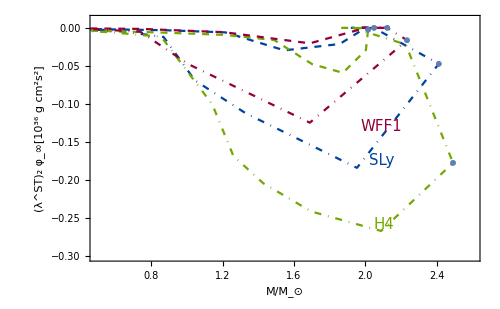

```mathematica
Show[{Table[ListLinePlot[Table[{massradJordT[[p]][[β]][[1]][[All,2]][[h]],((MultipoleScalarNoES[[p]][[β]][[1]])/TidalTensorNoES[[p]][[β]][[1]])[[h]]*((ⅇ^(βvals[[β]] φinfvals[[1]]^2))/(2(-βvals[[β]])))(msunincm)^5 Gconst^-1(10^-36)},{h,1,Length[ρvals]}],PlotStyle->{StyleList[[β]],ColorList[[p]]},PlotRange->{{0.5,2.6},{0.01,-0.3}},If[p==3,PlotLegends->Placed[LineLegend[{StyleList[[β]]},{Style[βnamesList[[β]],15]}],{Left,Bottom}],PlotLegends->Automatic],Epilog->{Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.8,0.58}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.78,0.44}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.78,0.18}],{1,1}]},Frame->True,FrameLabel->{{Style["(λ^ST)_2 φ_∞[10^36 g cm^2s^2]","Latin Modern Roman",19,Black],None},{Style["M/M_⊙","Latin Modern Roman",18,Black],Style["Jordan frame φ_∞=10^-3","Latin Modern Roman",18,Black]}},FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},ImageSize->500],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}],Table[ListPlot[{{massradJordT[[p]][[1]][[1]][[All,2]][[MaxPointsSTJordIndex[[p]][[1]][[1]]]],((MultipoleScalarNoES[[p]][[1]][[1]])/TidalTensorNoES[[p]][[1]][[1]])[[MaxPointsSTJordIndex[[p]][[1]][[1]]]]*((ⅇ^(βvals[[1]] φinfvals[[1]]^2))/(2(-βvals[[1]])))(msunincm)^5 Gconst^-1(10^-36)}},PlotMarkers->Style["x",{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]}],Table[ListPlot[{{massradJordT[[p]][[2]][[1]][[All,2]][[MaxPointsSTJordIndex[[p]][[2]][[1]]]],((MultipoleScalarNoES[[p]][[2]][[1]])/TidalTensorNoES[[p]][[2]][[1]])[[MaxPointsSTJordIndex[[p]][[2]][[1]]]]*((ⅇ^(βvals[[2]] φinfvals[[1]]^2))/(2(-βvals[[2]])))(msunincm)^5 Gconst^-1(10^-36)}},PlotMarkers->Style["o",{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]}]}//Flatten]
```

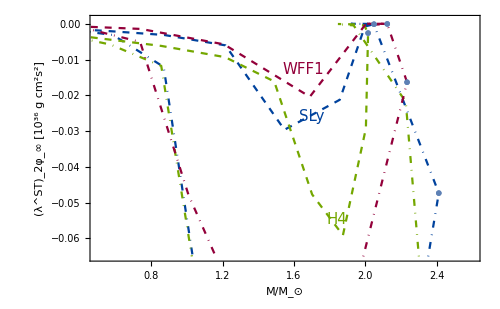

```mathematica
Show[{Table[ListLinePlot[Table[{massradJordT[[p]][[β]][[1]][[All,2]][[h]],((MultipoleScalarNoES[[p]][[β]][[1]])/TidalTensorNoES[[p]][[β]][[1]])[[h]]*((ⅇ^(βvals[[β]] φinfvals[[1]]^2))/(2(-βvals[[β]])))(msunincm)^5 Gconst^-1(10^-36)},{h,1,Length[ρvals]}],PlotStyle->{StyleList[[β]],ColorList[[p]]},PlotRange->{{0.5,2.6},{0.001,-0.065}},If[p==3,PlotLegends->Placed[LineLegend[{StyleList[[β]]},{Style[βnamesList[[β]],15]}],{Right,Top}],PlotLegends->Automatic],Epilog->{Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.6,0.81}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.6,0.62}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.66,0.2}],{1,1}]},Frame->True,FrameLabel->{{Style["(λ^ST)_2φ_∞ [10^36 g cm^2s^2]","Latin Modern Roman",19,Black],None},{Style["M/M_⊙","Latin Modern Roman",18,Black],Style["Jordan frame φ_∞=10^-3","Latin Modern Roman",18,Black]}},FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},ImageSize->500],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}],Table[ListPlot[{{massradJordT[[p]][[1]][[1]][[All,2]][[MaxPointsSTJordIndex[[p]][[1]][[1]]]],((MultipoleScalarNoES[[p]][[1]][[1]])/TidalTensorNoES[[p]][[1]][[1]])[[MaxPointsSTJordIndex[[p]][[1]][[1]]]]((ⅇ^(βvals[[1]] φinfvals[[1]]^2))/(2(-βvals[[1]])))(msunincm)^5 Gconst^-1(10^-36)}},PlotMarkers->Style["x",{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]}],Table[ListPlot[{{massradJordT[[p]][[2]][[1]][[All,2]][[MaxPointsSTJordIndex[[p]][[2]][[1]]]],((MultipoleScalarNoES[[p]][[2]][[1]])/TidalTensorNoES[[p]][[2]][[1]])[[MaxPointsSTJordIndex[[p]][[2]][[1]]]]((ⅇ^(βvals[[2]] φinfvals[[1]]^2))/(2(-βvals[[2]])))(msunincm)^5 Gconst^-1(10^-36)}},PlotMarkers->Style["o",{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]}]}//Flatten]
```

```mathematica
(* l=3 *)
```

```mathematica
(* Tensor *)
```

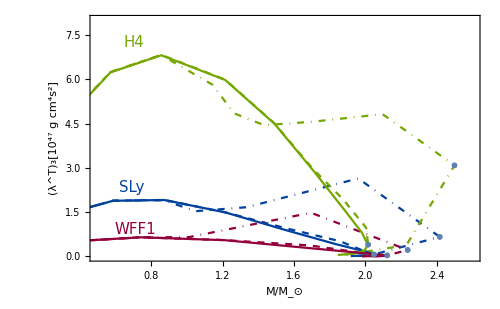

```mathematica
Show[{Table[ListLinePlot[Table[{massradADMT[[p]][[β]][[1]][[All,2]][[h]],((MultipoleTensorNoESl3[[p]][[β]][[1]])/TidalTensorNoESl3[[p]][[β]][[1]])[[h]]*(msunincm)^7 Gconst^-1(10^-47)},{h,1,Length[ρvals]}],PlotStyle->{StyleList[[β]],ColorList[[p]]},PlotRange->{{0.5,2.6},{0,8}},If[p==3,PlotLegends->Placed[LineLegend[{StyleList[[β]]},{Style[βnamesList[[β]],15]}],{Right,Top}],PlotLegends->Automatic],Epilog->{Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.17,0.16}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.14,0.33}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.14,0.92}],{1,1}]},Frame->True,FrameLabel->{{Style["(λ^T)_3[10^47 g cm^4s^2]","Latin Modern Roman",19,Black],None},{Style["M/M_⊙","Latin Modern Roman",18,Black],Style["Einstein frame φ_∞=10^-3","Latin Modern Roman",18,Black]}},FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},ImageSize->500],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}],Table[ListLinePlot[Table[{massradGRT[[p]][[1]][[1]][[All,2]][[h]],((MultipoleTensorNoESGRl3[[p]])/TidalTensorNoESGRl3[[p]])[[h]]*(msunincm)^7 Gconst^-1(10^-47)},{h,1,Length[ρvals]}],PlotStyle->{ColorList[[p]]},PlotRange->{{0.5,2.5},{0,8}},ImageSize->500],{p,1,Length[EoSIndex]}],Table[ListPlot[{{massradADMT[[p]][[1]][[1]][[All,2]][[MaxPointsSTEinstIndex[[p]][[1]][[1]]]],((MultipoleTensorNoESl3[[p]][[1]][[1]])/TidalTensorNoESl3[[p]][[1]][[1]])[[MaxPointsSTEinstIndex[[p]][[1]][[1]]]]*(msunincm)^7 Gconst^-1(10^-47)}},PlotMarkers->Style["x",{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]}],Table[ListPlot[{{massradADMT[[p]][[2]][[1]][[All,2]][[MaxPointsSTEinstIndex[[p]][[2]][[1]]]],((MultipoleTensorNoESl3[[p]][[2]][[1]])/TidalTensorNoESl3[[p]][[2]][[1]])[[MaxPointsSTEinstIndex[[p]][[2]][[1]]]]*(msunincm)^7 Gconst^-1(10^-47)}},PlotMarkers->Style["o",{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]}]}//Flatten]
```

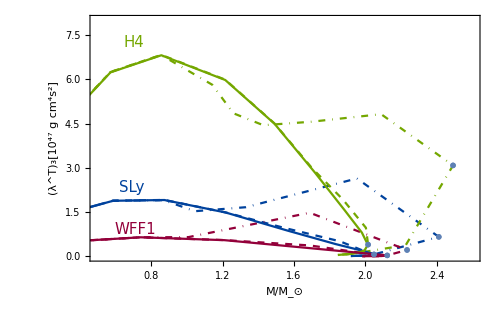

```mathematica
Show[{Table[ListLinePlot[Table[{massradJordT[[p]][[β]][[1]][[All,2]][[h]],((MultipoleTensorNoESl3[[p]][[β]][[1]])/TidalTensorNoESl3[[p]][[β]][[1]])[[h]]*(msunincm)^7 Gconst^-1(10^-47)},{h,1,Length[ρvals]}],PlotStyle->{StyleList[[β]],ColorList[[p]]},PlotRange->{{0.5,2.6},{0,8}},If[p==3,PlotLegends->Placed[LineLegend[{StyleList[[β]]},{Style[βnamesList[[β]],15]}],{Right,Top}],PlotLegends->Automatic],Epilog->{Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.17,0.16}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.14,0.33}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.14,0.92}],{1,1}]},Frame->True,FrameLabel->{{Style["(λ^T)_3[10^47 g cm^4s^2]","Latin Modern Roman",19,Black],None},{Style["M/M_⊙","Latin Modern Roman",18,Black],Style["Jordan frame φ_∞=10^-3","Latin Modern Roman",18,Black]}},FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},ImageSize->500],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}],Table[ListLinePlot[Table[{massradGRT[[p]][[1]][[1]][[All,2]][[h]],((MultipoleTensorNoESGRl3[[p]])/TidalTensorNoESGRl3[[p]])[[h]]*(msunincm)^7 Gconst^-1(10^-47)},{h,1,Length[ρvals]}],PlotStyle->{ColorList[[p]]},PlotRange->{{0.5,2.5},{0,7}},ImageSize->500],{p,1,Length[EoSIndex]}],Table[ListPlot[{{massradJordT[[p]][[1]][[1]][[All,2]][[MaxPointsSTJordIndex[[p]][[1]][[1]]]],((MultipoleTensorNoESl3[[p]][[1]][[1]])/TidalTensorNoESl3[[p]][[1]][[1]])[[MaxPointsSTJordIndex[[p]][[1]][[1]]]](msunincm)^7 Gconst^-1(10^-47)}},PlotMarkers->Style["x",{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]}],Table[ListPlot[{{massradJordT[[p]][[2]][[1]][[All,2]][[MaxPointsSTJordIndex[[p]][[2]][[1]]]],((MultipoleTensorNoESl3[[p]][[2]][[1]])/TidalTensorNoESl3[[p]][[2]][[1]])[[MaxPointsSTJordIndex[[p]][[2]][[1]]]](msunincm)^7 Gconst^-1(10^-47)}},PlotMarkers->Style["o",{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]}]}//Flatten]
```

```mathematica
(* Scalar *)
```

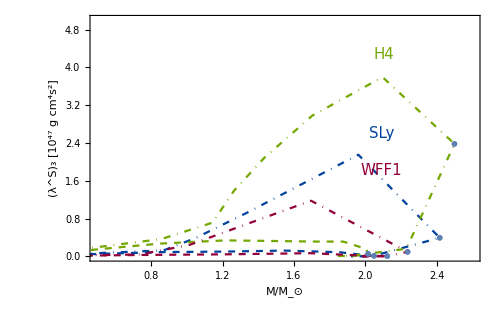

```mathematica
Show[{Table[ListLinePlot[Table[{massradADMT[[p]][[β]][[1]][[All,2]][[h]],((MultipoleScalarNoETl3[[p]][[β]][[1]])/TidalScalarNoETl3[[p]][[β]][[1]])[[h]]*(msunincm)^7 Gconst^-1(10^-47)},{h,1,Length[ρvals]}],PlotStyle->{StyleList[[β]],ColorList[[p]]},PlotRange->{{0.5,2.6},{0,5}},If[p==3,PlotLegends->Placed[LineLegend[{StyleList[[β]]},{Style[βnamesList[[β]],15]}],{Left,Top}],PlotLegends->Automatic],Epilog->{Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.8,0.4}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.78,0.55}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.78,0.87}],{1,1}]},Frame->True,FrameLabel->{{Style["(λ^S)_3 [10^47 g cm^4s^2]","Latin Modern Roman",19,Black],None},{Style["M/M_⊙","Latin Modern Roman",18,Black],Style["Einstein frame φ_∞=10^-3","Latin Modern Roman",18,Black]}},FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},ImageSize->500],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}],Table[ListPlot[{{massradADMT[[p]][[1]][[1]][[All,2]][[MaxPointsSTEinstIndex[[p]][[1]][[1]]]],((MultipoleScalarNoETl3[[p]][[1]][[1]])/TidalScalarNoETl3[[p]][[1]][[1]])[[MaxPointsSTEinstIndex[[p]][[1]][[1]]]]*(msunincm)^7 Gconst^-1(10^-47)}},PlotMarkers->Style["x",{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]}],Table[ListPlot[{{massradADMT[[p]][[2]][[1]][[All,2]][[MaxPointsSTEinstIndex[[p]][[2]][[1]]]],((MultipoleScalarNoETl3[[p]][[2]][[1]])/TidalScalarNoETl3[[p]][[2]][[1]])[[MaxPointsSTEinstIndex[[p]][[2]][[1]]]]*(msunincm)^7 Gconst^-1(10^-47)}},PlotMarkers->Style["o",{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]}]}//Flatten]
```

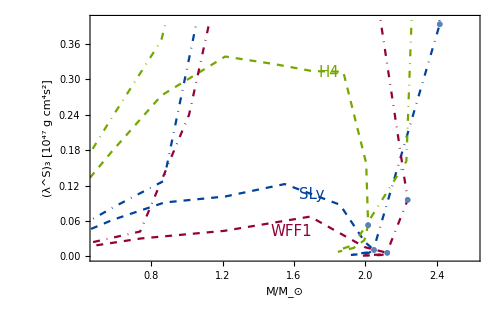

```mathematica
Show[{Table[ListLinePlot[Table[{massradADMT[[p]][[β]][[1]][[All,2]][[h]],((MultipoleScalarNoETl3[[p]][[β]][[1]])/TidalScalarNoETl3[[p]][[β]][[1]])[[h]]*(msunincm)^7 Gconst^-1(10^-47)},{h,1,Length[ρvals]}],PlotStyle->{StyleList[[β]],ColorList[[p]]},PlotRange->{{0.5,2.6},{0,0.4}},If[p==3,PlotLegends->Placed[LineLegend[{StyleList[[β]]},{Style[βnamesList[[β]],15]}],{Right,Bottom}],PlotLegends->Automatic],Epilog->{Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.57,0.15}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.6,0.3}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.64,0.80}],{1,1}]},Frame->True,FrameLabel->{{Style["(λ^S)_3 [10^47 g cm^4s^2]","Latin Modern Roman",19,Black],None},{Style["M/M_⊙","Latin Modern Roman",18,Black],Style["Einstein frame φ_∞=10^-3","Latin Modern Roman",18,Black]}},FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},ImageSize->500],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}],Table[ListPlot[{{massradADMT[[p]][[1]][[1]][[All,2]][[MaxPointsSTEinstIndex[[p]][[1]][[1]]]],((MultipoleScalarNoETl3[[p]][[1]][[1]])/TidalScalarNoETl3[[p]][[1]][[1]])[[MaxPointsSTEinstIndex[[p]][[1]][[1]]]]*(msunincm)^7 Gconst^-1(10^-47)}},PlotMarkers->Style["x",{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]}],Table[ListPlot[{{massradADMT[[p]][[2]][[1]][[All,2]][[MaxPointsSTEinstIndex[[p]][[2]][[1]]]],((MultipoleScalarNoETl3[[p]][[2]][[1]])/TidalScalarNoETl3[[p]][[2]][[1]])[[MaxPointsSTEinstIndex[[p]][[2]][[1]]]]*(msunincm)^7 Gconst^-1(10^-47)}},PlotMarkers->Style["o",{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]}]}//Flatten]
```

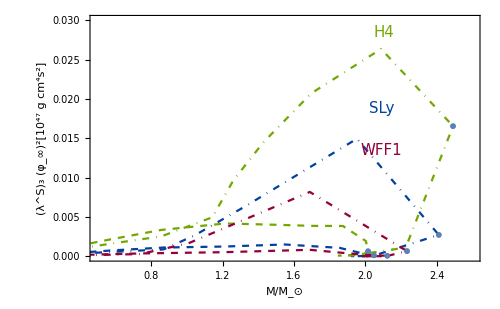

```mathematica
Show[{Table[ListLinePlot[Table[{massradJordT[[p]][[β]][[1]][[All,2]][[h]],((MultipoleScalarNoETl3[[p]][[β]][[1]])/TidalScalarNoETl3[[p]][[β]][[1]])[[h]]*((ⅇ^(βvals[[β]] φinfvals[[1]]^2))/(2(-βvals[[β]])))^2(msunincm)^7 Gconst^-1(10^-47)},{h,1,Length[ρvals]}],PlotStyle->{StyleList[[β]],ColorList[[p]]},PlotRange->{{0.5,2.6},{0,0.03}},If[p==3,PlotLegends->Placed[LineLegend[{StyleList[[β]]},{Style[βnamesList[[β]],15]}],{Left,Top}],PlotLegends->Automatic],Epilog->{Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.8,0.48}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.78,0.65}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.78,0.96}],{1,1}]},Frame->True,FrameLabel->{{Style["(λ^S)_3 (φ_∞)^2[10^47 g cm^4s^2]","Latin Modern Roman",19,Black],None},{Style["M/M_⊙","Latin Modern Roman",18,Black],Style["Jordan frame φ_∞=10^-3","Latin Modern Roman",18,Black]}},FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},ImageSize->500],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}],Table[ListPlot[{{massradJordT[[p]][[1]][[1]][[All,2]][[MaxPointsSTJordIndex[[p]][[1]][[1]]]],((MultipoleScalarNoETl3[[p]][[1]][[1]])/TidalScalarNoETl3[[p]][[1]][[1]])[[MaxPointsSTJordIndex[[p]][[1]][[1]]]]((ⅇ^(βvals[[1]] φinfvals[[1]]^2))/(2(-βvals[[1]])))^2(msunincm)^7 Gconst^-1(10^-47)}},PlotMarkers->Style["x",{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]}],Table[ListPlot[{{massradJordT[[p]][[2]][[1]][[All,2]][[MaxPointsSTJordIndex[[p]][[2]][[1]]]],((MultipoleScalarNoETl3[[p]][[2]][[1]])/TidalScalarNoETl3[[p]][[2]][[1]])[[MaxPointsSTJordIndex[[p]][[2]][[1]]]]((ⅇ^(βvals[[2]] φinfvals[[1]]^2))/(2(-βvals[[2]])))^2(msunincm)^7 Gconst^-1(10^-47)}},PlotMarkers->Style["o",{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]}]}//Flatten]
```

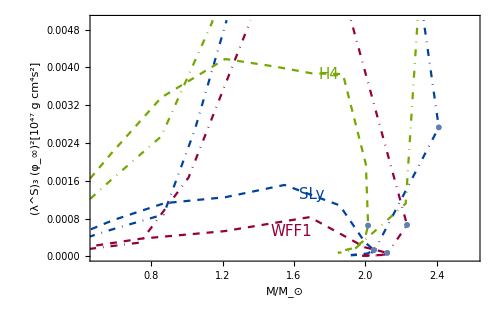

```mathematica
Show[{Table[ListLinePlot[Table[{massradJordT[[p]][[β]][[1]][[All,2]][[h]],((MultipoleScalarNoETl3[[p]][[β]][[1]])/TidalScalarNoETl3[[p]][[β]][[1]])[[h]]*((ⅇ^(βvals[[β]] φinfvals[[1]]^2))/(2(-βvals[[β]])))^2(msunincm)^7 Gconst^-1(10^-47)},{h,1,Length[ρvals]}],PlotStyle->{StyleList[[β]],ColorList[[p]]},PlotRange->{{0.5,2.6},{0,0.005}},If[p==3,PlotLegends->Placed[LineLegend[{StyleList[[β]]},{Style[βnamesList[[β]],15]}],{Left,Top}],PlotLegends->Automatic],Epilog->{Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.57,0.15}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.6,0.3}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.64,0.79}],{1,1}]},Frame->True,FrameLabel->{{Style["(λ^S)_3 (φ_∞)^2[10^47 g cm^4s^2]","Latin Modern Roman",19,Black],None},{Style["M/M_⊙","Latin Modern Roman",18,Black],Style["Jordan frame φ_∞=10^-3","Latin Modern Roman",18,Black]}},FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},ImageSize->500],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}],Table[ListPlot[{{massradJordT[[p]][[1]][[1]][[All,2]][[MaxPointsSTJordIndex[[p]][[1]][[1]]]],((MultipoleScalarNoETl3[[p]][[1]][[1]])/TidalScalarNoETl3[[p]][[1]][[1]])[[MaxPointsSTJordIndex[[p]][[1]][[1]]]]((ⅇ^(βvals[[1]] φinfvals[[1]]^2))/(2(-βvals[[1]])))^2(msunincm)^7 Gconst^-1(10^-47)}},PlotMarkers->Style["x",{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]}],Table[ListPlot[{{massradJordT[[p]][[2]][[1]][[All,2]][[MaxPointsSTJordIndex[[p]][[2]][[1]]]],((MultipoleScalarNoETl3[[p]][[2]][[1]])/TidalScalarNoETl3[[p]][[2]][[1]])[[MaxPointsSTJordIndex[[p]][[2]][[1]]]]((ⅇ^(βvals[[2]] φinfvals[[1]]^2))/(2(-βvals[[2]])))^2(msunincm)^7 Gconst^-1(10^-47)}},PlotMarkers->Style["o",{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]}]}//Flatten]
```

```mathematica
(* Scalar-Tensor *)
```

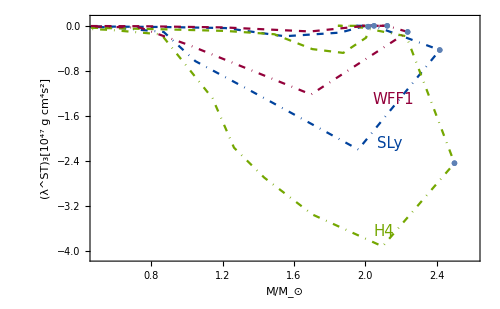

```mathematica
Show[{Table[ListLinePlot[Table[{massradADMT[[p]][[β]][[1]][[All,2]][[h]],((MultipoleScalarNoESl3[[p]][[β]][[1]])/TidalTensorNoESl3[[p]][[β]][[1]])[[h]](msunincm)^7 Gconst^-1(10^-47)},{h,1,Length[ρvals]}],PlotStyle->{StyleList[[β]],ColorList[[p]]},PlotRange->{{0.5,2.6},{0.1,-4.1}},If[p==3,PlotLegends->Placed[LineLegend[{StyleList[[β]]},{Style[βnamesList[[β]],15]}],{Left,Bottom}],PlotLegends->Automatic],Epilog->{Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.83,0.69}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.8,0.51}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.78,0.15}],{1,1}]},Frame->True,FrameLabel->{{Style["(λ^ST)_3[10^47 g cm^4s^2]","Latin Modern Roman",19,Black],None},{Style["M/M_⊙","Latin Modern Roman",18,Black],Style["Einstein frame φ_∞=10^-3","Latin Modern Roman",18,Black]}},FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},ImageSize->500],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}],Table[ListPlot[{{massradADMT[[p]][[1]][[1]][[All,2]][[MaxPointsSTEinstIndex[[p]][[1]][[1]]]],((MultipoleScalarNoESl3[[p]][[1]][[1]])/TidalTensorNoESl3[[p]][[1]][[1]])[[MaxPointsSTEinstIndex[[p]][[1]][[1]]]]*(msunincm)^7 Gconst^-1(10^-47)}},PlotMarkers->Style["x",{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]}],Table[ListPlot[{{massradADMT[[p]][[2]][[1]][[All,2]][[MaxPointsSTEinstIndex[[p]][[2]][[1]]]],((MultipoleScalarNoESl3[[p]][[2]][[1]])/TidalTensorNoESl3[[p]][[2]][[1]])[[MaxPointsSTEinstIndex[[p]][[2]][[1]]]]*(msunincm)^7 Gconst^-1(10^-47)}},PlotMarkers->Style["o",{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]}]}//Flatten]
```

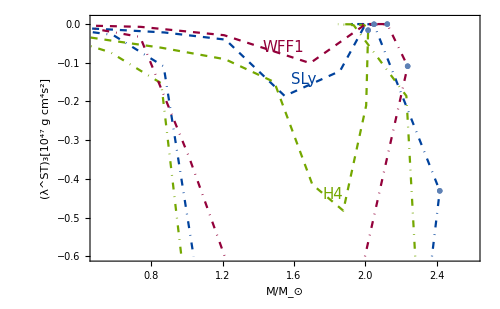

```mathematica
Show[{Table[ListLinePlot[Table[{massradADMT[[p]][[β]][[1]][[All,2]][[h]],((MultipoleScalarNoESl3[[p]][[β]][[1]])/TidalTensorNoESl3[[p]][[β]][[1]])[[h]](msunincm)^7 Gconst^-1(10^-47)},{h,1,Length[ρvals]}],PlotStyle->{StyleList[[β]],ColorList[[p]]},PlotRange->{{0.5,2.6},{0.01,-0.6}},If[p==3,PlotLegends->Placed[LineLegend[{StyleList[[β]]},{Style[βnamesList[[β]],15]}],{Left,Bottom}],PlotLegends->Automatic],Epilog->{Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.55,0.9}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.58,0.77}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.65,0.3}],{1,1}]},Frame->True,FrameLabel->{{Style["(λ^ST)_3[10^47 g cm^4s^2]","Latin Modern Roman",19,Black],None},{Style["M/M_⊙","Latin Modern Roman",18,Black],Style["Einstein frame φ_∞=10^-3","Latin Modern Roman",18,Black]}},FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},ImageSize->500],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}],Table[ListPlot[{{massradADMT[[p]][[1]][[1]][[All,2]][[MaxPointsSTEinstIndex[[p]][[1]][[1]]]],((MultipoleScalarNoESl3[[p]][[1]][[1]])/TidalTensorNoESl3[[p]][[1]][[1]])[[MaxPointsSTEinstIndex[[p]][[1]][[1]]]]*(msunincm)^7 Gconst^-1(10^-47)}},PlotMarkers->Style["x",{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]}],Table[ListPlot[{{massradADMT[[p]][[2]][[1]][[All,2]][[MaxPointsSTEinstIndex[[p]][[2]][[1]]]],((MultipoleScalarNoESl3[[p]][[2]][[1]])/TidalTensorNoESl3[[p]][[2]][[1]])[[MaxPointsSTEinstIndex[[p]][[2]][[1]]]]*(msunincm)^7 Gconst^-1(10^-47)}},PlotMarkers->Style["o",{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]}]}//Flatten]
```

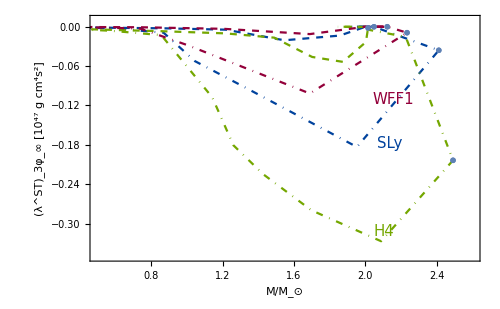

```mathematica
Show[{Table[ListLinePlot[Table[{massradJordT[[p]][[β]][[1]][[All,2]][[h]],((MultipoleScalarNoESl3[[p]][[β]][[1]])/TidalTensorNoESl3[[p]][[β]][[1]])[[h]]*((ⅇ^(βvals[[β]] φinfvals[[1]]^2))/(2(-βvals[[β]])))(msunincm)^7 Gconst^-1(10^-47)},{h,1,Length[ρvals]}],PlotStyle->{StyleList[[β]],ColorList[[p]]},PlotRange->{{0.5,2.6},{0.01,-0.35}},If[p==3,PlotLegends->Placed[LineLegend[{StyleList[[β]]},{Style[βnamesList[[β]],15]}],{Left,Bottom}],PlotLegends->Automatic],Epilog->{Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.83,0.69}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.8,0.51}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.78,0.15}],{1,1}]},Frame->True,FrameLabel->{{Style["(λ^ST)_3φ_∞ [10^47 g cm^4s^2]","Latin Modern Roman",19,Black],None},{Style["M/M_⊙","Latin Modern Roman",18,Black],Style["Jordan frame φ_∞=10^-3","Latin Modern Roman",18,Black]}},FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},ImageSize->500],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}],Table[ListPlot[{{massradJordT[[p]][[1]][[1]][[All,2]][[MaxPointsSTJordIndex[[p]][[1]][[1]]]],((MultipoleScalarNoESl3[[p]][[1]][[1]])/TidalTensorNoESl3[[p]][[1]][[1]])[[MaxPointsSTJordIndex[[p]][[1]][[1]]]]((ⅇ^(βvals[[1]] φinfvals[[1]]^2))/(2(-βvals[[1]])))(msunincm)^7 Gconst^-1(10^-47)}},PlotMarkers->Style["x",{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]}],Table[ListPlot[{{massradJordT[[p]][[2]][[1]][[All,2]][[MaxPointsSTJordIndex[[p]][[2]][[1]]]],((MultipoleScalarNoESl3[[p]][[2]][[1]])/TidalTensorNoESl3[[p]][[2]][[1]])[[MaxPointsSTJordIndex[[p]][[2]][[1]]]]((ⅇ^(βvals[[2]] φinfvals[[1]]^2))/(2(-βvals[[2]])))(msunincm)^7 Gconst^-1(10^-47)}},PlotMarkers->Style["o",{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]}]}//Flatten]
```

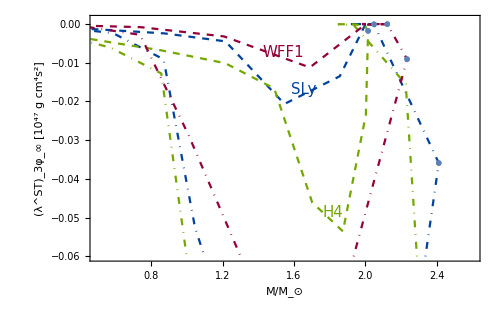

```mathematica
Show[{Table[ListLinePlot[Table[{massradJordT[[p]][[β]][[1]][[All,2]][[h]],((MultipoleScalarNoESl3[[p]][[β]][[1]])/TidalTensorNoESl3[[p]][[β]][[1]])[[h]]*((ⅇ^(βvals[[β]] φinfvals[[1]]^2))/(2(-βvals[[β]])))(msunincm)^7 Gconst^-1(10^-47)},{h,1,Length[ρvals]}],PlotStyle->{StyleList[[β]],ColorList[[p]]},PlotRange->{{0.5,2.6},{0.001,-0.06}},If[p==3,PlotLegends->Placed[LineLegend[{StyleList[[β]]},{Style[βnamesList[[β]],15]}],{Left,Bottom}],PlotLegends->Automatic],Epilog->{Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.55,0.88}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.58,0.73}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.65,0.23}],{1,1}]},Frame->True,FrameLabel->{{Style["(λ^ST)_3φ_∞ [10^47 g cm^4s^2]","Latin Modern Roman",19,Black],None},{Style["M/M_⊙","Latin Modern Roman",18,Black],Style["Jordan frame φ_∞=10^-3","Latin Modern Roman",18,Black]}},FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},ImageSize->500],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}],Table[ListPlot[{{massradJordT[[p]][[1]][[1]][[All,2]][[MaxPointsSTJordIndex[[p]][[1]][[1]]]],((MultipoleScalarNoESl3[[p]][[1]][[1]])/TidalTensorNoESl3[[p]][[1]][[1]])[[MaxPointsSTJordIndex[[p]][[1]][[1]]]]((ⅇ^(βvals[[1]] φinfvals[[1]]^2))/(2(-βvals[[1]])))(msunincm)^7 Gconst^-1(10^-47)}},PlotMarkers->Style["x",{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]}],Table[ListPlot[{{massradJordT[[p]][[2]][[1]][[All,2]][[MaxPointsSTJordIndex[[p]][[2]][[1]]]],((MultipoleScalarNoESl3[[p]][[2]][[1]])/TidalTensorNoESl3[[p]][[2]][[1]])[[MaxPointsSTJordIndex[[p]][[2]][[1]]]]((ⅇ^(βvals[[2]] φinfvals[[1]]^2))/(2(-βvals[[2]])))(msunincm)^7 Gconst^-1(10^-47)}},PlotMarkers->Style["o",{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]}]}//Flatten]
```

#### Plots of k_l

```mathematica
(* l=1 *)
```

```mathematica
(* Scalar *)
```

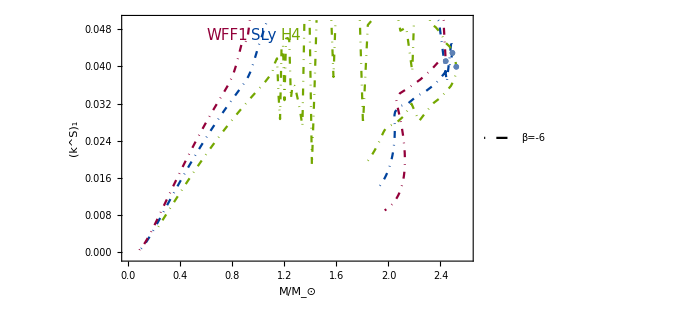

```mathematica
Show[{Table[ListLinePlot[Table[{massradADMT[[p]][[β]][[1]][[All,2]][[h]],1/2((MultipoleScalarNoETl1[[p]][[β]][[1]]-1/2 ChargeTableT[[p]][[β]][[1]][[All,2]]MultipoleTensorNoETl1[[p]][[β]][[1]])/TidalScalarNoETl1[[p]][[β]][[1]])[[h]](massradADMT[[p]][[β]][[1]][[All,1]][[h]]*km)^-3},{h,1,Length[ρvals]}],PlotStyle->{StyleList[[β]],ColorList[[p]]},PlotRange->{{0,2.6},{-0.001,0.05}},If[p==3,PlotLegends->Placed[LineLegend[{StyleList[[β]]},{Style[βnamesList[[β]],15]}],{Left,Top}],PlotLegends->Automatic],Epilog->{Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.36,0.95}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.44,0.95}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.51,0.95}],{1,1}]},Frame->True,FrameLabel->{{Style["(k^S)_1","Latin Modern Roman",19,Black],None},{Style["M/M_⊙","Latin Modern Roman",18,Black],Style["Einstein frame φ_∞=10^-3","Latin Modern Roman",18,Black]}},FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},ImageSize->500],{p,1,Length[EoSIndex]},{β,{2}}],Table[ListPlot[{{massradADMT[[p]][[2]][[1]][[All,2]][[MaxPointsSTEinstIndex[[p]][[2]][[1]]]],1/2((MultipoleScalarNoETl1[[p]][[2]][[1]]-1/2 ChargeTableT[[p]][[2]][[1]][[All,2]]MultipoleTensorNoETl1[[p]][[2]][[1]])/TidalScalarNoETl1[[p]][[2]][[1]])[[MaxPointsSTEinstIndex[[p]][[2]][[1]]]](massradADMT[[p]][[2]][[1]][[All,1]][[MaxPointsSTEinstIndex[[p]][[2]][[1]]]]*km)^-3}},PlotMarkers->Style["o",{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]}]}//Flatten]
```

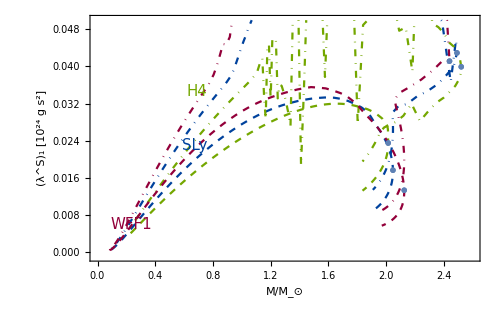

```mathematica
Show[{Table[ListLinePlot[Table[{massradADMT[[p]][[β]][[1]][[All,2]][[h]],1/2((MultipoleScalarNoETl1[[p]][[β]][[1]]-1/2 ChargeTableT[[p]][[β]][[1]][[All,2]]MultipoleTensorNoETl1[[p]][[β]][[1]])/TidalScalarNoETl1[[p]][[β]][[1]])[[h]](massradADMT[[p]][[β]][[1]][[All,1]][[h]]*km)^-3},{h,1,Length[ρvals]}],PlotRange->{{0,2.6},{-0.001,0.05}},PlotStyle->{StyleList[[β]],ColorList[[p]]},If[p==3,PlotLegends->Placed[LineLegend[{StyleList[[β]]},{Style[βnamesList[[β]],15]}],{Right,Top}],PlotLegends->Automatic],Epilog->{Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.16,0.18}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.3,0.5}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.3,0.72}],{1,1}]},Frame->True,FrameLabel->{{Style["(λ^S)_1 [10^24 g s^2]","Latin Modern Roman",19,Black],None},{Style["M/M_⊙","Latin Modern Roman",18,Black],Style["Einstein frame φ_∞=10^-3","Latin Modern Roman",18,Black]}},FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},ImageSize->500],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}],Table[ListPlot[{{massradADMT[[p]][[β]][[1]][[All,2]][[MaxPointsSTEinstIndex[[p]][[β]][[1]]]],1/2((MultipoleScalarNoETl1[[p]][[β]][[1]]-1/2 ChargeTableT[[p]][[β]][[1]][[All,2]]MultipoleTensorNoETl1[[p]][[β]][[1]])/TidalScalarNoETl1[[p]][[β]][[1]])[[MaxPointsSTEinstIndex[[p]][[β]][[1]]]]*(massradADMT[[p]][[β]][[1]][[All,1]][[MaxPointsSTEinstIndex[[p]][[β]][[1]]]]*km)^-3}},PlotMarkers->Style[{"x","o"}[[β]],{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}]}//Flatten]
```

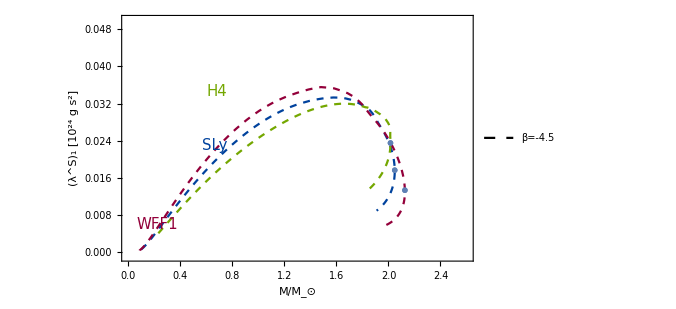

```mathematica
Show[{Table[ListLinePlot[Table[{massradADMT[[p]][[β]][[1]][[All,2]][[h]],1/2((MultipoleScalarNoETl1[[p]][[β]][[1]]-1/2 ChargeTableT[[p]][[β]][[1]][[All,2]]MultipoleTensorNoETl1[[p]][[β]][[1]])/TidalScalarNoETl1[[p]][[β]][[1]])[[h]](massradADMT[[p]][[β]][[1]][[All,1]][[h]]*km)^-3},{h,1,Length[ρvals]}],PlotRange->{{0,2.6},{-0.001,0.05}},PlotStyle->{StyleList[[β]],ColorList[[p]]},If[p==3,PlotLegends->Placed[LineLegend[{StyleList[[β]]},{Style[βnamesList[[β]],15]}],{Right,Top}],PlotLegends->Automatic],Epilog->{Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.16,0.18}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.3,0.5}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.3,0.72}],{1,1}]},Frame->True,FrameLabel->{{Style["(λ^S)_1 [10^24 g s^2]","Latin Modern Roman",19,Black],None},{Style["M/M_⊙","Latin Modern Roman",18,Black],Style["Einstein frame φ_∞=10^-3","Latin Modern Roman",18,Black]}},FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},ImageSize->500],{p,1,Length[EoSIndex]},{β,1,1}],Table[ListPlot[{{massradADMT[[p]][[β]][[1]][[All,2]][[MaxPointsSTEinstIndex[[p]][[β]][[1]]]],1/2((MultipoleScalarNoETl1[[p]][[β]][[1]]-1/2 ChargeTableT[[p]][[β]][[1]][[All,2]]MultipoleTensorNoETl1[[p]][[β]][[1]])/TidalScalarNoETl1[[p]][[β]][[1]])[[MaxPointsSTEinstIndex[[p]][[β]][[1]]]]*(massradADMT[[p]][[β]][[1]][[All,1]][[MaxPointsSTEinstIndex[[p]][[β]][[1]]]]*km)^-3}},PlotMarkers->Style[{"x","o"}[[β]],{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]},{β,1,1}]}//Flatten]
```

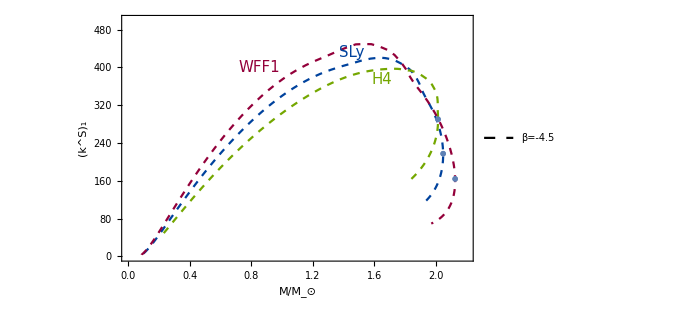

```mathematica
Show[{Table[ListLinePlot[Table[{massradJordT[[p]][[β]][[1]][[All,2]][[h]],Evaluate[(1/(ⅇ^(1/2 βvals[[β]] φ0[massradT[[p]][[β]][[1]][[All,1]][[h]]*km]^2)))^3*(ⅇ^(βvals[[β]] φinfvals[[1]]^2)/(2(-βvals[[β]])φinfvals[[1]]))^2 1/2((MultipoleScalarNoETl1[[p]][[β]][[1]]-1/2 ChargeTableT[[p]][[β]][[1]][[All,2]]MultipoleTensorNoETl1[[p]][[β]][[1]])/TidalScalarNoETl1[[p]][[β]][[1]])[[h]](massradADMT[[p]][[β]][[1]][[All,1]][[h]]*km)^-3/.BackgroundTOVPieceT[[p]][[β]][[1]][[h]]][[1]]},{h,1,Length[ρvals]}],PlotStyle->{StyleList[[β]],ColorList[[p]]},PlotRange->{{0,2.2},{0,500}},If[p==3,PlotLegends->Placed[LineLegend[{StyleList[[β]]},{Style[βnamesList[[β]],15]}],{Left,Top}],PlotLegends->Automatic],Epilog->{Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.45,0.82}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.69,0.88}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.77,0.77}],{1,1}]},Frame->True,FrameLabel->{{Style["(k^S)_1","Latin Modern Roman",19,Black],None},{Style["M/M_⊙","Latin Modern Roman",18,Black],Style["Jordan frame φ_∞=10^-3","Latin Modern Roman",18,Black]}},FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},ImageSize->500],{p,1,Length[EoSIndex]},{β,1,1}],Table[ListPlot[{{massradJordT[[p]][[1]][[1]][[All,2]][[MaxPointsSTJordIndex[[p]][[1]][[1]]]],Evaluate[(1/(ⅇ^(1/2 βvals[[1]] φ0[massradT[[p]][[1]][[1]][[All,1]][[MaxPointsSTJordIndex[[p]][[1]][[1]]]]*km]^2)))^3*(ⅇ^(βvals[[1]] φinfvals[[1]]^2)/(2(-βvals[[1]])φinfvals[[1]]))^2 1/2((MultipoleScalarNoETl1[[p]][[1]][[1]]-1/2 ChargeTableT[[p]][[1]][[1]][[All,2]]MultipoleTensorNoETl1[[p]][[1]][[1]])/TidalScalarNoETl1[[p]][[1]][[1]])[[MaxPointsSTJordIndex[[p]][[1]][[1]]]](massradADMT[[p]][[1]][[1]][[All,1]][[MaxPointsSTJordIndex[[p]][[1]][[1]]]]*km)^-3/.BackgroundTOVPieceT[[p]][[1]][[1]][[MaxPointsSTJordIndex[[p]][[1]][[1]]]]][[1]]}},PlotMarkers->Style["x",{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]}]}//Flatten]
```

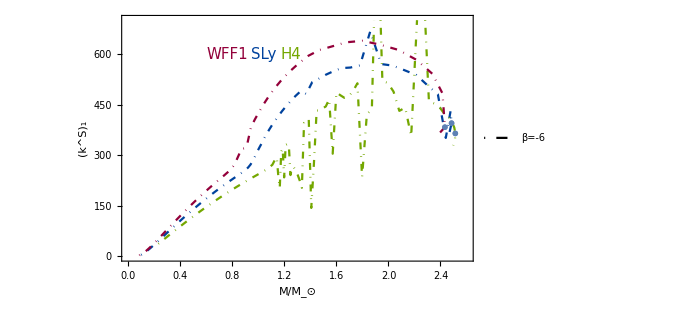

```mathematica
Show[{Table[ListLinePlot[Drop[Table[{massradJordT[[p]][[β]][[1]][[All,2]][[h]],Evaluate[(1/(ⅇ^(1/2 βvals[[β]] φ0[massradT[[p]][[β]][[1]][[All,1]][[h]]*km]^2)))^3*(ⅇ^(βvals[[β]] φinfvals[[1]]^2)/(2(-βvals[[β]])φinfvals[[1]]))^2 1/2((MultipoleScalarNoETl1[[p]][[β]][[1]]-1/2 ChargeTableT[[p]][[β]][[1]][[All,2]]MultipoleTensorNoETl1[[p]][[β]][[1]])/TidalScalarNoETl1[[p]][[β]][[1]])[[h]](massradADMT[[p]][[β]][[1]][[All,1]][[h]]*km)^-3/.BackgroundTOVPieceT[[p]][[β]][[1]][[h]]][[1]]},{h,1,Length[ρvals]}],Dropvals[[p]]],PlotStyle->{StyleList[[β]],ColorList[[p]]},PlotRange->{{0,2.6},{0,700}},If[p==3,PlotLegends->Placed[LineLegend[{StyleList[[β]]},{Style[βnamesList[[β]],15]}],{Left,Top}],PlotLegends->Automatic],Epilog->{Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.36,0.87}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.44,0.87}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.51,0.87}],{1,1}]},Frame->True,FrameLabel->{{Style["(k^S)_1","Latin Modern Roman",19,Black],None},{Style["M/M_⊙","Latin Modern Roman",18,Black],Style["Jordan frame φ_∞=10^-3","Latin Modern Roman",18,Black]}},FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},ImageSize->500],{p,1,Length[EoSIndex]},{β,{2}}],Table[ListPlot[{{massradJordT[[p]][[2]][[1]][[All,2]][[MaxPointsSTJordIndex[[p]][[2]][[1]]]],Evaluate[(1/(ⅇ^(1/2 βvals[[2]] φ0[massradT[[p]][[2]][[1]][[All,1]][[MaxPointsSTJordIndex[[p]][[2]][[1]]]]*km]^2)))^3*(ⅇ^(βvals[[2]] φinfvals[[1]]^2)/(2(-βvals[[2]])φinfvals[[1]]))^2 1/2((MultipoleScalarNoETl1[[p]][[2]][[1]]-1/2 ChargeTableT[[p]][[2]][[1]][[All,2]]MultipoleTensorNoETl1[[p]][[2]][[1]])/TidalScalarNoETl1[[p]][[2]][[1]])[[MaxPointsSTJordIndex[[p]][[2]][[1]]]](massradADMT[[p]][[2]][[1]][[All,1]][[MaxPointsSTJordIndex[[p]][[2]][[1]]]]*km)^-3/.BackgroundTOVPieceT[[p]][[2]][[1]][[MaxPointsSTJordIndex[[p]][[2]][[1]]]]][[1]]}},PlotMarkers->Style["o",{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]}]}//Flatten]
```

```mathematica
(* l=2 *)
```

```mathematica
(* Tensor *)
```

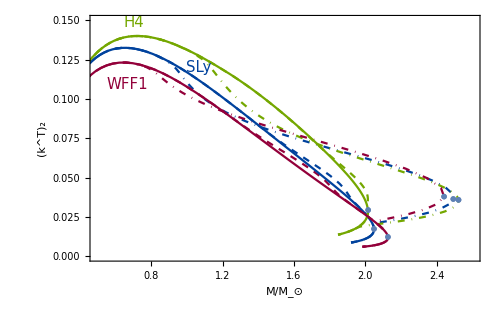

```mathematica
Show[{Table[ListLinePlot[Table[{massradADMT[[p]][[β]][[1]][[All,2]][[h]],3/2((MultipoleTensorNoES[[p]][[β]][[1]])/TidalTensorNoES[[p]][[β]][[1]])[[h]](massradADMT[[p]][[β]][[1]][[All,1]][[h]]*km)^-5},{h,1,Length[ρvals]}],PlotStyle->{StyleList[[β]],ColorList[[p]]},PlotRange->{{0.5,2.6},{0,0.15}},If[p==3,PlotLegends->Placed[LineLegend[{StyleList[[β]]},{Style[βnamesList[[β]],15]}],{Right,Top}],PlotLegends->Automatic],Epilog->{Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.15,0.75}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.31,0.82}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.14,1}],{1,1}]},Frame->True,FrameLabel->{{Style["(k^T)_2","Latin Modern Roman",19,Black],None},{Style["M/M_⊙","Latin Modern Roman",18,Black],Style["Einstein frame φ_∞=10^-3","Latin Modern Roman",18,Black]}},FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},ImageSize->500],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}],Table[ListLinePlot[Table[{massradGRT[[p]][[1]][[1]][[All,2]][[h]],3/2((MultipoleTensorNoESGR[[p]])/TidalTensorNoESGR[[p]])[[h]](massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km)^-5},{h,1,Length[ρvals]}],PlotStyle->{ColorList[[p]]},ImageSize->500],{p,1,Length[EoSIndex]}],Table[ListPlot[{{massradADMT[[p]][[β]][[1]][[All,2]][[MaxPointsSTEinstIndex[[p]][[β]][[1]]]],3/2((MultipoleTensorNoES[[p]][[β]][[1]])/TidalTensorNoES[[p]][[β]][[1]])[[MaxPointsSTEinstIndex[[p]][[β]][[1]]]](massradADMT[[p]][[β]][[1]][[All,1]][[MaxPointsSTEinstIndex[[p]][[β]][[1]]]]*km)^-5}},PlotMarkers->Style[{"x","o"}[[β]],{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}]}//Flatten]
```

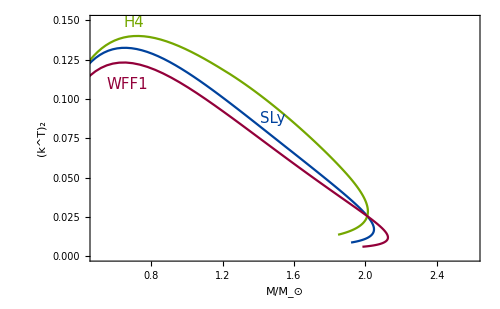

```mathematica
Show[{Table[ListLinePlot[Table[{massradJordT[[p]][[β]][[1]][[All,2]][[h]],Evaluate[(1/(ⅇ^(1/2 βvals[[β]] φ0[massradT[[p]][[β]][[1]][[All,1]][[h]]*km]^2)))^5 3/2((MultipoleTensorNoES[[p]][[β]][[1]])/TidalTensorNoES[[p]][[β]][[1]])[[h]](massradADMT[[p]][[β]][[1]][[All,1]][[h]]*km)^-5/.BackgroundTOVPieceT[[p]][[β]][[1]][[h]]][[1]]},{h,1,Length[ρvals]}],PlotStyle->{StyleList[[β]],ColorList[[p]]},PlotRange->{{0.5,2.6},{0,0.15}},If[p==3,PlotLegends->Placed[LineLegend[{StyleList[[β]]},{Style[βnamesList[[β]],15]}],{Right,Top}],PlotLegends->Automatic],Epilog->{Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.15,0.75}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.5,0.61}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.14,1}],{1,1}]},Frame->True,FrameLabel->{{Style["(k^T)_2","Latin Modern Roman",19,Black],None},{Style["M/M_⊙","Latin Modern Roman",18,Black],Style["Jordan frame φ_∞=10^-3","Latin Modern Roman",18,Black]}},FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},ImageSize->500],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}],Table[ListLinePlot[Table[{massradGRT[[p]][[1]][[1]][[All,2]][[h]],3/2((MultipoleTensorNoESGR[[p]])/TidalTensorNoESGR[[p]])[[h]](massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km)^-5},{h,1,Length[ρvals]}],PlotStyle->{ColorList[[p]]},ImageSize->500],{p,1,Length[EoSIndex]}],Table[ListPlot[{{massradJordT[[p]][[1]][[1]][[All,2]][[MaxPointsSTJordIndex[[p]][[1]][[1]]]],Evaluate[(1/(ⅇ^(1/2 βvals[[1]] φ0[massradT[[p]][[1]][[1]][[All,1]][[MaxPointsSTJordIndex[[p]][[1]][[1]]]]*km]^2)))^5 3/2((MultipoleTensorNoES[[p]][[1]][[1]])/TidalTensorNoES[[p]][[1]][[1]])[[MaxPointsSTJordIndex[[p]][[1]][[1]]]](massradADMT[[p]][[1]][[1]][[All,1]][[MaxPointsSTJordIndex[[p]][[1]][[1]]]]*km)^-5/.BackgroundTOVPieceT[[p]][[1]][[1]][[MaxPointsSTJordIndex[[p]][[1]][[1]]]]][[1]]}},PlotMarkers->Style["x",{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]}],Table[ListPlot[{{massradJordT[[p]][[2]][[1]][[All,2]][[MaxPointsSTJordIndex[[p]][[2]][[1]]]],Evaluate[(1/(ⅇ^(1/2 βvals[[2]] φ0[massradT[[p]][[2]][[1]][[All,1]][[MaxPointsSTJordIndex[[p]][[2]][[1]]]]*km]^2)))^5 3/2((MultipoleTensorNoES[[p]][[2]][[1]])/TidalTensorNoES[[p]][[2]][[1]])[[MaxPointsSTJordIndex[[p]][[2]][[1]]]](massradADMT[[p]][[2]][[1]][[All,1]][[MaxPointsSTJordIndex[[p]][[2]][[1]]]]*km)^-5/.BackgroundTOVPieceT[[p]][[2]][[1]][[MaxPointsSTJordIndex[[p]][[2]][[1]]]]][[1]]}},PlotMarkers->Style["o",{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]}]}//Flatten]
```

```mathematica
(* Scalar *)
```

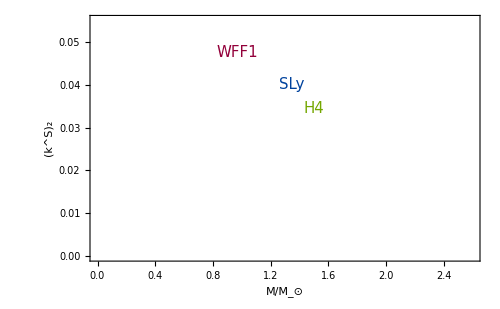

```mathematica
Show[{Table[ListLinePlot[Table[{massradADMT[[p]][[β]][[1]][[All,2]][[h]],3/2((MultipoleScalarNoET[[p]][[β]][[1]])/TidalScalarNoET[[p]][[β]][[1]])[[h]](massradADMT[[p]][[β]][[1]][[All,1]][[h]]*km)^-5},{h,1,Length[ρvals]}],PlotStyle->{StyleList[[β]],ColorList[[p]]},PlotRange->{{0,2.6},{0,0.055}},If[p==3,PlotLegends->Placed[LineLegend[{StyleList[[β]]},{Style[βnamesList[[β]],15]}],{Left,Top}],PlotLegends->Automatic],Epilog->{Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.43,0.88}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.55,0.75}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.6,0.65}],{1,1}]},Frame->True,FrameLabel->{{Style["(k^S)_2","Latin Modern Roman",19,Black],None},{Style["M/M_⊙","Latin Modern Roman",18,Black],Style["Einstein frame φ_∞=10^-3","Latin Modern Roman",18,Black]}},FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},ImageSize->500],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}],Table[ListPlot[{{massradADMT[[p]][[β]][[1]][[All,2]][[MaxPointsSTEinstIndex[[p]][[β]][[1]]]],3/2((MultipoleScalarNoET[[p]][[β]][[1]])/TidalScalarNoET[[p]][[β]][[1]])[[MaxPointsSTEinstIndex[[p]][[β]][[1]]]](massradADMT[[p]][[β]][[1]][[All,1]][[MaxPointsSTEinstIndex[[p]][[β]][[1]]]]*km)^-5}},PlotMarkers->Style[{"x","o"}[[β]],{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}]}//Flatten]
```

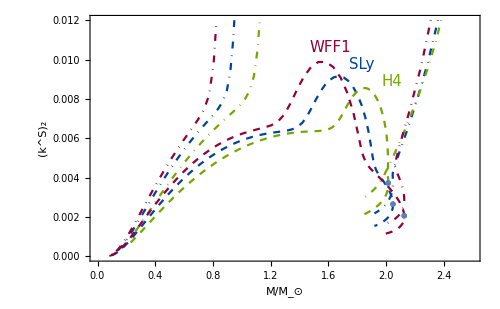

```mathematica
Show[{Table[ListLinePlot[Table[{massradADMT[[p]][[β]][[1]][[All,2]][[h]],3/2((MultipoleScalarNoET[[p]][[β]][[1]])/TidalScalarNoET[[p]][[β]][[1]])[[h]](massradADMT[[p]][[β]][[1]][[All,1]][[h]]*km)^-5},{h,1,Length[ρvals]}],PlotStyle->{StyleList[[β]],ColorList[[p]]},PlotRange->{{0,2.6},{0,0.012}},If[p==3,PlotLegends->Placed[LineLegend[{StyleList[[β]]},{Style[βnamesList[[β]],15]}],{Left,Top}],PlotLegends->Automatic],Epilog->{Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.67,0.9}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.73,0.83}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.8,0.76}],{1,1}]},Frame->True,FrameLabel->{{Style["(k^S)_2","Latin Modern Roman",19,Black],None},{Style["M/M_⊙","Latin Modern Roman",18,Black],Style["Einstein frame φ_∞=10^-3","Latin Modern Roman",18,Black]}},FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},ImageSize->500],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}],Table[ListPlot[{{massradADMT[[p]][[β]][[1]][[All,2]][[MaxPointsSTEinstIndex[[p]][[β]][[1]]]],3/2((MultipoleScalarNoET[[p]][[β]][[1]])/TidalScalarNoET[[p]][[β]][[1]])[[MaxPointsSTEinstIndex[[p]][[β]][[1]]]](massradADMT[[p]][[β]][[1]][[All,1]][[MaxPointsSTEinstIndex[[p]][[β]][[1]]]]*km)^-5}},PlotMarkers->Style[{"x","o"}[[β]],{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}]}//Flatten]
```

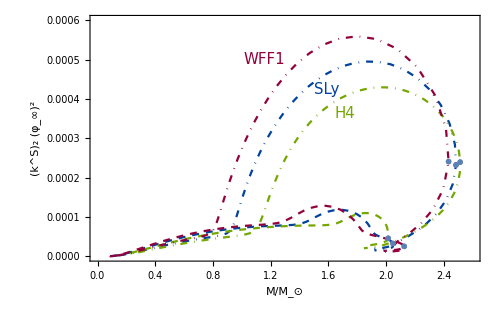

```mathematica
Show[{Table[ListLinePlot[Table[{massradJordT[[p]][[β]][[1]][[All,2]][[h]],Evaluate[(1/(ⅇ^(1/2 βvals[[β]] φ0[massradT[[p]][[β]][[1]][[All,1]][[h]]*km]^2)))^5*((ⅇ^(βvals[[β]] φinfvals[[1]]^2))/(2(-βvals[[β]])))^2 3/2((MultipoleScalarNoET[[p]][[β]][[1]])/TidalScalarNoET[[p]][[β]][[1]])[[h]](massradADMT[[p]][[β]][[1]][[All,1]][[h]]*km)^-5/.BackgroundTOVPieceT[[p]][[β]][[1]][[h]]][[1]]},{h,1,Length[ρvals]}],PlotStyle->{StyleList[[β]],ColorList[[p]]},PlotRange->{{0,2.6},{0,0.0006}},If[p==3,PlotLegends->Placed[LineLegend[{StyleList[[β]]},{Style[βnamesList[[β]],15]}],{Left,Top}],PlotLegends->Automatic],Epilog->{Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.5,0.85}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.64,0.73}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.68,0.63}],{1,1}]},Frame->True,FrameLabel->{{Style["(k^S)_2 (φ_∞)^2","Latin Modern Roman",19,Black],None},{Style["M/M_⊙","Latin Modern Roman",18,Black],Style["Jordan frame φ_∞=10^-3","Latin Modern Roman",18,Black]}},FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},ImageSize->500],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}],Table[ListPlot[{{massradJordT[[p]][[β]][[1]][[All,2]][[MaxPointsSTJordIndex[[p]][[β]][[1]]]],Evaluate[(1/(ⅇ^(1/2 βvals[[β]] φ0[massradT[[p]][[β]][[1]][[All,1]][[MaxPointsSTJordIndex[[p]][[β]][[1]]]]*km]^2)))^5*((ⅇ^(βvals[[β]] φinfvals[[1]]^2))/(2(-βvals[[β]])))^2 3/2((MultipoleScalarNoET[[p]][[β]][[1]])/TidalScalarNoET[[p]][[β]][[1]])[[MaxPointsSTJordIndex[[p]][[β]][[1]]]](massradADMT[[p]][[β]][[1]][[All,1]][[MaxPointsSTJordIndex[[p]][[β]][[1]]]]*km)^-5/.BackgroundTOVPieceT[[p]][[β]][[1]][[MaxPointsSTJordIndex[[p]][[β]][[1]]]]][[1]]}},PlotMarkers->Style[{"x","o"}[[β]],{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}]}//Flatten]
```

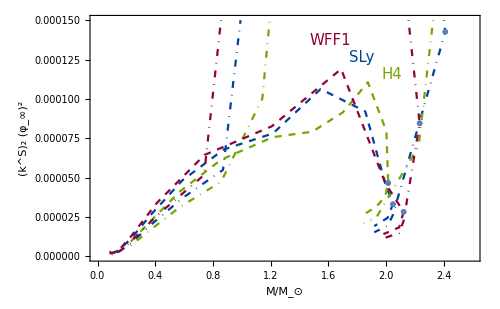

```mathematica
Show[{Table[ListLinePlot[Table[{massradJordT[[p]][[β]][[1]][[All,2]][[h]],Evaluate[(1/(ⅇ^(1/2 βvals[[β]] φ0[massradT[[p]][[β]][[1]][[All,1]][[h]]*km]^2)))^5*((ⅇ^(βvals[[β]] φinfvals[[1]]^2))/(2(-βvals[[β]])))^2 3/2((MultipoleScalarNoET[[p]][[β]][[1]])/TidalScalarNoET[[p]][[β]][[1]])[[h]](massradADMT[[p]][[β]][[1]][[All,1]][[h]]*km)^-5/.BackgroundTOVPieceT[[p]][[β]][[1]][[h]]][[1]]},{h,1,Length[ρvals]}],PlotStyle->{StyleList[[β]],ColorList[[p]]},PlotRange->{{0,2.6},{0,0.00015}},If[p==3,PlotLegends->Placed[LineLegend[{StyleList[[β]]},{Style[βnamesList[[β]],15]}],{Left,Top}],PlotLegends->Automatic],Epilog->{Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.67,0.93}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.73,0.86}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.8,0.79}],{1,1}]},Frame->True,FrameLabel->{{Style["(k^S)_2 (φ_∞)^2","Latin Modern Roman",19,Black],None},{Style["M/M_⊙","Latin Modern Roman",18,Black],Style["Jordan frame φ_∞=10^-3","Latin Modern Roman",18,Black]}},FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},ImageSize->500],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}],Table[ListPlot[{{massradJordT[[p]][[β]][[1]][[All,2]][[MaxPointsSTJordIndex[[p]][[β]][[1]]]],Evaluate[(1/(ⅇ^(1/2 βvals[[β]] φ0[massradT[[p]][[β]][[1]][[All,1]][[MaxPointsSTJordIndex[[p]][[β]][[1]]]]*km]^2)))^5*((ⅇ^(βvals[[β]] φinfvals[[1]]^2))/(2(-βvals[[β]])))^2 3/2((MultipoleScalarNoET[[p]][[β]][[1]])/TidalScalarNoET[[p]][[β]][[1]])[[MaxPointsSTJordIndex[[p]][[β]][[1]]]](massradADMT[[p]][[β]][[1]][[All,1]][[MaxPointsSTJordIndex[[p]][[β]][[1]]]]*km)^-5/.BackgroundTOVPieceT[[p]][[β]][[1]][[MaxPointsSTJordIndex[[p]][[β]][[1]]]]][[1]]}},PlotMarkers->Style[{"x","o"}[[β]],{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}]}//Flatten]
```

```mathematica
(* Scalar-Tensor *)
```

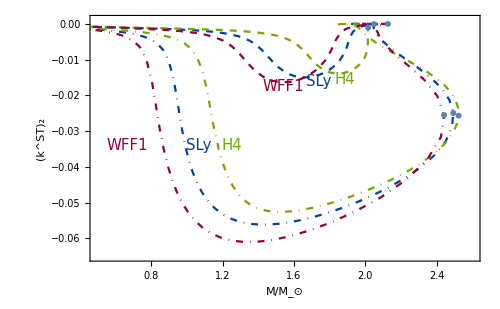

```mathematica
Show[{Table[ListLinePlot[Table[{massradADMT[[p]][[β]][[1]][[All,2]][[h]],3/2((MultipoleScalarNoES[[p]][[β]][[1]])/TidalTensorNoES[[p]][[β]][[1]])[[h]](massradADMT[[p]][[β]][[1]][[All,1]][[h]]*km)^-5},{h,1,Length[ρvals]}],PlotStyle->{StyleList[[β]],ColorList[[p]]},PlotRange->{{0.5,2.6},{0.001,-0.065}},If[p==3,PlotLegends->Placed[LineLegend[{StyleList[[β]]},{Style[βnamesList[[β]],15]}],{Right,Bottom}],PlotLegends->Automatic],Epilog->{Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.15,0.5}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.31,0.5}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.39,0.5}],{1,1}],Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.55,0.74}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.62,0.76}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.68,0.77}],{1,1}]},Frame->True,FrameLabel->{{Style["(k^ST)_2","Latin Modern Roman",19,Black],None},{Style["M/M_⊙","Latin Modern Roman",18,Black],Style["Einstein frame φ_∞=10^-3","Latin Modern Roman",18,Black]}},FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},ImageSize->500],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}],Table[ListPlot[{{massradADMT[[p]][[β]][[1]][[All,2]][[MaxPointsSTEinstIndex[[p]][[β]][[1]]]],3/2((MultipoleScalarNoES[[p]][[β]][[1]])/TidalTensorNoES[[p]][[β]][[1]])[[MaxPointsSTEinstIndex[[p]][[β]][[1]]]](massradADMT[[p]][[β]][[1]][[All,1]][[MaxPointsSTEinstIndex[[p]][[β]][[1]]]]*km)^-5}},PlotMarkers->Style[{"x","o"}[[β]],{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}]}//Flatten]
```

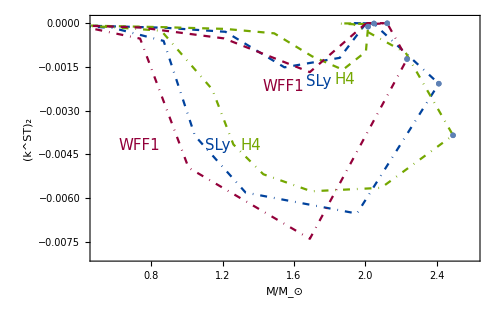

```mathematica
Show[{Table[ListLinePlot[Table[{massradJordT[[p]][[β]][[1]][[All,2]][[h]],Evaluate[(1/(ⅇ^(1/2 βvals[[β]] φ0[massradT[[p]][[β]][[1]][[All,1]][[h]]*km]^2)))^5*((ⅇ^(βvals[[β]] φinfvals[[1]]^2))/(2(-βvals[[β]])))3/2((MultipoleScalarNoES[[p]][[β]][[1]])/TidalTensorNoES[[p]][[β]][[1]])[[h]](massradADMT[[p]][[β]][[1]][[All,1]][[h]]*km)^-5/.BackgroundTOVPieceT[[p]][[β]][[1]][[h]]][[1]]},{h,1,Length[ρvals]}],PlotStyle->{StyleList[[β]],ColorList[[p]]},PlotRange->{{0.5,2.6},{0.0001,-0.008}},If[p==3,PlotLegends->Placed[LineLegend[{StyleList[[β]]},{Style[βnamesList[[β]],15]}],{Left,Bottom}],PlotLegends->Automatic],Epilog->{Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.18,0.5}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.36,0.5}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.44,0.5}],{1,1}],Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.55,0.74}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.62,0.76}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.68,0.77}],{1,1}]},Frame->True,FrameLabel->{{Style["(k^ST)_2","Latin Modern Roman",19,Black],None},{Style["M/M_⊙","Latin Modern Roman",18,Black],Style["Jordan frame φ_∞=10^-3","Latin Modern Roman",18,Black]}},FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},ImageSize->500],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}],Table[ListPlot[{{massradJordT[[p]][[β]][[1]][[All,2]][[MaxPointsSTJordIndex[[p]][[β]][[1]]]],Evaluate[(1/(ⅇ^(1/2 βvals[[β]] φ0[massradT[[p]][[β]][[1]][[All,1]][[MaxPointsSTJordIndex[[p]][[β]][[1]]]]*km]^2)))^5*((ⅇ^(βvals[[β]] φinfvals[[1]]^2))/(2(-βvals[[β]])))3/2((MultipoleScalarNoES[[p]][[β]][[1]])/TidalTensorNoES[[p]][[β]][[1]])[[MaxPointsSTJordIndex[[p]][[β]][[1]]]](massradADMT[[p]][[β]][[1]][[All,1]][[MaxPointsSTJordIndex[[p]][[β]][[1]]]]*km)^-5/.BackgroundTOVPieceT[[p]][[β]][[1]][[MaxPointsSTJordIndex[[p]][[β]][[1]]]]][[1]]}},PlotMarkers->Style[{"x","o"}[[β]],{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}]}//Flatten]
```

```mathematica
(* l=3 *)
```

```mathematica
(* Tensor *)
```

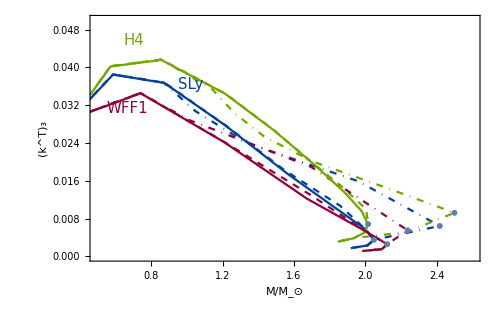

```mathematica
Show[{Table[ListLinePlot[Table[{massradADMT[[p]][[β]][[1]][[All,2]][[h]],15/2((MultipoleTensorNoESl3[[p]][[β]][[1]])/TidalTensorNoESl3[[p]][[β]][[1]])[[h]](massradADMT[[p]][[β]][[1]][[All,1]][[h]]*km)^-7},{h,1,Length[ρvals]}],PlotStyle->{StyleList[[β]],ColorList[[p]]},PlotRange->{{0.5,2.6},{0,0.05}},If[p==3,PlotLegends->Placed[LineLegend[{StyleList[[β]]},{Style[βnamesList[[β]],15]}],{Right,Top}],PlotLegends->Automatic],Epilog->{Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.15,0.65}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.29,0.75}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.14,0.93}],{1,1}]},Frame->True,FrameLabel->{{Style["(k^T)_3","Latin Modern Roman",19,Black],None},{Style["M/M_⊙","Latin Modern Roman",18,Black],Style["Einstein frame φ_∞=10^-3","Latin Modern Roman",18,Black]}},FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},ImageSize->500],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}],Table[ListLinePlot[Table[{massradGRT[[p]][[1]][[1]][[All,2]][[h]],15/2((MultipoleTensorNoESGRl3[[p]])/TidalTensorNoESGRl3[[p]])[[h]](massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km)^-7},{h,1,Length[ρvals]}],PlotStyle->{ColorList[[p]]},ImageSize->500],{p,1,Length[EoSIndex]}],Table[ListPlot[{{massradADMT[[p]][[β]][[1]][[All,2]][[MaxPointsSTEinstIndex[[p]][[β]][[1]]]],15/2((MultipoleTensorNoESl3[[p]][[β]][[1]])/TidalTensorNoESl3[[p]][[β]][[1]])[[MaxPointsSTEinstIndex[[p]][[β]][[1]]]](massradADMT[[p]][[β]][[1]][[All,1]][[MaxPointsSTEinstIndex[[p]][[β]][[1]]]]*km)^-7}},PlotMarkers->Style[{"x","o"}[[β]],{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}]}//Flatten]
```

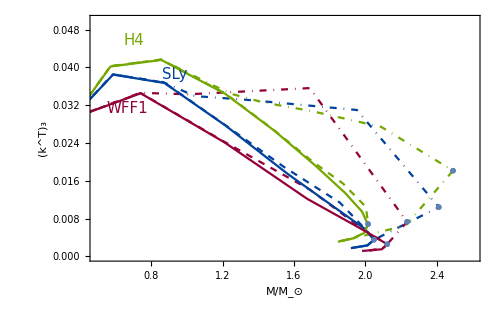

```mathematica
Show[{Table[ListLinePlot[Table[{massradJordT[[p]][[β]][[1]][[All,2]][[h]],Evaluate[(1/(ⅇ^(1/2 βvals[[β]] φ0[massradT[[p]][[β]][[1]][[All,1]][[h]]*km]^2)))^7*15/2((MultipoleTensorNoESl3[[p]][[β]][[1]])/TidalTensorNoESl3[[p]][[β]][[1]])[[h]](massradT[[p]][[β]][[1]][[All,1]][[h]]*km)^-7/.BackgroundTOVPieceT[[p]][[β]][[1]][[h]]][[1]]},{h,1,Length[ρvals]}],PlotStyle->{StyleList[[β]],ColorList[[p]]},PlotRange->{{0.5,2.6},{0,0.05}},If[p==3,PlotLegends->Placed[LineLegend[{StyleList[[β]]},{Style[βnamesList[[β]],15]}],{Right,Top}],PlotLegends->Automatic],Epilog->{Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.15,0.65}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.25,0.79}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.14,0.93}],{1,1}]},Frame->True,FrameLabel->{{Style["(k^T)_3","Latin Modern Roman",19,Black],None},{Style["M/M_⊙","Latin Modern Roman",18,Black],Style["Jordan frame φ_∞=10^-3","Latin Modern Roman",18,Black]}},FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},ImageSize->500],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}],Table[ListLinePlot[Table[{massradGRT[[p]][[1]][[1]][[All,2]][[h]],15/2((MultipoleTensorNoESGRl3[[p]])/TidalTensorNoESGRl3[[p]])[[h]](massradGRT[[p]][[1]][[1]][[All,1]][[h]]*km)^-7},{h,1,Length[ρvals]}],PlotStyle->{ColorList[[p]]},ImageSize->500],{p,1,Length[EoSIndex]}],Table[ListPlot[{{massradJordT[[p]][[β]][[1]][[All,2]][[MaxPointsSTJordIndex[[p]][[β]][[1]]]],Evaluate[(1/(ⅇ^(1/2 βvals[[β]] φ0[massradT[[p]][[β]][[1]][[All,1]][[MaxPointsSTJordIndex[[p]][[β]][[1]]]]*km]^2)))^7*15/2((MultipoleTensorNoESl3[[p]][[β]][[1]])/TidalTensorNoESl3[[p]][[β]][[1]])[[MaxPointsSTJordIndex[[p]][[β]][[1]]]](massradT[[p]][[β]][[1]][[All,1]][[MaxPointsSTJordIndex[[p]][[β]][[1]]]]*km)^-7/.BackgroundTOVPieceT[[p]][[β]][[1]][[MaxPointsSTJordIndex[[p]][[β]][[1]]]]][[1]]}},PlotMarkers->Style[{"x","o"}[[β]],{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}]}//Flatten]
```

```mathematica
(* Scalar *)
```

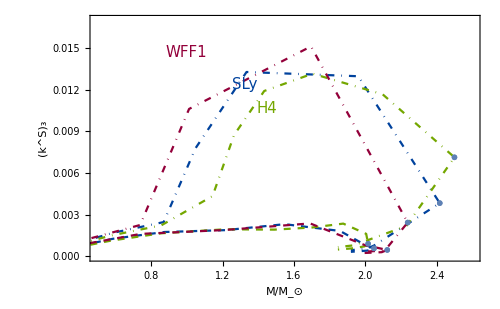

```mathematica
Show[{Table[ListLinePlot[Table[{massradADMT[[p]][[β]][[1]][[All,2]][[h]],15/2((MultipoleScalarNoETl3[[p]][[β]][[1]])/TidalScalarNoETl3[[p]][[β]][[1]])[[h]](massradADMT[[p]][[β]][[1]][[All,1]][[h]]*km)^-7},{h,1,Length[ρvals]}],PlotStyle->{StyleList[[β]],ColorList[[p]]},PlotRange->{{0.5,2.6},{0,0.017}},If[p==3,PlotLegends->Placed[LineLegend[{StyleList[[β]]},{Style[βnamesList[[β]],15]}],{Right,Top}],PlotLegends->Automatic],Epilog->{Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.3,0.88}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.43,0.75}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.48,0.65}],{1,1}]},Frame->True,FrameLabel->{{Style["(k^S)_3","Latin Modern Roman",19,Black],None},{Style["M/M_⊙","Latin Modern Roman",18,Black],Style["Einstein frame φ_∞=10^-3","Latin Modern Roman",18,Black]}},FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},ImageSize->500],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}],Table[ListPlot[{{massradADMT[[p]][[β]][[1]][[All,2]][[MaxPointsSTEinstIndex[[p]][[β]][[1]]]],15/2((MultipoleScalarNoETl3[[p]][[β]][[1]])/TidalScalarNoETl3[[p]][[β]][[1]])[[MaxPointsSTEinstIndex[[p]][[β]][[1]]]](massradADMT[[p]][[β]][[1]][[All,1]][[MaxPointsSTEinstIndex[[p]][[β]][[1]]]]*km)^-7}},PlotMarkers->Style[{"x","o"}[[β]],{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}]}//Flatten]
```

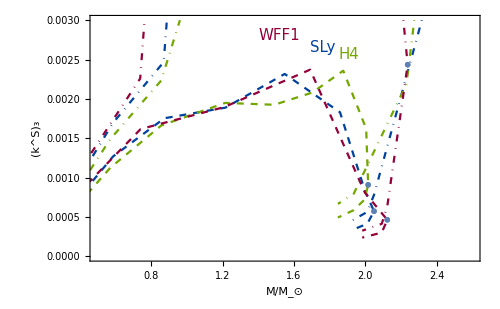

```mathematica
Show[{Table[ListLinePlot[Table[{massradADMT[[p]][[β]][[1]][[All,2]][[h]],15/2((MultipoleScalarNoETl3[[p]][[β]][[1]])/TidalScalarNoETl3[[p]][[β]][[1]])[[h]](massradADMT[[p]][[β]][[1]][[All,1]][[h]]*km)^-7},{h,1,Length[ρvals]}],PlotStyle->{StyleList[[β]],ColorList[[p]]},PlotRange->{{0.5,2.6},{0,0.003}},If[p==3,PlotLegends->Placed[LineLegend[{StyleList[[β]]},{Style[βnamesList[[β]],15]}],{Left,Bottom}],PlotLegends->Automatic],Epilog->{Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.54,0.95}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.63,0.9}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.69,0.87}],{1,1}]},Frame->True,FrameLabel->{{Style["(k^S)_3","Latin Modern Roman",19,Black],None},{Style["M/M_⊙","Latin Modern Roman",18,Black],Style["Einstein frame φ_∞=10^-3","Latin Modern Roman",18,Black]}},FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},ImageSize->500],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}],Table[ListPlot[{{massradADMT[[p]][[β]][[1]][[All,2]][[MaxPointsSTEinstIndex[[p]][[β]][[1]]]],15/2((MultipoleScalarNoETl3[[p]][[β]][[1]])/TidalScalarNoETl3[[p]][[β]][[1]])[[MaxPointsSTEinstIndex[[p]][[β]][[1]]]](massradADMT[[p]][[β]][[1]][[All,1]][[MaxPointsSTEinstIndex[[p]][[β]][[1]]]]*km)^-7}},PlotMarkers->Style[{"x","o"}[[β]],{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}]}//Flatten]
```

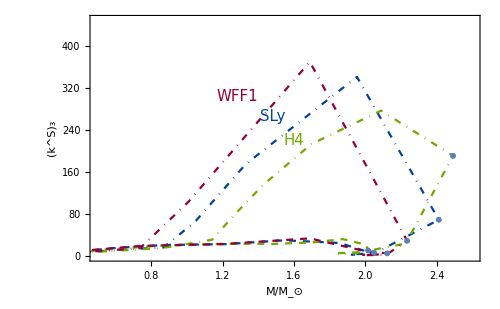

```mathematica
Show[{Table[ListLinePlot[Table[{massradJordT[[p]][[β]][[1]][[All,2]][[h]],Evaluate[(1/(ⅇ^(1/2 βvals[[β]] φ0[massradT[[p]][[β]][[1]][[All,1]][[h]]*km]^2)))^7*((ⅇ^(βvals[[β]] φinfvals[[1]]^2))/(2(-βvals[[β]])φinfvals[[1]]))^2 15/2((MultipoleScalarNoETl3[[p]][[β]][[1]])/TidalScalarNoETl3[[p]][[β]][[1]])[[h]](massradJordT[[p]][[β]][[1]][[All,1]][[h]]*km)^-7/.BackgroundTOVPieceT[[p]][[β]][[1]][[h]]][[1]]},{h,1,Length[ρvals]}],PlotStyle->{StyleList[[β]],ColorList[[p]]},PlotRange->{{0.5,2.6},{0,450}},If[p==3,PlotLegends->Placed[LineLegend[{StyleList[[β]]},{Style[βnamesList[[β]],15]}],{Left,Top}],PlotLegends->Automatic],Epilog->{Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.43,0.7}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.5,0.62}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.55,0.52}],{1,1}]},Frame->True,FrameLabel->{{Style["(k^S)_3","Latin Modern Roman",19,Black],None},{Style["M/M_⊙","Latin Modern Roman",18,Black],Style["Jordan frame φ_∞=10^-3","Latin Modern Roman",18,Black]}},FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},ImageSize->500],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}],Table[ListPlot[{{massradJordT[[p]][[β]][[1]][[All,2]][[MaxPointsSTJordIndex[[p]][[β]][[1]]]],Evaluate[(1/(ⅇ^(1/2 βvals[[β]] φ0[massradT[[p]][[β]][[1]][[All,1]][[MaxPointsSTJordIndex[[p]][[β]][[1]]]]*km]^2)))^7((ⅇ^(βvals[[β]] φinfvals[[1]]^2))/(2(-βvals[[β]])φinfvals[[1]]))^2*15/2((MultipoleScalarNoETl3[[p]][[β]][[1]])/TidalScalarNoETl3[[p]][[β]][[1]])[[MaxPointsSTJordIndex[[p]][[β]][[1]]]](massradJordT[[p]][[β]][[1]][[All,1]][[MaxPointsSTJordIndex[[p]][[β]][[1]]]]*km)^-7/.BackgroundTOVPieceT[[p]][[β]][[1]][[MaxPointsSTJordIndex[[p]][[β]][[1]]]]][[1]]}},PlotMarkers->Style[{"x","o"}[[β]],{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}]}//Flatten]
```

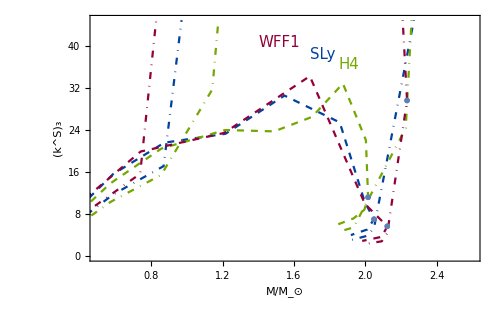

```mathematica
Show[{Table[ListLinePlot[Table[{massradJordT[[p]][[β]][[1]][[All,2]][[h]],Evaluate[(1/(ⅇ^(1/2 βvals[[β]] φ0[massradT[[p]][[β]][[1]][[All,1]][[h]]*km]^2)))^7*((ⅇ^(βvals[[β]] φinfvals[[1]]^2))/(2(-βvals[[β]])φinfvals[[1]]))^2 15/2((MultipoleScalarNoETl3[[p]][[β]][[1]])/TidalScalarNoETl3[[p]][[β]][[1]])[[h]](massradJordT[[p]][[β]][[1]][[All,1]][[h]]*km)^-7/.BackgroundTOVPieceT[[p]][[β]][[1]][[h]]][[1]]},{h,1,Length[ρvals]}],PlotStyle->{StyleList[[β]],ColorList[[p]]},PlotRange->{{0.5,2.6},{0,45}},If[p==3,PlotLegends->Placed[LineLegend[{StyleList[[β]]},{Style[βnamesList[[β]],15]}],{Left,Bottom}],PlotLegends->Automatic],Epilog->{Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.54,0.92}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.63,0.87}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.69,0.83}],{1,1}]},Frame->True,FrameLabel->{{Style["(k^S)_3","Latin Modern Roman",19,Black],None},{Style["M/M_⊙","Latin Modern Roman",18,Black],Style["Jordan frame φ_∞=10^-3","Latin Modern Roman",18,Black]}},FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},ImageSize->500],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}],Table[ListPlot[{{massradJordT[[p]][[β]][[1]][[All,2]][[MaxPointsSTJordIndex[[p]][[β]][[1]]]],Evaluate[(1/(ⅇ^(1/2 βvals[[β]] φ0[massradT[[p]][[β]][[1]][[All,1]][[MaxPointsSTJordIndex[[p]][[β]][[1]]]]*km]^2)))^7((ⅇ^(βvals[[β]] φinfvals[[1]]^2))/(2(-βvals[[β]])φinfvals[[1]]))^2*15/2((MultipoleScalarNoETl3[[p]][[β]][[1]])/TidalScalarNoETl3[[p]][[β]][[1]])[[MaxPointsSTJordIndex[[p]][[β]][[1]]]](massradJordT[[p]][[β]][[1]][[All,1]][[MaxPointsSTJordIndex[[p]][[β]][[1]]]]*km)^-7/.BackgroundTOVPieceT[[p]][[β]][[1]][[MaxPointsSTJordIndex[[p]][[β]][[1]]]]][[1]]}},PlotMarkers->Style[{"x","o"}[[β]],{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}]}//Flatten]
```

```mathematica
(* Scalar-Tensor *)
```

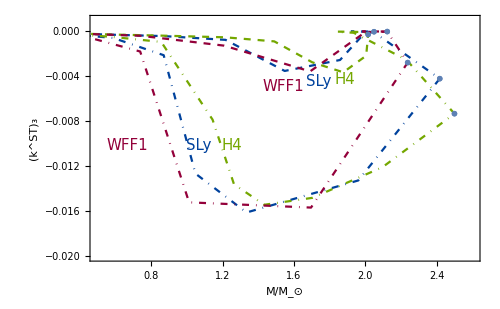

```mathematica
Show[{Table[ListLinePlot[Table[{massradADMT[[p]][[β]][[1]][[All,2]][[h]],15/2((MultipoleScalarNoESl3[[p]][[β]][[1]])/TidalTensorNoESl3[[p]][[β]][[1]])[[h]](massradADMT[[p]][[β]][[1]][[All,1]][[h]]*km)^-7},{h,1,Length[ρvals]}],PlotStyle->{StyleList[[β]],ColorList[[p]]},PlotRange->{{0.5,2.6},{0.001,-0.02}},If[p==3,PlotLegends->Placed[LineLegend[{StyleList[[β]]},{Style[βnamesList[[β]],15]}],{Right,Bottom}],PlotLegends->Automatic],Epilog->{Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.15,0.5}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.31,0.5}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.39,0.5}],{1,1}],Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.55,0.74}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.62,0.76}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.68,0.77}],{1,1}]},Frame->True,FrameLabel->{{Style["(k^ST)_3","Latin Modern Roman",19,Black],None},{Style["M/M_⊙","Latin Modern Roman",18,Black],Style["Einstein frame φ_∞=10^-3","Latin Modern Roman",18,Black]}},FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},ImageSize->500],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}],Table[ListPlot[{{massradADMT[[p]][[β]][[1]][[All,2]][[MaxPointsSTEinstIndex[[p]][[β]][[1]]]],15/2((MultipoleScalarNoESl3[[p]][[β]][[1]])/TidalTensorNoESl3[[p]][[β]][[1]])[[MaxPointsSTEinstIndex[[p]][[β]][[1]]]](massradADMT[[p]][[β]][[1]][[All,1]][[MaxPointsSTEinstIndex[[p]][[β]][[1]]]]*km)^-7}},PlotMarkers->Style[{"x","o"}[[β]],{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}]}//Flatten]
```

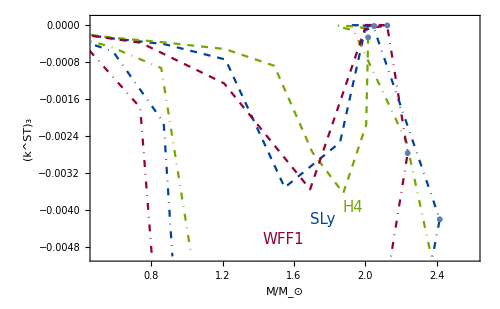

```mathematica
Show[{Table[ListLinePlot[Table[{massradADMT[[p]][[β]][[1]][[All,2]][[h]],15/2((MultipoleScalarNoESl3[[p]][[β]][[1]])/TidalTensorNoESl3[[p]][[β]][[1]])[[h]](massradADMT[[p]][[β]][[1]][[All,1]][[h]]*km)^-7},{h,1,Length[ρvals]}],PlotStyle->{StyleList[[β]],ColorList[[p]]},PlotRange->{{0.5,2.6},{0.0001,-0.005}},If[p==3,PlotLegends->Placed[LineLegend[{StyleList[[β]]},{Style[βnamesList[[β]],15]}],{Right,Top}],PlotLegends->Automatic],Epilog->{Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.55,0.12}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.63,0.2}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.7,0.25}],{1,1}]},Frame->True,FrameLabel->{{Style["(k^ST)_3","Latin Modern Roman",19,Black],None},{Style["M/M_⊙","Latin Modern Roman",18,Black],Style["Einstein frame φ_∞=10^-3","Latin Modern Roman",18,Black]}},FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},ImageSize->500],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}],Table[ListPlot[{{massradADMT[[p]][[β]][[1]][[All,2]][[MaxPointsSTEinstIndex[[p]][[β]][[1]]]],15/2((MultipoleScalarNoESl3[[p]][[β]][[1]])/TidalTensorNoESl3[[p]][[β]][[1]])[[MaxPointsSTEinstIndex[[p]][[β]][[1]]]](massradADMT[[p]][[β]][[1]][[All,1]][[MaxPointsSTEinstIndex[[p]][[β]][[1]]]]*km)^-7}},PlotMarkers->Style[{"x","o"}[[β]],{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}]}//Flatten]
```

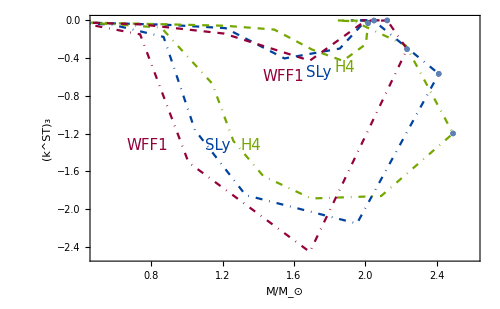

```mathematica
Show[{Table[ListLinePlot[Table[{massradJordT[[p]][[β]][[1]][[All,2]][[h]],Evaluate[(1/(ⅇ^(1/2 βvals[[β]] φ0[massradT[[p]][[β]][[1]][[All,1]][[h]]*km]^2)))^7*((ⅇ^(βvals[[β]] φinfvals[[1]]^2))/(2(-βvals[[β]])φinfvals[[1]]))15/2((MultipoleScalarNoESl3[[p]][[β]][[1]])/TidalTensorNoESl3[[p]][[β]][[1]])[[h]](massradADMT[[p]][[β]][[1]][[All,1]][[h]]*km)^-7/.BackgroundTOVPieceT[[p]][[β]][[1]][[h]]][[1]]},{h,1,Length[ρvals]}],PlotStyle->{StyleList[[β]],ColorList[[p]]},PlotRange->{{0.5,2.6},{0.001,-2.5}},If[p==3,PlotLegends->Placed[LineLegend[{StyleList[[β]]},{Style[βnamesList[[β]],15]}],{Left,Bottom}],PlotLegends->Automatic],Epilog->{Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.2,0.5}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.36,0.5}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.44,0.5}],{1,1}],Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.55,0.78}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.62,0.8}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.68,0.82}],{1,1}]},Frame->True,FrameLabel->{{Style["(k^ST)_3","Latin Modern Roman",19,Black],None},{Style["M/M_⊙","Latin Modern Roman",18,Black],Style["Jordan frame φ_∞=10^-3","Latin Modern Roman",18,Black]}},FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},ImageSize->500],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}],Table[ListPlot[{{massradJordT[[p]][[β]][[1]][[All,2]][[MaxPointsSTJordIndex[[p]][[β]][[1]]]],Evaluate[(1/(ⅇ^(1/2 βvals[[β]] φ0[massradT[[p]][[β]][[1]][[All,1]][[MaxPointsSTJordIndex[[p]][[β]][[1]]]]*km]^2)))^7((ⅇ^(βvals[[β]] φinfvals[[1]]^2))/(2(-βvals[[β]])φinfvals[[1]]))*15/2((MultipoleScalarNoESl3[[p]][[β]][[1]])/TidalTensorNoESl3[[p]][[β]][[1]])[[MaxPointsSTJordIndex[[p]][[β]][[1]]]](massradADMT[[p]][[β]][[1]][[All,1]][[MaxPointsSTJordIndex[[p]][[β]][[1]]]]*km)^-7/.BackgroundTOVPieceT[[p]][[β]][[1]][[MaxPointsSTJordIndex[[p]][[β]][[1]]]]][[1]]}},PlotMarkers->Style[{"x","o"}[[β]],{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}]}//Flatten]
```

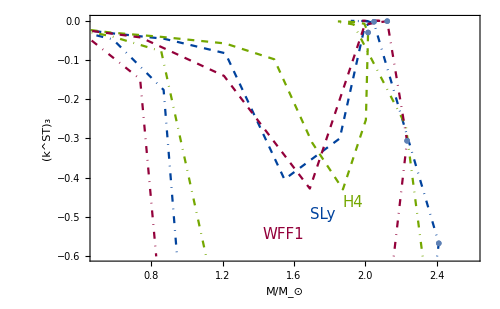

```mathematica
Show[{Table[ListLinePlot[Table[{massradJordT[[p]][[β]][[1]][[All,2]][[h]],Evaluate[(1/(ⅇ^(1/2 βvals[[β]] φ0[massradT[[p]][[β]][[1]][[All,1]][[h]]*km]^2)))^7*((ⅇ^(βvals[[β]] φinfvals[[1]]^2))/(2(-βvals[[β]])φinfvals[[1]]))15/2((MultipoleScalarNoESl3[[p]][[β]][[1]])/TidalTensorNoESl3[[p]][[β]][[1]])[[h]](massradADMT[[p]][[β]][[1]][[All,1]][[h]]*km)^-7/.BackgroundTOVPieceT[[p]][[β]][[1]][[h]]][[1]]},{h,1,Length[ρvals]}],PlotStyle->{StyleList[[β]],ColorList[[p]]},PlotRange->{{0.5,2.6},{0.001,-0.6}},If[p==3,PlotLegends->Placed[LineLegend[{StyleList[[β]]},{Style[βnamesList[[β]],15]}],{Right,Top}],PlotLegends->Automatic],Epilog->{Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.55,0.14}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.63,0.22}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.7,0.27}],{1,1}]},Frame->True,FrameLabel->{{Style["(k^ST)_3","Latin Modern Roman",19,Black],None},{Style["M/M_⊙","Latin Modern Roman",18,Black],Style["Jordan frame φ_∞=10^-3","Latin Modern Roman",18,Black]}},FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},ImageSize->500],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}],Table[ListPlot[{{massradJordT[[p]][[β]][[1]][[All,2]][[MaxPointsSTJordIndex[[p]][[β]][[1]]]],Evaluate[(1/(ⅇ^(1/2 βvals[[β]] φ0[massradT[[p]][[β]][[1]][[All,1]][[MaxPointsSTJordIndex[[p]][[β]][[1]]]]*km]^2)))^7((ⅇ^(βvals[[β]] φinfvals[[1]]^2))/(2(-βvals[[β]])φinfvals[[1]]))*15/2((MultipoleScalarNoESl3[[p]][[β]][[1]])/TidalTensorNoESl3[[p]][[β]][[1]])[[MaxPointsSTJordIndex[[p]][[β]][[1]]]](massradADMT[[p]][[β]][[1]][[All,1]][[MaxPointsSTJordIndex[[p]][[β]][[1]]]]*km)^-7/.BackgroundTOVPieceT[[p]][[β]][[1]][[MaxPointsSTJordIndex[[p]][[β]][[1]]]]][[1]]}},PlotMarkers->Style[{"x","o"}[[β]],{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}]}//Flatten]
```

#### Plots of Λ_l

```mathematica
(* l=1 *)
```

```mathematica
(* Scalar *)
```

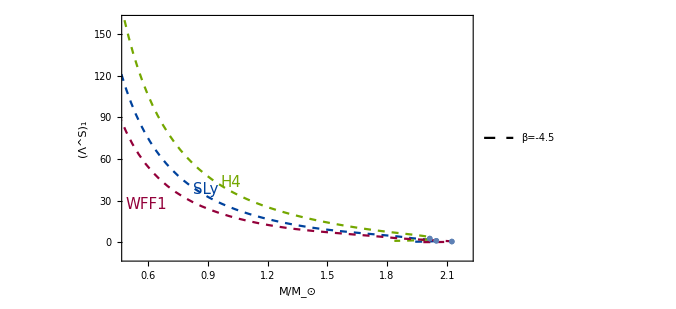

```mathematica
Show[{Table[ListLinePlot[Table[{massradADMT[[p]][[β]][[1]][[All,2]][[h]],((MultipoleScalarNoETl1[[p]][[β]][[1]]-1/2 ChargeTableT[[p]][[β]][[1]][[All,2]]MultipoleTensorNoETl1[[p]][[β]][[1]])/TidalScalarNoETl1[[p]][[β]][[1]])[[h]]*(massradADMT[[p]][[β]][[1]][[All,2]][[h]])^-3},{h,1,Length[ρvals]}],PlotStyle->{StyleList[[β]],ColorList[[p]]},PlotRange->{{0.5,2.2},{-10,160}},If[p==3,PlotLegends->Placed[LineLegend[{StyleList[[β]]},{Style[βnamesList[[β]],15]}],{Right,Top}],PlotLegends->Automatic],Epilog->{Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.13,0.26}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.275,0.32}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.34,0.35}],{1,1}]},Frame->True,FrameLabel->{{Style["(Λ^S)_1","Latin Modern Roman",19,Black],None},{Style["M/M_⊙","Latin Modern Roman",18,Black],Style["Einstein frame φ_∞=10^-3","Latin Modern Roman",18,Black]}},FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},ImageSize->500],{p,1,Length[EoSIndex]},{β,1,1}],Table[ListPlot[{{massradADMT[[p]][[β]][[1]][[All,2]][[MaxPointsSTEinstIndex[[p]][[β]][[1]]]],((MultipoleScalarNoETl1[[p]][[β]][[1]]-1/2 ChargeTableT[[p]][[β]][[1]][[All,2]]MultipoleTensorNoETl1[[p]][[β]][[1]])/TidalScalarNoETl1[[p]][[β]][[1]])[[MaxPointsSTEinstIndex[[p]][[β]][[1]]]]*(massradADMT[[p]][[β]][[1]][[All,2]][[MaxPointsSTEinstIndex[[p]][[β]][[1]]]])^-3}},PlotMarkers->Style[{"x","o"}[[β]],{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]},{β,1,1}]}//Flatten]
```

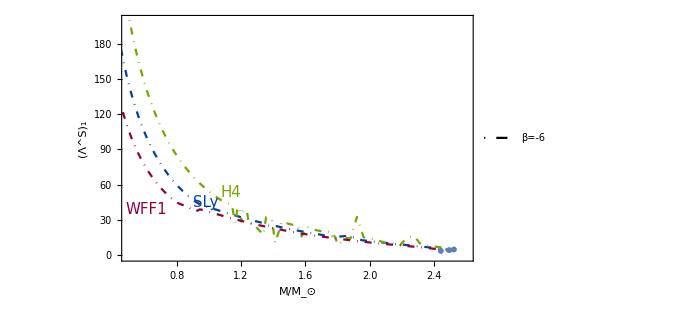

```mathematica
Show[{Table[ListLinePlot[Drop[Table[{massradADMT[[p]][[β]][[1]][[All,2]][[h]],((MultipoleScalarNoETl1[[p]][[β]][[1]]-1/2 ChargeTableT[[p]][[β]][[1]][[All,2]]MultipoleTensorNoETl1[[p]][[β]][[1]])/TidalScalarNoETl1[[p]][[β]][[1]])[[h]]*(massradADMT[[p]][[β]][[1]][[All,2]][[h]])^-3},{h,1,Length[ρvals]}],Dropvals[[p]]],PlotStyle->{StyleList[[β]],ColorList[[p]]},PlotRange->{{0.5,2.6},{-1,200}},If[p==3,PlotLegends->Placed[LineLegend[{StyleList[[β]]},{Style[βnamesList[[β]],15]}],{Right,Top}],PlotLegends->Automatic],Epilog->{Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.13,0.24}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.275,0.27}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.34,0.31}],{1,1}]},Frame->True,FrameLabel->{{Style["(Λ^S)_1","Latin Modern Roman",19,Black],None},{Style["M/M_⊙","Latin Modern Roman",18,Black],Style["Einstein frame φ_∞=10^-3","Latin Modern Roman",18,Black]}},FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},ImageSize->500],{p,1,Length[EoSIndex]},{β,{2}}],Table[ListPlot[{{massradADMT[[p]][[β]][[1]][[All,2]][[MaxPointsSTEinstIndex[[p]][[β]][[1]]]],((MultipoleScalarNoETl1[[p]][[β]][[1]]-1/2 ChargeTableT[[p]][[β]][[1]][[All,2]]MultipoleTensorNoETl1[[p]][[β]][[1]])/TidalScalarNoETl1[[p]][[β]][[1]])[[MaxPointsSTEinstIndex[[p]][[β]][[1]]]]*(massradADMT[[p]][[β]][[1]][[All,2]][[MaxPointsSTEinstIndex[[p]][[β]][[1]]]])^-3}},PlotMarkers->Style[{"x","o"}[[β]],{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]},{β,2,2}]}//Flatten]
```

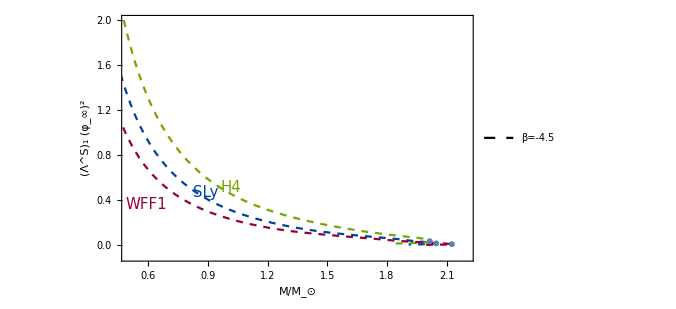

```mathematica
Show[{Table[ListLinePlot[Table[{massradJordT[[p]][[β]][[1]][[All,2]][[h]],((MultipoleScalarNoETl1[[p]][[β]][[1]]-1/2 ChargeTableT[[p]][[β]][[1]][[All,2]]MultipoleTensorNoETl1[[p]][[β]][[1]])/TidalScalarNoETl1[[p]][[β]][[1]])[[h]]*(massradJordT[[p]][[β]][[1]][[All,2]][[h]])^-3((ⅇ^(βvals[[β]] φinfvals[[1]]^2))/(2(-βvals[[β]])))^2},{h,1,Length[ρvals]}],PlotStyle->{StyleList[[β]],ColorList[[p]]},PlotRange->{{0.5,2.2},{-0.1,2}},If[p==3,PlotLegends->Placed[LineLegend[{StyleList[[β]]},{Style[βnamesList[[β]],15]}],{Right,Top}],PlotLegends->Automatic],Epilog->{Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.13,0.26}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.275,0.31}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.34,0.33}],{1,1}]},Frame->True,FrameLabel->{{Style["(Λ^S)_1 (φ_∞)^2","Latin Modern Roman",19,Black],None},{Style["M/M_⊙","Latin Modern Roman",18,Black],Style["Jordan frame φ_∞=10^-3","Latin Modern Roman",18,Black]}},FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},ImageSize->500],{p,1,Length[EoSIndex]},{β,1,1}],Table[ListPlot[{{massradJordT[[p]][[β]][[1]][[All,2]][[MaxPointsSTJordIndex[[p]][[β]][[1]]]],((MultipoleScalarNoETl1[[p]][[β]][[1]]-1/2 ChargeTableT[[p]][[β]][[1]][[All,2]]MultipoleTensorNoETl1[[p]][[β]][[1]])/TidalScalarNoETl1[[p]][[β]][[1]])[[MaxPointsSTJordIndex[[p]][[β]][[1]]]]*(massradJordT[[p]][[β]][[1]][[All,2]][[MaxPointsSTJordIndex[[p]][[β]][[1]]]])^-3((ⅇ^(βvals[[β]] φinfvals[[1]]^2))/(2(-βvals[[β]])))^2}},PlotMarkers->Style[{"x","o"}[[β]],{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]},{β,1,1}]}//Flatten]
```

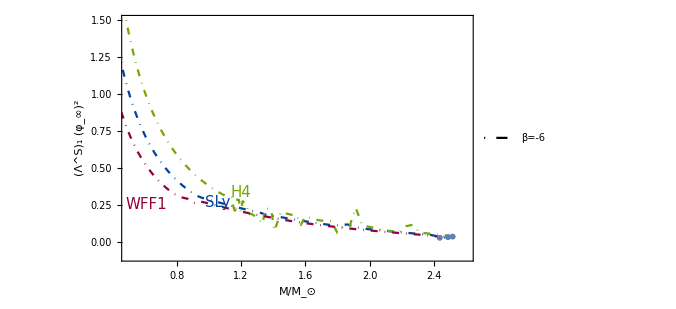

```mathematica
Show[{Table[ListLinePlot[Drop[Table[{massradJordT[[p]][[β]][[1]][[All,2]][[h]],((MultipoleScalarNoETl1[[p]][[β]][[1]]-1/2 ChargeTableT[[p]][[β]][[1]][[All,2]]MultipoleTensorNoETl1[[p]][[β]][[1]])/TidalScalarNoETl1[[p]][[β]][[1]])[[h]]*(massradJordT[[p]][[β]][[1]][[All,2]][[h]])^-3((ⅇ^(βvals[[β]] φinfvals[[1]]^2))/(2(-βvals[[β]])))^2},{h,1,Length[ρvals]}],Dropvals[[p]]],PlotStyle->{StyleList[[β]],ColorList[[p]]},PlotRange->{{0.5,2.6},{-0.1,1.5}},If[p==3,PlotLegends->Placed[LineLegend[{StyleList[[β]]},{Style[βnamesList[[β]],15]}],{Right,Top}],PlotLegends->Automatic],Epilog->{Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.13,0.26}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.31,0.27}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.37,0.31}],{1,1}]},Frame->True,FrameLabel->{{Style["(Λ^S)_1 (φ_∞)^2","Latin Modern Roman",19,Black],None},{Style["M/M_⊙","Latin Modern Roman",18,Black],Style["Jordan frame φ_∞=10^-3","Latin Modern Roman",18,Black]}},FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},ImageSize->500],{p,1,Length[EoSIndex]},{β,{2}}],Table[ListPlot[{{massradJordT[[p]][[β]][[1]][[All,2]][[MaxPointsSTJordIndex[[p]][[β]][[1]]]],((MultipoleScalarNoETl1[[p]][[β]][[1]]-1/2 ChargeTableT[[p]][[β]][[1]][[All,2]]MultipoleTensorNoETl1[[p]][[β]][[1]])/TidalScalarNoETl1[[p]][[β]][[1]])[[MaxPointsSTJordIndex[[p]][[β]][[1]]]]*(massradJordT[[p]][[β]][[1]][[All,2]][[MaxPointsSTJordIndex[[p]][[β]][[1]]]])^-3((ⅇ^(βvals[[β]] φinfvals[[1]]^2))/(2(-βvals[[β]])))^2}},PlotMarkers->Style[{"x","o"}[[β]],{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]},{β,2,2}]}//Flatten]
```

```mathematica
(* l=2 *)
```

```mathematica
(* Tensor *)
```

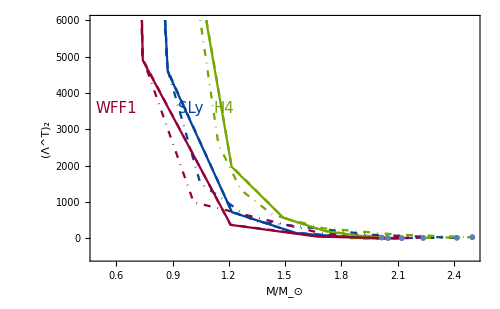

```mathematica
Show[{Table[ListLinePlot[Table[{massradADMT[[p]][[β]][[1]][[All,2]][[h]],((MultipoleTensorNoES[[p]][[β]][[1]])/TidalTensorNoES[[p]][[β]][[1]])[[h]]*(massradADMT[[p]][[β]][[1]][[All,2]][[h]])^-5},{h,1,Length[ρvals]}],PlotStyle->{StyleList[[β]],ColorList[[p]]},PlotRange->{{0.5,2.5},{-500,6000}},If[p==3,PlotLegends->Placed[LineLegend[{StyleList[[β]]},{Style[βnamesList[[β]],15]}],{Right,Top}],PlotLegends->Automatic],Epilog->{Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.12,0.65}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.29,0.65}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.37,0.65}],{1,1}]},Frame->True,FrameLabel->{{Style["(Λ^T)_2","Latin Modern Roman",19,Black],None},{Style["M/M_⊙","Latin Modern Roman",18,Black],Style["Einstein frame φ_∞=10^-3","Latin Modern Roman",18,Black]}},FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},ImageSize->500],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}],Table[ListLinePlot[Table[{massradGRT[[p]][[1]][[1]][[All,2]][[h]],((MultipoleTensorNoESGR[[p]])/TidalTensorNoESGR[[p]])[[h]]*(massradGRT[[p]][[1]][[1]][[All,2]][[h]])^-5},{h,1,Length[ρvals]}],PlotStyle->{ColorList[[p]]},PlotRange->{{0.5,2.5},{0,6000}},ImageSize->500],{p,1,Length[EoSIndex]}],Table[ListPlot[{{massradADMT[[p]][[β]][[1]][[All,2]][[MaxPointsSTEinstIndex[[p]][[β]][[1]]]],((MultipoleTensorNoES[[p]][[β]][[1]])/TidalTensorNoES[[p]][[β]][[1]])[[MaxPointsSTEinstIndex[[p]][[β]][[1]]]]*(massradADMT[[p]][[β]][[1]][[All,2]][[MaxPointsSTEinstIndex[[p]][[β]][[1]]]])^-5}},PlotMarkers->Style[{"x","o"}[[β]],{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}]}//Flatten]
```

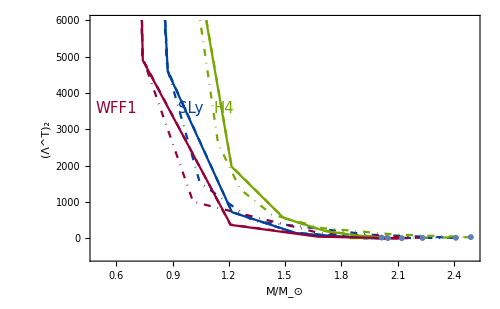

```mathematica
Show[{Table[ListLinePlot[Table[{massradJordT[[p]][[β]][[1]][[All,2]][[h]],((MultipoleTensorNoES[[p]][[β]][[1]])/TidalTensorNoES[[p]][[β]][[1]])[[h]]*(massradJordT[[p]][[β]][[1]][[All,2]][[h]])^-5},{h,1,Length[ρvals]}],PlotStyle->{StyleList[[β]],ColorList[[p]]},PlotRange->{{0.5,2.5},{-500,6000}},If[p==3,PlotLegends->Placed[LineLegend[{StyleList[[β]]},{Style[βnamesList[[β]],15]}],{Right,Top}],PlotLegends->Automatic],Epilog->{Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.12,0.65}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.29,0.65}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.37,0.65}],{1,1}]},Frame->True,FrameLabel->{{Style["(Λ^T)_2","Latin Modern Roman",19,Black],None},{Style["M/M_⊙","Latin Modern Roman",18,Black],Style["Jordan frame φ_∞=10^-3","Latin Modern Roman",18,Black]}},FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},ImageSize->500],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}],Table[ListLinePlot[Table[{massradGRT[[p]][[1]][[1]][[All,2]][[h]],((MultipoleTensorNoESGR[[p]])/TidalTensorNoESGR[[p]])[[h]]*(massradGRT[[p]][[1]][[1]][[All,2]][[h]])^-5},{h,1,Length[ρvals]}],PlotStyle->{ColorList[[p]]},PlotRange->{{0.5,2.5},{0,6000}},ImageSize->500],{p,1,Length[EoSIndex]}],Table[ListPlot[{{massradJordT[[p]][[β]][[1]][[All,2]][[MaxPointsSTJordIndex[[p]][[β]][[1]]]],((MultipoleTensorNoES[[p]][[β]][[1]])/TidalTensorNoES[[p]][[β]][[1]])[[MaxPointsSTEinstIndex[[p]][[β]][[1]]]]*(massradJordT[[p]][[β]][[1]][[All,2]][[MaxPointsSTJordIndex[[p]][[β]][[1]]]])^-5}},PlotMarkers->Style[{"x","o"}[[β]],{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}]}//Flatten]
```

```mathematica
(* Scalar *)
```

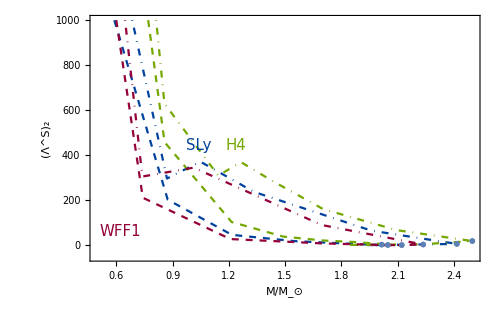

```mathematica
Show[{Table[ListLinePlot[Table[{massradADMT[[p]][[β]][[1]][[All,2]][[h]],((MultipoleScalarNoET[[p]][[β]][[1]])/TidalScalarNoET[[p]][[β]][[1]])[[h]]*(massradADMT[[p]][[β]][[1]][[All,2]][[h]])^-5},{h,1,Length[ρvals]}],PlotStyle->{StyleList[[β]],ColorList[[p]]},PlotRange->{{0.5,2.5},{-50,1000}},If[p==3,PlotLegends->Placed[LineLegend[{StyleList[[β]]},{Style[βnamesList[[β]],15]}],{Right,Top}],PlotLegends->Automatic],Epilog->{Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.13,0.15}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.31,0.5}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.4,0.5}],{1,1}]},Frame->True,FrameLabel->{{Style["(Λ^S)_2","Latin Modern Roman",19,Black],None},{Style["M/M_⊙","Latin Modern Roman",18,Black],Style["Einstein frame φ_∞=10^-3","Latin Modern Roman",18,Black]}},FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},ImageSize->500],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}],Table[ListLinePlot[Table[{massradGRT[[p]][[1]][[1]][[All,2]][[h]],((MultipoleScalarNoETGR[[p]])/TidalScalarNoETGR[[p]])[[h]]*(massradGRT[[p]][[1]][[1]][[All,2]][[h]])^-5},{h,1,Length[ρvals]}],PlotStyle->{ColorList[[p]]},PlotRange->{{0.5,2.5},{0,6000}},ImageSize->500],{p,1,Length[EoSIndex]}],Table[ListPlot[{{massradADMT[[p]][[β]][[1]][[All,2]][[MaxPointsSTEinstIndex[[p]][[β]][[1]]]],((MultipoleScalarNoET[[p]][[β]][[1]])/TidalScalarNoET[[p]][[β]][[1]])[[MaxPointsSTEinstIndex[[p]][[β]][[1]]]]*(massradADMT[[p]][[β]][[1]][[All,2]][[MaxPointsSTEinstIndex[[p]][[β]][[1]]]])^-5}},PlotMarkers->Style[{"x","o"}[[β]],{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}]}//Flatten]
```

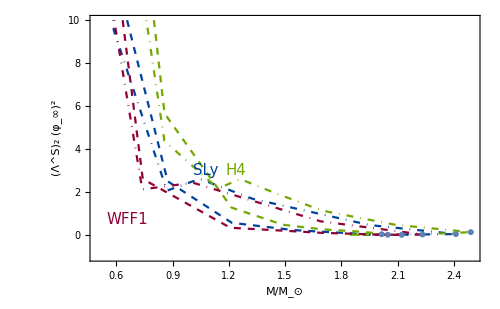

```mathematica
Show[{Table[ListLinePlot[Table[{massradJordT[[p]][[β]][[1]][[All,2]][[h]],((MultipoleScalarNoET[[p]][[β]][[1]])/TidalScalarNoET[[p]][[β]][[1]])[[h]]*(massradJordT[[p]][[β]][[1]][[All,2]][[h]])^-5((ⅇ^(βvals[[β]] φinfvals[[1]]^2))/(2(-βvals[[β]])))^2},{h,1,Length[ρvals]}],PlotStyle->{StyleList[[β]],ColorList[[p]]},PlotRange->{{0.5,2.5},{-1,10}},If[p==3,PlotLegends->Placed[LineLegend[{StyleList[[β]]},{Style[βnamesList[[β]],15]}],{Right,Top}],PlotLegends->Automatic],Epilog->{Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.15,0.2}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.33,0.4}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.4,0.4}],{1,1}]},Frame->True,FrameLabel->{{Style["(Λ^S)_2 (φ_∞)^2","Latin Modern Roman",19,Black],None},{Style["M/M_⊙","Latin Modern Roman",18,Black],Style["Jordan frame φ_∞=10^-3","Latin Modern Roman",18,Black]}},FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},ImageSize->500],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}],Table[ListLinePlot[Table[{massradGRT[[p]][[1]][[1]][[All,2]][[h]],((MultipoleScalarNoETGR[[p]])/TidalScalarNoETGR[[p]])[[h]]*(massradGRT[[p]][[1]][[1]][[All,2]][[h]])^-5},{h,1,Length[ρvals]}],PlotStyle->{ColorList[[p]]},PlotRange->{{0.5,2.5},{0,6000}},ImageSize->500],{p,1,Length[EoSIndex]}],Table[ListPlot[{{massradJordT[[p]][[β]][[1]][[All,2]][[MaxPointsSTJordIndex[[p]][[β]][[1]]]],((MultipoleScalarNoET[[p]][[β]][[1]])/TidalScalarNoET[[p]][[β]][[1]])[[MaxPointsSTEinstIndex[[p]][[β]][[1]]]]*(massradJordT[[p]][[β]][[1]][[All,2]][[MaxPointsSTJordIndex[[p]][[β]][[1]]]])^-5((ⅇ^(βvals[[β]] φinfvals[[1]]^2))/(2(-βvals[[β]])))^2}},PlotMarkers->Style[{"x","o"}[[β]],{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}]}//Flatten]
```

```mathematica
(* Scalar-Tensor *)
```

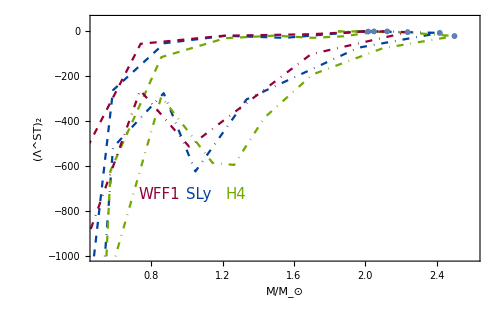

```mathematica
Show[{Table[ListLinePlot[Table[{massradADMT[[p]][[β]][[1]][[All,2]][[h]],((MultipoleScalarNoES[[p]][[β]][[1]])/TidalTensorNoES[[p]][[β]][[1]])[[h]]*(massradADMT[[p]][[β]][[1]][[All,2]][[h]])^-5},{h,1,Length[ρvals]}],PlotStyle->{StyleList[[β]],ColorList[[p]]},PlotRange->{{0.5,2.6},{50,-1000}},If[p==3,PlotLegends->Placed[LineLegend[{StyleList[[β]]},{Style[βnamesList[[β]],15]}],{Right,Bottom}],PlotLegends->Automatic],Epilog->{Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.23,0.3}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.31,0.3}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.4,0.3}],{1,1}]},Frame->True,FrameLabel->{{Style["(Λ^ST)_2","Latin Modern Roman",19,Black],None},{Style["M/M_⊙","Latin Modern Roman",18,Black],Style["Einstein frame φ_∞=10^-3","Latin Modern Roman",18,Black]}},FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},ImageSize->500],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}],Table[ListLinePlot[Table[{massradGRT[[p]][[1]][[1]][[All,2]][[h]],((MultipoleScalarNoETGR[[p]])/TidalScalarNoETGR[[p]])[[h]]*(massradGRT[[p]][[1]][[1]][[All,2]][[h]])^-5},{h,1,Length[ρvals]}],PlotStyle->{ColorList[[p]]},PlotRange->{{0.5,2.5},{0,6000}},ImageSize->500],{p,1,Length[EoSIndex]}],Table[ListPlot[{{massradADMT[[p]][[β]][[1]][[All,2]][[MaxPointsSTEinstIndex[[p]][[β]][[1]]]],((MultipoleScalarNoES[[p]][[β]][[1]])/TidalTensorNoES[[p]][[β]][[1]])[[MaxPointsSTEinstIndex[[p]][[β]][[1]]]]*(massradADMT[[p]][[β]][[1]][[All,2]][[MaxPointsSTEinstIndex[[p]][[β]][[1]]]])^-5}},PlotMarkers->Style[{"x","o"}[[β]],{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}]}//Flatten]
```

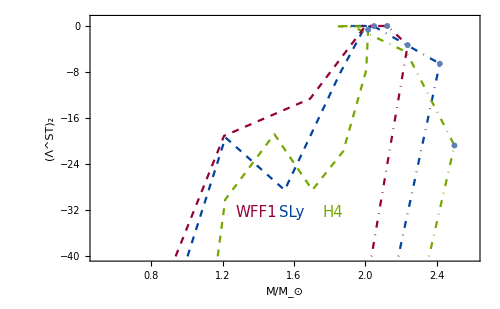

```mathematica
Show[{Table[ListLinePlot[Table[{massradADMT[[p]][[β]][[1]][[All,2]][[h]],((MultipoleScalarNoES[[p]][[β]][[1]])/TidalTensorNoES[[p]][[β]][[1]])[[h]]*(massradADMT[[p]][[β]][[1]][[All,2]][[h]])^-5},{h,1,Length[ρvals]}],PlotStyle->{StyleList[[β]],ColorList[[p]]},PlotRange->{{0.5,2.6},{1,-40}},If[p==3,PlotLegends->Placed[LineLegend[{StyleList[[β]]},{Style[βnamesList[[β]],15]}],{Left,Top}],PlotLegends->Automatic],Epilog->{Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.48,0.23}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.55,0.23}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.65,0.23}],{1,1}]},Frame->True,FrameLabel->{{Style["(Λ^ST)_2","Latin Modern Roman",19,Black],None},{Style["M/M_⊙","Latin Modern Roman",18,Black],Style["Einstein frame φ_∞=10^-3","Latin Modern Roman",18,Black]}},FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},ImageSize->500],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}],Table[ListLinePlot[Table[{massradGRT[[p]][[1]][[1]][[All,2]][[h]],((MultipoleScalarNoETGR[[p]])/TidalScalarNoETGR[[p]])[[h]]*(massradGRT[[p]][[1]][[1]][[All,2]][[h]])^-5},{h,1,Length[ρvals]}],PlotStyle->{ColorList[[p]]},PlotRange->{{0.5,2.5},{0,6000}},ImageSize->500],{p,1,Length[EoSIndex]}],Table[ListPlot[{{massradADMT[[p]][[β]][[1]][[All,2]][[MaxPointsSTEinstIndex[[p]][[β]][[1]]]],((MultipoleScalarNoES[[p]][[β]][[1]])/TidalTensorNoES[[p]][[β]][[1]])[[MaxPointsSTEinstIndex[[p]][[β]][[1]]]]*(massradADMT[[p]][[β]][[1]][[All,2]][[MaxPointsSTEinstIndex[[p]][[β]][[1]]]])^-5}},PlotMarkers->Style[{"x","o"}[[β]],{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}]}//Flatten]
```

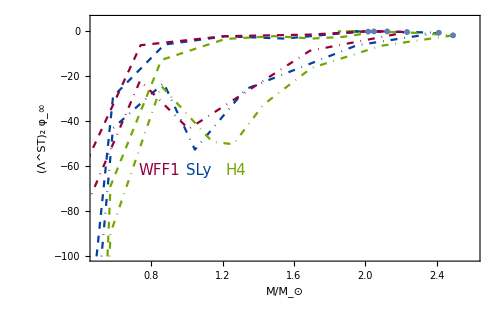

```mathematica
Show[{Table[ListLinePlot[Table[{massradJordT[[p]][[β]][[1]][[All,2]][[h]],((ⅇ^(βvals[[β]] φinfvals[[1]]^2))/(2(-βvals[[β]])))((MultipoleScalarNoES[[p]][[β]][[1]])/TidalTensorNoES[[p]][[β]][[1]])[[h]]*(massradJordT[[p]][[β]][[1]][[All,2]][[h]])^-5},{h,1,Length[ρvals]}],PlotStyle->{StyleList[[β]],ColorList[[p]]},PlotRange->{{0.5,2.6},{5,-100}},If[p==3,PlotLegends->Placed[LineLegend[{StyleList[[β]]},{Style[βnamesList[[β]],15]}],{Right,Bottom}],PlotLegends->Automatic],Epilog->{Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.23,0.4}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.31,0.4}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.4,0.4}],{1,1}]},Frame->True,FrameLabel->{{Style["(Λ^ST)_2 φ_∞","Latin Modern Roman",19,Black],None},{Style["M/M_⊙","Latin Modern Roman",18,Black],Style["Jordan frame φ_∞=10^-3","Latin Modern Roman",18,Black]}},FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},ImageSize->500],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}],Table[ListLinePlot[Table[{massradGRT[[p]][[1]][[1]][[All,2]][[h]],((MultipoleScalarNoETGR[[p]])/TidalScalarNoETGR[[p]])[[h]]*(massradGRT[[p]][[1]][[1]][[All,2]][[h]])^-5},{h,1,Length[ρvals]}],PlotStyle->{ColorList[[p]]},PlotRange->{{0.5,2.5},{0,6000}},ImageSize->500],{p,1,Length[EoSIndex]}],Table[ListPlot[{{massradJordT[[p]][[β]][[1]][[All,2]][[MaxPointsSTJordIndex[[p]][[β]][[1]]]],((ⅇ^(βvals[[β]] φinfvals[[1]]^2))/(2(-βvals[[β]])))((MultipoleScalarNoES[[p]][[β]][[1]])/TidalTensorNoES[[p]][[β]][[1]])[[MaxPointsSTJordIndex[[p]][[β]][[1]]]]*(massradJordT[[p]][[β]][[1]][[All,2]][[MaxPointsSTJordIndex[[p]][[β]][[1]]]])^-5}},PlotMarkers->Style[{"x","o"}[[β]],{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}]}//Flatten]
```

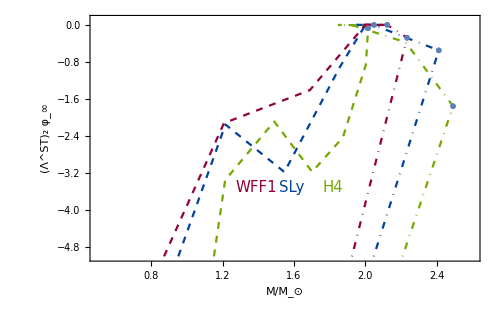

```mathematica
Show[{Table[ListLinePlot[Table[{massradJordT[[p]][[β]][[1]][[All,2]][[h]],((ⅇ^(βvals[[β]] φinfvals[[1]]^2))/(2(-βvals[[β]])))((MultipoleScalarNoES[[p]][[β]][[1]])/TidalTensorNoES[[p]][[β]][[1]])[[h]]*(massradJordT[[p]][[β]][[1]][[All,2]][[h]])^-5},{h,1,Length[ρvals]}],PlotStyle->{StyleList[[β]],ColorList[[p]]},PlotRange->{{0.5,2.6},{0.1,-5}},If[p==3,PlotLegends->Placed[LineLegend[{StyleList[[β]]},{Style[βnamesList[[β]],15]}],{Left,Top}],PlotLegends->Automatic],Epilog->{Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.48,0.33}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.55,0.33}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.65,0.33}],{1,1}]},Frame->True,FrameLabel->{{Style["(Λ^ST)_2 φ_∞","Latin Modern Roman",19,Black],None},{Style["M/M_⊙","Latin Modern Roman",18,Black],Style["Jordan frame φ_∞=10^-3","Latin Modern Roman",18,Black]}},FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},ImageSize->500],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}],Table[ListLinePlot[Table[{massradGRT[[p]][[1]][[1]][[All,2]][[h]],((MultipoleScalarNoETGR[[p]])/TidalScalarNoETGR[[p]])[[h]]*(massradGRT[[p]][[1]][[1]][[All,2]][[h]])^-5},{h,1,Length[ρvals]}],PlotStyle->{ColorList[[p]]},PlotRange->{{0.5,2.5},{0,6000}},ImageSize->500],{p,1,Length[EoSIndex]}],Table[ListPlot[{{massradJordT[[p]][[β]][[1]][[All,2]][[MaxPointsSTJordIndex[[p]][[β]][[1]]]],((ⅇ^(βvals[[β]] φinfvals[[1]]^2))/(2(-βvals[[β]])))((MultipoleScalarNoES[[p]][[β]][[1]])/TidalTensorNoES[[p]][[β]][[1]])[[MaxPointsSTJordIndex[[p]][[β]][[1]]]]*(massradJordT[[p]][[β]][[1]][[All,2]][[MaxPointsSTJordIndex[[p]][[β]][[1]]]])^-5}},PlotMarkers->Style[{"x","o"}[[β]],{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}]}//Flatten]
```

```mathematica
(* l=3 *)
```

```mathematica
(* Tensor *)
```

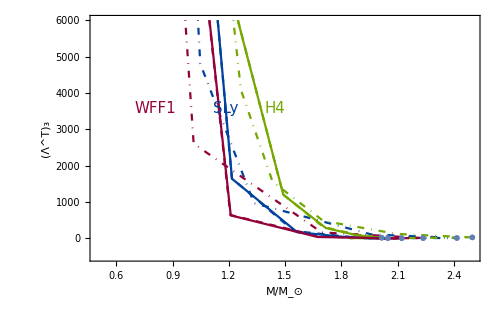

```mathematica
Show[{Table[ListLinePlot[Table[{massradADMT[[p]][[β]][[1]][[All,2]][[h]],((MultipoleTensorNoESl3[[p]][[β]][[1]])/TidalTensorNoESl3[[p]][[β]][[1]])[[h]]*(massradADMT[[p]][[β]][[1]][[All,2]][[h]])^-7},{h,1,Length[ρvals]}],PlotStyle->{StyleList[[β]],ColorList[[p]]},PlotRange->{{0.5,2.5},{-500,6000}},If[p==3,PlotLegends->Placed[LineLegend[{StyleList[[β]]},{Style[βnamesList[[β]],15]}],{Right,Top}],PlotLegends->Automatic],Epilog->{Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.22,0.65}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.38,0.65}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.5,0.65}],{1,1}]},Frame->True,FrameLabel->{{Style["(Λ^T)_3","Latin Modern Roman",19,Black],None},{Style["M/M_⊙","Latin Modern Roman",18,Black],Style["Einstein frame φ_∞=10^-3","Latin Modern Roman",18,Black]}},FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},ImageSize->500],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}],Table[ListLinePlot[Table[{massradGRT[[p]][[1]][[1]][[All,2]][[h]],((MultipoleTensorNoESGRl3[[p]])/TidalTensorNoESGRl3[[p]])[[h]]*(massradGRT[[p]][[1]][[1]][[All,2]][[h]])^-7},{h,1,Length[ρvals]}],PlotStyle->{ColorList[[p]]},PlotRange->{{0.5,2.5},{0,6000}},ImageSize->500],{p,1,Length[EoSIndex]}],Table[ListPlot[{{massradADMT[[p]][[β]][[1]][[All,2]][[MaxPointsSTEinstIndex[[p]][[β]][[1]]]],((MultipoleTensorNoESl3[[p]][[β]][[1]])/TidalTensorNoESl3[[p]][[β]][[1]])[[MaxPointsSTEinstIndex[[p]][[β]][[1]]]]*(massradADMT[[p]][[β]][[1]][[All,2]][[MaxPointsSTEinstIndex[[p]][[β]][[1]]]])^-7}},PlotMarkers->Style[{"x","o"}[[β]],{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}]}//Flatten]
```

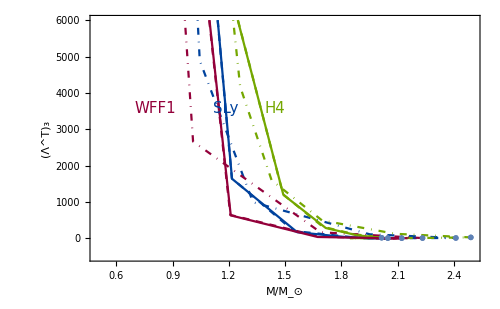

```mathematica
Show[{Table[ListLinePlot[Table[{massradJordT[[p]][[β]][[1]][[All,2]][[h]],((MultipoleTensorNoESl3[[p]][[β]][[1]])/TidalTensorNoESl3[[p]][[β]][[1]])[[h]]*(massradJordT[[p]][[β]][[1]][[All,2]][[h]])^-7},{h,1,Length[ρvals]}],PlotStyle->{StyleList[[β]],ColorList[[p]]},PlotRange->{{0.5,2.5},{-500,6000}},If[p==3,PlotLegends->Placed[LineLegend[{StyleList[[β]]},{Style[βnamesList[[β]],15]}],{Right,Top}],PlotLegends->Automatic],Epilog->{Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.22,0.65}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.38,0.65}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.5,0.65}],{1,1}]},Frame->True,FrameLabel->{{Style["(Λ^T)_3","Latin Modern Roman",19,Black],None},{Style["M/M_⊙","Latin Modern Roman",18,Black],Style["Jordan frame φ_∞=10^-3","Latin Modern Roman",18,Black]}},FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},ImageSize->500],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}],Table[ListLinePlot[Table[{massradGRT[[p]][[1]][[1]][[All,2]][[h]],((MultipoleTensorNoESGRl3[[p]])/TidalTensorNoESGRl3[[p]])[[h]]*(massradGRT[[p]][[1]][[1]][[All,2]][[h]])^-7},{h,1,Length[ρvals]}],PlotStyle->{ColorList[[p]]},PlotRange->{{0.5,2.5},{0,6000}},ImageSize->500],{p,1,Length[EoSIndex]}],Table[ListPlot[{{massradJordT[[p]][[β]][[1]][[All,2]][[MaxPointsSTJordIndex[[p]][[β]][[1]]]],((MultipoleTensorNoESl3[[p]][[β]][[1]])/TidalTensorNoESl3[[p]][[β]][[1]])[[MaxPointsSTJordIndex[[p]][[β]][[1]]]]*(massradJordT[[p]][[β]][[1]][[All,2]][[MaxPointsSTJordIndex[[p]][[β]][[1]]]])^-7}},PlotMarkers->Style[{"x","o"}[[β]],{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}]}//Flatten]
```

```mathematica
(* Scalar *)
```

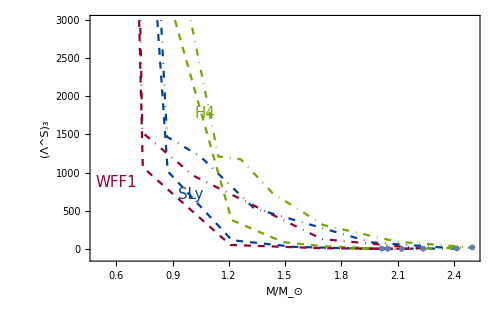

```mathematica
Show[{Table[ListLinePlot[Table[{massradADMT[[p]][[β]][[1]][[All,2]][[h]],((MultipoleScalarNoETl3[[p]][[β]][[1]])/TidalScalarNoETl3[[p]][[β]][[1]])[[h]]*(massradADMT[[p]][[β]][[1]][[All,2]][[h]])^-7},{h,1,Length[ρvals]}],PlotStyle->{StyleList[[β]],ColorList[[p]]},PlotRange->{{0.5,2.5},{-100,3000}},If[p==3,PlotLegends->Placed[LineLegend[{StyleList[[β]]},{Style[βnamesList[[β]],15]}],{Right,Top}],PlotLegends->Automatic],Epilog->{Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.12,0.35}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.29,0.3}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.32,0.63}],{1,1}]},Frame->True,FrameLabel->{{Style["(Λ^S)_3","Latin Modern Roman",19,Black],None},{Style["M/M_⊙","Latin Modern Roman",18,Black],Style["Einstein frame φ_∞=10^-3","Latin Modern Roman",18,Black]}},FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},ImageSize->500],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}],Table[ListPlot[{{massradADMT[[p]][[β]][[1]][[All,2]][[MaxPointsSTEinstIndex[[p]][[β]][[1]]]],((MultipoleScalarNoETl3[[p]][[β]][[1]])/TidalScalarNoETl3[[p]][[β]][[1]])[[MaxPointsSTEinstIndex[[p]][[β]][[1]]]]*(massradADMT[[p]][[β]][[1]][[All,2]][[MaxPointsSTEinstIndex[[p]][[β]][[1]]]])^-7}},PlotMarkers->Style[{"x","o"}[[β]],{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}]}//Flatten]
```

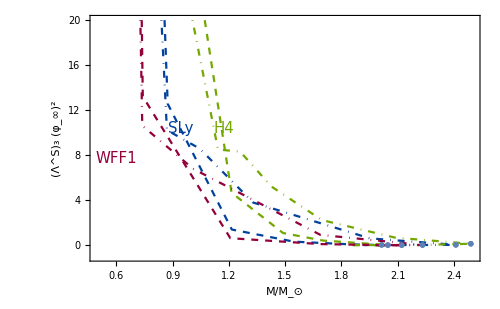

```mathematica
Show[{Table[ListLinePlot[Table[{massradJordT[[p]][[β]][[1]][[All,2]][[h]],((MultipoleScalarNoETl3[[p]][[β]][[1]])/TidalScalarNoETl3[[p]][[β]][[1]])[[h]]*((ⅇ^(βvals[[β]] φinfvals[[1]]^2))/(2(-βvals[[β]])))^2*(massradJordT[[p]][[β]][[1]][[All,2]][[h]])^-7},{h,1,Length[ρvals]}],PlotStyle->{StyleList[[β]],ColorList[[p]]},PlotRange->{{0.5,2.5},{-1,20}},If[p==3,PlotLegends->Placed[LineLegend[{StyleList[[β]]},{Style[βnamesList[[β]],15]}],{Right,Top}],PlotLegends->Automatic],Epilog->{Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.12,0.45}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.265,0.57}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.37,0.57}],{1,1}]},Frame->True,FrameLabel->{{Style["(Λ^S)_3 (φ_∞)^2","Latin Modern Roman",19,Black],None},{Style["M/M_⊙","Latin Modern Roman",18,Black],Style["Jordan frame φ_∞=10^-3","Latin Modern Roman",18,Black]}},FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},ImageSize->500],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}],Table[ListPlot[{{massradJordT[[p]][[β]][[1]][[All,2]][[MaxPointsSTJordIndex[[p]][[β]][[1]]]],((MultipoleScalarNoETl3[[p]][[β]][[1]])/TidalScalarNoETl3[[p]][[β]][[1]])[[MaxPointsSTJordIndex[[p]][[β]][[1]]]]*(massradJordT[[p]][[β]][[1]][[All,2]][[MaxPointsSTJordIndex[[p]][[β]][[1]]]])^-7((ⅇ^(βvals[[β]] φinfvals[[1]]^2))/(2(-βvals[[β]])))^2}},PlotMarkers->Style[{"x","o"}[[β]],{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}]}//Flatten]
```

```mathematica
(* Scalar-Tensor *)
```

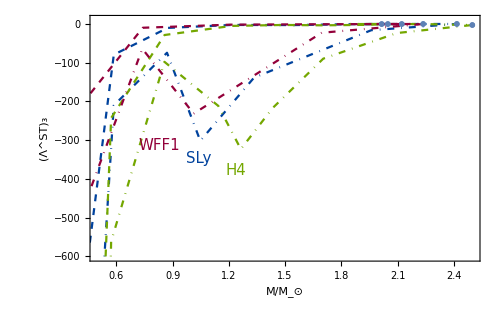

```mathematica
Show[{Table[ListLinePlot[Table[{massradADMT[[p]][[β]][[1]][[All,2]][[h]],((MultipoleScalarNoETl3[[p]][[β]][[1]])/TidalTensorNoESl3[[p]][[β]][[1]])[[h]]*(massradADMT[[p]][[β]][[1]][[All,2]][[h]])^-7},{h,1,Length[ρvals]}],PlotStyle->{StyleList[[β]],ColorList[[p]]},PlotRange->{{0.5,2.5},{10,-600}},If[p==3,PlotLegends->Placed[LineLegend[{StyleList[[β]]},{Style[βnamesList[[β]],15]}],{Right,Bottom}],PlotLegends->Automatic],Epilog->{Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.23,0.5}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.31,0.45}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.4,0.4}],{1,1}]},Frame->True,FrameLabel->{{Style["(Λ^ST)_3","Latin Modern Roman",19,Black],None},{Style["M/M_⊙","Latin Modern Roman",18,Black],Style["Einstein frame φ_∞=10^-3","Latin Modern Roman",18,Black]}},FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},ImageSize->500],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}],Table[ListPlot[{{massradADMT[[p]][[β]][[1]][[All,2]][[MaxPointsSTEinstIndex[[p]][[β]][[1]]]],((MultipoleScalarNoETl3[[p]][[β]][[1]])/TidalTensorNoESl3[[p]][[β]][[1]])[[MaxPointsSTEinstIndex[[p]][[β]][[1]]]]*(massradADMT[[p]][[β]][[1]][[All,2]][[MaxPointsSTEinstIndex[[p]][[β]][[1]]]])^-7}},PlotMarkers->Style[{"x","o"}[[β]],{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}]}//Flatten]
```

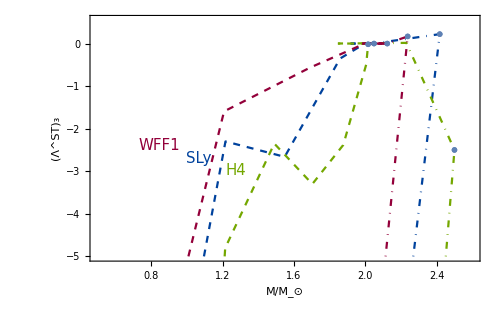

```mathematica
Show[{Table[ListLinePlot[Table[{massradADMT[[p]][[β]][[1]][[All,2]][[h]],((MultipoleScalarNoETl3[[p]][[β]][[1]])/TidalTensorNoESl3[[p]][[β]][[1]])[[h]]*(massradADMT[[p]][[β]][[1]][[All,2]][[h]])^-7},{h,1,Length[ρvals]}],PlotStyle->{StyleList[[β]],ColorList[[p]]},PlotRange->{{0.5,2.6},{0.55,-5}},If[p==3,PlotLegends->Placed[LineLegend[{StyleList[[β]]},{Style[βnamesList[[β]],15]}],{Left,Top}],PlotLegends->Automatic],Epilog->{Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.23,0.5}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.31,0.45}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.4,0.4}],{1,1}]},Frame->True,FrameLabel->{{Style["(Λ^ST)_3","Latin Modern Roman",19,Black],None},{Style["M/M_⊙","Latin Modern Roman",18,Black],Style["Einstein frame φ_∞=10^-3","Latin Modern Roman",18,Black]}},FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},ImageSize->500],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}],Table[ListPlot[{{massradADMT[[p]][[β]][[1]][[All,2]][[MaxPointsSTEinstIndex[[p]][[β]][[1]]]],((MultipoleScalarNoETl3[[p]][[β]][[1]])/TidalTensorNoESl3[[p]][[β]][[1]])[[MaxPointsSTEinstIndex[[p]][[β]][[1]]]]*(massradADMT[[p]][[β]][[1]][[All,2]][[MaxPointsSTEinstIndex[[p]][[β]][[1]]]])^-7}},PlotMarkers->Style[{"x","o"}[[β]],{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}]}//Flatten]
```

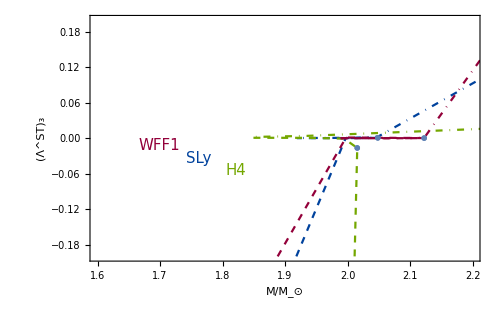

```mathematica
Show[{Table[ListLinePlot[Table[{massradADMT[[p]][[β]][[1]][[All,2]][[h]],((MultipoleScalarNoETl3[[p]][[β]][[1]])/TidalTensorNoESl3[[p]][[β]][[1]])[[h]]*(massradADMT[[p]][[β]][[1]][[All,2]][[h]])^-7},{h,1,Length[ρvals]}],PlotStyle->{StyleList[[β]],ColorList[[p]]},PlotRange->{{1.6,2.2},{0.2,-0.2}},If[p==3,PlotLegends->Placed[LineLegend[{StyleList[[β]]},{Style[βnamesList[[β]],15]}],{Left,Top}],PlotLegends->Automatic],Epilog->{Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.23,0.5}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.31,0.45}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.4,0.4}],{1,1}]},Frame->True,FrameLabel->{{Style["(Λ^ST)_3","Latin Modern Roman",19,Black],None},{Style["M/M_⊙","Latin Modern Roman",18,Black],Style["Einstein frame φ_∞=10^-3","Latin Modern Roman",18,Black]}},FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},ImageSize->500],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}],Table[ListPlot[{{massradADMT[[p]][[β]][[1]][[All,2]][[MaxPointsSTEinstIndex[[p]][[β]][[1]]]],((MultipoleScalarNoETl3[[p]][[β]][[1]])/TidalTensorNoESl3[[p]][[β]][[1]])[[MaxPointsSTEinstIndex[[p]][[β]][[1]]]]*(massradADMT[[p]][[β]][[1]][[All,2]][[MaxPointsSTEinstIndex[[p]][[β]][[1]]]])^-7}},PlotMarkers->Style[{"x","o"}[[β]],{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}]}//Flatten]
```

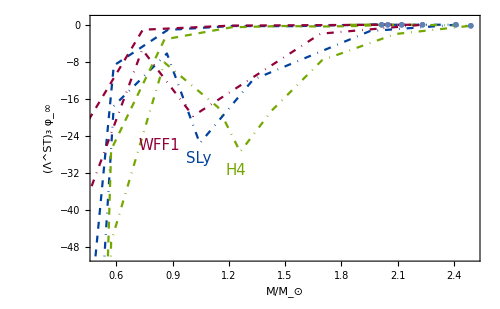

```mathematica
Show[{Table[ListLinePlot[Table[{massradJordT[[p]][[β]][[1]][[All,2]][[h]],((MultipoleScalarNoETl3[[p]][[β]][[1]])/TidalTensorNoESl3[[p]][[β]][[1]])[[h]]*((ⅇ^(βvals[[β]] φinfvals[[1]]^2))/(2(-βvals[[β]])))*(massradJordT[[p]][[β]][[1]][[All,2]][[h]])^-7},{h,1,Length[ρvals]}],PlotStyle->{StyleList[[β]],ColorList[[p]]},PlotRange->{{0.5,2.5},{1,-50}},If[p==3,PlotLegends->Placed[LineLegend[{StyleList[[β]]},{Style[βnamesList[[β]],15]}],{Right,Bottom}],PlotLegends->Automatic],Epilog->{Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.23,0.5}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.31,0.45}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.4,0.4}],{1,1}]},Frame->True,FrameLabel->{{Style["(Λ^ST)_3 φ_∞","Latin Modern Roman",19,Black],None},{Style["M/M_⊙","Latin Modern Roman",18,Black],Style["Jordan frame φ_∞=10^-3","Latin Modern Roman",18,Black]}},FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},ImageSize->500],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}],Table[ListPlot[{{massradJordT[[p]][[β]][[1]][[All,2]][[MaxPointsSTJordIndex[[p]][[β]][[1]]]],((MultipoleScalarNoETl3[[p]][[β]][[1]])/TidalTensorNoESl3[[p]][[β]][[1]])[[MaxPointsSTJordIndex[[p]][[β]][[1]]]]*(massradJordT[[p]][[β]][[1]][[All,2]][[MaxPointsSTJordIndex[[p]][[β]][[1]]]])^-7((ⅇ^(βvals[[β]] φinfvals[[1]]^2))/(2(-βvals[[β]])))}},PlotMarkers->Style[{"x","o"}[[β]],{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}]}//Flatten]
```

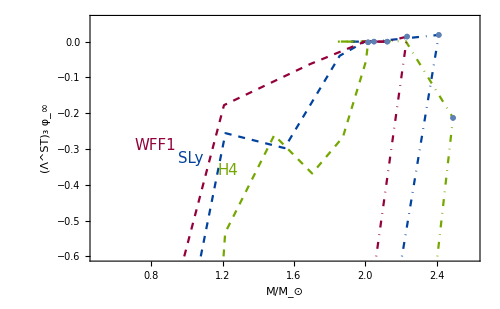

```mathematica
Show[{Table[ListLinePlot[Table[{massradJordT[[p]][[β]][[1]][[All,2]][[h]],((MultipoleScalarNoETl3[[p]][[β]][[1]])/TidalTensorNoESl3[[p]][[β]][[1]])[[h]]*((ⅇ^(βvals[[β]] φinfvals[[1]]^2))/(2(-βvals[[β]])))*(massradJordT[[p]][[β]][[1]][[All,2]][[h]])^-7},{h,1,Length[ρvals]}],PlotStyle->{StyleList[[β]],ColorList[[p]]},PlotRange->{{0.5,2.6},{0.06,-0.6}},If[p==3,PlotLegends->Placed[LineLegend[{StyleList[[β]]},{Style[βnamesList[[β]],15]}],{Left,Top}],PlotLegends->Automatic],Epilog->{Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.22,0.5}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.29,0.45}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.38,0.4}],{1,1}]},Frame->True,FrameLabel->{{Style["(Λ^ST)_3 φ_∞","Latin Modern Roman",19,Black],None},{Style["M/M_⊙","Latin Modern Roman",18,Black],Style["Jordan frame φ_∞=10^-3","Latin Modern Roman",18,Black]}},FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},ImageSize->500],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}],Table[ListPlot[{{massradJordT[[p]][[β]][[1]][[All,2]][[MaxPointsSTJordIndex[[p]][[β]][[1]]]],((MultipoleScalarNoETl3[[p]][[β]][[1]])/TidalTensorNoESl3[[p]][[β]][[1]])[[MaxPointsSTJordIndex[[p]][[β]][[1]]]]*(massradJordT[[p]][[β]][[1]][[All,2]][[MaxPointsSTJordIndex[[p]][[β]][[1]]]])^-7((ⅇ^(βvals[[β]] φinfvals[[1]]^2))/(2(-βvals[[β]])))}},PlotMarkers->Style[{"x","o"}[[β]],{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}],PlotRange->All],{p,1,Length[EoSIndex]},{β,1,Length[βvals]}]}//Flatten]
```

### Fitting for the polynomial w(φ_∞,Q)

```mathematica
FindFit[Table[{massradADMT[[1]][[1]][[φinf]][[All,2]][[h]],massradADMT[[1]][[1]][[1]][[All,2]][[h]],massradADMT[[1]][[1]][[φinf]][[All,1]][[h]]*km,massradADMT[[1]][[1]][[1]][[All,1]][[h]]*km,ChargeTableT[[1]][[1]][[φinf]][[All,2]][[h]],ChargeTableT[[1]][[1]][[1]][[All,2]][[h]],((MultipoleScalarNoES[[1]][[1]][[φinf]])/TidalTensorNoES[[1]][[1]][[φinf]])[[h]]/(((MultipoleScalarNoES[[1]][[1]][[1]])/TidalTensorNoES[[1]][[1]][[1]])[[h]])},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}][[2]],1/( φinfvals[[1]]-c1   q1)( φinfvals[[2]]- c2   q),{c1,c2},{M,M1,R,R1,q,q1}]
```

{c1→0.0959346,c2→0.0958638}

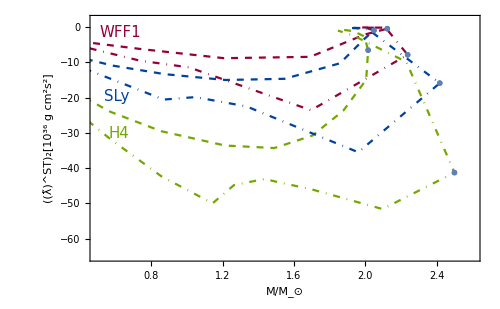

```mathematica
Show[{Table[ListLinePlot[Table[{massradADMT[[p]][[β]][[φinf]][[All,2]][[h]],((MultipoleScalarNoES[[p]][[β]][[φinf]])/TidalTensorNoES[[p]][[β]][[φinf]])[[h]]/( φinfvals[[φinf]]-c1  q1)(msunincm)^5 Gconst^-1(10^-36)/.{c1->0.0957}/.q1->ChargeTableT[[p]][[β]][[φinf]][[All,2]][[h]]},{h,1,Length[ρvals]}],PlotRange->{{0.5,2.6},{2,-65}},PlotStyle->{StyleList[[β]],ColorList[[p]]},If[p==3,PlotLegends->Placed[LineLegend[{StyleList[[β]]},{Style[βnamesList[[β]],15]}],{Left,Bottom}],PlotLegends->Automatic],Epilog->{Text[Style["WFF1",15,RGBColor["#93003a"]],Scaled[{0.13,0.96}],{1,1}],Text[Style["SLy",15,RGBColor["#00429d"]],Scaled[{0.1,0.7}],{1,1}],Text[Style["H4",15,RGBColor["#74a700"]],Scaled[{0.1,0.55}],{1,1}]},Frame->True,FrameLabel->{{Style["((λ̃)^ST)_2[10^36 g cm^2s^2]","Latin Modern Roman",19,Black],None},{Style["M/M_⊙","Latin Modern Roman",18,Black],None}},FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},ImageSize->500],{φinf,1,1},{β,1,Length[βvals]},{p,1,Length[EoSIndex]}]//Flatten,Table[ListPlot[{{massradADMT[[p]][[β]][[φinf]][[All,2]][[MaxPointsSTEinstIndex[[p]][[β]][[φinf]]]],((MultipoleScalarNoES[[p]][[β]][[φinf]])/TidalTensorNoES[[p]][[β]][[φinf]])[[MaxPointsSTEinstIndex[[p]][[β]][[φinf]]]]/( φinfvals[[φinf]]-c1  q1)(msunincm)^5 Gconst^-1(10^-36)/.{c1->0.0957}/.q1->ChargeTableT[[p]][[β]][[φinf]][[All,2]][[MaxPointsSTEinstIndex[[p]][[β]][[φinf]]]]}},PlotRange->{{0.5,2.6},{2,-60}},PlotMarkers->Style[{"x","o"}[[β]],{{RGBColor["#00429d"],RGBColor["#74a700"],RGBColor["#93003a"]}[[p]],14}]],{φinf,1,1},{β,1,Length[βvals]},{p,1,Length[EoSIndex]}]//Flatten}//Flatten]
```

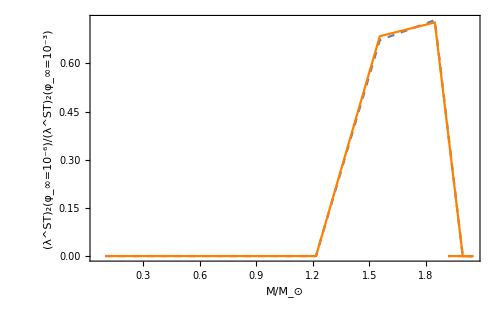

```mathematica
Show[ListLinePlot[Table[{massradADMT[[1]][[1]][[φinf]][[All,2]][[h]],1/( φinfvals[[1]]-c1  q1)( φinfvals[[φinf]]-c2  q)/.{c1->0.0957,c2->0.0957}/.q1->ChargeTableT[[1]][[1]][[1]][[All,2]][[h]]/.q->ChargeTableT[[1]][[1]][[φinf]][[All,2]][[h]]/.M1->massradADMT[[1]][[1]][[1]][[All,2]][[h]]/.M->massradADMT[[1]][[1]][[φinf]][[All,2]][[h]]/.R1->massradADMT[[1]][[1]][[1]][[All,1]][[h]]*km/.R->massradADMT[[1]][[1]][[φinf]][[All,1]][[h]]*km},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}][[3]],PlotRange->Full,PlotStyle->Dashed,PlotLegends->Placed[LineLegend[{Dashed},{Style["Fit",15]}],{Left,Top}],PlotLegends->Automatic,Frame->True,FrameLabel->{{Style["(λ^ST)_2(φ_∞=10^-6)/(λ^ST)_2(φ_∞=10^-3)","Latin Modern Roman",19,Black],None},{Style["M/M_⊙","Latin Modern Roman",18,Black],None}},FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},ImageSize->500],ListLinePlot[Table[{massradADMT[[1]][[1]][[φinf]][[All,2]][[h]],((MultipoleScalarNoES[[1]][[1]][[φinf]])/TidalTensorNoES[[1]][[1]][[φinf]])[[h]]/(((MultipoleScalarNoES[[1]][[1]][[1]])/TidalTensorNoES[[1]][[1]][[1]])[[h]])},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}][[3]],PlotStyle->Orange,PlotRange->Full,PlotLegends->Placed[LineLegend[{Dashing[1]},{Style["Numerical",15]}],{Left,Top}],PlotLegends->Automatic]]
```

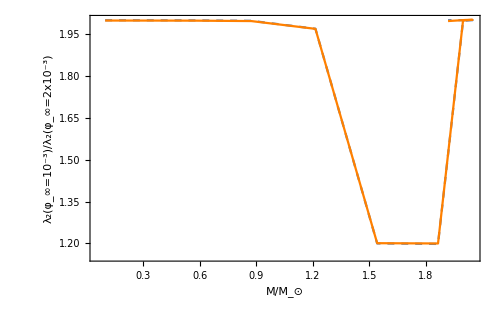

```mathematica
Show[ListLinePlot[Table[{massradADMT[[1]][[1]][[φinf]][[All,2]][[h]],1/( φinfvals[[1]]-c1  Sum[(q1*M1)^(2n+1),{n,0,∞}])( φinfvals[[φinf]]- c2  Sum[(q*M)^(2n+1),{n,0,∞}])/.{c1->7.4807057390194*^8,c2->7.48414501333881*^8}/.q1->ChargeTableT[[1]][[1]][[1]][[All,2]][[h]]/.q->ChargeTableT[[1]][[1]][[φinf]][[All,2]][[h]]/.M1->massradADMT[[1]][[1]][[1]][[All,2]][[h]]/.M->massradADMT[[1]][[1]][[φinf]][[All,2]][[h]]/.R1->massradADMT[[1]][[1]][[1]][[All,1]][[h]]*km/.R->massradADMT[[1]][[1]][[φinf]][[All,1]][[h]]*km},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}][[2]],PlotRange->Full,PlotStyle->Dashed,PlotLegends->Placed[LineLegend[{Dashed},{Style["Fit",15]}],{Left,Bottom}],PlotLegends->Automatic,Frame->True,FrameLabel->{{Style["λ_2(φ_∞=10^-3)/λ_2(φ_∞=2x10^-3)","Latin Modern Roman",19,Black],None},{Style["M/M_⊙","Latin Modern Roman",18,Black],Style["Einstein frame","Latin Modern Roman",18,Black]}},FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},ImageSize->500],ListLinePlot[Table[{massradADMT[[1]][[1]][[φinf]][[All,2]][[h]],((MultipoleScalarNoES[[1]][[1]][[φinf]])/TidalTensorNoES[[1]][[1]][[φinf]])[[h]]/(((MultipoleScalarNoES[[1]][[1]][[1]])/TidalTensorNoES[[1]][[1]][[1]])[[h]])},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}][[2]],PlotStyle->Orange,PlotRange->Full,PlotLegends->Placed[LineLegend[{Dashing[1]},{Style["Numerical",15]}],{Left,Bottom}],PlotLegends->Automatic]]
```

### Error estimation (takes long, don’t run if not needed)

#### λ vs r_∞

```mathematica
(* We parametrize everything in terms of Subscript[r, ∞]*)
```

```mathematica
(* Here the boundary condition with index b=2 would correspond to the one adding more or less terms in the series expansion at infinity, therefore allowing to play with both Subscript[r, ∞] and the series solution. In this section we will omit the analysis of the terms in the the series expansion, so we will use b=1. Also we fix l=2. *)
```

```mathematica
H0φpsolInfinitytoSurfacel2OnlyESInf[b_?NumericQ,p_?NumericQ,β_?NumericQ,φinf_?NumericQ,h_?NumericQ,rinfS_?NumericQ]:=NDSolve[SetPrecision[{r^2 mastereqwithbackOUT==0, eqpH==0,H0[rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]=={H0OnlyES,H0OnlyES2}[[b]]/.r->rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km,H0'[rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]==D[{H0OnlyES,H0OnlyES2}[[b]],r]/.r->rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km,φp[rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]=={φpOnlyES,φpOnlyES2}[[b]]/.r->rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km,φp'[rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]==D[{φpOnlyES,φpOnlyES2}[[b]],r]/.r->rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km}/.φ0solOUTSolsT[[p]][[β]][[φinf]][[h]] /.q->ChargeTableT[[p]][[β]][[φinf]][[All,2]][[h]]/.M->ADMMassTableT[[p]][[β]][[φinf]][[h]]/.l->2/.GN->1//Flatten//N,100],{φp,H0},{r, SetPrecision[rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km,100],SetPrecision[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km,100]},PrecisionGoal->15,AccuracyGoal->15,WorkingPrecision->25];
H0φpsolInfinitytoSurfacel2OnlyQSInf[b_?NumericQ,p_?NumericQ,β_?NumericQ,φinf_?NumericQ,h_?NumericQ,rinfS_?NumericQ]:=NDSolve[SetPrecision[{r^2 mastereqwithbackOUT==0,eqpH==0,H0[rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]=={H0OnlyQS,H0OnlyQS2}[[b]]/.r->rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km,H0'[rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]==D[{H0OnlyQS,H0OnlyQS2}[[b]],r]/.r->rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km,φp[rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]=={φpOnlyQS,φpOnlyQS2}[[b]]/.r->rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km,φp'[rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]==D[{φpOnlyQS,φpOnlyQS2}[[b]],r]/.r->rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km} /.φ0solOUTSolsT[[p]][[β]][[φinf]][[h]]/.q->ChargeTableT[[p]][[β]][[φinf]][[All,2]][[h]]/.M->ADMMassTableT[[p]][[β]][[φinf]][[h]]/.l->2/.GN->1//Flatten//N,100],{φp,H0},{r, SetPrecision[rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km,100],SetPrecision[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km,100]},PrecisionGoal->15,AccuracyGoal->15,WorkingPrecision->25];
H0φpsolInfinitytoSurfacel2OnlyETInf[b_?NumericQ,p_?NumericQ,β_?NumericQ,φinf_?NumericQ,h_?NumericQ,rinfS_?NumericQ]:=NDSolve[SetPrecision[{r^2 mastereqwithbackOUT==0, eqpH==0,φp[rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]=={φpOnlyET,φpOnlyET2}[[b]]/.r->rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km,φp'[rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]==D[{φpOnlyET,φpOnlyET2}[[b]],r]/.r->rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km,H0[rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]=={H0OnlyET,H0OnlyET2}[[b]]/.r->rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km,H0'[rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]==D[{H0OnlyET,H0OnlyET2}[[b]],r]/.r->rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km} /.q->ChargeTableT[[p]][[β]][[φinf]][[All,2]][[h]]/.M->ADMMassTableT[[p]][[β]][[φinf]][[h]]/.φ0solOUTSolsT[[p]][[β]][[φinf]][[h]]/.l->2/.GN->1//Flatten//N,100],{φp,H0},{r, SetPrecision[rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km,100],SetPrecision[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km,100]},PrecisionGoal->15,AccuracyGoal->15,WorkingPrecision->25];
H0φpsolInfinitytoSurfacel2OnlyQTInf[b_?NumericQ,p_?NumericQ,β_?NumericQ,φinf_?NumericQ,h_?NumericQ,rinfS_?NumericQ]:=NDSolve[SetPrecision[{r^2 mastereqwithbackOUT==0, eqpH==0,H0[rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]=={H0OnlyQT,H0OnlyQT2}[[b]]/.r->rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km,H0'[rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]==D[{H0OnlyQT,H0OnlyQT2}[[b]],r]/.r->rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km,φp[rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]=={φpOnlyQT,φpOnlyQT2}[[b]]/.r->rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km,φp'[rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]==D[{φpOnlyQT,φpOnlyQT2}[[b]],r]/.r->rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km}/.q->ChargeTableT[[p]][[β]][[φinf]][[All,2]][[h]]/.M->ADMMassTableT[[p]][[β]][[φinf]][[h]]/.φ0solOUTSolsT[[p]][[β]][[φinf]][[h]]/.l->2/.GN->1//Flatten//N,100],{φp,H0},{r,  SetPrecision[rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km,100],SetPrecision[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km,100]},PrecisionGoal->15,AccuracyGoal->15,WorkingPrecision->25];
H0φpsolOrigintoSurfaceTablel2NoTensor={H0φpsolOrigintoSurfaceTablel2NoTensorφ1};
H0φpsolOrigintoSurfaceTablel2NoScalar={H0φpsolOrigintoSurfaceTablel2NoScalarφ1};
φpINNoT=Table[Evaluate[φp[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolOrigintoSurfaceTablel2NoTensor[[φinf]][[p]][[β]][[h]]],{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
φpINNoS=Table[Evaluate[φp[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolOrigintoSurfaceTablel2NoScalar[[φinf]][[p]][[β]][[h]]],{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
φppINNoT=Table[Evaluate[φp'[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolOrigintoSurfaceTablel2NoTensor[[φinf]][[p]][[β]][[h]]],{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
φppINNoS=Table[Evaluate[φp'[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolOrigintoSurfaceTablel2NoScalar[[φinf]][[p]][[β]][[h]]],{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
H0INNoT=Table[Evaluate[H0[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolOrigintoSurfaceTablel2NoTensor[[φinf]][[p]][[β]][[h]]],{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
H0INNoS=Table[Evaluate[H0[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolOrigintoSurfaceTablel2NoScalar[[φinf]][[p]][[β]][[h]]],{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
H0pINNoT=Table[Evaluate[H0'[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolOrigintoSurfaceTablel2NoTensor[[φinf]][[p]][[β]][[h]]],{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
H0pINNoS=Table[Evaluate[H0'[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolOrigintoSurfaceTablel2NoScalar[[φinf]][[p]][[β]][[h]]],{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
ConstNoETInf[b_?NumericQ,rinfS_?NumericQ,p_?NumericQ,β_?NumericQ,φinf_?NumericQ,h_?NumericQ]:=Solve[{cIN1 φpINNoT[[p]][[β]][[φinf]][[h]]+cIN2 φpINNoS[[p]][[β]][[φinf]][[h]] == cOUT1 (Evaluate[φp[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyESInf[b,p,β,φinf,h,rinfS]]//Flatten//First)+ cOUT2 (Evaluate[φp[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyQSInf[b,p,β,φinf,h,rinfS]]//Flatten//First) + cOUT3(Evaluate[φp[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyETInf[b,p,β,φinf,h,rinfS]]//Flatten//First) +cOUT4 (Evaluate[φp[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyQTInf[b,p,β,φinf,h,rinfS]]//Flatten//First),
cIN1 φppINNoT[[p]][[β]][[φinf]][[h]]+cIN2 φppINNoS[[p]][[β]][[φinf]][[h]] == cOUT1 (Evaluate[φp'[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyESInf[b,p,β,φinf,h,rinfS]]//Flatten//First)+ cOUT2 (Evaluate[φp'[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyQSInf[b,p,β,φinf,h,rinfS]]//Flatten//First) + cOUT3 (Evaluate[φp'[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyETInf[b,p,β,φinf,h,rinfS]]//Flatten//First) +cOUT4(Evaluate[φp'[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyQTInf[b,p,β,φinf,h,rinfS]]//Flatten//First),
cIN1 H0INNoT[[p]][[β]][[φinf]][[h]]+cIN2 H0INNoS[[p]][[β]][[φinf]][[h]] == cOUT1 (Evaluate[H0[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyESInf[b,p,β,φinf,h,rinfS]]//Flatten//First)+ cOUT2(Evaluate[H0[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyQSInf[b,p,β,φinf,h,rinfS]]//Flatten//First)+ cOUT3 (Evaluate[H0[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyETInf[b,p,β,φinf,h,rinfS]]//Flatten//First) +cOUT4 (Evaluate[H0[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyQTInf[b,p,β,φinf,h,rinfS]]//Flatten//First),cIN1 H0pINNoT[[p]][[β]][[φinf]][[h]]+cIN2 H0pINNoS[[p]][[β]][[φinf]][[h]] == cOUT1(Evaluate[H0'[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyESInf[b,p,β,φinf,h,rinfS]]//Flatten//First)+ cOUT2(Evaluate[H0'[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyQSInf[b,p,β,φinf,h,rinfS]]//Flatten//First) + cOUT3 (Evaluate[H0'[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyETInf[b,p,β,φinf,h,rinfS]]//Flatten//First) +cOUT4 (Evaluate[H0'[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyQTInf[b,p,β,φinf,h,rinfS]]//Flatten//First)}//Simplify,{cIN2,cOUT1,cOUT2,cOUT4}]/.{cIN1->1,cOUT3->0};

ConstNoESInf[b_?NumericQ,rinfS_?NumericQ,p_?NumericQ,β_?NumericQ,φinf_?NumericQ,h_?NumericQ]:=Solve[{cIN1 φpINNoT[[p]][[β]][[φinf]][[h]]+cIN2 φpINNoS[[p]][[β]][[φinf]][[h]] == cOUT1 (Evaluate[φp[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyESInf[b,p,β,φinf,h,rinfS]]//Flatten//First)+ cOUT2 (Evaluate[φp[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyQSInf[b,p,β,φinf,h,rinfS]]//Flatten//First) + cOUT3 (Evaluate[φp[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyETInf[b,p,β,φinf,h,rinfS]]//Flatten//First)+cOUT4(Evaluate[φp[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyQTInf[b,p,β,φinf,h,rinfS]]//Flatten//First),
cIN1 φppINNoT[[p]][[β]][[φinf]][[h]]+cIN2 φppINNoS[[p]][[β]][[φinf]][[h]] == cOUT1 (Evaluate[φp'[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyESInf[b,p,β,φinf,h,rinfS]]//Flatten//First)+ cOUT2 (Evaluate[φp'[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyQSInf[b,p,β,φinf,h,rinfS]]//Flatten//First) + cOUT3 (Evaluate[φp'[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyETInf[b,p,β,φinf,h,rinfS]]//Flatten//First) +cOUT4 (Evaluate[φp'[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyQTInf[b,p,β,φinf,h,rinfS]]//Flatten//First),
cIN1 H0INNoT[[p]][[β]][[φinf]][[h]]+cIN2 H0INNoS[[p]][[β]][[φinf]][[h]] == cOUT1 (Evaluate[H0[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyESInf[b,p,β,φinf,h,rinfS]]//Flatten//First)+ cOUT2 (Evaluate[H0[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyQSInf[b,p,β,φinf,h,rinfS]]//Flatten//First) + cOUT3 (Evaluate[H0[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyETInf[b,p,β,φinf,h,rinfS]]//Flatten//First)+cOUT4 (Evaluate[H0[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyQTInf[b,p,β,φinf,h,rinfS]]//Flatten//First),cIN1 H0pINNoT[[p]][[β]][[φinf]][[h]]+cIN2 H0pINNoS[[p]][[β]][[φinf]][[h]] == cOUT1(Evaluate[H0'[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyESInf[b,p,β,φinf,h,rinfS]]//Flatten//First)+ cOUT2 (Evaluate[H0'[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyQSInf[b,p,β,φinf,h,rinfS]]//Flatten//First) + cOUT3 (Evaluate[H0'[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyETInf[b,p,β,φinf,h,rinfS]]//Flatten//First)+cOUT4 (Evaluate[H0'[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyQTInf[b,p,β,φinf,h,rinfS]]//Flatten//First)}//Simplify,{cIN2,cOUT3,cOUT2,cOUT4}]/.{cIN1->1,cOUT1->0};
MultipoleScalarNoETInf[b_?NumericQ,rinfS_?NumericQ,p_?NumericQ,β_?NumericQ,φinf_?NumericQ,h_?NumericQ]:=cOUT2*(2!)/((2*2-1)!!)/.ConstNoETInf[b,rinfS,p,β,φinf,h]//Flatten;
TidalScalarNoETInf[b_?NumericQ,rinfS_?NumericQ,p_?NumericQ,β_?NumericQ,φinf_?NumericQ,h_?NumericQ]:=cOUT1*(2!)/.ConstNoETInf[b,rinfS,p,β,φinf,h]//Flatten;
MultipoleTensorNoETInf[b_?NumericQ,rinfS_?NumericQ,p_?NumericQ,β_?NumericQ,φinf_?NumericQ,h_?NumericQ]:=cOUT4*(2!)/(2(2*2-1)!!)/.ConstNoETInf[b,rinfS,p,β,φinf,h]//Flatten;
MultipoleScalarNoESInf[b_?NumericQ,rinfS_?NumericQ,p_?NumericQ,β_?NumericQ,φinf_?NumericQ,h_?NumericQ]:=cOUT2*(2!)/((2*2-1)!!)/.ConstNoESInf[b,rinfS,p,β,φinf,h]//Flatten; 
TidalTensorNoESInf[b_?NumericQ,rinfS_?NumericQ,p_?NumericQ,β_?NumericQ,φinf_?NumericQ,h_?NumericQ]:=cOUT3*1/2(2!)/.ConstNoESInf[b,rinfS,p,β,φinf,h]//Flatten; 
MultipoleTensorNoESInf[b_?NumericQ,rinfS_?NumericQ,p_?NumericQ,β_?NumericQ,φinf_?NumericQ,h_?NumericQ]:=cOUT4*(2!)/(2(2*2-1)!!)/.ConstNoESInf[b,rinfS,p,β,φinf,h]//Flatten;
AbsMinimize[rinfS_?NumericQ,p_?NumericQ,β_?NumericQ,φinf_?NumericQ,h_?NumericQ]:=NIntegrate[(*SetPrecision[*)Abs[(Evaluate[(*(cOUT3/.ConstNoESInf[rinfS,p,β,φinf,h])*)H0[r]/.H0φpsolInfinitytoSurfacel2OnlyETInf[p,β,φinf,h,rinfS]]-H0OnlyET/.q->ChargeTableT[[p]][[β]][[φinf]][[All,2]][[h]]/.M->ADMMassTableT[[p]][[β]][[φinf]][[h]])]^2/.r->k//Flatten,{k,massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km,rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km}]//First;
(*MinTable=Table[{h,c/.FindMinimum[{AbsMinimize[c,1,2,1,h],c>=1},{c}][[2]]},{h,1,Length[ρvals]}]*)
(*rSurfTable=Table[FindMinimum[AbsMinimize[rinfS,p,β,φinf,h],rinfS],{p,1},{β,1},{φinf,1},{h,{23}}];
Return[rSurfTable]*)
```

```mathematica
(* Plots of λ vs Subscript[r, ∞]*)
```

```mathematica
(* l=2 *)
```

```mathematica
TablePlot=Table[{rinfS,MultipoleTensorNoESInf[1,1,rinfS,1,1,1,70]/TidalTensorNoESInf[1,1,rinfS,1,1,1,70]//Flatten//First},{rinfS,2,20,0.5}]
```

{{2.,MultipoleTensorNoESInf[2,1,2.,1,1,1,70]},{2.5,MultipoleTensorNoESInf[2,1,2.5,1,1,1,70]},{3.,MultipoleTensorNoESInf[2,1,3.,1,1,1,70]},{3.5,MultipoleTensorNoESInf[2,1,3.5,1,1,1,70]},{4.,MultipoleTensorNoESInf[2,1,4.,1,1,1,70]},{4.5,MultipoleTensorNoESInf[2,1,4.5,1,1,1,70]},{5.,MultipoleTensorNoESInf[2,1,5.,1,1,1,70]},{5.5,MultipoleTensorNoESInf[2,1,5.5,1,1,1,70]},{6.,MultipoleTensorNoESInf[2,1,6.,1,1,1,70]},{6.5,MultipoleTensorNoESInf[2,1,6.5,1,1,1,70]},{7.,MultipoleTensorNoESInf[2,1,7.,1,1,1,70]},{7.5,MultipoleTensorNoESInf[2,1,7.5,1,1,1,70]},{8.,MultipoleTensorNoESInf[2,1,8.,1,1,1,70]},{8.5,MultipoleTensorNoESInf[2,1,8.5,1,1,1,70]},{9.,MultipoleTensorNoESInf[2,1,9.,1,1,1,70]},{9.5,MultipoleTensorNoESInf[2,1,9.5,1,1,1,70]},{10.,MultipoleTensorNoESInf[2,1,10.,1,1,1,70]},{10.5,MultipoleTensorNoESInf[2,1,10.5,1,1,1,70]},{11.,MultipoleTensorNoESInf[2,1,11.,1,1,1,70]},{11.5,MultipoleTensorNoESInf[2,1,11.5,1,1,1,70]},{12.,MultipoleTensorNoESInf[2,1,12.,1,1,1,70]},{12.5,MultipoleTensorNoESInf[2,1,12.5,1,1,1,70]},{13.,MultipoleTensorNoESInf[2,1,13.,1,1,1,70]},{13.5,MultipoleTensorNoESInf[2,1,13.5,1,1,1,70]},{14.,MultipoleTensorNoESInf[2,1,14.,1,1,1,70]},{14.5,MultipoleTensorNoESInf[2,1,14.5,1,1,1,70]},{15.,MultipoleTensorNoESInf[2,1,15.,1,1,1,70]},{15.5,MultipoleTensorNoESInf[2,1,15.5,1,1,1,70]},{16.,MultipoleTensorNoESInf[2,1,16.,1,1,1,70]},{16.5,MultipoleTensorNoESInf[2,1,16.5,1,1,1,70]},{17.,MultipoleTensorNoESInf[2,1,17.,1,1,1,70]},{17.5,MultipoleTensorNoESInf[2,1,17.5,1,1,1,70]},{18.,MultipoleTensorNoESInf[2,1,18.,1,1,1,70]},{18.5,MultipoleTensorNoESInf[2,1,18.5,1,1,1,70]},{19.,MultipoleTensorNoESInf[2,1,19.,1,1,1,70]},{19.5,MultipoleTensorNoESInf[2,1,19.5,1,1,1,70]},{20.,MultipoleTensorNoESInf[2,1,20.,1,1,1,70]}}

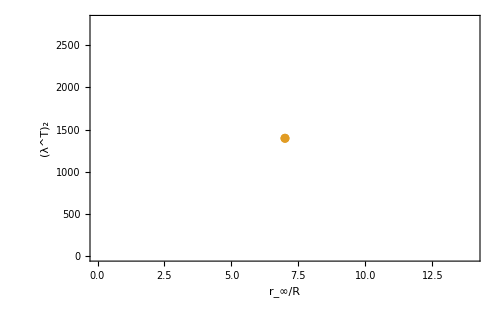

```mathematica
ListPlot[{TablePlot,{{7.,1398.4040546635376}}},PlotRange->All,Frame->True,FrameLabel->{{Style["(λ^T)_2","Latin Modern Roman",19,Black],None},{Style["r_∞/R","Latin Modern Roman",18,Black],None}},FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},ImageSize->500]
```

```mathematica
(* Computing the relative difference to see how flat the curves are *)
```

```mathematica
LoveNumvsrinf=ParallelTable[MultipoleTensorNoESInf[1,rinfS,p,β,1,h]/TidalTensorNoESInf[1,rinfS,p,β,1,h]//First,{rinfS,2,10,0.5},{p,1},{β,1,2},{h,1,Length[ρvals]}]
```

```mathematica
LoveNumatrinf2=Table[MultipoleTensorNoESInf[1,rinfS,p,β,1,h]/TidalTensorNoESInf[1,rinfS,p,β,1,h]//First,{rinfS,{2}},{p,1},{β,1,2},{h,1,Length[ρvals]}]
```

{{{{2641.1,2324.3,2087.15,1908.84,1774.53,1673.54,1598.22,1542.99,1503.74,1477.43,1461.75,1454.92,1455.57,1462.6,1475.15,1492.48,1514.,1539.19,1567.62,1598.87,1632.61,1668.48,1706.19,1745.44,1785.94,1827.39,1869.53,1912.08,1954.74,1997.23,2039.27,2080.57,2120.82,2159.75,2197.06,2232.44,2265.62,2296.3,2324.21,2349.07,2370.63,2388.53,2402.67,2412.83,2418.82,2420.5,2417.75,2410.47,2398.59,2382.11,2361.01,2335.36,2305.23,2270.75,2232.05,2189.35,2142.84,2092.81,2039.52,1983.3,1924.5,1863.53,1800.86,1737.09,1673.06,1610.1,1550.11,1494.84,1444.53,1397.89,1353.31,1311.48,1269.27,1225.71,1179.92,1131.04,1078.31,1021.08,958.946,891.912,820.606,746.629,673.095,605.312,549.123,504.365,466.409,432.348,401.022,371.949,344.887,319.681,296.214,274.387,254.104,235.278,217.823,201.657,186.699,172.872,160.101,148.316,137.447,127.43,118.204,109.711,101.895,94.706,88.0953,82.0182,76.4328,71.3,66.5839,62.251,58.2702,54.6131,51.2533,48.1664,45.3303,42.7244,40.3299},{2640.95,2324.17,2087.03,1908.73,1774.42,1673.44,1598.12,1542.89,1503.64,1477.33,1461.64,1454.81,1455.46,1462.49,1475.03,1492.36,1513.88,1539.06,1567.48,1598.73,1632.45,1668.32,1706.02,1745.26,1785.74,1827.19,1869.31,1911.84,1954.48,1996.96,2038.97,2080.24,2120.47,2159.37,2196.64,2231.98,2265.11,2295.74,2323.58,2348.36,2369.83,2387.63,2401.62,2411.61,2417.38,2418.75,2415.58,2407.67,2394.83,2376.69,2352.44,2320.18,2277.09,2224.63,2169.26,2115.65,2065.84,2020.71,1980.67,1945.96,1916.74,1893.17,1875.42,1863.67,1858.16,1859.15,1866.98,1882.01,1904.68,1935.47,1974.9,2020.87,2075.09,2137.74,2208.81,2288.01,2374.54,2466.78,2561.91,2655.29,2739.81,2805.09,2836.94,2817.59,2727.86,2552.43,2288.56,1954.68,1590.43,1242.85,946.432,713.701,540.054,413.73,322.91,259.523,222.606,202.825,187.145,173.087,160.22,148.388,137.493,127.461,118.226,109.727,101.907,94.715,88.1023,82.0238,76.4372,71.3037,66.5869,62.2535,58.2724,54.6149,51.2548,48.1678,45.3315,42.7254,40.3308}}}}

```mathematica
RelError=Table[{Range[2,10,0.5][[rinf]],Abs[(LoveNumatrinf2[[1]][[1]][[β]][[h]]-LoveNumvsrinf[[rinf]][[1]][[β]][[h]])/(LoveNumatrinf2[[1]][[1]][[β]][[h]])]//Flatten//First},{rinf,1,Length[Range[2,10,0.5]]},{β,1,Length[βvals]},{h,1,Length[ρvals]}];
```

```mathematica
(* The error is sub-percent exculding the first unphysical points *)
```

```mathematica
Show[Table[ListPlot[Table[{RelError[[rinf]][[2]][[h]][[1]],RelError[[rinf]][[2]][[h]][[2]]*100},{rinf,1,Length[Range[2,10,0.5]]}],PlotRange->All],{h,13,Length[ρvals]}],AxesLabel->{"rinf/R","Absolute relative error (%)"},PlotRange->All]
```

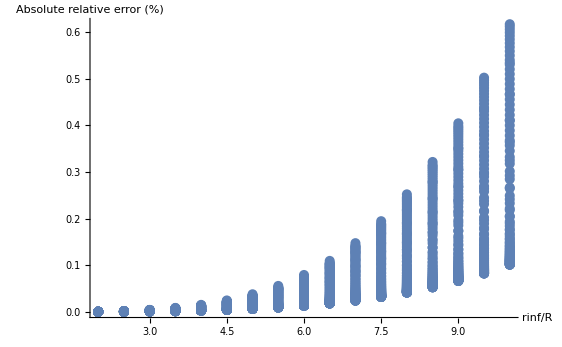
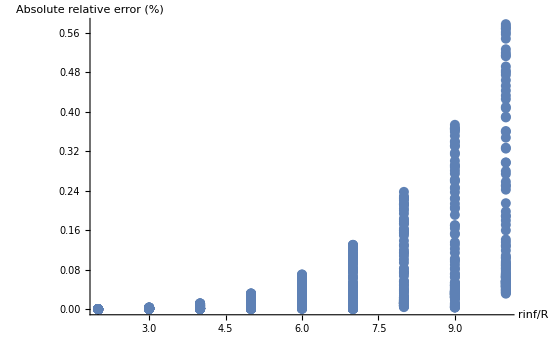

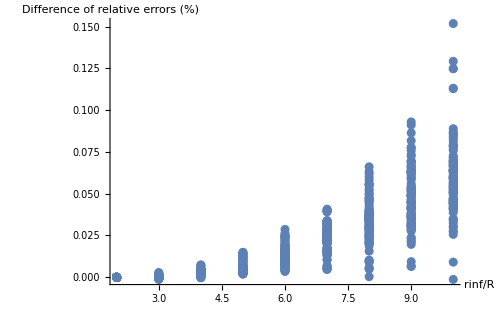

```mathematica
Show[Table[ListPlot[Table[{RelError[[2rinf-1]][[2]][[h]][[1]],(RelError[[2rinf-1]][[2]][[h]][[2]]-RelError2[[rinf]][[2]][[h]][[2]])*100},{rinf,1,Length[Range[2,10,1]]}],PlotRange->All],{h,13,Length[ρvals]}],AxesLabel->{"rinf/R","Difference of relative errors (%)"},PlotRange->All]
```

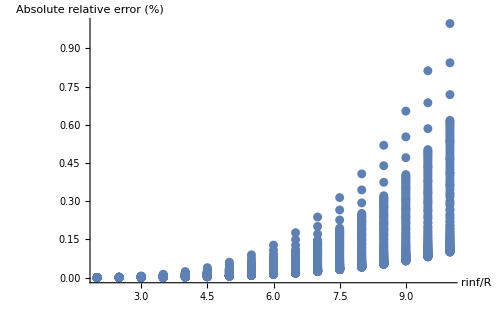

```mathematica
Show[Table[ListPlot[Table[{RelError[[rinf]][[2]][[h]][[1]],RelError[[rinf]][[2]][[h]][[2]]*100},{rinf,1,Length[Range[2,10,0.5]]}],PlotRange->All],{h,10,Length[ρvals]}],AxesLabel->{"rinf/R","Absolute relative error (%)"},PlotRange->All]
```

#### Overlap between numerics and analytics

```mathematica
(* Absolute relative difference *)
```

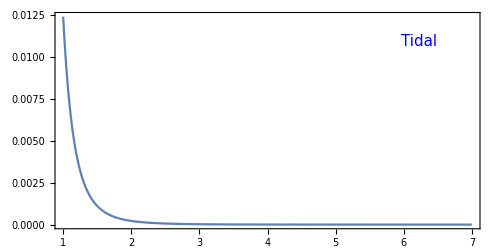

```mathematica
PLOTtest=Plot[{Abs[(Evaluate[H0[r]/.H0φpsolInfinitytoSurfacel2OnlyETTable[[3]][[1]][[1]][[70]]/.r->p*massradT[[3]][[1]][[1]][[All,1]][[70]]*km]-H0OnlyET/.r->p*massradT[[3]][[1]][[1]][[All,1]][[70]]*km/.q->ChargeTableT[[3]][[1]][[1]][[All,2]][[70]])/Evaluate[H0[r]/.H0φpsolInfinitytoSurfacel2OnlyETTable[[3]][[1]][[1]][[70]]/.r->p*massradT[[3]][[1]][[1]][[All,1]][[70]]*km]]*100/.M->ADMMassTableT[[3]][[1]][[1]][[70]]//FunctionExpand//Simplify//First},{p,1,rinfS},PlotRange->All,AspectRatio->1/2,Frame->True,FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},Epilog->{Text[Style["Tidal",15,Blue],Scaled[{0.9,0.9}],{1,1}]}]
```

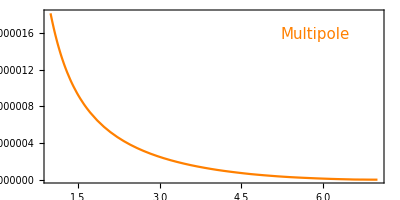

```mathematica
PLOTtest2=Plot[{Abs[(Evaluate[H0[r]/.H0φpsolInfinitytoSurfacel2OnlyQTTable[[3]][[1]][[1]][[70]]/.r->p*massradT[[3]][[1]][[1]][[All,1]][[70]]*km]-H0OnlyQT/.r->p*massradT[[3]][[1]][[1]][[All,1]][[70]]*km/.q->ChargeTableT[[3]][[1]][[1]][[All,2]][[70]])/Evaluate[H0[r]/.H0φpsolInfinitytoSurfacel2OnlyQTTable[[3]][[1]][[1]][[70]]/.r->p*massradT[[3]][[1]][[1]][[All,1]][[70]]*km]]*100/.M->ADMMassTableT[[3]][[1]][[1]][[70]]//FunctionExpand//Simplify//First},{p,1,rinfS},PlotRange->All,AspectRatio->1/2,PlotStyle->Orange,Frame->True,FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},Epilog->{Text[Style["Multipole",15,Orange],Scaled[{0.9,0.9}],{1,1}]}]
```

```mathematica
PlotMult2=ResourceFunction["PlotGrid"][{{Plot[{Evaluate[H0[r]/.H0φpsolInfinitytoSurfacel2OnlyETTable[[3]][[1]][[1]][[70]]/.r->p*massradT[[3]][[1]][[1]][[All,1]][[70]]*km],H0OnlyET/.r->p*massradT[[3]][[1]][[1]][[All,1]][[70]]*km/.q->ChargeTableT[[3]][[1]][[1]][[All,2]][[70]]/.M->ADMMassTableT[[3]][[1]][[1]][[70]]//FunctionExpand//Simplify,Evaluate[H0[r]/.H0φpsolInfinitytoSurfacel2OnlyQTTable[[3]][[1]][[1]][[70]]/.r->p*massradT[[3]][[1]][[1]][[All,1]][[70]]*km],H0OnlyQT/.r->p*massradT[[3]][[1]][[1]][[All,1]][[70]]*km/.q->ChargeTableT[[3]][[1]][[1]][[All,2]][[70]]/.M->ADMMassTableT[[3]][[1]][[1]][[70]]//FunctionExpand//Simplify},{p,1,7},PlotRange->All,PlotStyle->{Blue,{Dashed,Red},Orange,{Dashed,Purple}},PlotLegends->{Placed[LineLegend[{Dashing[1]},{Style["Numerical",15]}],{Left,Top}],Placed[LineLegend[{Dashed},{Style["Series solution",15]}],{Left,Top}]},PlotLegends->Automatic,Frame->True,Epilog->{Text[Style["Tidal",15,Blue],Scaled[{0.5,0.41}],{1,1}],Text[Style["Multipole",15,Orange],Scaled[{0.7,0.18}],{1,1}]},FrameLabel->{{Style["Moments","Latin Modern Roman",19,Black],None},{None,None}}(*,FrameTicks->{{All,None},None}*),FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},ImageSize->500]}},ImagePadding->{{80,1},{1,5}},ImageSize->500]
```

-Graphics-

```mathematica
Plot1=ResourceFunction["PlotGrid"][{{PLOTtest},{PLOTtest2}},(*Frame->True,FrameTicks->False,*)FrameLabel->{{Style["Absolute relative difference (%)","Latin Modern Roman",19,Black],None},{Style["r/R","Latin Modern Roman",18,Black],None}},FrameTicksStyle->{Directive[Black,18],Directive[Black,18]},AspectRatio->All->1/3,ImageSize->500]
```

-Graphics-

```mathematica
GraphicsColumn[{Show[PlotMult2,ImagePadding->{{127.5,22.5},{1,22}}],Show[Plot1,ImagePadding->{{118,13},{65,35}}]},Spacings->{Scaled[0.1],Scaled[-0.22]}]
```

-Graphics-

### Comparison with literature

#### Checking dif. eq. against Pani&Berti [3]

```mathematica
EqHCol=Collect[mastereqwithbackOUT/.mm'[r]->1/2 r (r φ0'[r]^2-2 mm[r] φ0'[r]^2)/.l->2//FullSimplify,{Derivative[H0][_][r],H0[r],φp[r]}]
```

(4 GN^2 φp[r] φ0'[r] (2 mm[r]+r^2 (r-2 GN mm[r]) φ0'[r]^2))/(r (r-2 GN mm[r]))+1/(r^2 (r-2 GN mm[r])^2)H0[r] (6 r^2+GN (4 mm[r] (-3 r+GN mm[r])+4 GN r^2 mm[r] (r-2 GN mm[r]) φ0'[r]^2+GN r^4 (r^2+2 mm[r] (r-3 GN r+2 (-1+GN+GN^2) mm[r])) φ0'[r]^4))+(-2 r (r-2 GN mm[r]) (r-GN mm[r]) H0'[r]-r^2 (r-2 GN mm[r])^2 H0''[r])/(r^2 (r-2 GN mm[r])^2)

```mathematica
EqφCol=Collect[eqpH/(r(r-2 mm[r]))/.mm'[r]->1/2 r (r φ0'[r]^2-2 mm[r] φ0'[r]^2)/.l->2//FullSimplify,{Derivative[φp][_][r],H0[r],φp[r]},Simplify]
```

φp[r] (-6/(r^2-2 r mm[r])-4 φ0'[r]^2)+H0[r] (-(2 mm[r] φ0'[r])/(r^2-2 r mm[r])-r φ0'[r]^3)+(2 (r-mm[r]) φp'[r])/(r (r-2 mm[r]))+φp''[r]

```mathematica
(* c0 *)
```

```mathematica
c0ME=Coefficient[EqHCol,H0[r]]/.GN->1//FullSimplify
```

(6 r^2+4 mm[r] (-3 r+mm[r]))/(r^2 (r-2 mm[r])^2)+(4 mm[r] φ0'[r]^2)/(r-2 mm[r])+r^2 φ0'[r]^4

```mathematica
c0=-(2 (2 M^2-6 M r+3 r^2))/(r^2 (-2 M+r)^2)-(4 M φ0'[r]^2)/(-2 M+r)-r^2 φ0'[r]^4
```

-(2 (2 M^2-6 M r+3 r^2))/(r^2 (-2 M+r)^2)-(4 M φ0'[r]^2)/(-2 M+r)-r^2 φ0'[r]^4

```mathematica
c0ME+c0/.mm[r]->M//Simplify
```

0

```mathematica
(* c1 *)
```

```mathematica
c1ME=Coefficient[EqHCol,H0'[r]]/.GN->1//FullSimplify
```

-1/r+1/(-r+2 mm[r])

```mathematica
c1=1/r+1/(-2 M+r)
```

1/r+1/(-2 M+r)

```mathematica
c1ME+c1/.mm[r]->M//Simplify
```

0

```mathematica
(* cS *)
cSME=Coefficient[EqHCol,φp[r]]/.GN->1//FullSimplify
```

(8 mm[r] φ0'[r])/(r^2-2 r mm[r])+4 r φ0'[r]^3

```mathematica
cS=(8 M φ0'[r])/(r (-2 M+r))+4 r φ0'[r]^3
```

(8 M φ0'[r])/(r (-2 M+r))+4 r φ0'[r]^3

```mathematica
cSME-cS/.mm[r]->M//Simplify
```

0

```mathematica
(* SO: c1=-c1ME, c2=-c2ME, cS=cSME. *)
```

```mathematica
(* c0b*)
```

```mathematica
c0bME=Coefficient[EqφCol,φp[r]]/.GN->1//FullSimplify
```

-6/(r^2-2 r mm[r])-4 φ0'[r]^2

```mathematica
c0b=6/(2 M r-r^2)-4 φ0'[r]^2
```

6/(2 M r-r^2)-4 φ0'[r]^2

```mathematica
c0bME-c0b/.mm[r]->M//Simplify
```

0

```mathematica
(* c1b *)
```

```mathematica
c1bME=Coefficient[EqφCol,φp'[r]]/.GN->1//FullSimplify
```

1/r+1/(r-2 mm[r])

```mathematica
c1b=1/r+1/(-2 M+r)
```

1/r+1/(-2 M+r)

```mathematica
c1bME-c1b/.mm[r]->M//Simplify
```

0

```mathematica
(* cSb *)
```

```mathematica
cSbME=Coefficient[EqφCol,H0[r]]/.GN->1//FullSimplify
```

-(2 mm[r] φ0'[r])/(r^2-2 r mm[r])-r φ0'[r]^3

```mathematica
cSb=(2 M φ0'[r])/(r (-2 M+r))+r φ0'[r]^3
```

(2 M φ0'[r])/(r (-2 M+r))+r φ0'[r]^3

```mathematica
cSbME+cSb/.mm[r]->M//Simplify
```

0

```mathematica
(* SO: c1b=c1MEb, c2b=c2MEb, cSb=-cSbME. *)
```

```mathematica
(* We differ in the coefficients because they choose H0=H1 whereas we have H0=-H1. *)
```

#### Computing the homogenous solutions as in Brown2022 [4]

```mathematica
(* Integrating from Origin to Surface *)
```

```mathematica
eqφpHom=eqφp/.{H0[_]->0}//FullSimplify;
```

```mathematica
mastereqwithbackINHom=-mastereqH0/.{φp[_]->0}//FullSimplify;
```

```mathematica
EoMscalarpertINNHom=Table[eqφpHom/.GN->1/.PiecePolytroperuleT[[p]],{p,1,Length[EoSIndex]}];
```

```mathematica
mastereqwithbackINNHom=Table[mastereqwithbackINHom/.GN->1/.PiecePolytroperuleT[[p]],{p,1,Length[EoSIndex]}];
```

```mathematica
H0φpsolOrigintoSurfaceNoScalarHom[p_,β_,φinf_,h_,ll_]:=NDSolve[SetPrecision[{mastereqwithbackINNHom[[p]]==0,EoMscalarpertINNHom[[p]]==0,φp[rmin]==0,φp'[rmin]== 0,H0[rmin]==rmin^ll,H0'[rmin]== ll rmin^(ll-1)}/.A[φ0[r]]->ⅇ^(1/2 βvals[[β]] φ0[r]^2)/.A'[φ0[r]]->D[ⅇ^(1/2 βvals[[β]] φ0[r]^2),φ0[r]]/.α[φ0[r]]->-βvals[[β]]φ0[r]/.α'[φ0[r]]->-βvals[[β]]/.l->ll/.BackgroundTOVPieceT[[p]][[β]][[φinf]][[h]],100],{φp,H0},{r,rmin,massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km},PrecisionGoal->15,AccuracyGoal->15,WorkingPrecision->25,Method->{"DiscontinuityProcessing"->False},MaxSteps->100000]
H0φpsolOrigintoSurfaceNoTensorHom[p_,β_,φinf_,h_,ll_]:=NDSolve[SetPrecision[{mastereqwithbackINNHom[[p]]==0,EoMscalarpertINNHom[[p]]==0,φp[rmin]==rmin^ll,φp'[rmin]== ll rmin^(ll-1),H0[rmin]==0,H0'[rmin]== 0}/.A[φ0[r]]->ⅇ^(1/2 βvals[[β]] φ0[r]^2)/.A'[φ0[r]]->D[ⅇ^(1/2 βvals[[β]] φ0[r]^2),φ0[r]]/.α[φ0[r]]->-βvals[[β]]φ0[r]/.α'[φ0[r]]->-βvals[[β]]/.l->ll/.BackgroundTOVPieceT[[p]][[β]][[φinf]][[h]],100],{φp,H0},{r,rmin,massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km},PrecisionGoal->15,AccuracyGoal->15,WorkingPrecision->25,Method->{"DiscontinuityProcessing"->False},MaxSteps->100000]
```

```mathematica
H0φpsolOrigintoSurfaceTablel2NoScalarHomφ1=ParallelTable[H0φpsolOrigintoSurfaceNoScalarHom[p,β,1,h,2],{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{h,1,Length[ρvals]}];AddtoList5[Unevaluated[{H0φpsolOrigintoSurfaceTablel2NoScalarHomφ1}]];
Export[FileNameJoin[{NotebookDirectory[],"Love_Number_ST_H0φpsolOrigintoSurfaceHomTablel2φ1v2.m"}],ExportList5];
```

```mathematica
H0φpsolOrigintoSurfaceTablel2NoTensorHomφ1=ParallelTable[H0φpsolOrigintoSurfaceNoTensorHom[p,β,1,h,2],{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{h,1,Length[ρvals]}];AddtoList5[Unevaluated[{H0φpsolOrigintoSurfaceTablel2NoTensorHomφ1}]];
Export[FileNameJoin[{NotebookDirectory[],"Love_Number_ST_H0φpsolOrigintoSurfaceHomTablel2φ1v2.m"}],ExportList5];
```

```mathematica
H0φpsolOrigintoSurfaceTablel2NoScalarHomφ2=ParallelTable[H0φpsolOrigintoSurfaceNoScalarHom[p,β,2,h,2],{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{h,1,Length[ρvals]}];AddtoList5[Unevaluated[{H0φpsolOrigintoSurfaceTablel2NoScalarHomφ2}]];
Export[FileNameJoin[{NotebookDirectory[],"Love_Number_ST_H0φpsolOrigintoSurfaceHomTablel2φ2.m"}],ExportList5];
```

```mathematica
H0φpsolOrigintoSurfaceTablel2NoTensorHomφ2=ParallelTable[H0φpsolOrigintoSurfaceNoTensorHom[p,β,2,h,2],{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{h,1,Length[ρvals]}];AddtoList5[Unevaluated[{H0φpsolOrigintoSurfaceTablel2NoTensorHomφ2}]];
Export[FileNameJoin[{NotebookDirectory[],"Love_Number_ST_H0φpsolOrigintoSurfaceHomTablel2φ2.m"}],ExportList5];
```

```mathematica
H0φpsolOrigintoSurfaceTablel2NoScalarHomφ3=ParallelTable[H0φpsolOrigintoSurfaceNoScalarHom[p,β,3,h,2],{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{h,1,Length[ρvals]}];AddtoList5[Unevaluated[{H0φpsolOrigintoSurfaceTablel2NoScalarHomφ3}]];
Export[FileNameJoin[{NotebookDirectory[],"Love_Number_ST_H0φpsolOrigintoSurfaceHomTablel2φ3.m"}],ExportList5];
```

```mathematica
H0φpsolOrigintoSurfaceTablel2NoTensorHomφ3=ParallelTable[H0φpsolOrigintoSurfaceNoTensorHom[p,β,3,h,2],{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{h,1,Length[ρvals]}];AddtoList5[Unevaluated[{H0φpsolOrigintoSurfaceTablel2NoTensorHomφ3}]];
Export[FileNameJoin[{NotebookDirectory[],"Love_Number_ST_H0φpsolOrigintoSurfaceHomTablel2φ3.m"}],ExportList5];
```

```mathematica
(* Integrating from Infinity to Surface *)
```

```mathematica
rinfS=7;
```

```mathematica
mastereqwithbackOUTHom=mastereqwithbackOUT/.φp[_]->0;
eqpHHom=eqpH/.H0[_]->0;
```

```mathematica
H0φpsolInfinitytoSurfacel2OnlyESHom[p_,β_,φinf_,h_]:=NDSolve[{r^2 mastereqwithbackOUTHom==0, eqpHHom==0,H0[rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]==0*H0OnlyES/.r->rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km,H0'[rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]==D[0*H0OnlyES,r]/.r->rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km,φp[rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]==φpOnlyES/.r->rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km,φp'[rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]==D[φpOnlyES,r]/.r->rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km}/.φ0solOUTSolsT[[p]][[β]][[φinf]][[h]] /.q->ChargeTableT[[p]][[β]][[φinf]][[All,2]][[h]]/.M->ADMMassTableT[[p]][[β]][[φinf]][[h]]/.l->2/.GN->1//Flatten//N,{φp,H0},{r,rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km,massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km}];
```

```mathematica
H0φpsolInfinitytoSurfacel2OnlyQSHom[p_,β_,φinf_,h_]:=NDSolve[{r^2 mastereqwithbackOUTHom==0,eqpHHom==0,H0[rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]==0*H0OnlyQS/.r->rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km,H0'[rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]==D[0*H0OnlyQS,r]/.r->rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km,φp[rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]==φpOnlyQS/.r->rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km,φp'[rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]==D[φpOnlyQS,r]/.r->rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km} /.q->ChargeTableT[[p]][[β]][[φinf]][[All,2]][[h]]/.M->ADMMassTableT[[p]][[β]][[φinf]][[h]]/.φ0solOUTSolsT[[p]][[β]][[φinf]][[h]]/.l->2/.GN->1//Flatten//N,{φp,H0},{r, rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km,massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km}];
```

```mathematica
H0φpsolInfinitytoSurfacel2OnlyETHom[p_,β_,φinf_,h_]:=NDSolve[{r^2 mastereqwithbackOUTHom==0, eqpHHom==0,φp[rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]==0*φpOnlyET/.r->rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km,φp'[rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]==D[0*φpOnlyET,r]/.r->rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km,H0[rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]==H0OnlyET/.r->rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km,H0'[rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]==D[H0OnlyET,r]/.r->rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km} /.q->ChargeTableT[[p]][[β]][[φinf]][[All,2]][[h]]/.M->ADMMassTableT[[p]][[β]][[φinf]][[h]]/.φ0solOUTSolsT[[p]][[β]][[φinf]][[h]]/.l->2/.GN->1//Flatten//N,{φp,H0},{r, rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km,massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km}];
```

```mathematica
H0φpsolInfinitytoSurfacel2OnlyQTHom[p_,β_,φinf_,h_]:=NDSolve[{r^2 mastereqwithbackOUTHom==0, eqpHHom==0,H0[rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]==H0OnlyQT/.r->rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km,H0'[rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]==D[H0OnlyQT,r]/.r->rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km,φp[rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]==0*φpOnlyQT/.r->rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km,φp'[rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]==D[0*φpOnlyQT,r]/.r->rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km}/.q->ChargeTableT[[p]][[β]][[φinf]][[All,2]][[h]]/.M->ADMMassTableT[[p]][[β]][[φinf]][[h]]/.φ0solOUTSolsT[[p]][[β]][[φinf]][[h]]/.l->2/.GN->1//Flatten//N,{φp,H0},{r, rinfS*massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km,massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km}];
```

```mathematica
(* Computing for every configuration for l=2 *)
```

```mathematica
H0φpsolInfinitytoSurfacel2OnlyESTableHom=Table[H0φpsolInfinitytoSurfacel2OnlyESHom[p,β,φinf,h],{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
H0φpsolInfinitytoSurfacel2OnlyQSTableHom=Table[H0φpsolInfinitytoSurfacel2OnlyQSHom[p,β,φinf,h],{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
H0φpsolInfinitytoSurfacel2OnlyETTableHom=Table[H0φpsolInfinitytoSurfacel2OnlyETHom[p,β,φinf,h],{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
H0φpsolInfinitytoSurfacel2OnlyQTTableHom=Table[H0φpsolInfinitytoSurfacel2OnlyQTHom[p,β,φinf,h],{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
```

```mathematica
H0φpsolOrigintoSurfaceTablel2NoTensorHom={H0φpsolOrigintoSurfaceTablel2NoTensorHomφ1,H0φpsolOrigintoSurfaceTablel2NoTensorHomφ2,H0φpsolOrigintoSurfaceTablel2NoTensorHomφ3};
H0φpsolOrigintoSurfaceTablel2NoScalarHom={H0φpsolOrigintoSurfaceTablel2NoScalarHomφ1,H0φpsolOrigintoSurfaceTablel2NoScalarHomφ2,H0φpsolOrigintoSurfaceTablel2NoScalarHomφ3};
```

```mathematica
(* Solutions from the inside integration *)
```

```mathematica
φpINNoTHom=Table[Evaluate[φp[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolOrigintoSurfaceTablel2NoTensorHom[[φinf]][[p]][[β]][[h]]]//Flatten//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
φpINNoSHom=Table[Evaluate[φp[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolOrigintoSurfaceTablel2NoScalarHom[[φinf]][[p]][[β]][[h]]]//Flatten//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
φppINNoTHom=Table[Evaluate[φp'[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolOrigintoSurfaceTablel2NoTensorHom[[φinf]][[p]][[β]][[h]]]//Flatten//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
φppINNoSHom=Table[Evaluate[φp'[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolOrigintoSurfaceTablel2NoScalarHom[[φinf]][[p]][[β]][[h]]]//Flatten//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
H0INNoTHom=Table[Evaluate[H0[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolOrigintoSurfaceTablel2NoTensorHom[[φinf]][[p]][[β]][[h]]]//Flatten//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
H0INNoSHom=Table[Evaluate[H0[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolOrigintoSurfaceTablel2NoScalarHom[[φinf]][[p]][[β]][[h]]]//Flatten//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
H0pINNoTHom=Table[Evaluate[H0'[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolOrigintoSurfaceTablel2NoTensorHom[[φinf]][[p]][[β]][[h]]]//Flatten//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
H0pINNoSHom=Table[Evaluate[H0'[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolOrigintoSurfaceTablel2NoScalarHom[[φinf]][[p]][[β]][[h]]]//Flatten//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
```

```mathematica
(* Solutions from the outside integration *)
```

```mathematica
φpOUTESHom=Table[Evaluate[φp[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyESTableHom[[p]][[β]][[φinf]][[h]]]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
φpOUTQSHom=Table[Evaluate[φp[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyQSTableHom[[p]][[β]][[φinf]][[h]]]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
φpOUTETHom=Table[Evaluate[φp[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyETTableHom[[p]][[β]][[φinf]][[h]]]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
φpOUTQTHom=Table[Evaluate[φp[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyQTTableHom[[p]][[β]][[φinf]][[h]]]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
φppOUTESHom=Table[Evaluate[φp'[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyESTableHom[[p]][[β]][[φinf]][[h]]]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
φppOUTQSHom=Table[Evaluate[φp'[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyQSTableHom[[p]][[β]][[φinf]][[h]]]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
φppOUTETHom=Table[Evaluate[φp'[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyETTableHom[[p]][[β]][[φinf]][[h]]]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
φppOUTQTHom=Table[Evaluate[φp'[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyQTTableHom[[p]][[β]][[φinf]][[h]]]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
H0OUTESHom=Table[Evaluate[H0[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyESTableHom[[p]][[β]][[φinf]][[h]]]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
H0OUTQSHom=Table[Evaluate[H0[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyQSTableHom[[p]][[β]][[φinf]][[h]]]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
H0OUTETHom=Table[Evaluate[H0[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyETTableHom[[p]][[β]][[φinf]][[h]]]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
H0OUTQTHom=Table[Evaluate[H0[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyQTTableHom[[p]][[β]][[φinf]][[h]]]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
H0pOUTESHom=Table[Evaluate[H0'[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyESTableHom[[p]][[β]][[φinf]][[h]]]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
H0pOUTQSHom=Table[Evaluate[H0'[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyQSTableHom[[p]][[β]][[φinf]][[h]]]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
H0pOUTETHom=Table[Evaluate[H0'[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyETTableHom[[p]][[β]][[φinf]][[h]]]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
H0pOUTQTHom=Table[Evaluate[H0'[massradT[[p]][[β]][[φinf]][[All,1]][[h]]*km]/.H0φpsolInfinitytoSurfacel2OnlyQTTableHom[[p]][[β]][[φinf]][[h]]]//First,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
```

```mathematica
(* Matching *)
```

```mathematica
ConstNoETHom=Table[Solve[{cIN1 φpINNoTHom[[p]][[β]][[φinf]][[h]]+cIN2 φpINNoSHom[[p]][[β]][[φinf]][[h]] == cOUT1 φpOUTESHom[[p]][[β]][[φinf]][[h]]+ cOUT2 φpOUTQSHom[[p]][[β]][[φinf]][[h]] + cOUT3 φpOUTETHom[[p]][[β]][[φinf]][[h]] +cOUT4 φpOUTQTHom[[p]][[β]][[φinf]][[h]],
cIN1 φppINNoTHom[[p]][[β]][[φinf]][[h]]+cIN2 φppINNoSHom[[p]][[β]][[φinf]][[h]] == cOUT1 φppOUTESHom[[p]][[β]][[φinf]][[h]]+ cOUT2 φppOUTQSHom[[p]][[β]][[φinf]][[h]] + cOUT3 φppOUTETHom[[p]][[β]][[φinf]][[h]] +cOUT4 φppOUTQTHom[[p]][[β]][[φinf]][[h]],
cIN1 H0INNoTHom[[p]][[β]][[φinf]][[h]]+cIN2 H0INNoSHom[[p]][[β]][[φinf]][[h]] == cOUT1 H0OUTESHom[[p]][[β]][[φinf]][[h]]+ cOUT2 H0OUTQSHom[[p]][[β]][[φinf]][[h]] + cOUT3 H0OUTETHom[[p]][[β]][[φinf]][[h]] +cOUT4 H0OUTQTHom[[p]][[β]][[φinf]][[h]],cIN1 H0pINNoTHom[[p]][[β]][[φinf]][[h]]+cIN2 H0pINNoSHom[[p]][[β]][[φinf]][[h]] == cOUT1 H0pOUTESHom[[p]][[β]][[φinf]][[h]]+ cOUT2 H0pOUTQSHom[[p]][[β]][[φinf]][[h]] + cOUT3 H0pOUTETHom[[p]][[β]][[φinf]][[h]] +cOUT4 H0pOUTQTHom[[p]][[β]][[φinf]][[h]]}//Simplify,{cIN2,cOUT1,cOUT2,cOUT4}]/.{cIN1->1,cOUT3->0},{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
```

```mathematica
ConstNoESHom=Table[Solve[{cIN1 φpINNoTHom[[p]][[β]][[φinf]][[h]]+cIN2 φpINNoSHom[[p]][[β]][[φinf]][[h]] == cOUT1 φpOUTESHom[[p]][[β]][[φinf]][[h]]+ cOUT2 φpOUTQSHom[[p]][[β]][[φinf]][[h]] + cOUT3 φpOUTETHom[[p]][[β]][[φinf]][[h]] +cOUT4 φpOUTQTHom[[p]][[β]][[φinf]][[h]],
cIN1 φppINNoTHom[[p]][[β]][[φinf]][[h]]+cIN2 φppINNoSHom[[p]][[β]][[φinf]][[h]] == cOUT1 φppOUTESHom[[p]][[β]][[φinf]][[h]]+ cOUT2 φppOUTQSHom[[p]][[β]][[φinf]][[h]] + cOUT3 φppOUTETHom[[p]][[β]][[φinf]][[h]] +cOUT4 φppOUTQTHom[[p]][[β]][[φinf]][[h]],
cIN1 H0INNoTHom[[p]][[β]][[φinf]][[h]]+cIN2 H0INNoSHom[[p]][[β]][[φinf]][[h]] == cOUT1 H0OUTESHom[[p]][[β]][[φinf]][[h]]+ cOUT2 H0OUTQSHom[[p]][[β]][[φinf]][[h]] + cOUT3 H0OUTETHom[[p]][[β]][[φinf]][[h]] +cOUT4 H0OUTQTHom[[p]][[β]][[φinf]][[h]],cIN1 H0pINNoTHom[[p]][[β]][[φinf]][[h]]+cIN2 H0pINNoSHom[[p]][[β]][[φinf]][[h]] == cOUT1 H0pOUTESHom[[p]][[β]][[φinf]][[h]]+ cOUT2 H0pOUTQSHom[[p]][[β]][[φinf]][[h]] + cOUT3 H0pOUTETHom[[p]][[β]][[φinf]][[h]] +cOUT4 H0pOUTQTHom[[p]][[β]][[φinf]][[h]]}//Simplify,{cIN1,cOUT3,cOUT2,cOUT4}]/.{cIN2->1,cOUT1->0},{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]},{h,1,Length[ρvals]}];
```

```mathematica
MultipoleScalarNoETHom=Table[cOUT2*(MultipoleOrder!)/((2MultipoleOrder-1)!!)/.ConstNoETHom[[p]][[β]][[φinf]]//Flatten,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]}];
TidalScalarNoETHom=Table[cOUT1*(MultipoleOrder!)/.ConstNoETHom[[p]][[β]][[φinf]]//Flatten,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]}];
MultipoleTensorNoETHom=Table[1/2 cOUT4*(MultipoleOrder!)/((2MultipoleOrder-1)!!)/.ConstNoETHom[[p]][[β]][[φinf]]//Flatten,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]}];
```

```mathematica
MultipoleScalarNoESHom=Table[cOUT2*(MultipoleOrder!)/((2MultipoleOrder-1)!!)/.ConstNoESHom[[p]][[β]][[φinf]]//Flatten,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]}];
TidalTensorNoESHom=Table[1/2 cOUT3*(MultipoleOrder!)/.ConstNoESHom[[p]][[β]][[φinf]]//Flatten,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]}];
MultipoleTensorNoESHom=Table[1/2 cOUT4*(MultipoleOrder!)/((2MultipoleOrder-1)!!)/.ConstNoESHom[[p]][[β]][[φinf]]//Flatten,{p,1,Length[EoSIndex]},{β,1,Length[βvals]},{φinf,1,Length[φinfvals]}];
```

```mathematica
LoveNumGRHom=Table[16/15(1-2CC)^2(2+2CC(y-1)-y)*(2CC(6-3y+3CC(5y-8))+4 CC^3(13-11y+CC(3y-2)+2 CC^2(y+1))+3(1-2CC)^2(2-y+2CC(y-1))Log[1-2CC])^-1/.CC->CompactnessGRT[[p]][[h]]/.y->((H0pINNoSHom[[p]][[h]])/(H0INNoSHom[[p]][[h]]))*massradT[[p]][[1]][[1]][[All,1]][[h]]*km,{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];
```

```mathematica
LoveNumGRScalarHom=Table[-((8 (-1+2 CC) (3 (-2+y)+2 CC (3+(-3+CC) y)))/(135 (4 CC (3+(-6+CC) CC)-6 (-1+CC) CC (-1+2 CC) y+(-1+2 CC) (3 (-2+y)+2 CC (3+(-3+CC) y)) Log[1-2 CC])))/.CC->CompactnessGRT[[p]][[h]]/.y->((φppINNoTHom[[p]][[h]])/(φpINNoTHom[[p]][[h]]))*massradT[[p]][[1]][[1]][[All,1]][[h]]*km,{p,1,Length[EoSIndex]},{h,1,Length[ρvals]}];
```

```mathematica
(* Plots *)
```

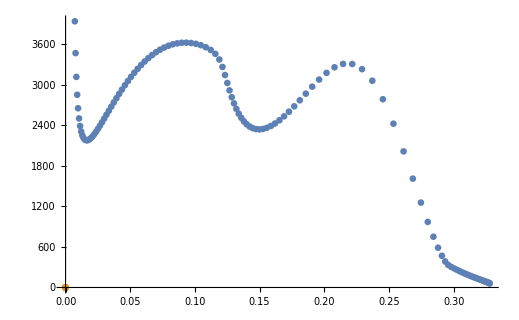

```mathematica
ListPlot[{Table[{CompactnessT[[1]][[2]][[1]][[h]],3/2(MultipoleTensorNoESHom[[1]][[2]][[1]]/TidalTensorNoESHom[[1]][[2]][[1]])[[h]]},{h,1,Length[ρvals]}],0*Table[{CompactnessT[[1]][[2]][[1]][[h]],3/2 LoveNumGRHom[[1]][[2]][[1]][[h]]*(CompactnessT[[1]][[2]][[1]][[h]])^5},{h,1,Length[ρvals]}]},PlotRange->Automatic]
```

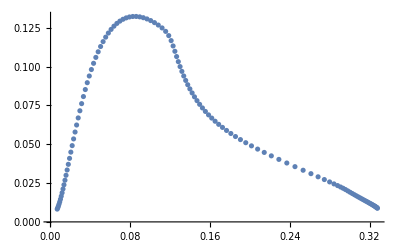

```mathematica
ListPlot[Table[{CompactnessT[[1]][[2]][[1]][[h]],3/2(MultipoleTensorNoESHom[[1]][[2]][[1]]/TidalTensorNoESHom[[1]][[2]][[1]])[[h]](massradT[[1]][[2]][[1]][[All,1]][[h]]*km)^-5},{h,1,Length[ρvals]}],PlotRange->All]
```

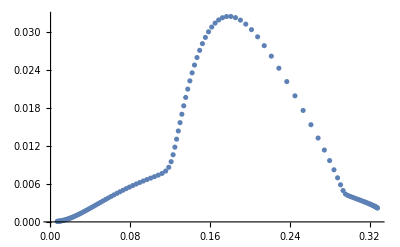

```mathematica
ListPlot[Table[{CompactnessT[[1]][[2]][[1]][[h]],3/2(MultipoleScalarNoETHom[[1]][[2]][[1]]/TidalScalarNoETHom[[1]][[2]][[1]])[[h]](massradT[[1]][[2]][[1]][[All,1]][[h]]*km)^-5},{h,1,Length[ρvals]}],PlotRange->All]
```

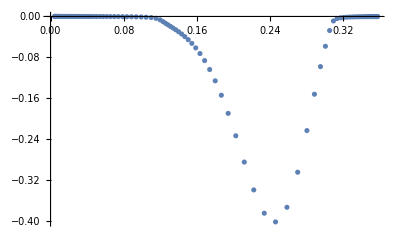

```mathematica
ListPlot[Table[{CompactnessT[[3]][[2]][[1]][[h]],3/2(MultipoleScalarNoESHom[[3]][[2]][[1]]/TidalTensorNoESHom[[3]][[2]][[1]])[[h]](massradGRT[[3]][[2]][[1]][[All,1]][[h]]*km)^-5},{h,1,Length[ρvals]}],PlotRange->All]
```

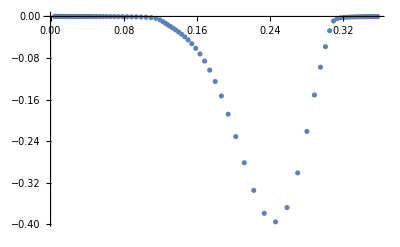

```mathematica
ListPlot[Table[{CompactnessT[[3]][[2]][[1]][[h]],3/2(MultipoleTensorNoETHom[[3]][[2]][[1]]/TidalScalarNoETHom[[3]][[2]][[1]])[[h]](massradGRT[[3]][[2]][[1]][[All,1]][[h]]*km)^-5},{h,1,Length[ρvals]}],PlotRange->All]
```

### References

[1]  G. Creci, T. Hinderer and J. Steinhoff, Tidal properties of neutron stars in scalar- tensor theories of gravity, Phys. Rev. D 108, 124073 (2023), arXiv:2308.11323 [gr- qc].
[2] J. S. Read, B. D. Lackey, B. J. Owen, and J. L. Friedman, Constraints on a phenomenologically parameterized neutron-star equation of state, Phys. Rev. D 79, 124032 (2009), arXiv:0812.2163 [astro-ph].
[3] P. Pani and E. Berti, Slowly rotating neutron stars in scalar-tensor theories, Phys. Rev. D 90, 024025 (2014), arXiv:1405.4547 [gr-qc].
[4] S. M. Brown, Tidal Deformability of Neutron Stars in Scalar-Tensor Theories of Gravity for Gravitational Wave Analysis, (2022), arXiv:2210.14025 [gr-qc].